# Heat Conduction with Orthonormal Moments (BGK)

## Heat Conduction Systematic (Orthonormal)

## Core routines

### Basic routines

```mathematica
Off[Solve::svars]
```

```mathematica
MakeOrder[m_]:=Take[Drop[Flatten[Table[{k,k},{k,m,1,-1}]],-1],-m]
MakeFull[m_]:=Take[Flatten[Table[{k,k},{k,m,1,-1}]],-m]
MakeComplete[m_]:=Table[m,{ii,1,m}];
colorlist={Black,Blue,Red,Darker[Green],Darker[Yellow],Orange,Lighter[Green],Lighter[Brown],Purple,Cyan}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Removing the y component of velocity and the density*)

Size[theory_]:=Total[theory]-2;
```

### Equations

```mathematica
Clear[dw]

(*value of the normal velocity*)
dw[0,1]:=0;
OrthoEqn[b_,m_]:=Expand[√2(√(m/(2m+1))√(m+b+1/2)m/(2m-1)dw[b,m-1]-√(m/(2m+1))√(b+1)m/(2m-1)dw[b+1,m-1]+√((m+1)/(2m+3))√(m+b+3/2)dw[b,m+1]-√((m+1)/(2m+3))√b dw[b-1,m+1])]
```

```mathematica
Clear[res,nn,var,eqn,b0,A0,P0,a,n,w,ww,unknowns,λ0,λ,λPlus,vv,v,Ansatz,Coefs,v0,v1,v2,v3,v4,C0,k,x]

GetSolution[theory_,reg_]:=Block[{res,nn,var,varC,eqn,b0,a,n,w,dw,λ0,λ,λPlus,v,vv,Ansatz,Coefs,C0,Signum,SymmetryConditions,k,x,jj,ii},
aIdx=theory;
nn=Length[aIdx];

(*Delete is for removing the density and the velocity. The reason for removing the first equation is obvious. aIdx[[1]]+1 removes the energy balance because it contains the denstiy and the stress tensor. Since we are not interested in density, we let it go.*)

var=Delete[Flatten[Table[Table[dw[a,n-1],{a,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];
eqn=Delete[Flatten[Table[Table[OrthoEqn[a,n-1],{a,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];
If[reg==1,
varC=Join[Table[dw[(nn)/2-kk/2,kk],{kk,nn-2,1,-2}],{dw[0,nn-1]}];
eqn=Delete[Flatten[Table[Table[If[MemberQ[varC,dw[a,n-1]],OrthoEqn[a,n-1]/.Thread[varC->0],OrthoEqn[a,n-1]],{a,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];
];
{b0,A0}=CoefficientArrays[eqn,var];

P0=SparseArray[{{i_,i_}->-1},Size[aIdx]];

(*only for the momentum balance*)
P0⟦1,1⟧=0;

(*generalized eigen vector and eigen value of P0 with respect to A0*)
{λ0,vv}=Chop[Eigensystem[{P0,1.0A0}]];

(*remove the zero and the infinite eigen values, why do the infinite eigen values appear? *)
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,Select[λ0,(0<Abs[#]<∞)&]}],1]];

(*assumes symmetric spectrum*)
λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];


λPlus=Select[λ,(#>0)&];

(*a polynomial ansatz*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,Length[var]}];
Coefs=Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,Length[var]}]];

(*vector for the forcing term*)
B0=Table[0,{i,1,Length[var]}];
B0⟦1⟧=1;

(*ansatz for the particular solution of the equations.*)
Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+α B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};
(*
v4=Table[0,{i,1,Length[var]}];
v4⟦1⟧=-1/20;
v3=-4A0.v4;
v2=-3(A0.v3-27/25 B0);
v1=-2A0.v2;
v0=-A0.v1;
 20 C0 v4-α/Kn(Kn^4 v0+Kn^3 v1 x+Kn^2 v2 x^2+Kn v3 x^3+v4 x^4)  *)

Signum=Table[0,{ii,1,Length[λ],2}];

(*store the sign of the first non-zero entry in the eigenvectors*)

Do[jj=1;While[v⟦ii,jj⟧==0,jj++];Signum⟦(ii+1)/2⟧=-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧],{ii,1,Length[λ],2}];
SymmetryConditions=Table[k[ii]->-Signum⟦(ii+1)/2⟧k[ii+1],{ii,1,Length[λ],2}];

(*The final result is the particular solution + the solution to the homogeneous problem. The particular solution is the Ansatz and the homogeneous solution is the part: C0 B0+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn]*)

res=Chop[ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]]]/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]
];
```

```mathematica
u[x_]=GetSolution[{4,3,3,2,1},0];

Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]+α B0 x^2]]]
```

{0,0,0,0,0,0,0,0,0,0,0}

### Distribution Function

```mathematica
Unprotect[C];
Clear[C];

(*same as in Manuels paper on Explicit fluxes*)
S[a_,n_,x_]:=√(a!(n+a)!)Sum[(-1)^p/(p!(a-p)!(p+n)!)x^p,{p,0,a}]

TraceFreeNormalVariables[A_,ix_]:=Block[{n=Length[ix],n1=Count[ix,1],n2=Count[ix,2],n3=Count[ix,3],idx,res},
idx=Table[2,{ii,1,n}];
If[(OddQ[n1])||(OddQ[n3]),res=0,res=(-1/2)^((n3+n1)/2)A[idx]];
(*If[(OddQ[n1])||(OddQ[n3]),res=0,res=ix];*)
res
];

TraceFreeNormalVariables1[A_,ix_]:=Block[{n=Length[ix],n1=Count[ix,1],n2=Count[ix,2],n3=Count[ix,3],idx,res},
idx=Table[2,{ii,1,n}];
If[(OddQ[n1])||(OddQ[n3]),res=0,res=ix];
res
];

TraceFreeCoord[idx_]:=Block[{nx=Count[idx,1],ny=Count[idx,2],nz=Count[idx,3],n=Length[idx]},
Expand[(-1)^n/((2n-1)!!)(√(Cx^2+Cy^2+Cz^2))^(2n+1)D[D[D[1/(√(Cx^2+Cy^2+Cz^2)),{Cx,nx}],{Cy,ny}],{Cz,nz}]]
];

(*The following function returns the basis function in the distribution function corresponding to those variables which we need for the heat conduction problem i.e. those variables which have all the indices as y.*)

phiTerm[s_,n_]:=Expand[Simplify[√(((2n+1)!!)/(2n!)√π)S[s,n+1/2,(Cx^2+Cy^2+Cz^2)/2] 1/(√2)^n Total[Map[(TraceFreeNormalVariables[w[s,Length[#]]&,#]TraceFreeCoord[#])&,Tuples[{1,2,3},n]]]]];
```

```mathematica
Clear[aIdx,nn,n,phi]

tfcMax=20;
tracefreecoord1=Table[Table[Table[Expand[(-1)^(nx+ny+nz)/((2(nx+ny+nz)-1)!!)(√(Cx^2+Cy^2+Cz^2))^(2(nx+ny+nz)+1)D[D[D[1/(√(Cx^2+Cy^2+Cz^2)),{Cx,nx}],{Cy,ny}],{Cz,nz}]],{nx,Max[nz,ny],(tfcMax-nz-ny)}],{ny,nz,(tfcMax-nz)/2}],{nz,0,tfcMax/3}];

TraceFreeCoord1[idx_]:=Block[{res,n1=idx⟦1⟧+1,n2=idx⟦2⟧+1,n3=idx⟦3⟧+1,n=idx⟦1⟧+idx⟦2⟧+idx⟦3⟧},
Which[
n1≥n2≥ n3,
res=tracefreecoord1⟦n3,n2-n3+1,n1-n2+1⟧/.{Cx->C1,Cy->C2,Cz->C3},
n2≥n1≥ n3,
res=tracefreecoord1⟦n3,n1-n3+1,n2-n1+1⟧/.{Cx->C2,Cy->C1,Cz->C3},
n3≥n2≥ n1,
res=tracefreecoord1⟦n1,n2-n1+1,n3-n2+1⟧/.{Cx->C3,Cy->C2,Cz->C1},
n1≥n3≥ n2,
res=tracefreecoord1⟦n2,n3-n2+1,n1-n3+1⟧/.{Cx->C1,Cy->C3,Cz->C2},
n2≥n3≥ n1,
res=tracefreecoord1⟦n1,n3-n1+1,n2-n3+1⟧/.{Cx->C2,Cy->C3,Cz->C1},
n3≥n1≥ n2,
res=tracefreecoord1⟦n2,n1-n2+1,n3-n1+1⟧/.{Cx->C3,Cy->C1,Cz->C2}
];
res/.{C1->Cx,C2->Cy,C3->Cz}
];

S[a_,n_,x_]:=√(a!(n+a)!)Sum[(-1)^p/(p!(a-p)!(p+n)!)x^p,{p,0,a}]

(*The following function develops phi and does nothing more. Why different from phiTerm*)
bcBuild1[theory_]:=Block[{tmp1,aIdx,nn,idx0,digits,part},
aIdx=theory;
nn=Length[aIdx];

phi=1;
phi=Table[Table[0,{aa,0,aIdx⟦n+1⟧-1}],{n,0,nn-1}];
Do[
tmp1=Sum[Sum[Multinomial[n-2k,2k-2j,2j]TraceFreeCoord1[{2j,n-2k,2k-2j}](-1/2)^k w[ss,n],{j,0,k}],{k,0,n/2}];
Do[
phi⟦n+1,aa+1⟧=1/(√2)^n √(((2n+1)!!)/(2n!)√π)S[aa,n+1/2,CC/2]tmp1/.{ss->aa};
,{aa,0,aIdx⟦n+1⟧-1}];

,{n,0,nn-1}];
]

(*The same thing as phiTerm*)
φ0[a_,n_]:=phi⟦n+1,a+1⟧
```

```mathematica
bcBuild1[MakeComplete[10]]
```

```mathematica
Expand[φ0[1,5]-phiTerm[1,5]/.{CC->Cx^2+Cy^2+Cz^2}]
```

0

```mathematica
φ0[2,1]
```

3/4 Cy (2/(3 √π)-(4 CC)/(15 √π)+(2 CC^2)/(105 √π)) √((35 π)/2) w[2,1]

### Boundary Conditions

```mathematica
Clear[w,phi,bc,pos,pos1,pos2,mm,α,nn,res,res1,ex,a,b,ex0]

psi[s_,n_]:=Expand[√(((2n+1)!!)/(2n!)√π)S[s,n+1/2,CC/2] TraceFreeCoord[Table[2,{ii,1,n}]]/(√2)^n];
psi1[s_,n_]:=Expand[√(((2n+1)!!)/(2n!)√π)S1[s,n+1/2,CC/2] TraceFreeCoord1[{0,n,0}]/(√2)^n];

(*Integrates (∫^π)_0 Sin[α]^nn Cos[α]^mm dα*)
IntegrateCosSin[α_,ex_]:=Block[{pos1,pos2,mm=0,nn=0,res,res1=Sin[α]Cos[α] ex},
pos1=Position[res1,Sin[α]^_];
pos2=Position[res1,Cos[α]^_];
If[Length[pos1]>0,
mm=Extract[res1,pos1⟦1⟧]⟦2⟧-1;
];
If[Length[pos2]>0,
nn=Extract[res1,pos2⟦1⟧]⟦2⟧-1;
];
res=Delete[res1,Join[pos1,pos2]]((1+(-1)^nn)  Gamma[(1+mm)/2]Gamma[(1+nn)/2])/(2 Gamma[1+mm/2+nn/2]);

(*The division is to make sure that ex is not of the form ex = C Sin[α]^-1 or C Cos[α]^-1. In such a case we do not perform the integration and simply return the input.*)
If[Length[pos1]==0,
res=res/Sin[α];
];
If[Length[pos2]==0,
res=res/Cos[α];
];
res
]

(*For the expressions this integrates, see the bottom section on integration*)
IntegrateLaguerre[a_,ex_]:=Block[{pos,nn=0,res=ex,ex0,res1,p,b},
ex0=b ex/.{a->b^2};
pos=Table[{p⟦1⟧},{p,Position[ex0,b]}];
res1=Delete[ex0,pos]Simplify[Apply[Times,Extract[ex0,pos]],Assumptions->{Re[b]>0,b∈Reals}];

pos=Position[res1,b^_];
If[Length[pos]>0,
nn=(Extract[res1,pos⟦1⟧]⟦2⟧-1)/2;
res=Delete[res1,pos]nn!/.b->a^(1/2);
];
res
]

(*The following function integrates (∫^∞)_(-∞)x^n Exp[-x^2/2]dx*)
IntegrateGauss[a_,ex_]:=Block[{pos=Position[a ex,a^_],nn=0,res=√(2π)ex},
If[Length[pos]>0,
nn=(Extract[a ex,pos⟦1⟧]⟦2⟧-1)/2;
If[IntegerQ[nn],res=Delete[a ex,pos] √(2π)(2nn-1)!! ,res=0];
];
res
]

(*The following function integrates (∫^∞)_0 x^n Exp[-x^2/2]dx*)
IntegrateHalfGauss[a_,ex_]:=Block[{pos=Position[a ex,a^_],nn=0,res=√(π/2)ex},
If[Length[pos]>0,
nn=Extract[a ex,pos⟦1⟧]⟦2⟧-1;
res=Delete[a ex,pos](√2)^(nn+1)Gamma[(nn+1)/2]/2 ;
];
res
]

(*The following function computes the moment of the fw and fgas again the basis function identified with (s,n) for a given theory.*)
bc[s_,n_,theory_]:=Block[{IntWall,IntGas,res,nn=Length[theory],b,m,dummy},
res=Table[Table[0,{b,0,theory⟦m+1⟧-1}],{m,0,nn-1}];

(*psi is the function we are testing the equation with and φ0 is the basis function for the phase density.*)

PrintTemporary["bc: ("<>ToString[s]<>", "<>ToString[n]<>")"];
Do[
Do[
IntGas=Expand[dummy+(CC Sin[θ]dC)/(√(2π))^2 psi1[s,n]φ0[b,m]/.{CC->C^2}/.{Cx->C Cos[φ]Sin[θ],Cy->C Sin[φ]Sin[θ],Cz->C Cos[θ]}/.{C->√(2x),dC->1/(√(2x))dx}/.{S1->S}];
IntGas=Expand[Apply[Plus,Table[IntegrateLaguerre[x,IntGas⟦kk⟧],{kk,1,Length[IntGas]}]]];
IntGas=Expand[Apply[Plus,Table[IntegrateCosSin[θ,IntGas⟦kk⟧],{kk,1,Length[IntGas]}]]];
IntGas=Expand[Apply[Plus,Table[IntegrateCosSin[φ,IntGas⟦kk⟧],{kk,1,Length[IntGas]}]]];

res⟦m+1,b+1⟧=IntGas/.{dx->1,dummy->0};
,{b,0,theory⟦m+1⟧-1}];
,{m,0,nn-1}];
IntGas=Apply[Plus,Flatten[res,1]];

(*since wall velocity is zero we only have (ρW+θW/2(CC-3))/(√(2π))^2*)

IntWall=Expand[dummy+psi1[s,n](ρW+θW/2(CC-3))/(√(2π))^2/.{CC->Cx^2+Cy^2+Cz^2}/.{S1->S}];
IntWall=Expand[Apply[Plus,Table[IntegrateHalfGauss[Cy,IntegrateGauss[Cz,IntegrateGauss[Cx,IntWall⟦kk⟧]]],{kk,1,Length[IntWall]}]]]/.{dummy->0};

(*remove all the even and odd correspondingly. *)
1/χ1(IntGas/.Table[w[_,i]->0,{i,0,nn,2}])-((IntWall-IntGas)/.Table[w[_,i]->0,{i,1,nn,2}])
];
```

### Integration

```mathematica
S[a_,n_,x_]:=√(a!(n+a)!)Sum[(-1)^p/(p!(a-p)!(p+n)!)x^p,{p,0,a}]
```

```mathematica
bcBuild1[MakeComplete[5]]
Int=Expand[CC/3(ρW+θW/2(CC-3))/(√(2π))^3/.{S1->S}/.{CC->Cx^2+Cy^2+Cz^2}];
Expand[Apply[Plus,Table[IntegrateGauss[Cy,IntegrateGauss[Cz,IntegrateGauss[Cx,Int⟦kk⟧]]],{kk,1,Length[Int]}]]]
```

θW+ρW

```mathematica
bcBuild1[MakeComplete[10]]
Int=Expand[(CC/3)/(2π)^(3/2)φ0[1,0]/.{S1->S}/.{CC->Cx^2+Cy^2+Cz^2}];
Expand[Apply[Plus,Table[IntegrateGauss[Cy,IntegrateGauss[Cz,IntegrateGauss[Cx,Int⟦kk⟧]]],{kk,1,Length[Int]}]]]
```

-√(2/3) w[1,0]

```mathematica
Table[{a∫_0^∞ x^n Exp[-x]ⅆx,IntegrateLaguerre[x,a x^n]},{n,0,5,1/2}]
```

{{a,a},{(a √π)/2,(a √π)/2},{a,a},{(3 a √π)/4,(3 a √π)/4},{2 a,2 a},{(15 a √π)/8,(15 a √π)/8},{6 a,6 a},{(105 a √π)/16,(105 a √π)/16},{24 a,24 a},{(945 a √π)/32,(945 a √π)/32},{120 a,120 a}}

```mathematica
Table[{a∫_0^π Cos[φ]^n  Sin[φ]^m ⅆφ,IntegrateCosSin[φ,a Cos[φ]^n  Sin[φ]^m]},{n,0,5},{m,0,5}]
```

{{{a π,a π},{2 a,2 a},{(a π)/2,(a π)/2},{(4 a)/3,(4 a)/3},{(3 a π)/8,(3 a π)/8},{(16 a)/15,(16 a)/15}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{(a π)/2,(a π)/2},{(2 a)/3,(2 a)/3},{(a π)/8,(a π)/8},{(4 a)/15,(4 a)/15},{(a π)/16,(a π)/16},{(16 a)/105,(16 a)/105}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{(3 a π)/8,(3 a π)/8},{(2 a)/5,(2 a)/5},{(a π)/16,(a π)/16},{(4 a)/35,(4 a)/35},{(3 a π)/128,(3 a π)/128},{(16 a)/315,(16 a)/315}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}

### Pre-Computated Result (MakeComplete[13])

```mathematica
aIdx=MakeComplete[13];
nn=Length[aIdx];

varMax=Delete[Flatten[Table[Table[w[aa,n-1],{aa,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];
nMax=13;
```

```mathematica
bcMax={{(√(π/2) w[0,1])/χ1,2 √(2/5) θW-w[0,2]/(√5)+w[0,4]/(√15)-(3 w[0,6])/(10 √2)+w[0,8]/(2 √7)-1/24 √(35/2) w[0,10]+3/8 √(21/110) w[0,12]+(4 w[1,0])/(√15)+(√(π/2) w[1,1])/χ1+√(5/14) w[1,2]-w[1,4]/(√330)-w[1,6]/(4 √15)+√(2/133) w[1,8]-31/48 √(7/115) w[1,10]+5/48 √(35/11) w[1,12]-(4 w[2,0])/(5 √3)+(3 w[2,2])/(2 √70)-3/2 √(3/1430) w[2,4]-w[2,6]/(8 √255)+1/4 √(3/38) w[2,8]-81/160 √(7/115) w[2,10]+23/96 √(77/145) w[2,12]-1/5 √(2/7) w[3,0]+(13 w[3,2])/(4 √1155)-(5 w[3,4])/(4 √429)+(7 w[3,6])/(8 √3230)+(3 w[3,8])/(4 √437)-11/480 √(161/10) w[3,10]+91/32 √(77/26970) w[3,12]-(2 w[4,0])/(15 √7)+17/8 √(5/6006) w[4,2]-(49 w[4,4])/(8 √14586)+7/32 √(21/1615) w[4,6]+(33 w[4,8])/(80 √874)-(2717 √(7/3335) w[4,10])/1920+247/384 √(35/899) w[4,12]-1/6 √(5/154) w[5,0]+7/16 √(7/715) w[5,2]-189/16 √(3/230945) w[5,4]+121/160 √(21/14858) w[5,6]-429/128 √(7/41354) w[5,10]+(3757 w[5,12])/(384 √8990)-1/2 √(7/4290) w[6,0]+5/32 √(105/2431) w[6,2]-11/32 √(231/20995) w[6,4]+429/320 √(7/14858) w[6,6]-(143 w[6,8])/(64 √63365)-(2431 √(77/41354) w[6,10])/3840+4199/256 √(5/199578) w[6,12]-(7 w[7,0])/(40 √143)+29/32 √(33/41990) w[7,2]-13/32 √(429/74290) w[7,4]+143/640 √(19/1173) w[7,6]-(2431 w[7,8])/(32 √27500410)-(4199 √(77/103385) w[7,10])/7680+(4199 √(91/166315) w[7,12])/1536-1/20 √(11/221) w[8,0]+33/128 √(143/22610) w[8,2]-9/128 √(2145/14858) w[8,4]+(143 √(391/1653) w[8,6])/2560-221/256 √(627/1447390) w[8,8]-(12597 √(77/3825245) w[8,10])/10240+(81719 √(91/6818915) w[8,12])/6144-3/160 √(143/646) w[9,0]+37/256 √(715/52003) w[9,2]-17/768 √(2431/2185) w[9,4]+(429 √(969/41354) w[9,6])/2560-221/640 √(209/62031) w[9,8]+(323 √(23023/997890) w[9,10])/30720+(37145 √(455/117285338) w[9,12])/2048-1/32 √(715/13566) w[10,0]+(41 √(2431/3059) w[10,2])/2560-(19 √(46189/667) w[10,4])/7680+(91 √(110143/6670) w[10,6])/15360-(221 √(4807/498945) w[10,8])/1024+(1615 √(23023/8182698) w[10,10])/12288+(52003 √(455/117285338) w[10,12])/4096-11/128 √(221/45885) w[11,0]+1/512 √(12597/322) w[11,2]-(147 √(4199/41354) w[11,4])/2560+(91 √(52003/899) w[11,6])/30720-17/512 √(28405/66526) w[11,8]+(8721 √(6279/58642669) w[11,10])/8192+(37145 √(13195/1045457237) w[11,12])/8192-1/320 √(4199/1610) w[12,0]+(49 √(29393/667) w[12,2])/30720-(161 √(96577/9889) w[12,4])/30720+(169 √(52003/199578) w[12,6])/4096-(357 √(85215/1363783) w[12,8])/4096+(4199 √(60697/20221610) w[12,10])/16384+(7429 √(175305/472141978) w[12,12])/16384,2 √(2/35) θW-w[0,2]/(√35)+(3 w[0,6])/(10 √14)-1/7 w[0,8]+1/8 √(5/2) w[0,10]-3/2 √(3/110) w[0,12]+(4 w[1,0])/(√105)-w[1,2]/(√10)+2 √(6/385) w[1,4]-1/4 √(7/15) w[1,6]+w[1,8]/(2 √38)+(3 w[1,10])/(16 √115)-1/12 √(11/5) w[1,12]+(4 w[2,0])/(√21)+(√(π/2) w[2,1])/χ1+(27 w[2,2])/(14 √10)-2 √(2/15015) w[2,4]-(31 w[2,6])/(8 √1785)+√(3/266) w[2,8]-(67 w[2,10])/(96 √115)-(17 w[2,12])/(24 √1595)-13/35 √2 w[3,0]+(73 w[3,2])/(28 √165)-√(3/1001) w[3,4]-(47 w[3,6])/(8 √22610)+(39 w[3,8])/(8 √3059)-(223 w[3,10])/(160 √230)+19/8 √(11/26970) w[3,12]-2/15 w[4,0]+(421 w[4,2])/(56 √4290)-3 √(6/17017) w[4,4]-7/32 √(3/1615) w[4,6]+(201 w[4,8])/(40 √6118)-(3443 w[4,10])/(640 √3335)+(533 w[4,12])/(96 √4495)-(29 w[5,0])/(42 √110)+(229 w[5,2])/(112 √715)-1/4 √(455/10659) w[5,4]+79/160 √(3/14858) w[5,6]+99/32 √(3/15295) w[5,8]-(32747 w[5,10])/(1920 √41354)+(2353 w[5,12])/(96 √62930)-(37 w[6,0])/(14 √4290)+113/32 √(3/12155) w[6,2]-3/4 √(51/13585) w[6,4]+33/320 √(19/782) w[6,6]+(143 w[6,8])/(8 √443555)-(5577 √(11/41354) w[6,10])/1280+2431/64 √(7/997890) w[6,12]-1/8 √(7/143) w[7,0]+83/32 √(51/190190) w[7,2]-21/8 √(231/965770) w[7,4]+(5291 w[7,6])/(640 √156009)+(12727 w[7,8])/(448 √3928630)-2873/512 √(11/103385) w[7,10]+4199/384 √(13/166315) w[7,12]-(53 w[8,0])/(20 √17017)+267/128 √(11/41990) w[8,2]-1/4 √(2145/104006) w[8,4]+(18161 √(7/646323) w[8,6])/2560+221/128 √(33/3928630) w[8,8]-(827203 √(11/3825245) w[8,10])/30720+(99161 √(13/6818915) w[8,12])/1536-183/160 √(11/58786) w[9,0]+(797 √(143/37145) w[9,2])/1792-87/64 √(143/260015) w[9,4]+(20449 √(51/5500082) w[9,6])/2560-(221 √(209/434217) w[9,8])/2560-(143089 √(143/22951470) w[9,10])/10240+7429/512 √(481/15849370) w[9,12]-23/224 √(143/9690) w[10,0]+(2977 √(143/7429) w[10,2])/17920-11/64 √(2431/88711) w[10,4]+(7579 √(3553/1447390) w[10,6])/15360-221/256 √(1045/16066029) w[10,8]-(8721 √(9867/2727566) w[10,10])/20480+(96577 √(65/117285338) w[10,12])/1024-121/128 √(13/111435) w[11,0]+(403 √(663/874) w[11,2])/17920-(407 √(4199/289478) w[11,4])/1920+(1183 √(323/20677) w[11,6])/6144-(221 √(5681/2328410) w[11,8])/1024-(334951 √(299/175928007) w[11,10])/24576+(2681869 √(65/30318259873) w[11,12])/2048-17/448 √(221/4370) w[12,0]+(1447 √(4199/667) w[12,2])/215040-41/640 √(29393/227447) w[12,4]+(2483 √(7429/199578) w[12,6])/20480-(289 √(85215/9546481) w[12,8])/2048-(51357 √(1495/117285338) w[12,10])/16384+(81719 √(62205/190083134) w[12,12])/28672,√(3/35) θW-1/2 √(3/70) w[0,2]+w[0,4]/(6 √70)-w[0,6]/(8 √21)+(5 w[0,8])/(28 √6)-11/96 √(5/3) w[0,10]+(59 w[0,12])/(32 √55)+√(2/35) w[1,0]-3/28 √(3/5) w[1,2]-(3 w[1,4])/(4 √385)+5/24 √(5/14) w[1,6]-(5 w[1,8])/(4 √57)+43/32 √(3/230) w[1,10]-13/96 √(11/30) w[1,12]+3/5 √(2/7) w[2,0]-(71 w[2,2])/(56 √15)+(141 w[2,4])/(8 √5005)-43/48 √(5/238) w[2,6]+w[2,8]/(16 √133)+263/320 √(3/230) w[2,10]-241/192 √(11/870) w[2,12]+(101 w[3,0])/(70 √3)+(√(π/2) w[3,1])/χ1+211/168 √(5/22) w[3,2]+w[3,4]/(8 √2002)-(559 w[3,6])/(32 √33915)+5/4 √(7/2622) w[3,8]+(211 w[3,10])/(640 √345)-1811/384 √(5/9889) w[3,12]-(143 w[4,0])/(105 √6)+(3743 w[4,2])/(672 √715)-(155 w[4,4])/(32 √17017)-121/192 √(5/646) w[4,6]+(457 w[4,8])/(64 √9177)-(5557 w[4,10])/(1280 √20010)-(6709 w[4,12])/(768 √26970)-29/168 √(11/15) w[5,0]+(1787 w[5,2])/(224 √4290)-239/32 √(11/293930) w[5,4]-(919 w[5,6])/(384 √7429)+75/32 √(5/6118) w[5,8]-(35299 w[5,10])/(2560 √62031)-(3419 w[5,12])/(1536 √94395)-(337 w[6,0])/(168 √715)+(17431 w[6,2])/(1344 √24310)-313/192 √(19/24310) w[6,4]-123/256 √(3/7429) w[6,6]+33/128 √(345/7714) w[6,8]-(74789 √(11/62031) w[6,10])/15360+(403 √(217/5365) w[6,12])/3072-67/240 √(13/462) w[7,0]+(30031 w[7,2])/(384 √1616615)-(33387 w[7,4])/(128 √37182145)+(165 w[7,6])/(256 √104006)+7579/224 √(3/1964315) w[7,8]-(79703 √(11/620310) w[7,10])/5120+(41327 √(13/997890) w[7,12])/3072-(1247 w[8,0])/(120 √102102)+(9507 √(15/46189) w[8,2])/3584-2229/512 √(55/676039) w[8,4]+(83941 w[8,6])/(5120 √3016174)+(91 √(1595/13547) w[8,8])/1024-(1821703 √(11/22951470) w[8,10])/20480+(269059 √(65/8182698) w[8,12])/12288-5069/640 √(3/323323) w[9,0]+(23581 √(33/965770) w[9,2])/3584-(5737 √(143/1560090) w[9,4])/1536+(593879 w[9,6])/(6144 √46750697)+(22763 √(11/5500082) w[9,8])/1536-(3336913 √(143/3825245) w[9,10])/368640+(1533927 √(39/293213345) w[9,12])/8192-733/896 √(11/20995) w[10,0]+(6697 √(429/14858) w[10,2])/35840-(13953 √(429/3016174) w[10,4])/5120+(98293 √(187/41250615) w[10,6])/12288+(221 √(38665/289478) w[10,8])/6144-(1851113 √(143/31367009) w[10,10])/81920+(631465 √(195/58642669) w[10,12])/16384-(407 √(65/14858) w[11,0])/1792+(5977 √(299/323) w[11,2])/215040-(629 √(20553/88711) w[11,4])/10240+(4511 √(323/124062) w[11,6])/12288+(799 √(1235/16066029) w[11,8])/1024-(2106929 √(299/117285338) w[11,10])/81920+(19991439 √(195/60636519746) w[11,12])/16384-(10253 √(13/111435) w[12,0])/8960+(182591 √(221/76038) w[12,2])/430080-(26333 √(4199/9552774) w[12,4])/20480+(46969 √(323/765049) w[12,6])/49152+(5729 √(5681/95464810) w[12,8])/24576-(11537237 √(299/879640035) w[12,10])/196608+(59558293 √(715/2756205443) w[12,12])/458752,√(10/231) θW-1/2 √(5/231) w[0,2]+w[0,4]/(3 √385)-w[0,6]/(4 √462)+7/48 √(5/66) w[0,10]-7/88 √(5/2) w[0,12]+2/3 √(5/77) w[1,0]-1/14 √(11/30) w[1,2]+w[1,4]/(33 √70)-1/8 √(5/77) w[1,6]+5/4 √(3/418) w[1,8]-7/32 √(55/69) w[1,10]+(49 w[1,12])/(48 √15)+(26 w[2,0])/(15 √77)-(41 w[2,2])/(28 √330)-3/22 √(13/70) w[2,4]+39/16 √(5/1309) w[2,6]-5/4 √(7/418) w[2,8]+581/320 √(3/1265) w[2,10]+(97 w[2,12])/(96 √435)+29/35 √(3/22) w[3,0]-(43 w[3,2])/(56 √5)+(313 w[3,4])/(132 √91)-89/16 √(15/49742) w[3,6]-29/16 √(7/14421) w[3,8]+(8911 w[3,10])/(960 √7590)-(679 w[3,12])/(96 √8990)+(163 w[4,0])/(35 √33)+(√(π/2) w[4,1])/χ1+(8243 w[4,2])/(1232 √130)+(311 w[4,4])/(264 √3094)-(2269 w[4,6])/(192 √17765)+5/8 √(19/10626) w[4,8]+(79163 w[4,10])/(3840 √110055)-(15491 w[4,12])/(384 √148335)-(971 w[5,0])/(308 √30)+(479 √(15/13) w[5,2])/2464-(1499 w[5,4])/(176 √146965)-(4799 w[5,6])/(192 √163438)+39/64 √(35/4807) w[5,8]+(25907 w[5,10])/(1280 √1364682)-1427/384 √(35/59334) w[5,12]-(151 w[6,0])/(84 √130)+(61289 w[6,2])/(14784 √1105)-(1789 w[6,4])/(352 √20995)-151/128 √(23/21318) w[6,6]+401/64 √(35/418209) w[6,8]-(40271 w[6,10])/(7680 √124062)-33709/768 √(7/3658930) w[6,12]-(3557 w[7,0])/(2640 √273)+(99221 w[7,2])/(2112 √293930)-(8087 √(13/520030) w[7,4])/1056-(12553 w[7,6])/(768 √572033)+49/128 √(1595/81282) w[7,8]-(99281 w[7,10])/(5120 √310155)-(29939 √(13/5488395) w[7,12])/1536-(4639 w[8,0])/(1320 √4641)+(454603 w[8,2])/(19712 √125970)-(27735 √(5/1352078) w[8,4])/1408-(10679 √(11/1508087) w[8,6])/3072+(5889 w[8,8])/(64 √3928630)-(3158701 w[8,10])/(20480 √11475735)-(91511 √(13/225024195) w[8,12])/6144-(53489 w[9,0])/(3520 √176358)+(2423879 w[9,2])/(39424 √1448655)-17639/768 √(5/2028117) w[9,4]-(35503 √(11/93501394) w[9,6])/15360+(9295 √(7/392863) w[9,8])/1024-(7064911 √(13/7650490) w[9,10])/184320+(449293 √(39/6450693590) w[9,12])/2048-(81953 w[10,0])/(14784 √41990)+(160093 w[10,2])/(7168 √289731)-(5273 √(377/156009) w[10,4])/7680+(399607 w[10,6])/(2048 √1402520910)+(20111 √(35/14535931) w[10,8])/1024-(13595393 √(13/62734018) w[10,10])/122880+(1015189 √(65/3870416154) w[10,12])/4096-(23797 √(11/482885) w[11,0])/5376+(21911 √(247/8602) w[11,2])/107520-(412113 √(39/1028515334) w[11,4])/2560+(33527 √(17/12964479) w[11,6])/4096+(2329 √(13585/32132058) w[11,8])/2048-(4311727 √(403/478599847) w[11,10])/81920+(43110487 √(65/8268616329) w[11,12])/90112-(11047 √(39/817190) w[12,0])/4480+(94083 √(429/215441) w[12,2])/143360-(1895101 √(221/8250123) w[12,4])/337920+(22867 √(323/16831078) w[12,6])/8192+(21097 √(8645/345037099) w[12,8])/6144-(214795 √(16445/351856014) w[12,10])/32768+(7376997 √(65/5512410886) w[12,12])/16384,5/4 √(7/429) θW-5/8 √(7/858) w[0,2]+(5 w[0,4])/(8 √2002)-1/32 √(33/455) w[0,6]+1/16 √(5/858) w[0,8]-7/128 √(3/143) w[0,10]+(189 w[0,12])/(1408 √13)+5/6 √(7/286) w[1,0]-5/112 √(13/33) w[1,2]+w[1,4]/(16 √91)-(43 w[1,6])/(96 √2002)-1/4 √(5/8151) w[1,8]+427/128 √(3/6578) w[1,10]-(217 w[1,12])/(128 √78)+17/6 √(5/2002) w[2,0]-61/224 √(3/143) w[2,2]-(167 w[2,4])/(13728 √7)-(1291 w[2,6])/(192 √34034)+73/64 √(35/2717) w[2,8]-(38339 w[2,10])/(1280 √19734)+(2723 w[2,12])/(256 √2262)+(493 w[3,0])/(56 √2145)-(3209 w[3,2])/(7392 √26)-(79 √(35/2) w[3,4])/4576+(21037 w[3,6])/(128 √969969)-491/32 √(35/374946) w[3,8]+525/512 √(3/3289) w[3,10]+(6679 w[3,12])/(512 √11687)+(1637 w[4,0])/(84 √4290)-(19607 w[4,2])/54912+(22091 √(5/119) w[4,4])/18304-(16409 w[4,6])/(768 √92378)-557/256 √(77/85215) w[4,8]+(118321 √(3/190762) w[4,10])/5120-(1841 w[4,12])/(1024 √771342)+(36721 w[5,0])/(7392 √39)+(√(π/2) w[5,1])/χ1+(180931 w[5,2])/(128128 √6)+(126551 w[5,4])/(54912 √4522)-(280583 w[5,6])/(1536 √5311735)-(177 w[5,8])/(64 √874874)+(20629 √(155/286143) w[5,10])/6144-(31897 √(7/385671) w[5,12])/2048-(56653 w[6,0])/96096+(931111 w[6,2])/(768768 √34)-(9591 w[6,4])/(36608 √646)-(255889 w[6,6])/(1024 √15935205)+18857/512 √(7/10873434) w[6,8]+(127547 √(3/1344005) w[6,10])/4096-(286519 √(7/4756609) w[6,12])/4096-(65647 w[7,0])/(27456 √210)+(119477 w[7,2])/(19968 √2261)-(18699 √(23/2261) w[7,4])/73216-(1179041 w[7,6])/(3072 √74364290)+15121/512 √(19/8870433) w[7,8]+(143283 √(3/537602) w[7,10])/20480-(473837 w[7,12])/(4096 √2195358)-(71003 w[8,0])/(13728 √3570)+(5650093 w[8,2])/(2050048 √969)-(6269863 w[8,4])/(878592 √52003)-(16798589 w[8,6])/(12288 √2156564410)+(430841 w[8,8])/(4096 √5107219)-(106393 √(39/1530098) w[8,10])/81920-(9356669 w[8,12])/(16384 √90009678)-(746087 w[9,0])/(73216 √33915)+(29043221 w[9,2])/(2050048 √44574)-(5351611 w[9,4])/(292864 √312018)-(2418201 √(11/3038795305) w[9,6])/8192+7111/768 √(91/3928630) w[9,8]-(3224137 w[9,10])/(163840 √765049)-(18860191 √(3/645069359) w[9,12])/32768-(1081049 w[10,0])/(1537536 √323)+(103034821 w[10,2])/(4100096 √222870)-(1652063 √(7/6463230) w[10,4])/53248-(7222087 √(13/140252091) w[10,6])/245760+(556979 √(91/29071862) w[10,8])/24576-(861679 √(31/5059195) w[10,10])/65536-(55578287 w[10,12])/(65536 √1935208077)-(3326381 w[11,0])/(279552 √163438)+(2966207 w[11,2])/(106496 √408595)-(66974869 w[11,4])/(24576 √7713865005)-(137917 √(143/200360130) w[11,6])/49152+(2351593 √(7/479685723) w[11,8])/8192-(577940993 √(5/29673190514) w[11,10])/196608-(186751817 w[11,12])/(720896 √16537232658)-(5330077 w[12,0])/(465920 √245157)+(105903023 w[12,2])/(344064 √71095530)-(784813 √(23/60979170) w[12,4])/16384+(937351 √(221/799476205) w[12,6])/196608+(45628357 √(19/4830519386) w[12,8])/98304-(3741835167 √(3/14836595257) w[12,10])/1310720+(165376969 w[12,12])/(262144 √2756205443),3/4 √(21/715) θW-3/8 √(21/1430) w[0,2]+1/6 √(7/1430) w[0,4]-(59 w[0,6])/(160 √3003)+w[0,8]/(8 √858)-7/128 √(3/715) w[0,10]+3/2 √(7/1430) w[1,0]-1/16 √(15/143) w[1,2]+(3 w[1,4])/(22 √455)-1/96 √(65/154) w[1,6]+1/32 √(11/741) w[1,8]-7/128 √(69/1430) w[1,10]+7/16 √(3/130) w[1,12]+7/10 √(7/286) w[2,0]-(251 w[2,2])/(224 √2145)+(9 w[2,4])/(1144 √35)-(713 w[2,6])/(192 √170170)-1/4 √(7/2717) w[2,8]+(13223 √(3/32890) w[2,10])/1280-133/16 √(3/3770) w[2,12]+(797 w[3,0])/(280 √429)-(3481 w[3,2])/(7392 √130)-(31 w[3,4])/(858 √14)-47/128 √(247/19635) w[3,6]+2179/64 √(7/374946) w[3,8]-(24493 w[3,10])/(512 √49335)+(2583 w[3,12])/(64 √58435)+(2287 w[4,0])/(420 √858)-(1411 √5 w[4,2])/34944-(241 √(17/7) w[4,4])/4576+7121/768 √(13/35530) w[4,6]-13789/640 √(7/187473) w[4,8]-(39711 √(3/953810) w[4,10])/5120+57/32 √(165/23374) w[4,12]+(30077 w[5,0])/(7392 √195)-(258389 w[5,2])/(128128 √30)+(84559 w[5,4])/(2288 √22610)-(20599 √(19/55913) w[5,6])/7680-6009/256 √(7/624910) w[5,8]+(52479 √(39/227447) w[5,10])/10240+7/256 √(7161/1885) w[5,12]+(12961 w[6,0])/(7392 √5)+(√(π/2) w[6,1])/χ1+(5691611 w[6,2])/(768768 √170)+(68317 w[6,4])/(27456 √3230)-(42149 √(3/1062347) w[6,6])/1024-20047/128 √(3/126856730) w[6,8]+(4264939 w[6,10])/(61440 √806403)-9719/256 √(7/23783045) w[6,12]-(533927 w[7,0])/(137280 √42)+(4811879 w[7,2])/(219648 √11305)-(29 √(35/7429) w[7,4])/2288-(3691 √(323/46046) w[7,6])/5120+(101089 √(3/280897045) w[7,8])/1024+(1172703 √(3/2688010) w[7,10])/20480-9163/512 √(11/997890) w[7,12]-(313177 w[8,0])/(68640 √714)+(171337 √(15/323) w[8,2])/292864-(666749 w[8,4])/(73216 √260015)-(19931557 w[8,6])/(20480 √431312882)+(296237 w[8,8])/(2048 √25536095)+(17550939 √(3/99456370) w[8,10])/81920-245/256 √(1595/282162) w[8,12]-(546311 w[9,0])/(73216 √6783)+(1333309 √(5/44574) w[9,2])/157696-(685721 √(5/312018) w[9,4])/109824-(14934349 √(23/290667377) w[9,6])/122880+(2739701 √(7/10214438) w[9,8])/61440+(998879 w[9,10])/(32768 √3825245)-(167587 √(165/58642669) w[9,12])/4096-(3608543 w[10,0])/(1537536 √1615)+(296203057 w[10,2])/(20500480 √44574)-(20397899 √(3/3016174) w[10,4])/732160-(553721081 w[10,6])/(245760 √9116385915)+(152153 √(91/145359310) w[10,8])/3072-(3321577 w[10,10])/(327680 √31367009)-(2094043 √(11/879640035) w[10,12])/4096-(2100649 √(5/163438) w[11,0])/279552+(15891217 √(11/7429) w[11,2])/11182080-(729671 √(51/30250451) w[11,4])/33280-(21636541 √(13/440792286) w[11,6])/245760+(2308895 √(35/479685723) w[11,8])/16384-(829746659 w[11,10])/(327680 √29673190514)-(100063139 w[11,12])/(8192 √82686163290)-(16215431 w[12,0])/(465920 √1225785)+(3798954703 w[12,2])/(22364160 √14219106)-(317928151 w[12,4])/(675840 √280504182)-(24046679 √(13/2718219097) w[12,6])/196608+(3039481 √(385/1191946342) w[12,8])/49152-(14615956397 w[12,10])/(1310720 √222548928855)-(26342911 w[12,12])/(8192 √13781027215),7/8 √(33/2210) θW-7/32 √(33/1105) w[0,2]+7/32 √(5/2431) w[0,4]-(217 w[0,6])/(320 √14586)+(53 w[0,8])/(64 √51051)-73/256 √(7/72930) w[0,10]+9/256 √(7/2210) w[0,12]+7/8 √(11/1105) w[1,0]-1/32 √(357/1430) w[1,2]+(287 w[1,4])/(1056 √2210)-(227 w[1,6])/(384 √12155)+25/32 √(7/277134) w[1,8]-151/512 √(35/167739) w[1,10]-23/512 √(7/3315) w[1,12]+(35 w[2,0])/(8 √2431)-109/64 √(7/72930) w[2,2]+(309 w[2,4])/(9152 √170)-(1907 w[2,6])/(13056 √715)+(89 w[2,8])/(128 √92378)-(31 √(6279/935) w[2,10])/5120+(11293 √(7/96135) w[2,12])/1024+23/80 √(119/858) w[3,0]-(9277 w[3,2])/(4224 √7735)-(135 w[3,4])/(18304 √17)-(3609 √(3/27170) w[3,6])/4352-(67 w[3,8])/(2 √3187041)+(13313 √(161/72930) w[3,10])/5120-(4883 √(203/68510) w[3,12])/1024+(7333 w[4,0])/(240 √51051)-(167149 w[4,2])/(109824 √1190)-(34937 w[4,4])/(1867008 √2)-(105361 √(7/13585) w[4,6])/52224+(1038157 w[4,8])/(2560 √6374082)-(7977377 √(7/24322155) w[4,10])/20480+(88211 √(77/2980185) w[4,12])/4096+(83117 w[5,0])/(2112 √46410)-(13997 √(21/85) w[5,2])/73216-(1089149 w[5,4])/(1244672 √95)+(6430817 √(7/124982) w[5,6])/261120-(135423 w[5,8])/(512 √5311735)-(2091501 √(21/100531574) w[5,10])/20480+(457213 √(11/5960370) w[5,12])/4096+(271339 w[6,0])/(27456 √1190)-(1282249 w[6,2])/(574464 √35)+(2237263 √(7/95) w[6,4])/2489344-(69427 √(133/19734) w[6,6])/174080-(13003 √(285/1621477) w[6,8])/2048+(3334789 √(7/27417702) w[6,10])/40960+(1873571 √(11/73511230) w[6,12])/8192+(3040309 w[7,0])/(549120 √51)+(√(π/2) w[7,1])/χ1+(57701747 w[7,2])/(7468032 √190)+(5019163 √(5/874) w[7,4])/7468032-(5172547 w[7,6])/(348160 √62491)-2954099/512 √(3/66853496710) w[7,8]+(51989471 √(7/68544255) w[7,10])/245760+(391711 √(21/31100905) w[7,12])/16384-(4919371 w[8,0])/(4667520 √3)+(25687061 √(5/798) w[8,2])/9957376+(4379237 w[8,4])/(9957376 √4370)-(4616657 √(23/78793) w[8,6])/1392640-(495493 √(7/868227230) w[8,8])/8192+(4587123 √(609/29151005) w[8,10])/327680-(260903 √(1155/23184311) w[8,12])/65536-(4662719 w[9,0])/(2489344 √114)+(107375605 √(5/9177) w[9,2])/19914752-(18092101 w[9,4])/(19914752 √6555)-(109705339 √(19/5913622) w[9,6])/4177920+(17429413 w[9,8])/(122880 √86822723)+(41330797 √(7/130058330) w[9,10])/196608-(4624023 √(1155/1993850746) w[9,12])/65536-(25585169 w[10,0])/(7468032 √1330)+(343553885 w[10,2])/(39829504 √9177)-(98540633 √(23/1653) w[10,4])/597442560-(131091487 √(29/5283330) w[10,6])/8355840+(66609419 √(5/3212440751) w[10,8])/98304+(752512337 √(7/1066478306) w[10,10])/1966080-(162087763 √(77/29907761190) w[10,12])/131072-(67925009 w[11,0])/(2715648 √168245)+(976026439 w[11,2])/(54312960 √67298)-(714950439 √(3/8642986) w[11,4])/18104320-(450551759 √(7/168538227) w[11,6])/3342336+(1637437 √(23/3545503170) w[11,8])/4096+(3639660389 √(7/252222119369) w[11,10])/1310720-(59753569 √(595/8268616329) w[11,12])/262144-(33074047 √(3/336490) w[12,0])/2263040+(2956861057 √(7/418209) w[12,2])/217251840-(7154853217 √(3/392863) w[12,4])/796590080-(409969067 √(91/319790482) w[12,6])/11141120+(1987454353 √(5/111446982977) w[12,8])/393216+(55146837 √(357/148365952570) w[12,10])/2621440-(2987036911 √(17/192934381010) w[12,12])/524288,1/4 √(429/3230) θW-1/16 √(429/1615) w[0,2]+3/8 √(11/20995) w[0,4]-27/32 √(3/92378) w[0,6]+(25 w[0,8])/(8 √969969)-9/128 √(105/92378) w[0,10]+9/64 √(7/41990) w[0,12]+1/4 √(143/1615) w[1,0]-1/16 √(627/15470) w[1,2]+(93 w[1,4])/(88 √41990)-83/192 √(5/46189) w[1,6]+(685 w[1,8])/(608 √102102)-419/256 √(21/5311735) w[1,10]+29/128 √(7/62985) w[1,12]+29/20 √(11/4199) w[2,0]-411/32 √(3/3233230) w[2,2]+(1097 w[2,4])/(6864 √3230)-(635 √(5/2717) w[2,6])/6528+(131 w[2,8])/(608 √4862)-(17257 √(7/15935205) w[2,10])/2560-23/256 √(203/62985) w[2,12]+1621/40 √(3/646646) w[3,0]-(211 √(65/2261) w[3,2])/2112+(29 w[3,4])/(4576 √323)-(12743 w[3,6])/(41344 √4290)+(785 w[3,8])/(2432 √167739)-(1527 √(483/461890) w[3,10])/2560+14225/256 √(35/7549802) w[3,12]+659/120 √(19/51051) w[4,0]-(220511 w[4,2])/(54912 √22610)-(3769 w[4,4])/(155584 √38)-(685 √(455/11) w[4,6])/496128-(535 w[4,8])/(38 √335478)+(3940907 √(21/154040315) w[4,10])/10240-(238973 √(77/56623515) w[4,12])/1024+(132343 w[5,0])/(1056 √881790)-(63307 √(5/6783) w[5,2])/36608-(126859 √5 w[5,4])/17736576-(33161 √(161/286) w[5,6])/496128+(176037 √(5/55913) w[5,8])/9728-(58018133 √(7/5730299718) w[5,10])/10240+(1219 √(1705/730626) w[5,12])/1024+(19553 √(19/1190) w[6,0])/13728-(1910179 √(5/133) w[6,2])/3734016-(191987 √35 w[6,4])/11824384+(3318943 √(7/19734) w[6,6])/330752-(28707 √(165/147407) w[6,8])/9728-(179321 √(483/7549802) w[6,10])/20480+(638479 √(55/279342674) w[6,12])/2048+(482791 w[7,0])/(54912 √969)-(908845 √(5/2) w[7,2])/3734016+(8681317 √(5/46) w[7,4])/11824384-(728787 w[7,6])/(661504 √3289)-(56761773 √(3/3518605090) w[7,8])/19456+(20663 √(651/14003665) w[7,10])/8192+(4081 √(11935/1039737) w[7,12])/4096+(159229 w[8,0])/(27456 √57)+(√(π/2) w[8,1])/χ1+(151982855 √(5/42) w[8,2])/94595072+(24171185 √(5/46) w[8,4])/141892608-(206098059 w[8,6])/(13230080 √95381)-(3361077 √(5/63974638) w[8,8])/19456+(25870477 √(119/2834506545) w[8,10])/98304+(16777625 √(35/14536562997) w[8,12])/16384-(35643301 w[9,0])/(23648768 √6)+(34206889 √(5/483) w[9,2])/17199104+(7441953 √(3/115) w[9,4])/94595072-(335935227 w[9,6])/(2646016 √5913622)-(17570329 w[9,8])/(466944 √4569617)+(37483293 √(7/2471108270) w[9,10])/32768+(158141 √(1155/37883164174) w[9,12])/16384-(1120463 √(5/14) w[10,0])/3734016+(5213271923 w[10,2])/(1891901440 √483)-(2743973 √(87/23) w[10,4])/945950720-(24369119 √(5/1612806) w[10,6])/933888+(9850781 √(5/169075829) w[10,8])/466944+(188584393 √(7/20263087814) w[10,10])/65536-(87249259 √(77/568247462610) w[10,12])/32768-(234925423 w[11,0])/(25798656 √8855)+(923443011 w[11,2])/(171991040 √3542)-(4408328363 w[11,4])/(257986560 √1364682)-(1351512091 √(7/8870433) w[11,6])/31752192+(4082117 √(85/50493234) w[11,8])/311296+(65943092821 √(7/4792220268011) w[11,10])/1966080-(152773013 √(203/460476392115) w[11,12])/65536-(313131569 w[12,0])/(21498880 √53130)+(56531746301 w[12,2])/(2063892480 √154077)-(18089060281 w[12,4])/(3783802880 √62031)-(10607291237 √(7/218804014) w[12,6])/63504384+(1977035243 w[12,8])/(466944 √29328153415)+(52618667803 √(21/47922202680110) w[12,10])/1310720-(3394538239 √(17/3665753239190) w[12,12])/131072,9/64 √(715/2261) θW-9/128 √(715/4522) w[0,2]+1/128 √(3003/3230) w[0,4]-111/512 √(11/29393) w[0,6]+(1515 w[0,8])/(1792 √92378)-(1219 √(5/46189) w[0,10])/6144+(55 √(15/4199) w[0,12])/2048+3/32 √(2145/4522) w[1,0]-9/256 √(143/1615) w[1,2]+261/256 √(3/146965) w[1,4]-59/512 √(105/92378) w[1,6]+(375 w[1,8])/(2432 √2431)-(3699 √(5/2124694) w[1,10])/2048+(2953 w[1,12])/(6144 √41990)+33/160 √(429/4522) w[2,0]-(1509 √(11/20995) w[2,2])/3584+(12303 √(3/11305) w[2,4])/73216-(3037 √(15/38038) w[2,6])/17408+(4315 √(3/17017) w[2,8])/19456-(215667 w[2,10])/(20480 √10623470)+(30829 w[2,12])/(12288 √1217710)+(6423 √(11/4199) w[3,0])/4480-(57587 √(3/41990) w[3,2])/39424+(9209 w[3,4])/(73216 √13566)-(31775 √(5/1001) w[3,6])/661504+(103 √(187/4186) w[3,8])/9728-(1290199 w[3,10])/(122880 √5311735)-(534823 w[3,12])/(8192 √56623515)+(8441 w[4,0])/(320 √92378)-(859723 √(3/1615) w[4,2])/2050048-(38169 √(3/133) w[4,4])/4978688-(375569 w[4,6])/(1323008 √4290)-(28241 w[4,8])/(77824 √391391)-(32884829 w[4,10])/(81920 √308080630)+(13007843 √(11/37749010) w[4,12])/49152+(599771 w[5,0])/(39424 √20995)-(666377 √(5/646) w[5,2])/2050048-(72453 √(105/2) w[5,4])/94595072-(2446627 w[5,6])/(2646016 √9867)-(65213 √(15/782782) w[5,8])/9728+(804744637 w[5,10])/(163840 √955049953)-(18802183 √(55/26424307) w[5,12])/98304+(4704731 w[6,0])/(512512 √4845)-(214265 √(5/114) w[6,2])/905216-(3782165 √(5/6) w[6,4])/189190144-(16447989 w[6,6])/(5292032 √3289)+(59486095 √(5/22700678) w[6,8])/155648-(54623971 √(31/2800733) w[6,10])/983040+(894929 √(385/419014011) w[6,12])/65536+(5247181 w[7,0])/(439296 √4522)-(79734133 √(5/21) w[7,2])/378380288-(125601181 √(15/161) w[7,4])/378380288+(377940443 w[7,6])/(5292032 √138138)-(290124517 √(5/50265787) w[7,8])/1089536-(166134107 w[7,10])/(65536 √868227230)+(389551 √(2035/580754) w[7,12])/196608+(16992425 w[8,0])/(3734016 √266)-(1853551863 √5 w[8,2])/10594648064+(1190784995 √(15/161) w[8,4])/1513521152-(26474005 √(13/308154) w[8,6])/21168128-(9246869 √(93/737035) w[8,8])/1245184-(7103333 √(23/1396713370) w[8,10])/262144+(354201499 √(55/881003818) w[8,12])/786432+(763084229 w[9,0])/(378380288 √7)+(√(π/2) w[9,1])/χ1+(17643611201 √(5/46) w[9,2])/10594648064+(2195452751 √(5/322) w[9,4])/4540563456-(70573456529 w[9,6])/(211681280 √62093031)-(234345959 w[9,8])/(311296 √191923914)+(3739302307 w[9,10])/(1572864 √3706662405)+(7601287139 √(5/208357402957) w[9,12])/524288-(1274015357 √(5/3) w[10,0])/2648662016+(1695704081 w[10,2])/(1246429184 √46)+(25782090193 w[10,4])/(15135211520 √9338)-(37048336231 w[10,6])/(254017536 √9408035)-(2517922399 √(5/7101184818) w[10,8])/2490368+(3287984691 √(3/10131543907) w[10,10])/1048576+(42106597 √(2035/511934651) w[10,12])/3145728-(1532475545 √(5/1518) w[11,0])/481574912+(66219782171 w[11,2])/(19262996480 √759)-(3243123047 w[11,4])/(2751856640 √1592129)-(2472312061 √(11/537602) w[11,6])/254017536-(6891253 √(155/32304811) w[11,8])/2490368+(100105855029 √(3/9584440536022) w[11,10])/1048576-(4126796311 √(19/468554925310) w[11,12])/3145728-(8495757989 w[12,0])/(2407874560 √1265)+(1262686041763 w[12,2])/(115577978880 √14674)-(4410684141 √(7/41354) w[12,4])/5503713280-(6273703285 √(37/8870433) w[12,6])/338690048+(18186967223 √(5/246356488686) w[12,8])/9961472+(450828669127 √(31/772938752905) w[12,10])/62914560-(3408356352239 w[12,12])/(29360128 √13353815371335),5/64 √(2431/3059) θW-5/128 √(2431/6118) w[0,2]+5/16 √(143/312018) w[0,4]-81/512 √(143/260015) w[0,6]+131/896 √(55/193154) w[0,8]-(11563 w[0,10])/(6144 √1062347)+131/512 √(3/96577) w[0,12]+5/32 √(2431/18354) w[1,0]-(5 √(3289/323) w[1,2])/1792+29/64 √(13/156009) w[1,4]-1063/512 √(11/4056234) w[1,6]+(2867 √(5/55913) w[1,8])/9728-(5503 √(19/4862) w[1,10])/141312+(477 w[1,12])/(512 √193154)+37/32 √(715/312018) w[2,0]-(201 √(143/7429) w[2,2])/3584+141/416 √(3/52003) w[2,4]-(193 √(437/6006) w[2,6])/17408+111/256 √(15/391391) w[2,8]-(391239 w[2,10])/(471040 √92378)+(5955 w[2,12])/(1024 √5601466)+911/896 √(143/37145) w[3,0]-(25799 w[3,2])/(3584 √579462)+(6089 √(5/312018) w[3,4])/18304-(275813 w[3,6])/(661504 √23023)+(86101 √(5/34034) w[3,8])/447488-(1859183 w[3,10])/(2826240 √46189)+(1217 √(51/5107219) w[3,12])/2048+(29177 √(11/965770) w[4,0])/1344-(4014649 w[4,2])/(2050048 √22287)-(603 √(15/3059) w[4,4])/622336-(23633 √(23/858) w[4,6])/1323008+(76819 √(5/17017) w[4,8])/894976-(43100579 w[4,10])/(5652480 √2678962)-(203991 √(11/173645446) w[4,12])/4096+(3173201 w[5,0])/(118272 √96577)-(4851929 w[5,2])/(2050048 √14858)-(555717 √(3/322) w[5,4])/23648768-(11866801 w[5,6])/(60858368 √2145)-(15025 √(3/34034) w[5,8])/77824-(9257021 √(31/6697405) w[5,10])/753664+(22821 √(4807/1390753) w[5,12])/8192+(2654339 √(3/7429) w[6,0])/512512-(108578329 w[6,2])/(69701632 √2622)-(158787 √(3/46) w[6,4])/5912192-(6433763 √(5/143) w[6,6])/121716736-(260115 √(29/34034) w[6,8])/223744+(11378357 √(13/1451885) w[6,10])/196608-(16722653 √(231/3212440751) w[6,12])/16384+(41320813 w[7,0])/(439296 √520030)-(25406333 w[7,2])/(22257664 √483)-(1689305 √(7/3) w[7,4])/127981568-(81459401 √(15/2002) w[7,6])/121716736+(13772946405 w[7,8])/(50118656 √2185469)-(10612499789 w[7,10])/(22609920 √7549802)-(152889 √(187/29071862) w[7,12])/16384+(114650603 w[8,0])/(3734016 √30590)-(769450205 w[8,2])/(1513521152 √23)-(703407685 √(3/7) w[8,4])/4351373312+(309706625 √(15/58058) w[8,6])/25624576-(260272205 √(3/198679) w[8,8])/14319616-(48619189019 w[8,10])/(30146560 √279342674)+(7078185 √(407/547651022) w[8,12])/65536+(84681979 √(35/23) w[9,0])/378380288-(5942814265 w[9,2])/(10594648064 √2)+(23277543125 w[9,4])/(26108239872 √14)+(756988157 √(5/2699697) w[9,6])/973733888-(4932902423 √(3/13907530) w[9,8])/28639232-(4245800045 w[9,10])/(36175872 √32231847)+(2862635875 √(11/435656388001) w[9,12])/131072+(16660907405 w[10,0])/(2648662016 √69)+(√(π/2) w[10,1])/χ1+(12908634709 √(5/2) w[10,2])/37488754688+(7461768133 √(5/406) w[10,4])/13054119936-(97554673143 w[10,6])/(9737338880 √81809)-(4846095201 √(3/102915722) w[10,8])/14319616+(1171490209 √(41/161159235) w[10,10])/24117248+(3876155303 √(37/129519466703) w[10,12])/786432-(56308947985 w[11,0])/(11076222976 √66)+(45281878315 √(5/33) w[11,2])/88609783808+(2373071681 w[11,4])/(186155008 √346115)-(8616076549 √(11/116870) w[11,6])/1947467776-(79741469 √(319/136493) w[11,8])/114556928+(905747744337 √(3/2083574029570) w[11,10])/24117248+(231214064041 w[11,12])/(786432 √40951700472094)-(296253161 w[12,0])/(481574912 √11)+(65381881443 w[12,2])/(9327345664 √3190)+(7286661401 w[12,4])/(9493905408 √62930)-(83048336651 √(33/2162095) w[12,6])/7789871104-(165635251277 w[12,8])/(114556928 √10711151682)+(11048230988559 w[12,10])/(482344960 √208357402957)+(682909450889 w[12,12])/(7340032 √61427550708141),11/640 √(4199/322) θW-(11 √(4199/161) w[0,2])/2560+(33 √(663/3059) w[0,4])/2560-(3399 √(13/520030) w[0,6])/5120+(121 √(13/37145) w[0,8])/1024-(14707 w[0,10])/(20480 √193154)+(22029 √(3/2124694) w[0,12])/20480+11/640 √(4199/483) w[1,0]-(55 √(221/874) w[1,2])/3584+(149 √(429/104006) w[1,4])/2560-(3421 √(13/156009) w[1,6])/10240+(5489 w[1,8])/(9728 √50830)-(132657 w[1,10])/(942080 √4199)+(21973 √(11/96577) w[1,12])/122880+451/640 √(221/45885) w[2,0]-(7821 √(13/14858) w[2,2])/35840+(2063 √(11/312018) w[2,4])/5120-(317449 w[2,6])/(348160 √119301)+(4657 √(21/50830) w[2,8])/38912-(883043 w[2,10])/(5652480 √4199)+(56453 √(11/2800733) w[2,12])/49152+(37367 √(13/74290) w[3,0])/8960-(6721 √(143/22287) w[3,2])/71680+(3301 √(33/260015) w[3,4])/26624-(1004657 w[3,6])/(6615040 √4186)+(12373 √(7/1105) w[3,8])/447488-(169071 √(13/646) w[3,10])/9420800+(1323077 √(11/520936338) w[3,12])/81920+(3949 √(299/1615) w[4,0])/26880-(13945 √(187/2622) w[4,2])/372736+(24855 √(15/67298) w[4,4])/905216-(1807171 w[4,6])/(26460160 √897)+(3967867 w[4,8])/(17899520 √15470)-(37780603 w[4,10])/(37683200 √121771)+(2441369 w[4,12])/(196608 √86822723)+(1041869 √(11/193154) w[5,0])/107520-(15033131 w[5,2])/(3727360 √81719)-(3789363 √(3/1771) w[5,4])/171991040-(31994413 w[5,6])/(608583680 √390)+(9279 √(21/221) w[5,8])/3579904-(669409447 w[5,10])/(22609920 √37749010)-(16179311 √(7/173645446) w[5,12])/196608+(5600317 w[6,0])/(93184 √490314)-(315948583 w[6,2])/(126730240 √14421)-(907021 √(33/23) w[6,4])/343982080-(58897259 w[6,6])/(1217167360 √130)-(6344311 √(7/6409) w[6,8])/71598080-(835703449 √(11/37749010) w[6,10])/15073280+(272917261 √(161/838028022) w[6,12])/655360+(139371223 w[7,0])/(798720 √2860165)-(87600187 w[7,2])/(26460160 √10626)-(451487837 √(3/154) w[7,4])/7911587840-(947711627 w[7,6])/(2434334720 √1365)-(107574919 w[7,8])/(4474880 √397358)+(711171377 √(11/3774901) w[7,10])/6553600-(16526909063 w[7,12])/(3932160 √247110827)+(2233087 √(161/1045) w[8,0])/6789120-(11713296253 w[8,2])/(9631498240 √506)-(2969322115 w[8,4])/(6329270272 √462)-(118896824783 w[8,6])/(9737338880 √39585)+(6005236397 √(33/397358) w[8,8])/286392320-(201970356511 √(11/139671337) w[8,10])/361758720-(118618927 √(713/14209739) w[8,12])/15728640+(7951906103 w[9,0])/(343982080 √17710)-(1682990739 w[9,2])/(4663672832 √11)-(5540941921 √(11/7) w[9,4])/63292702720+(994896592463 √(3/818090) w[9,6])/9737338880-(3303082301 √(77/2980185) w[9,8])/286392320-(6526117619 √(11/64463694) w[9,10])/26214400+(1635204431 √(41/21251531122) w[9,12])/1048576+(1710629139 √(3/506) w[10,0])/481574912-(2637314947941 w[10,2])/(886097838080 √55)+(3163200495317 w[10,4])/(126585405440 √11165)+(23936501539 √(143/12586) w[10,6])/292120166400-(1253328941 √(2849/596037) w[10,8])/1145569280-(96446595399 √(33/4405019090) w[10,10])/241172480+(2978129099267 w[10,12])/(31457280 √871312776002)+(96306441607 √3 w[11,0])/221524459520+(√(π/2) w[11,1])/χ1+(1520456289 √(15/2) w[11,2])/7705198592+(273099378473 w[11,4])/(16511139840 √62930)-(805942174897 w[11,6])/(116848066560 √58435)-(1366424761 √(7/1130942) w[11,8])/57278464+(2839496208101 w[11,10])/(482344960 √284123731305)+(83871730247333 w[11,12])/(62914560 √225234352596517)-(493334005911 w[12,0])/(553811148800 √2)+(25269156789133 w[12,2])/(10633174056960 √145)+(7451907334979 w[12,4])/(506341621760 √346115)-(431647301135 √(5/2594514) w[12,6])/15579742208-(111379724015 √(7/69552933) w[12,8])/916455424+(33230107772981 w[12,10])/(4823449600 √37883164174)+(8357906841803 √(11/122855101416282) w[12,12])/41943040,1/640 √(29393/23) θW-(√(29393/46) w[0,2])/1280+1/384 √(4199/966) w[0,4]-(383 √(221/15295) w[0,6])/15360+29/192 √(13/74290) w[0,8]-(6503 √(13/7429) w[0,10])/184320+(21119 w[0,12])/(10240 √3187041)+1/320 √(29393/138) w[1,0]-(9 √(4199/23) w[1,2])/17920+(31 √(663/33649) w[1,4])/1280-(6541 √(13/312018) w[1,6])/15360+(1621 √(13/1955) w[1,8])/58368-(84637 w[1,10])/(471040 √8398)+(232057 w[1,12])/(92160 √2124694)+1/64 √(12597/1610) w[2,0]-(827 √(221/437) w[2,2])/107520+(2477 √(3/572033) w[2,4])/2560-(9281 √(13/18354) w[2,6])/104448+(4489 √(7/76245) w[2,8])/19456-(934829 w[2,10])/(4710400 √8398)+(1883 √(319/193154) w[2,12])/36864+(4133 √(221/2185) w[3,0])/26880-(128081 √(13/490314) w[3,2])/107520+419/512 √(7/2451570) w[3,4]-(81511 √(23/91) w[3,6])/19845120+(96973 √(7/2210) w[3,8])/2684928-(2465659 w[3,10])/(16957440 √4199)+(1339171 √(11/260468169) w[3,12])/122880+(169019 √(13/74290) w[4,0])/40320-(239891 w[4,2])/(61440 √245157)+(10669 √(19/26565) w[4,4])/452608-(3210379 w[4,6])/(39690240 √1794)+(297541 √(7/1105) w[4,8])/13424640-(64890161 w[4,10])/(56524800 √243542)+(20617247 w[4,12])/(737280 √173645446)+(323657 √(13/81719) w[5,0])/64512-(4857157 w[5,2])/(1118208 √163438)-(49199 √(23/462) w[5,4])/42997760-(50633437 w[5,6])/(1825751040 √195)+(2254571 w[5,8])/(17899520 √9282)-(266745899 w[5,10])/(22609920 √18874505)+(3687451 √(7/86822723) w[5,12])/1474560+(50447893 w[6,0])/(1397760 √245157)-(25719307 √(19/1518) w[6,2])/190095360-(15747829 w[6,4])/(257986560 √1518)-(24904049 w[6,6])/(1217167360 √65)+(477359 √(7/12818) w[6,8])/53698560-(179239781 √(11/18874505) w[6,10])/27131904-(880597 √(5957/11324703) w[6,12])/983040+(244382029 w[7,0])/(1198080 √5720330)-(1657772989 w[7,2])/(1031946240 √5313)-(78250449 √(3/77) w[7,4])/3955793920-(835383931 w[7,6])/(3651502080 √2730)-(377989691 w[7,8])/(214794240 √198679)-(271665233 √(11/7549802) w[7,10])/9830400+(13066211039 w[7,12])/(2949120 √494221654)+(604366727 w[8,0])/(10183680 √336490)-(468929891 √(11/23) w[8,2])/9631498240-(143147415 √(3/77) w[8,4])/3164635136-(46142055607 w[8,6])/(14606008320 √79170)-(7291083 √(33/198679) w[8,8])/2237440+(891004205077 √(11/279342674) w[8,10])/904396800-(787323803 √(551/36775114) w[8,12])/11796480+(12418159321 w[9,0])/(1031946240 √8855)-(174479539007 w[9,2])/(664573378560 √22)-(4575056611 w[9,4])/(15823175680 √154)-(7485914901 √(93/13195) w[9,6])/9737338880+(15557727509 √(77/5960370) w[9,8])/286392320-(1327097202137 √(11/32231847) w[9,10])/5426380800-(133383564993 w[9,12])/(2621440 √435656388001)+(34241276633 w[10,0])/(7223623680 √759)-(1551411506611 w[10,2])/(1329146757120 √110)-(83268959 √(203/110) w[10,4])/999358464+(4950783619141 √(11/81809) w[10,6])/292120166400-(23852589 √(6699/506974) w[10,8])/57278464-(627379948349 √(11/6607528635) w[10,10])/241172480+(155577153697 w[10,12])/(5242880 √435656388001)+(220781097791 w[11,0])/(332286689280 √6)-(198765484949 w[11,2])/(126585405440 √15)+(7907613177187 w[11,4])/(189878108160 √31465)+(1065805337 w[11,6])/(204996608 √116870)-(69153843547 √(7/565471) w[11,8])/3436707840-(8305710985831 w[11,10])/(241172480 √568247462610)+(86884913801 √(23/19585595877958) w[11,12])/1048576+(82994055463 w[12,0])/110762229760+(√(π/2) w[12,1])/χ1+(16201660653963 w[12,2])/(1772195676160 √290)+(2219985244073 √(29/23870) w[12,4])/1139268648960-(13538921829791 w[12,6])/(233696133120 √6486285)-(91285959985 √(7/139105866) w[12,8])/343670784-(256052297333 w[12,10])/(1887436800 √18941582087)+(48651363663217 w[12,12])/(20971520 √675703057789551)},{1/5 √(2/3) θW+(7 w[0,2])/(5 √3)+(√(π/2) w[0,3])/χ1+13/15 w[0,4]-(19 w[0,6])/(10 √30)+1/2 √(5/21) w[0,8]-(31 w[0,10])/(24 √42)+37/120 √(7/22) w[0,12]+2/15 w[1,0]-w[1,2]/(√42)+2/5 √(2/11) w[1,4]-11/60 w[1,6]+7/4 √(7/570) w[1,8]-17/80 √(21/23) w[1,10]+1/24 √(77/3) w[1,12]-(2 w[2,0])/(15 √5)-w[2,2]/(10 √42)+1/10 √(11/26) w[2,4]-(53 w[2,6])/(120 √17)+√(2/95) w[2,8]-151/800 √(21/23) w[2,10]+109/480 √(77/87) w[2,12]-w[3,0]/(5 √210)-w[3,2]/(60 √77)+1/6 √(5/143) w[3,4]-7/40 √(17/114) w[3,6]+47/16 √(3/2185) w[3,8]-(1639 √(7/138) w[3,10])/2400+39/40 √(77/1798) w[3,12]-w[4,0]/(15 √105)+w[4,2]/(24 √2002)+(21 w[4,4])/(8 √24310)-49/160 √(7/323) w[4,6]+11/80 √(69/190) w[4,8]-(7007 √(7/2001) w[4,10])/3200+1391/384 √(7/2697) w[4,12]-w[5,0]/(12 √462)+1/80 √(7/429) w[5,2]+(21 w[5,4])/(10 √46189)-517/160 √(7/74290) w[5,6]+(429 w[5,8])/(320 √437)-143/128 √(203/21390) w[5,10]+(11713 w[5,12])/(960 √5394)-1/60 √(7/286) w[6,0]+1/32 √(7/2431) w[6,2]+7/160 √(77/4199) w[6,4]-429/320 √(21/74290) w[6,6]+(1573 w[6,8])/(160 √38019)-(31603 √(77/620310) w[6,10])/3840+(29393 w[6,12])/(768 √66526)-(7 w[7,0])/(80 √2145)+7/160 √(11/8398) w[7,2]+3/80 √(143/14858) w[7,4]-(6149 w[7,6])/(1920 √37145)+(104533 w[7,8])/(640 √16500246)-(197353 √(11/434217) w[7,10])/12800+4199/960 √(91/99789) w[7,12]-1/40 √(11/3315) w[8,0]+3/640 √(429/4522) w[8,2]+3/128 √(143/14858) w[8,4]-(5863 √(17/63365) w[8,6])/7680+(221 √(1463/41354) w[8,8])/1280-(583661 √(77/2295147) w[8,10])/51200+(765187 √(91/4091349) w[8,12])/30720-1/320 √(429/3230) w[9,0]+11/256 √(143/156009) w[9,2]+1/960 √(2431/1311) w[9,4]-(1859 √(323/206770) w[9,6])/7680+(9061 √(209/103385) w[9,8])/15360-(44251 √(23023/66526) w[9,10])/460800+(631465 √(91/351856014) w[9,12])/3072-1/192 √(143/4522) w[10,0]+(13 √(2431/45885) w[10,2])/2560+(√(46189/10005) w[10,4])/2560-(3367 √(3553/124062) w[10,6])/76800+(221 √(4807/33263) w[10,8])/3840-(969 √(115115/2727566) w[10,10])/4096+(750329 √(91/351856014) w[10,12])/4096-(11 √(221/3059) w[11,0])/3840+(√(4199/1610) w[11,2])/1536+(7 √(4199/620310) w[11,4])/1280-(91 √(52003/13485) w[11,6])/30720+(221 √(5681/199578) w[11,8])/2048-(128877 √(2093/293213345) w[11,10])/8192+(185725 √(2639/3136371711) w[11,12])/2048-(√(4199/966) w[12,0])/3200+(17 √(29393/10005) w[12,2])/30720+(7 √(96577/148335) w[12,4])/30720-(143 √(52003/332630) w[12,6])/12288+(969 √(5681/1363783) w[12,8])/4096-(42313 √(60697/12132966) w[12,10])/81920+(22287 √(128557/42921998) w[12,12])/16384,-θW/(5 √3)+1/5 √(3/2) w[0,2]-w[0,4]/(3 √2)+7/20 √(3/5) w[0,6]-3/2 √(3/70) w[0,8]+11/48 √(7/3) w[0,10]-39/80 √(7/11) w[0,12]-1/15 √2 w[1,0]+(31 w[1,2])/(10 √21)+(√(π/2) w[1,3])/χ1+(14 w[1,4])/(5 √11)-(19 w[1,6])/(60 √2)+1/8 √(7/285) w[1,8]+109/80 √(3/322) w[1,10]-1/40 √(231/2) w[1,12]+1/3 √(2/5) w[2,0]-1/20 √21 w[2,2]+(53 w[2,4])/(20 √143)-(25 w[2,6])/(24 √34)+w[2,8]/(√95)+1/160 √(21/46) w[2,10]-101/480 √(77/174) w[2,12]-1/10 √(7/15) w[3,0]-(29 w[3,2])/(60 √154)+(23 w[3,4])/(6 √1430)-(319 w[3,6])/(80 √969)+(211 w[3,8])/(16 √13110)-(883 √(7/69) w[3,10])/4800-37/240 √(77/899) w[3,12]-w[4,0]/(5 √210)-(103 w[4,2])/(240 √1001)+9/16 √(11/1105) w[4,4]-427/480 √(7/646) w[4,6]+463/160 √(3/2185) w[4,8]-(6611 √(7/4002) w[4,10])/3200+(949 √(7/5394) w[4,12])/1920-1/120 √(11/21) w[5,0]-(37 w[5,2])/(80 √6006)+(21 w[5,4])/(2 √92378)-1597/320 √(7/37145) w[5,6]+(891 w[5,8])/(320 √874)-(25883 √(7/310155) w[5,10])/1280+(5707 w[5,12])/(1920 √2697)-1/120 √(13/77) w[6,0]-37/480 √(7/4862) w[6,2]+419/160 √(7/92378) w[6,4]-1397/640 √(21/37145) w[6,6]+(715 w[6,8])/(32 √76038)-(47047 √(77/310155) w[6,10])/7680+(112931 w[6,12])/(7680 √33263)-(7 w[7,0])/(48 √4290)-(103 w[7,2])/(320 √46189)+237/160 √(11/96577) w[7,4]-(7007 w[7,6])/(640 √74290)+(254683 w[7,8])/(1280 √8250123)-(9503 √(77/124062) w[7,10])/2560+4199/960 √(91/199578) w[7,12]-1/40 √(17/4290) w[8,0]-(29 √(33/29393) w[8,2])/1280+21/256 √(143/7429) w[8,4]-(357071 w[8,6])/(7680 √2154410)+(10829 √(77/392863) w[8,8])/2560-(7562399 √(11/32132058) w[8,10])/51200+(914413 √(91/8182698) w[8,12])/30720-1/640 √(627/1105) w[9,0]-(√(3003/14858) w[9,2])/1280+143/960 √(143/44574) w[9,4]-(44187 √(17/1964315) w[9,6])/5120+(8177 √(209/206770) w[9,8])/5120-(2029409 √(1001/765049) w[9,10])/921600+(1433797 √(91/175928007) w[9,12])/10240-(√(1001/323) w[10,0])/1920-(31 √(143/1560090) w[10,2])/2560+41/512 √(2431/380190) w[10,4]-(13247 √(3553/62031) w[10,6])/153600+2873/768 √(209/1530098) w[10,8]-(51357 √(23023/6818915) w[10,10])/40960+(3395053 √(91/175928007) w[10,12])/24576-(11 √(299/4522) w[11,0])/3840+(√(221/15295) w[11,2])/5120+(109 √(4199/310155) w[11,4])/2560-(1729 √(2261/620310) w[11,6])/6144+(3247 √(5681/99789) w[11,8])/20480-(287793 √(2093/586426690) w[11,10])/8192+(8818223 √(91/181909559238) w[11,12])/2048-1/256 √(221/9177) w[12,0]+(19 √(4199/140070) w[12,2])/30720+(4823 √(4199/6823410) w[12,4])/30720-(3107 √(52003/166315) w[12,6])/122880+(8857 √(5681/2727566) w[12,8])/12288-(573325 √(2093/175928007) w[12,10])/32768+(1210927 √(4147/665290969) w[12,12])/32768,-(7 θW)/(10 √33)+1/10 √(11/6) w[0,2]-(7 w[0,4])/(30 √22)-1/8 √(3/55) w[0,6]+5/4 √(5/462) w[0,8]-53/96 √(7/33) w[0,10]+(267 √7 w[0,12])/1760-(7 w[1,0])/(15 √22)+3/20 √(21/11) w[1,2]-16/55 w[1,4]+(37 w[1,6])/(24 √22)-7/16 √(105/209) w[1,8]+179/160 √(21/506) w[1,10]-17/240 √(7/6) w[1,12]-w[2,0]/(15 √110)+129/40 √(3/77) w[2,2]+(√(π/2) w[2,3])/χ1+(1303 w[2,4])/(440 √13)-(133 w[2,6])/(48 √374)-1/4 √(11/95) w[2,8]+(10963 √(3/3542) w[2,10])/1600-341/320 √(7/174) w[2,12]+(151 w[3,0])/(20 √1155)-(265 w[3,2])/(264 √14)+(367 w[3,4])/(132 √130)-(2531 w[3,6])/(160 √10659)+1/32 √(285/506) w[3,8]+(11029 √(7/759) w[3,10])/9600-113/48 √(7/899) w[3,12]-(113 w[4,0])/(30 √2310)-(2671 w[4,2])/(5280 √91)+285/352 √(5/221) w[4,4]-257/64 √(7/7106) w[4,6]+(1151 w[4,8])/(64 √72105)+(19469 √(7/44022) w[4,10])/6400-(55777 √(7/59334) w[4,12])/3840-3/880 √21 w[5,0]-(79 w[5,2])/(160 √546)+9/440 √(323/26) w[5,4]-9247/384 √(7/408595) w[5,6]+(1017 w[5,8])/(128 √9614)-(1577 √(77/310155) w[5,10])/2560-(67561 w[5,12])/(3840 √29667)-(167 w[6,0])/(2640 √91)-(2089 w[6,2])/(3520 √3094)+(5713 √(7/8398) w[6,4])/3520-2813/256 √(21/408595) w[6,6]+1/64 √(4807/174) w[6,8]-(127127 √(7/310155) w[6,10])/15360-(498407 w[6,12])/(15360 √365893)-(127 w[7,0])/(1760 √390)-(8357 w[7,2])/(21120 √4199)+(35427 w[7,4])/(3520 √96577)-3967/768 √(11/74290) w[7,6]+(172367 √(11/8250123) w[7,8])/2560-(192179 √(7/124062) w[7,10])/25600-(9061 √(91/2195358) w[7,12])/3840-(497 w[8,0])/(2640 √6630)-(301 √(21/4199) w[8,2])/5632+219/512 √(17/5681) w[8,4]-(115011 √(11/2154410) w[8,6])/5120+(17303 √(7/392863) w[8,8])/1024-(5416489 √(7/4590294) w[8,10])/102400+(168283 √(91/90009678) w[8,12])/12288-(1879 √(3/20995) w[9,0])/14080-(12721 w[9,2])/(2560 √4056234)+983/960 √(13/44574) w[9,4]-(148057 √(11/33393355) w[9,6])/2048+(784771 w[9,8])/(6144 √3928630)-(81738703 √(13/5355343) w[9,10])/1843200+(3289109 √(91/1935208077) w[9,12])/20480-(769 w[10,0])/(3840 √29393)-(43 √(897/22610) w[10,2])/5120+(48463 √(13/6463230) w[10,4])/5120-(555061 √(17/1178589) w[10,6])/61440+4199/256 √(19/1530098) w[10,8]-(7491339 √(91/156835045) w[10,10])/81920+(3751645 √(91/1935208077) w[10,12])/16384-(37 √(143/104006) w[11,0])/1536-(509 √(143/260015) w[11,2])/10240+(29207 √(221/64822395) w[11,4])/5120-(19357 √(2261/6823410) w[11,6])/12288+(135371 √(247/25246617) w[11,8])/8192-(9818877 √(2093/6450693590) w[11,10])/81920+(13602499 √(91/16537232658) w[11,12])/16896-(469 √(91/245157) w[12,0])/12800-(18527 √(221/29274630) w[12,2])/61440+(69133 √(4199/620310) w[12,4])/675840-(162253 √(2261/42077695) w[12,6])/49152+(137513 √(5681/30003226) w[12,8])/40960-(668287 √(64883/62426067) w[12,10])/327680+(167159929 √(13/19293438101) w[12,12])/65536,-1/6 √(11/26) θW+1/12 √(13/11) w[0,2]-(31 w[0,4])/(60 √429)+w[0,6]/(8 √1430)-1/24 √(35/143) w[0,8]+13/288 √(91/22) w[0,10]-7/352 √(273/2) w[0,12]-1/6 √(11/39) w[1,0]+(293 w[1,2])/(60 √2002)-14/55 √(2/39) w[1,4]-(53 w[1,6])/(48 √429)+115/48 √(35/5434) w[1,8]-443/64 √(7/3289) w[1,10]+(763 √(7/13) w[1,12])/1440-(53 w[2,0])/(30 √2145)+53/40 √(7/286) w[2,2]-(4601 w[2,4])/(5720 √6)+(2917 w[2,6])/(96 √7293)-21/4 √(15/5434) w[2,8]+(7207 √(7/3289) w[2,10])/3200+(5033 √(7/377) w[2,12])/5760+1/60 √(143/70) w[3,0]+(26737 w[3,2])/(2640 √273)+(√(π/2) w[3,3])/χ1+(10651 w[3,4])/(3432 √15)-(2537 w[3,6])/(96 √92378)-(4753 w[3,8])/(64 √312455)+(99899 √(11/4186) w[3,10])/28800-7/80 √(609/806) w[3,12]+(2851 w[4,0])/(180 √5005)-(10049 w[4,2])/(5280 √42)+(8771 √(3/170) w[4,4])/4576-871/640 √(91/10659) w[4,6]-315/64 √(5/124982) w[4,8]+(647807 √(7/95381) w[4,10])/38400-(480529 √(7/128557) w[4,12])/23040-(9277 w[5,0])/(7920 √182)-(653 √7 w[5,2])/27456+(15937 √(3/323) w[5,4])/11440-10537/128 √(21/10623470) w[5,6]+875/256 √(3/62491) w[5,8]+(1454039 √(7/29568110) w[5,10])/7680-(191513 w[5,12])/(2304 √257114)-(101 w[6,0])/(880 √42)-(46219 w[6,2])/(91520 √357)+(89329 √(7/969) w[6,4])/91520-92969/768 √(7/10623470) w[6,6]+(26131 w[6,8])/(384 √1812239)+(1306723 √(7/2688010) w[6,10])/46080-(902699 √(13/2195358) w[6,12])/15360-(2311 w[7,0])/(137280 √5)-(19167 √(3/646) w[7,2])/91520+(9463 √(57/782) w[7,4])/45760-(26393 √(19/838695) w[7,6])/1536+(34757 √(77/10214438) w[7,8])/1536+(781 √(2821/667) w[7,10])/153600-(585949 √(7/365893) w[7,12])/23040-(79 w[8,0])/(2080 √85)-(635519 w[8,2])/(1098240 √4522)+(204715 √(3/14858) w[8,4])/73216-(163151 √(55/8402199) w[8,6])/6144+(54011 √(91/2357178) w[8,8])/5120-(825439 √(91/765049) w[8,10])/614400-(42262969 √(7/15001613) w[8,12])/368640-(80501 w[9,0])/(549120 √3230)-(400991 √(7/7429) w[9,2])/2196480+(37993 w[9,4])/(14976 √7429)-(687167 √(143/200360130) w[9,6])/10240+(107051 √(65/1178589) w[9,8])/12288-(47348587 √(7/4590294) w[9,10])/1843200-(40397287 √(7/1290138718) w[9,12])/61440-(112487 w[10,0])/(549120 √13566)-(156829 w[10,2])/(79872 √260015)+(716959 w[10,4])/(30720 √1077205)-(8899271 √(13/13357342) w[10,6])/184320+(173621 √(13/43607793) w[10,8])/1536-(3062363 √(93/70828730) w[10,10])/81920-(15372539 √(7/1290138718) w[10,12])/49152-(30253 √(11/156009) w[11,0])/199680-(116789 w[11,2])/(10240 √17160990)+(7329427 w[11,4])/(15360 √734653810)-(351341 √(1547/21607465) w[11,6])/73728+(445417 √(19/16831078) w[11,8])/8192-(483660523 √(21/74182976285) w[11,10])/163840-(3068177 √(7/2756205443) w[11,12])/67584-(3589 √(11/104006) w[12,0])/38400-(973483 √(7/11849255) w[12,2])/368640+(19383391 √(17/1964315) w[12,4])/4055040-(156671 √(29393/252466170) w[12,6])/49152+(6468959 √(19/1035111297) w[12,8])/16384-(692189 √(6923/30003226) w[12,10])/196608+(135809549 √(7/16537232658) w[12,12])/196608,-7/8 √(5/429) θW+7/8 √(5/858) w[0,2]-1/8 √(5/286) w[0,4]+(17 w[0,6])/(160 √429)-1/16 √(7/858) w[0,8]-1/128 √(77/195) w[0,10]+(259 √(7/65) w[0,12])/1408-7/12 √(5/286) w[1,0]+9/16 √(15/1001) w[1,2]-(9 w[1,4])/(44 √65)-(7 w[1,6])/(96 √1430)-23/64 √(21/2717) w[1,8]+747/128 √(21/32890) w[1,10]-161/64 √(7/390) w[1,12]-(3 w[2,0])/(4 √286)+(443 w[2,2])/(32 √15015)-(681 w[2,4])/(4576 √5)-(723 w[2,6])/(64 √24310)+(49 w[2,8])/(4 √2717)-(57 √(6279/110) w[2,10])/1280+623/256 √(35/2262) w[2,12]-(61 w[3,0])/(80 √3003)+(6619 w[3,2])/(1056 √910)-(1153 w[3,4])/(2288 √2)+13151/128 √(3/230945) w[3,6]-973/128 √(19/19734) w[3,8]+(1919 √(7/49335) w[3,10])/2560+2429/128 √(7/58435) w[3,12]+53/120 √(7/858) w[4,0]+(64563 w[4,2])/(18304 √35)+(√(π/2) w[4,3])/χ1+(59193 w[4,4])/(18304 √17)-9071/768 √(7/461890) w[4,6]-(1477 √(57/3289) w[4,8])/1280+(76261 √(39/513590) w[4,10])/5120+(89383 √(7/3856710) w[4,12])/3072+(527 w[5,0])/(64 √1365)-(27583 √(3/70) w[5,2])/18304+(8451 w[5,4])/(572 √3230)-1545/512 √(91/81719) w[5,6]-5355/512 √(5/124982) w[5,8]+(540439 √(21/2956811) w[5,10])/10240-(3227 √(31/62205) w[5,12])/1024-(15227 w[6,0])/(27456 √35)-(20543 w[6,2])/(8448 √1190)+(111873 √(7/3230) w[6,4])/36608-(71063 √(7/3187041) w[6,6])/1024-3871/256 √(5/10873434) w[6,8]+(157903 √(7/806403) w[6,10])/4096-(2419613 w[6,12])/(4096 √23783045)-(13249 w[7,0])/(274560 √6)-(91743 w[7,2])/(73216 √1615)+(639501 w[7,4])/(36608 √37145)-(415733 w[7,6])/(3072 √2124694)+(33993 √(105/56179409) w[7,8])/2048+(574823 √(21/2688010) w[7,10])/20480-14287/256 √(21/3658930) w[7,12]-(3919 w[8,0])/(45760 √102)-(71441 w[8,2])/(22528 √33915)+(3531669 w[8,4])/(292864 √37145)-(2595789 w[8,6])/(4096 √61616126)+(64039 √(35/5107219) w[8,8])/4096+(17077 √(10101/206770) w[8,10])/81920-(16450091 √(7/450048390) w[8,12])/16384-(106201 w[9,0])/(732160 √969)-(1303937 √(3/520030) w[9,2])/292864+(1572391 w[9,4])/(73216 √222870)-(4790731 √(11/86822723) w[9,6])/24576+(1515871 √(13/785726) w[9,8])/122880+(7103221 √(7/3825245) w[9,10])/491520-(65031001 √(7/9676040385) w[9,12])/16384-(45413 w[10,0])/(146432 √11305)-(3900843 √(3/104006) w[10,2])/2928640+(3463713 √(3/430882) w[10,4])/266240-(40603933 √(13/100180065) w[10,6])/245760+(12761 √(377/5012390) w[10,8])/2048-(4233 √(217/1011839) w[10,10])/65536-(68845189 √(21/3225346795) w[10,12])/65536-(18039 √(7/817190) w[11,0])/26624-(6089873 w[11,2])/(1597440 √572033)+(2700991 √(3/73465381) w[11,4])/20480-(3075143 √(273/146930762) w[11,6])/81920+(2832319 √(31/77368665) w[11,8])/32768-(220024047 √(11/18882939418) w[11,10])/327680-(409537191 √(21/27562054430) w[11,12])/180224-(556859 w[12,0])/(133120 √8580495)-(9051079 w[12,2])/(245760 √99533742)+(120726709 w[12,4])/(901120 √40072026)-(4653653 √(1547/159895241) w[12,6])/327680+(70933877 √(19/3450370990) w[12,8])/98304-(2121651017 √(21/74182976285) w[12,10])/1310720-(492758141 √(7/13781027215) w[12,12])/262144,-133/40 √(3/4862) θW+7/80 √(51/143) w[0,2]-(49 w[0,4])/(80 √2431)+(211 w[0,6])/(160 √72930)-3/32 √(21/12155) w[0,8]+59/640 √(7/14586) w[0,10]-7/128 √(7/442) w[0,12]-(133 w[1,0])/(40 √2431)+35/16 √(7/14586) w[1,2]-(69 w[1,4])/(220 √442)+(41 w[1,6])/(320 √2431)-193/64 √(7/1385670) w[1,8]-(771 √(21/55913) w[1,10])/1280+679/640 √(7/663) w[1,12]-(581 w[2,0])/(120 √12155)+(3709 w[2,2])/(160 √102102)-(3789 w[2,4])/(22880 √34)-(2603 w[2,6])/(32640 √143)-14 √(2/230945) w[2,8]+(126963 √(21/55913) w[2,10])/12800-(53249 √(7/19227) w[2,12])/2560-(1481 w[3,0])/(80 √510510)+(16183 w[3,2])/(3520 √1547)-(3161 w[3,4])/(4576 √85)-(40723 √(3/5434) w[3,6])/10880+90447/256 √(3/5311735) w[3,8]-37055/512 √(7/335478) w[3,10]+30961/640 √(7/397358) w[3,12]+1/80 √(33/7735) w[4,0]+(175699 w[4,2])/(54912 √238)-(372123 w[4,4])/(311168 √10)+(29491 √(77/247) w[4,6])/43520-(1429141 w[4,8])/(1280 √31870410)-(830311 √(21/1621477) w[4,10])/51200+(1337 √(2387/19227) w[4,12])/2048+(50459 w[5,0])/(10560 √9282)+(672527 √(3/119) w[5,2])/183040+(√(π/2) w[5,3])/χ1+(3123 √19 w[5,4])/17680-(595201 √(7/624910) w[5,6])/130560-(822843 w[5,8])/(5120 √1062347)+(27628919 √(3/3518605090) w[5,10])/10240+(577339 √(11/1192074) w[5,12])/15360+(467981 w[6,0])/(137280 √238)-(315719 w[6,2])/(366080 √7)+(2690901 √(7/19) w[6,4])/6223360-(3556313 √(7/1874730) w[6,6])/87040-(65219 √(33/2800733) w[6,8])/2560+(10805173 √(7/137088510) w[6,10])/20480+(140917 √(11/14702246) w[6,12])/20480-(96901 √(3/85) w[7,0])/183040-(8812291 w[7,2])/(18670080 √38)+(2714817 w[7,4])/(622336 √874)-(8725273 w[7,6])/(174080 √312455)-(10350541 √(7/5730299718) w[7,8])/10240+(10968913 √(21/4569617) w[7,10])/204800-(12187 √(77/1696413) w[7,12])/1280-(22877 w[8,0])/(274560 √15)-(700649 √(7/114) w[8,2])/4978688+(70805409 w[8,4])/(24893440 √874)-(538543721 w[8,6])/(2088960 √9061195)-(58181 √(7/173645446) w[8,8])/20480+(217261019 √(21/169075829) w[8,10])/819200-(1038555 √(231/23184311) w[8,12])/32768-(558937 w[9,0])/(2489344 √570)-(570121 √(3/3059) w[9,2])/905216+(321325 √(19/69) w[9,4])/2489344-(3834338087 w[9,6])/(2088960 √561794090)+(36420573 w[9,8])/(81920 √434113615)+(64539847 √(7/26011666) w[9,10])/491520-(16188599 √(77/5981552238) w[9,12])/16384-(1058077 w[10,0])/(12446720 √266)-(88879821 √(3/15295) w[10,2])/99573760+(724766839 √(3/63365) w[10,4])/99573760-(2643305017 w[10,6])/(6963200 √30643314)+(9248099 √(13/247110827) w[10,8])/61440+(399908883 √(7/5332391530) w[10,10])/327680-(6198563 √(3927/117285338) w[10,12])/327680-(544185 w[11,0])/(905216 √33649)-(134122543 w[11,2])/(27156480 √336490)+(658753659 √(3/43214930) w[11,4])/4526080-(424973773 √(91/64822395) w[11,6])/8355840+(175631617 w[11,8])/(32768 √16309314582)+(388116843 √(119/74182976285) w[11,10])/655360-(44898273 √(357/2756205443) w[11,12])/163840-(11349067 w[12,0])/(11315200 √201894)-(844693999 w[12,2])/(36208640 √14637315)+(2242760657 w[12,4])/(30638080 √5892945)-(246871491 √(91/1598952410) w[12,6])/1114112+(2027613 √(493/226058789) w[12,8])/65536+(2928336031 √(51/207712333598) w[12,10])/6553600-(748132961 √(119/5512410886) w[12,12])/1310720,-161/80 √(11/8398) θW+7/160 √(209/221) w[0,2]-7/32 √(17/8151) w[0,4]+(2863 w[0,6])/(960 √461890)-37/64 √(7/230945) w[0,8]+(947 √(7/92378) w[0,10])/3840-(161 √(7/25194) w[0,12])/1280-161/80 √(11/12597) w[1,0]+653/160 √(7/92378) w[1,2]-7/220 √(51/494) w[1,4]+71/640 √(11/12597) w[1,6]-(597 √(7/24310) w[1,8])/2432+15/512 √(161/46189) w[1,10]-(1169 √(7/4199) w[1,12])/3840-(553 w[2,0])/(16 √692835)+5611/960 √(7/92378) w[2,2]-(967 √(3/646) w[2,4])/4160+(113 √(3/2717) w[2,6])/21760-413/608 √(3/24310) w[2,8]-(191589 √(7/1062347) w[2,10])/25600+(313733 √(7/121771) w[2,12])/15360-3673/480 √(7/461890) w[3,0]+(12347 √(13/6783) w[3,2])/7040-(4093 √(5/969) w[3,4])/9152-(224317 w[3,6])/(1240320 √286)-(15127 √(17/16445) w[3,8])/9728+(9674089 √(7/2124694) w[3,10])/76800-12943/320 √(133/1192074) w[3,12]-(8413 w[4,0])/(480 √1616615)+(849479 √(3/4522) w[4,2])/183040-(408123 √(3/190) w[4,4])/622336-(1304987 √(7/429) w[4,6])/1653760+(10468759 w[4,8])/(48640 √559130)-(67348639 √(7/30808063) w[4,10])/102400+(115717 √(1001/290377) w[4,12])/61440+(18301 w[5,0])/(7040 √58786)+(10779893 w[5,2])/(1098240 √2261)-(6754947 √3 w[5,4])/29560960+(75151529 √(7/98670) w[5,6])/1653760-(334243 √(39/4301) w[5,8])/194560-(78777871 √(7/9550499530) w[5,10])/20480+(5494909 √(11/7549802) w[5,12])/30720+(198487 √(3/4522) w[6,0])/91520+(142481881 w[6,2])/(12446720 √399)+(√(π/2) w[6,3])/χ1+(39100981 √21 w[6,4])/236487680+(298913 √(7/32890) w[6,6])/522240-(18829573 w[6,8])/(97280 √1621477)+(316535803 w[6,10])/(122880 √6077590610)+(5334203 √(341/27033162) w[6,12])/122880+(9656791 w[7,0])/(1098240 √1615)-(195289561 w[7,2])/(236487680 √6)+(1875867 √(3/46) w[7,4])/1819136-(3856811 √(23/2145) w[7,6])/6615040-(146651881 √(7/100531574) w[7,8])/389120+(595829 √(1547/392863) w[7,10])/409600+(39571 √(2849/290377) w[7,12])/61440-(9484829 w[8,0])/(9335040 √95)-(24758377 √(7/2) w[8,2])/567570432+(29459451 √(3/46) w[8,4])/49786880-(221955101 √(11/130065) w[8,6])/26460160-(81887203 √(7/27417702) w[8,8])/778240+(3671143187 √(7/3212440751) w[8,10])/1638400-(4659739 √(77/440501909) w[8,12])/196608-(6923901 w[9,0])/(94595072 √10)-(26074925 √(7/23) w[9,2])/378380288+(15516619 w[9,4])/(32248320 √23)-(148806821 √(23/3856710) w[9,6])/4669440-(492730301 w[9,8])/(3112960 √68544255)+(1378092487 √(7/1482664962) w[9,10])/983040-(127494647 √(77/37883164174) w[9,12])/98304-(346141 √(7/6) w[10,0])/36382720-(470219289 w[10,2])/(756760576 √805)+(15679291109 w[10,4])/(3783802880 √3335)-(42464118701 w[10,6])/(793804800 √537602)+(1272873 √(3/169075829) w[10,8])/38912+(3610968873 √(21/101315439070) w[10,10])/655360-(1239224161 √(77/37883164174) w[10,12])/655360-(24035337 √(3/1771) w[11,0])/171991040-(257943187 w[11,2])/(79380480 √53130)+(13951502923 w[11,4])/(171991040 √2274470)-(2042235009 √(7/14784055) w[11,6])/21168128+(2099869009 w[11,8])/(6225920 √286128326)+(84162905433 √(21/23961101340055) w[11,10])/1310720-(66057369 √(119/52367903417) w[11,12])/32768-(279419137 w[12,0])/(1289932800 √3542)-(20357207567 w[12,2])/(4127784960 √256795)+(608521997879 w[12,4])/(45405634560 √103385)-(197689967 √(29029/791430) w[12,6])/635043840+(9883010375 w[12,8])/(2490368 √17596892049)+(37662156337 √(119/563790619766) w[12,10])/13107200-(682966697 √(2261/16537232658) w[12,12])/2621440,-9/160 √(429/323) θW+7/160 √(429/646) w[0,2]-37/160 √(11/8398) w[0,4]+139/128 √(3/230945) w[0,6]-109/64 √(5/1939938) w[0,8]+(983 w[0,10])/(512 √969969)-(101 √(7/4199) w[0,12])/2560-9/80 √(143/646) w[1,0]+263/320 √(33/29393) w[1,2]-(219 w[1,4])/(440 √4199)+29/384 √(13/7106) w[1,6]-(7 √(1155/221) w[1,8])/4864+(1923 √(21/2124694) w[1,10])/2560-(233 √(7/25194) w[1,12])/1280-191/80 √(11/41990) w[2,0]+7937/640 √(3/323323) w[2,2]-(16851 w[2,4])/(91520 √323)+(541 w[2,6])/(4352 √5434)-(547 w[2,8])/(1216 √12155)+(6813 √(21/2124694) w[2,10])/25600-(30047 √(7/730626) w[2,12])/5120-7169/320 √(3/1616615) w[3,0]+(56047 w[3,2])/(4224 √58786)-(9193 w[3,4])/(9152 √3230)-(32207 w[3,6])/(826880 √429)-(21061 √(5/335478) w[3,8])/9728-(929209 √(7/3187041) w[3,10])/51200+17/2 √(119/222053) w[3,12]-(29879 w[4,0])/(480 √9699690)+(126689 w[4,2])/(33280 √2261)-(22911 √(19/5) w[4,4])/1244672-(89759 √(7/286) w[4,6])/992256-(69049 √(15/55913) w[4,8])/19456+(45332791 √(21/61616126) w[4,10])/102400-(1621881 √(231/7549802) w[4,12])/20480-(1633 √(13/6783) w[5,0])/14080+(147617 √(7/1938) w[5,2])/73216-(744177 w[5,4])/(5912192 √2)-(325563 √(77/1495) w[5,6])/661504+(233043 √(17/6578) w[5,8])/38912-(179877713 √(21/4775249765) w[5,10])/40960+(131857 √(11/11324703) w[5,12])/4096+(66161 √(7/323) w[6,0])/549120+(3569239 √(7/38) w[6,2])/7468032-(943107 √(7/2) w[6,4])/4299776+(8551385 √(35/9867) w[6,6])/1323008-(2702265 √(3/3242954) w[6,8])/19456-(7888903 √(133/68544255) w[6,10])/81920+(10729439 √(11/139671337) w[6,12])/16384+(1299101 w[7,0])/(219648 √9690)+(53406525 w[7,2])/94595072+(√(π/2) w[7,3])/χ1+(9968613 w[7,4])/(2782208 √23)+(495697 √(13/2530) w[7,6])/1323008-(63866489 √(3/351860509) w[7,8])/40960-(1211261 √(21/173645446) w[7,10])/81920+(1896677 √(77/64463694) w[7,12])/12288+(3218551 w[8,0])/(622336 √570)-(600438145 w[8,2])/(378380288 √21)+(477807195 w[8,4])/(378380288 √23)-(1151489621 w[8,6])/(26460160 √953810)-(1556895 √(119/268801) w[8,8])/311296+(358058513 √(21/6424881502) w[8,10])/327680+(2070115 √(1463/139105866) w[8,12])/65536-(79366051 w[9,0])/(189190144 √15)-(1010023943 w[9,2])/(378380288 √966)+(13326349 w[9,4])/(7390240 √138)-(2670494943 w[9,6])/(10584064 √14784055)-(825866879 w[9,8])/(1867776 √45696170)+(44989999 √(161/10743949) w[9,10])/1966080+(61960609 √(77/56824746261) w[9,12])/65536-(36961777 w[10,0])/(567570432 √7)-(3571623987 √(3/1610) w[10,2])/3783802880+(18450040393 √(3/6670) w[10,4])/3783802880-(3990789845 w[10,6])/(63504384 √806403)-(748513 w[10,8])/(1216 √338151658)+(2038676889 √(7/50657719535) w[10,10])/262144-(213306733 √(231/18941582087) w[10,12])/1310720-(10317821 √(11/322) w[11,0])/171991040-(1542192747 w[11,2])/(687964160 √8855)+(15867112499 √(3/1137235) w[11,4])/343982080-(269337451 √(7/88704330) w[11,6])/1114112-(507401117 w[11,8])/(2490368 √429192489)+(283314189381 √(7/47922202680110) w[11,10])/1310720-(2552838283 √(21/1780508716178) w[11,12])/163840-(392890049 w[12,0])/(859955200 √5313)-(11365525781 √(7/220110) w[12,2])/4127784960+(677120169019 w[12,4])/(15135211520 √620310)-(1237512929 √(805/4756609) w[12,6])/254017536+(2568371699 √(11/1066478306) w[12,8])/37355520+(862177815319 √(21/4792220268011) w[12,10])/26214400-(1844677679 √(527/11825010449) w[12,12])/5242880,-31/128 √(429/7429) θW+1/128 √(9867/646) w[0,2]-47/640 √(143/14858) w[0,4]+217/512 √(33/482885) w[0,6]-613/256 √(15/14872858) w[0,8]+(127 √(133/167739) w[0,10])/2048-(335 √(7/96577) w[0,12])/2048-31/64 √(143/14858) w[1,0]+(311 √(429/52003) w[1,2])/1280-(609 w[1,4])/(320 √96577)+(2251 w[1,6])/(512 √2124694)-(199 √(35/167739) w[1,8])/1024+(49221 √(3/646646) w[1,10])/47104-(3233 √(7/579462) w[1,12])/5120-261/320 √(143/74290) w[2,0]+(1529 √(231/96577) w[2,2])/2560-(229893 w[2,4])/(366080 √7429)+(37855 w[2,6])/(52224 √124982)-(785 √(5/55913) w[2,8])/2432+(328569 √(21/92378) w[2,10])/2355200-(116993 √(7/16804398) w[2,12])/20480-(103 √(3927/28405) w[3,0])/1280+(1345957 w[3,2])/(28160 √1352078)-(111329 w[3,4])/(36608 √74290)+(23461 w[3,6])/(661504 √9867)-(323761 √(3/24310) w[3,8])/894976-(199517 √(7/138567) w[3,10])/4710400-(37747 √(161/3774901) w[3,12])/10240-(215819 w[4,0])/(640 √223092870)+(58044949 w[4,2])/(4392960 √52003)-(4606971 w[4,4])/(4978688 √2185)-(736481 √(7/6578) w[4,6])/6615040-(3170149 w[4,8])/(1789952 √36465)-(458089 √(231/243542) w[4,10])/409600+(49948699 √(77/520936338) w[4,12])/81920-(3032261 w[5,0])/(168960 √2028117)+(586349 √(23/13566) w[5,2])/292864-(3163713 w[5,4])/(11824384 √46)-(2438431 √(91/55) w[5,6])/182575104-(16390551 w[5,8])/(3579904 √4862)+(3353333531 √(21/207619555) w[5,10])/3768320-(11589209 √(33/86822723) w[5,12])/16384+(719833 w[6,0])/(2196480 √52003)+(13585745 √(7/874) w[6,2])/9957376-(45990855 √(7/46) w[6,4])/189190144-(257996587 √(7/2145) w[6,6])/121716736+(123017443 √(3/140998) w[6,8])/1789952-(5722675553 √(7/56623515) w[6,10])/7536640-(36622271 √(11/3212440751) w[6,12])/65536+(3163621 w[7,0])/(292864 √222870)+(1108816043 w[7,2])/(1135140864 √23)-(1838911407 w[7,4])/4351373312+(355136321 √(5/286) w[7,6])/121716736-(3474887685 √(3/15298283) w[7,8])/14319616-(690603601 √(21/7549802) w[7,10])/7536640+(305201 √(1309/87215586) w[7,12])/8192+(10776343 √(5/2622) w[8,0])/7468032+(1090645979 w[8,2])/(89030656 √483)+(√(π/2) w[8,3])/χ1+(25686727005 w[8,4])/34810986496+(4125542807 w[8,6])/(486866944 √41470)-(3231519657 √(7/198679) w[8,8])/143196160-(3935990387 √(21/279342674) w[8,10])/30146560+(99257953 √(2849/1642953066) w[8,12])/786432+(11918659 √(23/15) w[9,0])/68796416-(26617696857 √(3/14) w[9,2])/34810986496+(5600465677 w[9,4])/(8702746624 √6)-(121304198931 w[9,6])/(4868669440 √642785)-(8629022351 w[9,8])/(57278464 √1986790)+(7950565261 √(7/10743949) w[9,10])/180879360+(4261120673 √(77/1306969164003) w[9,12])/262144-(1073753957 w[10,0])/(756760576 √161)-(90373040057 w[10,2])/(69621972992 √210)+(27938603621 √(3/290) w[10,4])/18321571840-(100628447243 w[10,6])/(9737338880 √35061)-(12096102583 w[10,8])/(42958848 √14702246)+(732851709 √(287/53719745) w[10,10])/24117248+(3111584169 √(231/435656388001) w[10,12])/1048576-(3055823795 w[11,0])/(9493905408 √154)-(53583951087 w[11,2])/(63292702720 √385)+(25269916211 √(3/49445) w[11,4])/1861550080-(378590689 √(5005/5394) w[11,6])/5842403328-(43863806431 w[11,8])/(229113856 √18660543)+(1077785267781 √(7/2083574029570) w[11,10])/24117248+(31481665329 √(21/40951700472094) w[11,12])/1310720-(14238146887 w[12,0])/(79115878400 √231)-(836749678021 w[12,2])/(126585405440 √66990)+(1609765387447 w[12,4])/(126585405440 √26970)-(2699565743707 √(7/23783045) w[12,6])/23369613312-(110796593267 w[12,8])/(229113856 √510054842)+(19320654624347 √(21/208357402957) w[12,10])/2411724800-(5559368375087 w[12,12])/(20971520 √143330951652329),-7/128 √(2431/2622) θW+5/256 √(2431/1311) w[0,2]-35/768 √(143/7429) w[0,4]+(319 √(143/222870) w[0,6])/2560-211/512 √(55/2028117) w[0,8]+(46027 √(7/6374082) w[0,10])/30720-(6323 √(7/193154) w[0,12])/30720-7/384 √(2431/437) w[1,0]+31/256 √(1001/44574) w[1,2]-11/64 √(13/14858) w[1,4]+(47 √(187/5681) w[1,6])/3072-(4711 √(35/335478) w[1,8])/19456+(3499 √(273/3553) w[1,10])/471040-(11773 √(7/289731) w[1,12])/30720-41/384 √(715/7429) w[2,0]+557/512 √(143/312018) w[2,2]-(4489 w[2,4])/(6656 √14858)+(54299 w[2,6])/(104448 √62491)-(929 √(5/111826) w[2,8])/2432+(302389 √(33/29393) w[2,10])/4710400-(25541 √(91/646323) w[2,12])/122880-769/256 √(143/1560090) w[3,0]+(80945 w[3,2])/(3072 √676039)-(17167 √(19/1955) w[3,4])/219648+(33347 √(3/6578) w[3,6])/661504-(63991 √(15/2431) w[3,8])/1789952+(4658921 √(7/277134) w[3,10])/14131200-(129385 √(7/173645446) w[3,12])/6144-17281/768 √(11/10140585) w[4,0]+(12481921 w[4,2])/(878592 √104006)-(4089273 w[4,4])/(4978688 √4370)-(43393 √(7/3289) w[4,6])/2646016-(653721 √(3/24310) w[4,8])/1789952-(4372363 √(7/4018443) w[4,10])/3768320-(5440937 √(77/260468169) w[4,12])/98304-(34591 √(161/25194) w[5,0])/168960+(1792969 √(3/52003) w[5,2])/225280-(541407 √23 w[5,4])/118243840-(4489509 √(7/1430) w[5,6])/60858368-(1395701 √(13/187) w[5,8])/35799040-(2097354527 √(7/1245717330) w[5,10])/3768320+(453113477 √(11/520936338) w[5,12])/245760-(4851929 w[6,0])/(2196480 √104006)+(463332787 w[6,2])/(99573760 √3059)-(146641369 √(7/23) w[6,4])/1891901440-(27219577 √(77/390) w[6,6])/608583680-(597995789 w[6,8])/(17899520 √211497)+(27589426277 √(7/113247030) w[6,10])/22609920-(146628783 √(253/279342674) w[6,12])/327680+(572777 w[7,0])/(266240 √111435)+(1572657093 w[7,2])/(1891901440 √46)-(4302975 w[7,4])/(30429184 √2)-(12624748313 w[7,6])/(3651502080 √715)+(7226781361 √(31/2960958) w[7,8])/71598080-(53194499 √(133/596037) w[7,10])/3276800-(64017617 √(77/741332481) w[7,12])/245760+(1382613 √(3/2185) w[8,0])/1914880+(9510636475 w[8,2])/(1513521152 √966)-(21321246081 w[8,4])/(34810986496 √2)+(35272512491 w[8,6])/(635043840 √20735)-(152168973 √(7/397358) w[8,8])/7536640-(381224152469 √(7/419014011) w[8,10])/301465600+(3235011967 √(77/30394631721) w[8,12])/1572864+(86257675 √(15/46) w[9,0])/756760576+(175874845645 w[9,2])/(69621972992 √21)+(√(π/2) w[9,3])/χ1+(66003930101 w[9,4])/(52216479744 √3)+(295544674257 w[9,6])/(4868669440 √1285570)-(12404774731 √(17/58435) w[9,8])/1718353920-(56826937609 √(7/21487898) w[9,10])/542638080+(171975101 √(3311/60789263442) w[9,12])/262144+(509371727 w[10,0])/(133545984 √322)-(514376249209 w[10,2])/(139243945984 √105)+(760323120779 w[10,4])/(139243945984 √435)-(755681428217 w[10,6])/(146060083200 √70122)-(123231216401 w[10,8])/(429588480 √7351123)+(34604593953 √(7/4405019090) w[10,10])/120586240+(43293102031 √(231/871312776002) w[10,12])/5242880-(1007430539 w[11,0])/(999358464 √77)-(592679421 √(55/14) w[11,2])/12658540544+(107649761711 √(5/59334) w[11,4])/6329270272-(127730519369 √(77/175305) w[11,6])/58424033280-(722110231 √(33/1130942) w[11,8])/49807360+(4799516461977 √(7/1041787014785) w[11,10])/241172480+(709304355937 √(7/61427550708141) w[11,12])/2621440-(1318386187 √(7/66) w[12,0])/15823175680-(1258887794323 w[12,2])/(151902486528 √33495)+(379257835679 √(5/2697) w[12,4])/151902486528-(1530947694761 √(77/4324190) w[12,6])/116848066560-(1913976935281 w[12,8])/(2291138560 √255027421)+(71304182441449 √(7/1250144417742) w[12,10])/2411724800+(48475523628089 w[12,12])/(62914560 √286661903304658),-(13 √(46189/230) θW)/3840+(3 √(46189/115) w[0,2])/2560-(71 √(2431/6555) w[0,4])/7680+(747 √(143/14858) w[0,6])/25600-(27 √(1001/7429) w[0,8])/5120+(29339 √(77/965770) w[0,10])/184320-(4907 √(21/965770) w[0,12])/20480-(13 √(46189/345) w[1,0])/3840+(83 √(2431/30590) w[1,2])/1536-91/160 √(13/222870) w[1,4]+(√(62491/255) w[1,6])/6144-(14869 √(77/10166) w[1,8])/583680+(320941 √(7/230945) w[1,10])/942080-(81431 √(7/482885) w[1,12])/184320-(433 √(2431/1311) w[2,0])/19200+(839 √(1001/74290) w[2,2])/5120-(463 √(23/9690) w[2,4])/5120+(183851 √(11/85215) w[2,6])/1044480-(63049 w[2,8])/(48640 √335478)+(691279 √(7/230945) w[2,10])/1884160-(434413 √(7/14003665) w[2,12])/147456-(28361 √(143/104006) w[3,0])/38400+(193379 √(13/780045) w[3,2])/30720-(169061 w[3,4])/(199680 √22287)+(4724003 w[3,6])/(19845120 √32890)-(6027917 w[3,8])/(53698560 √2431)+(288506957 w[3,10])/(84787200 √3233230)-(1531481 √(7/2604681690) w[3,12])/30720-(17147 √(143/52003) w[4,0])/38400+(1383829 √(5/312018) w[4,2])/159744-(1441503 √(3/874) w[4,4])/9957376+(1836239 √(7/49335) w[4,6])/79380480-(16451561 w[4,8])/(89497600 √4862)+(126122707 √(7/6697405) w[4,10])/113049600-(6645401 √(77/434113615) w[4,12])/589824-(4362937 w[5,0])/(92160 √6760390)+(59471507 √(7/37145) w[5,2])/17571840-(40467629 √(3/115) w[5,4])/472975360-(57772471 √(7/858) w[5,6])/3042918400-(57367373 w[5,8])/(71598080 √36465)-(63816397 √(119/4885166) w[5,10])/113049600-(94736873 √(11/868227230) w[5,12])/294912-(12478133 w[6,0])/(878592 √1560090)+(7982117147 w[6,2])/(597442560 √45885)-(639151921 √(7/345) w[6,4])/3783802880-(253858767 √(7/286) w[6,6])/6085836800-(241103177 w[6,8])/(35799040 √352495)-(34289872777 √(7/7549802) w[6,10])/678297600+(54765810421 √(11/96373222530) w[6,12])/1966080-(51641459 w[7,0])/(263577600 √7429)+(8480154263 w[7,2])/(3783802880 √690)-(3639252937 √(3/10) w[7,4])/43513733120-(992197511 w[7,6])/(2147942400 √429)-(60059648963 √(7/21854690) w[7,8])/429588480+(237873522131 √(7/18874505) w[7,10])/452198400-(255170503 √(1463/65029165) w[7,12])/2949120+(161953483 w[8,0])/(746803200 √437)+(74515155399 w[8,2])/(15135211520 √1610)-(2658987191 √(15/2) w[8,4])/69621972992-(2224772045213 w[8,6])/(146060083200 √12441)+(29418176079 √(21/1986790) w[8,8])/286392320-(790289681419 √(7/698356685) w[8,10])/361758720-(149958716341 √(77/50657719535) w[8,12])/47185920+(22888005461 w[9,0])/(113514086400 √46)+(70850186057 √(7/5) w[9,2])/417731837952-(774436259251 w[9,4])/(783247196160 √5)+(49399168247069 w[9,6])/(146060083200 √771342)-(861805399903 w[9,8])/(17183539200 √596037)-(6199282564391 √(7/322318470) w[9,10])/5426380800+(24131726213 √(77/4356563880010) w[9,12])/1572864+(7003119413 w[10,0])/(1513521152 √4830)+(1587720994051 w[10,2])/(1099294310400 √7)+(√(π/2) w[10,3])/χ1+(81279124315327 w[10,4])/(20886591897600 √29)+(332703364001 w[10,6])/(15374745600 √116870)-(506075456761 w[10,8])/(429588480 √110266845)-(610101454983 √(21/881003818) w[10,10])/1205862400+(3006101632807 √(77/4356563880010) w[10,12])/94371840+(1359813982727 w[11,0])/(189878108160 √1155)-(2988853286011 w[11,2])/(379756216320 √462)+(34807457935229 w[11,4])/(949390540800 √19778)-(207642198791 √(77/11687) w[11,6])/1752720998400-(20293616455 √(55/1130942) w[11,8])/1374683136-(203549318021 √(231/18941582087) w[11,10])/2411724800+(69946942639 √(203/3530319006215) w[11,12])/3932160-(516232080019 w[12,0])/(158231756800 √770)-(86042154481 √(7/319) w[12,2])/133247795200+(107099866850927 w[12,4])/(22785372979200 √899)-(55361891879 √(2233/89466) w[12,6])/233696133120-(1250174324161 √(11/347764665) w[12,8])/2749366272+(266525974669171 √(7/2083574029570) w[12,10])/14470348800+(13802082136087 √(21/204758502360470) w[12,12])/41943040,-(301 √(4199/3335) θW)/7680+(7 √(121771/230) w[0,2])/7680-(17 √(4199/20010) w[0,4])/1536+(1013 √(221/12673) w[0,6])/51200-(1861 √(91/430882) w[0,8])/15360+(51949 √(91/1077205) w[0,10])/368640-(112763 √(21/154040315) w[0,12])/40960-(301 √(4199/20010) w[1,0])/3840+(157 √(4199/23345) w[1,2])/5120-59/160 √(221/2091045) w[1,4]+(50743 √(13/6463230) w[1,6])/30720-(8731 √(91/11339) w[1,8])/389120+(673381 √(7/1217710) w[1,10])/942080-(169561 √(77/28007330) w[1,12])/184320-(107 √(4199/4002) w[2,0])/3840+(7267 √(221/443555) w[2,2])/10240-(877 √(253/140505) w[2,4])/10240+(336953 √(13/380190) w[2,6])/1044480-(129787 w[2,8])/(97280 √442221)+(7332827 √(7/1217710) w[2,10])/9420800-(890351 √(77/965770) w[2,12])/4276224-(39953 √(221/88711) w[3,0])/76800+(4004753 √(13/497668710) w[3,2])/30720-(253597 w[3,4])/(15360 √14219106)+(11298839 w[3,6])/(39690240 √43355)-(3988397 w[3,8])/(17899520 √12818)+(18400807 √(7/608855) w[3,10])/33914880-(2895137 √(77/44908305) w[3,12])/1781760-(181867 √(91/430882) w[4,0])/115200+(1873199 √(29/8580495) w[4,2])/122880-(11996857 √(3/139403) w[4,4])/9052160+(3524929 √(7/260130) w[4,6])/26460160-(88146709 w[4,8])/(536985600 √6409)+(215559577 √(13/22610) w[4,10])/3278438400-(466326077 √(7/29938870) w[4,12])/85524480-(39309 √(65/16588957) w[5,0])/4096+(151875457 w[5,2])/(319488 √165889570)-(63307359 √(3/73370) w[5,4])/42997760-(93238129 √(7/1131) w[5,6])/18257510400-(79917551 w[5,8])/(71598080 √192270)+(541093387 √(7/130169) w[5,10])/6556876800-(134389157 √(13/1151495) w[5,12])/85524480-(175004023 w[6,0])/(798720 √248834355)+(4740147793 w[6,2])/(18104320 √29274630)-(929377987 √(7/220110) w[6,4])/343982080-(9949461 √(7/377) w[6,6])/529203200-(129357361 w[6,8])/(622903296 √2210)-(1304972933 √(77/130169) w[6,10])/7868252160-(196210594531 w[6,12])/(114032640 √1661607285)-(7452859 √(17/278806) w[7,0])/7987200+(1900335379 √(23/4785) w[7,2])/2063892480-(4754278663 √(3/1595) w[7,4])/7911587840-(1037186183 √(13/174) w[7,6])/36515020800-(7228549363 √(7/34255) w[7,8])/8305377280-(94278678613 √(77/1301690) w[7,10])/13113753600+(96631723699 √(7/85210630) w[7,12])/85524480+(153444743 w[8,0])/(203673600 √278806)+(318624519 √(29/8855) w[8,2])/211681280-(257956183 √(165/29) w[8,4])/12658540544-(917034720889 w[8,6])/(4235742412800 √78)-(17222540143 √(231/34255) w[8,8])/16610754560+(19744422103 √(54131/68510) w[8,10])/52455014400-(11976790948997 √(7/3493635830) w[8,12])/1368391680+(23881493279 w[9,0])/(20638924800 √7337)+(3479221531931 w[9,2])/(189878108160 √22330)-(437221142107 w[9,4])/(71204290560 √3190)-(42134143640503 w[9,6])/(8471484825600 √1209)+(41887318333 √(143/3162) w[9,8])/26227507200-(975329439007 √(1309/326895) w[9,10])/314730086400-(7298294235043 √(7/75113170345) w[9,12])/456130560+(116123755157 w[10,0])/(4127784960 √770385)+(25279808930273 w[10,2])/(1898781081600 √4466)-(23252449243399 w[10,4])/(11012930273280 √22)+(264224418794341 √(11/2015) w[10,6])/50828908953600-(98791204981 √(11/7604610) w[10,8])/2491613184-(3035330854871 √(231/15189721) w[10,10])/69940019200+(5445445587589 √(7/75113170345) w[10,12])/1824522240+(1224027391 √(21/290) w[11,0])/4868669440+(50718556127017 w[11,2])/(3797562163200 √609)+(√(π/2) w[11,3])/χ1+(734396488921 w[11,4])/(184162713600 √31)+(152653540633 √(7/806) w[11,6])/199329054720-(12634297312847 w[11,8])/(398658109440 √97495)-(50656433720079 √(21/1306316006) w[11,10])/69940019200+(3181768178183 √(7/77667018136730) w[11,12])/8552448+(421483793391 w[12,0])/(63292702720 √1015)-(31640010642649 w[12,2])/(22785372979200 √14)+(407062605988853 √(11/62) w[12,4])/660775816396800-(5638799993881 √(7/44733) w[12,6])/67771878604800-(12881071375543 w[12,8])/(26577207296 √23983770)-(487182457582541 √(7/3265790015) w[12,10])/839280230400+(38755748994821 √(231/3530319006215) w[12,12])/2432696320,-(329 √(96577/26970) θW)/15360+(7 √(2993887/435) w[0,2])/30720-(2107 √(4199/103385) w[0,4])/92160+(89 √(12597/41354) w[0,6])/20480-(547 √(1547/1178589) w[0,8])/12288+(259853 √(91/200360130) w[0,10])/147456-(216769 √(91/734653810) w[0,12])/81920-(329 √(96577/4495) w[1,0])/46080+(1589 √(29393/620310) w[1,2])/30720-(601 √(4199/2274470) w[1,4])/7680+(653 √(5083/85405) w[1,6])/73728-(130639 √(91/2109054) w[1,8])/466944+(44729 √(2639/150195) w[1,10])/3768320-(4231969 √(77/1302340845) w[1,12])/737280-(469 √(121771/713) w[2,0])/230400+(2943 √(12597/1447390) w[2,2])/20480-(301703 √(17/43214930) w[2,4])/61440+(344353 √(65/392863) w[2,6])/2506752-(10311 √(13/703018) w[2,8])/24320+(184505303 √(7/56623515) w[2,10])/37683200-(110501741 √(77/44908305) w[2,12])/85524480-(54289 √(4199/868434) w[3,0])/153600+(34607 √(6851/4879105) w[3,2])/73728-(5540869 w[3,4])/(184320 √73465381)+(23375011 √(13/620310) w[3,6])/79380480-(19408459 w[3,8])/(14319616 √596037)+(2358030023 √(7/113247030) w[3,10])/339148800-(28058779 √(77/965770) w[3,12])/132562944-(1979987 √(221/8250123) w[4,0])/460800+(1222495367 w[4,2])/(737280 √5142576670)-(91363 √(209/41354) w[4,4])/1392640+(23940077 √(7/1344005) w[4,6])/63504384-(45210179 √(3/397358) w[4,8])/71598080+(11141785183 √(7/1952535) w[4,10])/13113753600-(10115976059 √(7/1448655) w[4,12])/10605035520-(22150717 √(143/1402520910) w[5,0])/368640+(1297508701 w[5,2])/(491520 √7713865005)-(311234107 w[5,4])/(42997760 √1137235)+(24494523 √(7/23374) w[5,6])/2434334720-(323436673 w[5,8])/(171835392 √993395)+(212980738777 w[5,10])/(406526361600 √176358)-(24102468341 w[5,12])/(5302517760 √2897310)-(134501863 w[6,0])/(122880 √5142576670)+(103542667453 w[6,2])/(217251840 √151252255)-(17317060141 √(7/1137235) w[6,4])/4127784960-(1450078741 √(7/70122) w[6,6])/14606008320-(2018017477 w[6,8])/(2491613184 √102765)+(638333911 √(77/25194) w[6,10])/487831633920-(741726948277 w[6,12])/(21210071040 √35733490)-(4874836001 w[7,0])/(31948800 √220396143)+(103605814801 w[7,2])/(1375928320 √2274470)-(82737650443 w[7,4])/(15823175680 √98890)-(31518262351 w[7,6])/(87636049920 √11687)-(13151873083 √(119/390) w[7,8])/1544800174080-(12875424331 √(1463/3315) w[7,10])/1626105446400-(24522934961 √(7/4123095) w[7,12])/662814720-(1272557519 w[8,0])/(90521600 √12964479)+(211755251347 √(7/6823410) w[8,2])/3302227968-(222494826079 w[8,4])/(25317081088 √98890)-(313207239853 w[8,6])/(1752720998400 √403)-(2361492121 √(77/2210) w[8,8])/32522108928-(69676274350739 √(77/2330445) w[8,10])/6504421785600+(57876305074217 √(7/169046895) w[8,12])/33936113664+(9346858163 √(23/59334) w[9,0])/41277849600+(67090616112647 w[9,2])/(759512432640 √1038345)-(11228318485253 w[9,4])/(569634324480 √148335)-(42652932380507 w[9,6])/(315139235512320 √26)-(15080390072923 √(11/221) w[9,8])/37075204177920+(799269508675981 √(77/119510) w[9,10])/58539796070400-(478636096974931 √(7/14538032970) w[9,12])/28280094720+(1585574965043 w[10,0])/(24766709760 √15921290)+(423626817017581 w[10,2])/(7595124326400 √207669)-(792102088847789 w[10,4])/(220258605465600 √1023)-(558701005542559 √(11/390) w[10,6])/630278471024640+(7776019287253 √(55/8177) w[10,8])/1853760208896-(4502339035537 √(1463/51578) w[10,10])/4336281190400-(914264987879453 √(7/14538032970) w[10,12])/113120378880+(13697394577367 w[11,0])/(2278537297920 √31465)+(505669956239101 w[11,2])/(22785372979200 √12586)-(3823296895813357 w[11,4])/(3414008384716800 √6)+(1139048639486443 √(7/39) w[11,6])/1260556942049280-(387719798081 w[11,8])/(86725623808 √18870)-(2517279959103203 √(7/21069613) w[11,10])/8672562380800-(121421622613571 √(7/3758081522745) w[11,12])/56560189440+(56457533313359 w[12,0])/(1898781081600 √188790)+(36215728033236607 w[12,2])/(2643103265587200 √651)+(√(π/2) w[12,3])/χ1+(334409884820734153 w[12,4])/(81936201233203200 √33)+(2308399114108571 √(7/962) w[12,6])/2521113884098560-(1620132579479393 w[12,8])/(49433605570560 √128945)-(50343240346808321 √(7/632088390) w[12,10])/52035374284800+(6528200970040331 √(77/227762516530) w[12,12])/1357444546560},{-4/21 √(2/15) θW-(4 w[0,2])/(7 √15)+(13 w[0,4])/(9 √5)+(√(π/2) w[0,5])/χ1+(83 w[0,6])/(35 √6)-(29 w[0,8])/(14 √21)+(47 w[0,10])/(9 √210)-(73 w[0,12])/(8 √770)-(8 w[1,0])/(63 √5)+2/3 √(2/105) w[1,2]-(29 w[1,4])/(21 √110)+(7 w[1,6])/(18 √5)-(37 w[1,8])/(6 √798)+(13 w[1,10])/(√2415)-139/144 √(11/105) w[1,12]+16/315 w[2,0]-1/7 √(2/105) w[2,2]-5/42 √(5/286) w[2,4]+(143 w[2,6])/(252 √85)-(61 w[2,8])/(84 √38)+(181 w[2,10])/(20 √2415)-43/288 √(319/105) w[2,12]-2/105 √(2/21) w[3,0]-1/63 √(5/77) w[3,2]-1/252 √(11/13) w[3,4]+(229 w[3,6])/(84 √9690)-(421 w[3,8])/(168 √1311)+(809 w[3,10])/(90 √4830)-911/288 √(55/12586) w[3,12]-5/126 √(5/2002) w[4,2]-(3 w[4,4])/(56 √4862)+31/144 √(7/1615) w[4,6]-(1241 w[4,8])/(560 √2622)+(1177 w[4,10])/(48 √70035)-(11791 √(5/18879) w[4,12])/1152+w[5,0]/(63 √2310)-1/84 √(13/1155) w[5,2]+w[5,4]/(16 √230945)+(607 w[5,6])/(240 √104006)-(297 w[5,8])/(224 √2185)+(7579 w[5,10])/(120 √868434)-(175981 w[5,12])/(8064 √26970)+1/63 √(2/5005) w[6,0]-(19 w[6,2])/(72 √85085)+(53 w[6,4])/(96 √1616615)+(407 w[6,6])/(160 √312018)-(11297 w[6,8])/(1344 √190095)+(20449 √(11/868434) w[6,10])/1440-(141661 w[6,12])/(2304 √332630)+w[7,0]/(180 √429)-(79 w[7,2])/(168 √461890)+1/32 √(55/193154) w[7,4]+(1573 w[7,6])/(6720 √7429)-(164593 w[7,8])/(1344 √82501230)+8177/480 √(11/2171085) w[7,10]-(29393 √(91/498945) w[7,12])/4608+(2 w[8,0])/(105 √7293)-1/32 √(55/176358) w[8,2]+11/896 √(143/74290) w[8,4]+(8723 w[8,6])/(11520 √215441)-11713/768 √(11/27500410) w[8,8]+(306527 √(11/80330145) w[8,10])/3840-(858211 √(65/28639443) w[8,12])/18432+1/112 √(11/25194) w[9,0]-1/448 √(2145/52003) w[9,2]+(233 √(143/111435) w[9,4])/16128+(1859 √(17/785726) w[9,6])/8960-(3757 √(209/20677) w[9,8])/53760+(48773 √(143/53553430) w[9,10])/3456-(2176697 √(65/2462992098) w[9,12])/6144+1/504 √(143/22610) w[10,0]-(169 √(143/156009) w[10,2])/13440+(103 √(2431/38019) w[10,4])/53760+(1157 √(3553/620310) w[10,6])/161280-(9061 √(1045/765049) w[10,8])/64512+(3553 √(3289/19092962) w[10,10])/2560-(10794337 √(65/2462992098) w[10,12])/36864+11/576 √(13/260015) w[11,0]-(√(5083/266) w[11,2])/13440+(131 √(4199/124062) w[11,4])/53760+(13 √(2261/62031) w[11,6])/9216-(221 √(28405/199578) w[11,8])/21504+8721/512 √(299/410498683) w[11,10]-(96287269 √(65/636683457333) w[11,12])/24576+1/420 √(221/91770) w[12,0]-(83 √(4199/14007) w[12,2])/161280+(97 √(4199/682341) w[12,4])/18432+(13 √(7429/465682) w[12,6])/18432-(5219 √(28405/1363783) w[12,8])/258048+(461567 √(299/12314960490) w[12,10])/6144-(2889881 √(20735/1330581938) w[12,12])/344064,-(4 θW)/(21 √195)-4/21 √(10/39) w[0,2]+19/63 √(5/26) w[0,4]-(17 w[0,6])/(14 √39)+(265 w[0,8])/(42 √546)-95/36 √(5/273) w[0,10]+103/16 √(5/1001) w[0,12]-4/63 √(2/65) w[1,0]-4/7 √(5/273) w[1,2]+139/42 √(5/143) w[1,4]+(√(π/2) w[1,5])/χ1+269/126 √(5/26) w[1,6]-5/4 √(19/273) w[1,8]+(113 w[1,10])/(4 √62790)+37/144 √(55/546) w[1,12]-8/63 √(2/13) w[2,0]+2/7 √(15/91) w[2,2]-(289 √(5/11) w[2,4])/1092+523/252 √(5/442) w[2,6]-(605 w[2,8])/(168 √247)+(383 w[2,10])/(8 √62790)-463/288 √(55/15834) w[2,12]+(22 w[3,0])/(21 √273)-17/63 √(10/1001) w[3,2]-(415 w[3,4])/(3276 √22)+769/168 √(5/12597) w[3,6]-(1535 w[3,8])/(56 √34086)+(4559 w[3,10])/(144 √31395)-3547/576 √(55/81809) w[3,12]-8/63 √(2/273) w[4,0]-(31 √(5/77) w[4,2])/1638-(167 w[4,4])/(1456 √187)+239/48 √(5/58786) w[4,6]-(8623 w[4,8])/(672 √17043)+(19267 w[4,10])/(96 √1820910)-(2021 √(155/15834) w[4,12])/1152-1/42 √(5/3003) w[5,0]-1/546 √(55/42) w[5,2]-(177 √(5/7106) w[5,4])/1456+(6121 w[5,6])/(288 √676039)-717/224 √(5/11362) w[5,8]+(54571 w[5,10])/(192 √5644821)-(17233 √(65/2697) w[5,12])/16128-w[6,0]/(819 √385)-(31 √(5/2618) w[6,2])/1092-(163 √(5/49742) w[6,4])/1248+(1427 w[6,6])/(64 √2028117)-(28237 √(5/988494) w[6,8])/1344+(30283 √(143/434217) w[6,10])/5760-(15649 √(65/33263) w[6,12])/4608+w[7,0]/(1092 √66)-(149 √(5/3553) w[7,2])/6552-(359 √(5/81719) w[7,4])/5824+(17699 w[7,6])/(4032 √193154)-(32681 √(65/8250123) w[7,8])/2688+5099/384 √(143/4342170) w[7,10]-(322439 √(5/1397046) w[7,12])/4608+2/819 √(2/561) w[8,0]-(227 √(5/74613) w[8,2])/2912-(25 √(55/7429) w[8,4])/23296+(341 √(247/22678) w[8,6])/5376-(343 √(5005/392863) w[8,8])/1536+(99637 √(143/160660290) w[8,10])/1536-(7190303 √(5/57278886) w[8,12])/18432+(43 w[9,0])/(2912 √10659)-(331 √(55/312018) w[9,2])/8736+(229 √(11/222870) w[9,4])/16128+(34793 √(13/6678671) w[9,6])/10752-(45373 √(143/785726) w[9,8])/32256+(2135353 √(11/26776715) w[9,10])/27648-(19240141 √(5/1231496049) w[9,12])/12288+(11 √(55/2261) w[10,0])/13104-31/448 √(11/312018) w[10,2]+(719 √(11/1292646) w[10,4])/10752+(9991 √(2431/5892945) w[10,6])/64512-(1105 √(13585/1530098) w[10,8])/7168+(369189 √(11/219569063) w[10,10])/2048-(33244775 √(5/1231496049) w[10,12])/24576+(341 w[11,0])/(4032 √520030)-(211 w[11,2])/(2688 √52003)+(1361 √(17/1178589) w[11,4])/21504+(295 √(4199/868434) w[11,6])/9216-(75395 √(95/2295147) w[11,8])/43008+(2027471 √(23/820997366) w[11,10])/10240-(2771425595 √(5/1273366914666) w[11,12])/73728+(31 w[12,0])/(336 √780045)-(839 √(17/532266) w[12,2])/16128+(2171 √(323/1364682) w[12,4])/129024+(2095 √(4199/5355343) w[12,6])/36864-(26945 √(2185/2727566) w[12,8])/86016+(2205121 √(115/1231496049) w[12,10])/24576-(830896505 √(55/19293438101) w[12,12])/688128,(2 θW)/(63 √13)-11/63 √(2/13) w[0,2]+(61 w[0,4])/(126 √78)-(19 w[0,6])/(84 √65)-1/36 √(35/26) w[0,8]+5/27 √(7/13) w[0,10]-73/32 √(7/429) w[0,12]+2/63 √(2/39) w[1,0]-(41 w[1,2])/(63 √91)+(277 w[1,4])/(84 √429)-(577 w[1,6])/(252 √78)+461/72 √(5/1729) w[1,8]-43/12 √(7/598) w[1,10]+181/864 √(77/26) w[1,12]-4/63 √(10/39) w[2,0]-(17 w[2,2])/(42 √91)+(7505 w[2,4])/(2184 √33)+(√(π/2) w[2,5])/χ1+(16721 w[2,6])/(504 √1326)-47/16 √(5/741) w[2,8]-2/15 √(14/299) w[2,10]+(8551 √(11/5278) w[2,12])/1728-(47 w[3,0])/(63 √455)+95/126 √(13/462) w[3,2]-(4973 √(5/66) w[3,4])/6552+(16043 w[3,6])/(1008 √4199)-487/48 √(5/11362) w[3,8]+(1483 √(7/299) w[3,10])/2160+(1525 √(77/35061) w[3,12])/1152+40/189 √(10/91) w[4,0]-(3265 w[4,2])/(6552 √231)-(1109 √(5/561) w[4,4])/2912+(4493 w[4,6])/(96 √176358)-(11829 w[4,8])/(448 √28405)+499/72 √(7/17342) w[4,10]-(16715 √(7/23374) w[4,12])/6912-(353 w[5,0])/(756 √1001)-(461 w[5,2])/(6552 √154)-(5359 w[5,4])/(2912 √21318)+(12283 w[5,6])/(64 √10140585)-(1337 w[5,8])/(64 √34086)+34499/576 √(7/1344005) w[5,10]-(144301 w[5,12])/(13824 √11687)-(5 w[6,0])/(182 √231)-(887 w[6,2])/(4368 √7854)-(317 √(17/8778) w[6,4])/2496+(76187 w[6,6])/(1152 √3380195)-(54577 w[6,8])/(1152 √329498)+3487/216 √(77/1344005) w[6,10]-(97399 √(13/99789) w[6,12])/9216-(29 w[7,0])/(6552 √110)-(127 √(3/3553) w[7,2])/2912-(16025 w[7,4])/(11648 √245157)+(314753 w[7,6])/(8064 √2897310)-(120439 √(7/5107219) w[7,8])/2304+(779 √(1001/41354) w[7,10])/1152-(343031 √(7/66526) w[7,12])/27648-w[8,0]/(273 √1870)-(13675 w[8,2])/(104832 √24871)-(1775 √(19/12903) w[8,4])/46592+(156343 √(29/2897310) w[8,6])/32256-(1793 √(2717/434217) w[8,8])/3072+(20081 √(1001/1530098) w[8,10])/5760-(8599535 √(7/2727566) w[8,12])/110592+(31 √(5/3553) w[9,0])/52416-(66835 w[9,2])/(104832 √1144066)-(36109 √(11/14858) w[9,4])/1257984+(634931 √(13/100180065) w[9,6])/21504-(93673 √(143/11785890) w[9,8])/9216+(358717 √(77/2295147) w[9,10])/27648-(175099915 w[9,12])/(73728 √410498683)+(421 w[10,0])/(26208 √74613)-(20869 √(11/520030) w[10,2])/209664-(11551 √(11/2154410) w[10,4])/64512+(3175829 √(143/6678671) w[10,6])/1935360-(396695 √(143/87215586) w[10,8])/18432+323/64 √(2387/15177585) w[10,10]-(46035575 √(7/58642669) w[10,12])/147456+(4103 w[11,0])/(104832 √312018)-(3487 w[11,2])/(10752 √780045)-(139169 w[11,4])/(129024 √33393355)+(941 √(25415/239134) w[11,6])/55296-(375275 √(19/765049) w[11,8])/86016+(8316281 √(7/40463441610) w[11,10])/2048-(1344388985 √(7/60636519746) w[11,12])/147456+(41 w[12,0])/(2520 √52003)-(228353 w[12,2])/(193536 √15080870)-(481 √(2465/298034) w[12,4])/774144+(8425 √(20995/16066029) w[12,6])/73728-(36295 √(703/5086542) w[12,8])/24576+(2515201 √(161/58642669) w[12,10])/92160-(3777015035 √(11/57880314303) w[12,12])/589824,1/3 √(2/663) θW-(4 w[0,2])/(3 √663)+(37 w[0,4])/(84 √221)-(71 w[0,6])/(84 √6630)-1/24 √(5/4641) w[0,8]-5/24 √(7/1326) w[0,10]+223/96 √(7/4862) w[0,12]+(2 w[1,0])/(9 √221)-6/7 √(6/1547) w[1,2]+(141 w[1,4])/(28 √4862)-(311 w[1,6])/(504 √221)-79/8 √(5/176358) w[1,8]+3/16 √(357/299) w[1,10]-73/64 √(77/663) w[1,12]-(4 w[2,0])/(7 √1105)-4/21 √(26/357) w[2,2]+(2425 w[2,4])/(728 √374)-(2073 w[2,6])/(1904 √13)+757/48 √(5/8398) w[2,8]-71/160 √(273/391) w[2,10]+1393/384 √(77/19227) w[2,12]-29/21 √(5/9282) w[3,0]-10/63 √(17/1001) w[3,2]+2221/624 √(5/187) w[3,4]+(√(π/2) w[3,5])/χ1+(3839 w[3,6])/(112 √1482)-311/96 √(65/22287) w[3,8]-3487/480 √(7/30498) w[3,10]+1565/384 √(341/89726) w[3,12]-44/63 √(5/4641) w[4,0]+25/26 √(7/374) w[4,2]-(2181 √(55/2) w[4,4])/49504+(105977 w[4,6])/(9792 √1729)-(20623 w[4,8])/(64 √2897310)+1085/128 √(7/442221) w[4,10]+(197135 √(7/596037) w[4,12])/4608+(1987 w[5,0])/(84 √102102)-(859 w[5,2])/(364 √3927)-(4761 w[5,4])/(7616 √209)+(86349 w[5,6])/(1088 √397670)-(42897 w[5,8])/(896 √96577)+52933/128 √(7/137088510) w[5,10]+(80099 w[5,12])/(1536 √1192074)-(1501 w[6,0])/(1638 √2618)-(247 w[6,2])/(4284 √77)-(17621 w[6,4])/(28288 √1463)+(510421 w[6,6])/(6528 √1193010)-11537/768 √(23/365313) w[6,8]+739/768 √(11935/884442) w[6,10]-(253307 w[6,12])/(3072 √14702246)-(1753 w[7,0])/(13104 √2805)-(163 w[7,2])/(3094 √418)-(150515 w[7,4])/(198016 √9614)+(2058439 w[7,6])/(274176 √28405)-472071/256 √(3/1215518122) w[7,8]+(120353 √(77/13708851) w[7,10])/2560-(194311 √(7/1696413) w[7,12])/6144-(4 √(11/15) w[8,0])/4641-(18995 w[8,2])/(148512 √8778)-(323695 w[8,4])/(792064 √9614)+(3255069 w[8,6])/(121856 √823745)-(2287633 √(11/1215518122) w[8,8])/3072+(41771 √(1001/39017499) w[8,10])/2048-(184115 √(259/1879809) w[8,12])/24576-(1223 √(5/1254) w[9,0])/297024-(26855 w[9,2])/(99008 √100947)-(1375991 w[9,4])/(4752384 √14421)+(159233107 w[9,6])/(1096704 √51072190)-(492919 √(143/33393355) w[9,8])/18432+(43117 √(1771/1130942) w[9,10])/18432-(4186615 √(119/351856014) w[9,12])/24576-(709 w[10,0])/(148512 √2926)-(1737 √(3/168245) w[10,2])/12376-(28959 √(33/63365) w[10,4])/452608+(20426587 √(143/2357178) w[10,6])/10967040-(706235 √(143/247110827) w[10,8])/12288+(163493 √(1309/313670090) w[10,10])/4096-(20176385 √(17/2462992098) w[10,12])/16384-(367 w[11,0])/(396032 √3059)-(9829 w[11,2])/(127296 √30590)-(760153 w[11,4])/(243712 √11785890)+(88007 √(195/2750041) w[11,6])/69632-(972155 √(17/87215586) w[11,8])/12288+(4392401 √(119/6743906935) w[11,10])/8192-(30434675 √(357/30318259873) w[11,12])/32768+(1537 w[12,0])/(742560 √18354)-(218611 w[12,2])/(548352 √1330665)-(2692981 √(5/12964479) w[12,4])/2924544+(347143 √(65/203503034) w[12,6])/24576-(9071225 √(323/31367009) w[12,8])/1032192+(8375485 √(119/8092688322) w[12,10])/16384-(272624635 √(187/38586876202) w[12,12])/196608,(5 θW)/(2 √12597)-1/2 √(13/1938) w[0,2]+(41 w[0,4])/(24 √8398)-37/336 √(13/4845) w[0,6]+1/16 √(15/58786) w[0,8]-5/48 √(7/12597) w[0,10]-1/384 √(1309/247) w[0,12]+(5 w[1,0])/(3 √8398)-(149 w[1,2])/(12 √88179)+(967 w[1,4])/(112 √46189)-(467 w[1,6])/(336 √8398)-(227 √(5/4641) w[1,8])/1824-5/2 √(21/193154) w[1,10]+1031/384 √(77/25194) w[1,12]-7/9 √(2/20995) w[2,0]-(2273 w[2,2])/(168 √88179)+(14523 w[2,4])/(2912 √3553)-(39847 w[2,6])/(34272 √494)-(1693 √(5/221) w[2,8])/3648+3921/160 √(21/193154) w[2,10]-371/256 √(2233/25194) w[2,12]-(1271 w[3,0])/(84 √440895)-(5165 w[3,2])/(168 √646646)+(59057 √(5/7106) w[3,4])/8736-(301487 w[3,6])/(144704 √39)+(12963 √(15/10166) w[3,8])/1216-16543/240 √(7/289731) w[3,10]+(38215 √(77/3774901) w[3,12])/1536-92/7 √(2/440895) w[4,0]-(24835 w[4,2])/(26208 √24871)+(42843 √(5/209) w[4,4])/11648+(√(π/2) w[4,5])/χ1+(1460629 w[4,6])/(124032 √182)-(498859 w[4,8])/(14592 √76245)-11867/640 √(91/1292646) w[4,10]+(8702705 w[4,12])/(3072 √158545842)-(13609 w[5,0])/(1008 √969969)+(150779 w[5,2])/(2912 √149226)-(4377903 w[5,4])/(3762304 √22)+(20504251 w[5,6])/(744192 √10465)-(80841 w[5,8])/(4864 √10166)-8887/32 √(7/1302340845) w[5,10]+(11201267 w[5,12])/(18432 √11324703)+(78847 w[6,0])/(6552 √24871)-(671581 w[6,2])/(297024 √2926)-(657999 w[6,4])/(1074944 √154)+(11987891 w[6,6])/(496128 √31395)-(9359789 w[6,8])/(68096 √884442)+(853 √(29029/3454485) w[6,10])/1536+(15231623 w[6,12])/(12288 √139671337)-(6509 √(3/35530) w[7,0])/2912-(838687 w[7,2])/(33860736 √11)-(667487 w[7,4])/(2149888 √253)+(15300403 w[7,6])/(3472896 √2990)-(68485649 w[7,8])/(58368 √95961957)+138341/640 √(77/520936338) w[7,10]+(1411619 √(7/64463694) w[7,12])/12288-(733 √(19/330) w[8,0])/55692-(21955 w[8,2])/(496128 √231)-(9308125 w[8,4])/(60196864 √253)+(635212211 w[8,6])/(41674752 √86710)-(38289383 √(11/31987319) w[8,8])/233472+(15254827 √(77/19274644506) w[8,10])/10240-(11332805 √(7/2643011454) w[8,12])/49152-(296237 w[9,0])/(22573824 √165)-(2343115 w[9,2])/(15049216 √10626)-(38459845 w[9,4])/(180590592 √1518)+(3396414557 w[9,6])/(83349504 √1344005)-(12218813 √(11/45696170) w[9,8])/77824+(105287 √(2849/6678671) w[9,10])/23040-(9830645 √(287/1385969421) w[9,12])/98304-(2437 w[10,0])/(663936 √77)-(163481 √(3/17710) w[10,2])/2315264-(187251899 w[10,4])/(120393728 √220110)+(1869690547 √(11/806403) w[10,6])/277831680-(37023175 √(143/26011666) w[10,8])/1400832+(18783233 √(77/50657719535) w[10,10])/8192-(746515 √(3689/107826843) w[10,12])/65536-(50793 w[11,0])/(15049216 √322)-(9531019 w[11,2])/(541771776 √805)-(94601349 √(3/103385) w[11,4])/240787456+(49918595 √(65/868434) w[11,6])/23814144-(292835045 w[11,8])/(933888 √39017499)+(7810369 √(119/256268463530) w[11,10])/2048-(9814295 √(10659/38586876202) w[11,12])/65536-(52679 w[12,0])/(28217280 √483)-(60777709 w[12,2])/(361181184 √140070)-(406627723 w[12,4])/(111132672 √6823410)+(41225179 √(65/5355343) w[12,6])/10584064-(2131365 √(391/2727566) w[12,8])/622592+(3257407 √(2261/4046344161) w[12,10])/32768-(19295 √(28527037/2402969) w[12,12])/786432,11/6 √(7/41990) θW-11/6 √(7/20995) w[0,2]+59/48 √(7/62985) w[0,4]-97/720 √(7/8398) w[0,6]+(59 w[0,8])/(672 √4199)-1/288 √(85/494) w[0,10]+1/384 √(209/6630) w[0,12]+11/6 √(7/62985) w[1,0]-(41 w[1,2])/(6 √41990)+179/16 √(7/1385670) w[1,4]-29/96 √(17/25935) w[1,6]+(3 w[1,8])/(608 √442)-13/64 √(13/37145) w[1,10]-(1237 √(11/20995) w[1,12])/2304-1/15 √(7/12597) w[2,0]-(283 w[2,2])/(36 √41990)+205/416 √(85/8778) w[2,4]-67/64 √(3/8645) w[2,6]-(823 w[2,8])/(1216 √9282)-(16139 w[2,10])/(640 √482885)+(217439 √(11/608855) w[2,12])/4608-1/180 √(247/34) w[3,0]-1069/168 √(5/138567) w[3,2]+(62435 w[3,4])/(2496 √74613)-(1397 √(13/70) w[3,6])/9792-(116503 w[3,8])/(7296 √35581)+(1664653 w[3,10])/(5760 √965770)-145883/512 √(55/22649406) w[3,12]-5/63 √(19/221) w[4,0]-(2645 √(5/21318) w[4,2])/1456+(2103 √(231/38) w[4,4])/28288-(1241869 w[4,6])/(248064 √195)+(8278111 w[4,8])/(72960 √71162)-(1740371 w[4,10])/(1536 √14003665)+(288079 √(5/3774901) w[4,12])/18432-(5311 w[5,0])/(336 √461890)+(169 w[5,2])/(288 √17765)+(6795361 √(3/385) w[5,4])/1074944+(√(π/2) w[5,5])/χ1+(45070903 w[5,6])/(1240320 √1794)-(593513 w[5,8])/(9728 √533715)-(3631571 w[5,10])/(1536 √173645446)+(53588557 w[5,12])/(18432 √264243070)-(4747 w[6,0])/(2184 √106590)+(2247923 w[6,2])/(297024 √3135)-(7228301 w[6,4])/(2149888 √165)+(50049109 w[6,6])/(7441920 √598)-(18779171 w[6,8])/(58368 √5159245)-(643183 √(187/10214438) w[6,10])/46080+(165416471 √(7/4190140110) w[6,12])/36864+(458461 w[7,0])/(37440 √24871)-(251099 √(7/330) w[7,2])/806208-(163711 √(165/322) w[7,4])/2149888+(56686717 w[7,6])/(4961280 √6279)-(53580557 w[7,8])/(58368 √45696170)+(2817709 √(11/434113615) w[7,10])/30720+(73223447 w[7,12])/(73728 √53719745)-(2039 w[8,0])/(2340 √1463)-(1183619 √(5/22) w[8,2])/67721472-(2958265 √(15/3542) w[8,4])/8599552+(1900753 √(23/7917) w[8,6])/1167360-(96448777 √(11/137088510) w[8,8])/233472+(258418907 √(11/16062203755) w[8,10])/122880+(219921955 √(5/440501909) w[8,12])/294912-(149069 w[9,0])/(3224832 √154)-(1049497 √(5/253) w[9,2])/45147648-(167786623 w[9,4])/(154791936 √8855)+(11568709283 w[9,6])/(59535360 √11289642)-(672886807 √(11/95961957) w[9,8])/2334720+(28506179 √(55/1482664962) w[9,10])/73728+(790522315 √(5/37883164174) w[9,12])/294912-(262673 w[10,0])/(11286912 √330)-(212099 w[10,2])/(7920640 √253)-(780842641 w[10,4])/(515973120 √51359)+(6251805173 √(11/18816070) w[10,6])/119070720-(201526399 √(55/3550592409) w[10,8])/311296+(165795479 √(33/20263087814) w[10,10])/81920-(114966709 √(5/37883164174) w[10,12])/196608-(105173 √(3/115) w[11,0])/30098432-(944959 w[11,2])/(79672320 √138)-(165515899 √(7/41354) w[11,4])/515973120+(238226273 w[11,6])/(15876096 √268801)-(374682571 √(5/182081662) w[11,8])/933888+(1024461027 √(3/435656388001) w[11,10])/32768-(33055531 √(935/52367903417) w[11,12])/131072-(720037 w[12,0])/(169303680 √230)-(13369249 w[12,2])/(773959680 √667)-(4293413129 w[12,4])/(1238335488 √1592129)+(1216152901 √(13/4590294) w[12,6])/95256576-(9730225789 √(5/11198022213) w[12,8])/3735552+(2234047 √(14467/301138030) w[12,10])/196608-(276402859 √(17765/16537232658) w[12,12])/5505024,11/4 √(39/520030) θW-11/8 √(65/156009) w[0,2]+341/96 √(5/676039) w[0,4]-(193 w[0,6])/(32 √4056234)+(985 w[0,8])/(1344 √289731)-1/48 √(95/30498) w[0,10]+35/768 √(55/193154) w[0,12]+11/4 √(13/260015) w[1,0]-517/56 √(5/579462) w[1,2]+941/32 √(5/14872858) w[1,4]-1019/576 √(5/676039) w[1,6]+5/448 √(17/1794) w[1,8]-(239 √(3/20995) w[1,10])/1472+3/512 √(165/96577) w[1,12]+(11 w[2,0])/(6 √676039)-1223/112 √(5/579462) w[2,2]+12361/832 √(5/1144066) w[2,4]-(5671 √(5/39767) w[2,6])/6528-(235 √(7/10166) w[2,8])/7296-(123 √(15/4199) w[2,10])/1472-(23185 √(55/8402199) w[2,12])/3072-1/56 √(391/1482) w[3,0]-(32027 √(5/1062347) w[3,2])/2016+(1745 √(119/4807) w[3,4])/4992-(146519 √(5/12558) w[3,6])/124032-(226645 w[3,8])/(335616 √4641)-(2213 √(65/1938) w[3,10])/8832+(1339867 √(55/173645446) w[3,12])/3072-(599 w[4,0])/(63 √289731)-(14251 √(5/163438) w[4,2])/2496+(1426141 w[4,4])/(56576 √67298)-(799267 √(5/299) w[4,6])/1488384-(2103989 w[4,8])/(223744 √9282)+(2578487 w[4,10])/(5888 √1826565)-(38946149 √(5/260468169) w[4,12])/12288-16553/672 √(5/6374082) w[5,0]-(8891 √(85/14421) w[5,2])/34944+(7505243 √(5/1771) w[5,4])/2149888-(565123 √(13/2) w[5,6])/3803648+(3429947 √(5/1547) w[5,8])/447488-(14967749 w[5,10])/(11776 √22649406)-(788821 √(115/158545842) w[5,12])/12288-(222371 w[6,0])/(13104 √817190)+(1332493 √(5/4807) w[6,2])/3564288+(883481 √(5/253) w[6,4])/226304+(√(π/2) w[6,5])/χ1+(170298329 w[6,6])/(22821888 √78)-(2505077 √(15/44863) w[6,8])/894976-(2092361 √(11/22649406) w[6,10])/7680+(297957979 √(5/44974170514) w[6,12])/24576-(1019 √(23/74613) w[7,0])/14976+(15699 √(5/3542) w[7,2])/4352-(149835955 √(5/154) w[7,4])/98894848+(121293737 w[7,6])/(45643776 √91)-(1667419 √(1105/5394) w[7,8])/6264832-(9356293 √(11/56623515) w[7,10])/47104+(302554901 √(5/741332481) w[7,12])/147456+(264259 w[8,0])/(10608 √100947)-(76242445 √(5/1518) w[8,2])/90295296-(129519743 √(5/154) w[8,4])/395579392+(1407751123 w[8,6])/(182575104 √2639)-(265199993 √(55/397358) w[8,8])/25059328-(19605427 √(11/2095070055) w[8,10])/94208+(2252426495 √(5/30394631721) w[8,12])/196608-(16437415 w[9,0])/(6449664 √10626)-(97641365 √(5/33) w[9,2])/4153583616-(154813247 w[9,4])/(182575104 √1155)+(2303265007 w[9,6])/(60858368 √163618)-(2572419121 √(11/1390753) w[9,8])/64438272+(31274501 √(55/21487898) w[9,10])/1695744+(14981923495 √(5/2613938328006) w[9,12])/196608-(125575 √(115/22) w[10,0])/67721472-(19244201 √(3/11) w[10,2])/2769055744-(1705232713 w[10,4])/(1582317568 √6699)+(2505614263 √(143/188790) w[10,6])/1095450624-(4022989445 √(55/51457861) w[10,8])/42958848+(92138377 √(11/881003818) w[10,10])/188416+(5931542023 √(5/2613938328006) w[10,12])/131072-(14133733 w[11,0])/(4153583616 √5)-(7329655 w[11,2])/(2769055744 √2)-(2401372549 w[11,4])/(1582317568 √37758)+(6085262515 w[11,6])/(730300416 √35061)-(1098428935 √(35/3392826) w[11,8])/42958848+(34905570727 w[11,10])/(3768320 √18941582087)+(7093317851 √(55/61427550708141) w[11,12])/262144-(124651 w[12,0])/(32449872 √30)-(1037803099 w[12,2])/(99686006784 √87)-(43162817317 w[12,4])/(18987810816 √207669)+(132854065145 w[12,6])/(4381802496 √864838)-(203541522895 √(5/162290177) w[12,8])/515506176+(41061601079 w[12,10])/(753664 √568247462610)-(2091295333 √(935/2408923557182) w[12,12])/11010048,121/56 √(13/111435) θW-11/7 √(26/111435) w[0,2]+11/96 √(65/14858) w[0,4]-(2981 w[0,6])/(2240 √289731)+(1163 w[0,8])/(448 √4056234)-(1247 w[0,10])/(384 √10140585)+(643 √(11/3380195) w[0,12])/1536+121/84 √(13/74290) w[1,0]-11/2 √(13/780045) w[1,2]+1151/448 √(11/482885) w[1,4]-(643 w[1,6])/(192 √965770)+(3019 w[1,8])/(7296 √106743)-(1359 √(3/293930) w[1,10])/2944+(2011 √(11/20281170) w[1,12])/1536+11/70 √(13/14858) w[2,0]-11/56 √(437/23205) w[2,2]+(31693 √(5/81719) w[2,4])/11648-(14557 √(13/4370) w[2,6])/137088+(3947 w[2,8])/(102144 √5083)-(20801 √(3/293930) w[2,10])/29440-(121 √(209/30955470) w[2,12])/1024-209/560 √(19/106743) w[3,0]-8747/168 √(5/14872858) w[3,2]+(510355 w[3,4])/(34944 √163438)-(1373083 w[3,6])/(1736448 √4485)-(4387 √(13/102) w[3,8])/783104-(722389 w[3,10])/(176640 √440895)-(545057 √(55/607759061) w[3,12])/6144-(155 w[4,0])/(6 √4056234)-(134731 √(5/572033) w[4,2])/13104+(3299537 w[4,4])/(792064 √4807)-(1965413 w[4,6])/(496128 √20930)-(15321139 w[4,8])/(46986240 √663)-(6538297 w[4,10])/(23552 √25571910)+(94253951 √(5/3646554366) w[4,12])/12288-(773599 w[5,0])/(4032 √111546435)-(58241 w[5,2])/(546 √17160990)+(841769 w[5,4])/(165376 √2530)-(13138913 w[5,6])/(18017280 √91)-(16053881 w[5,8])/(3132416 √2210)+(361769 √(403/196707) w[5,10])/47104-(90805759 √(29/44908305) w[5,12])/172032-(1993 √(437/6545) w[6,0])/26208-(316801 w[6,2])/(42432 √336490)+(106779843 w[6,4])/(4299776 √17710)-(1492318067 w[6,6])/(228218880 √273)+(1216085453 w[6,8])/(6264832 √192270)-(885528349 √(11/79272921) w[6,10])/1413120-(679834771 w[6,12])/(49152 √16062203755)-(164401 √(11/44574) w[7,0])/174720+(21486041 w[7,2])/(33860736 √1265)+(1110781873 √(5/11) w[7,4])/1384527872+(√(π/2) w[7,5])/χ1+(522263513 √(13/2) w[7,6])/1597532160-(473964441 √(3/6953765) w[7,8])/12529664-(767532373 √(11/792729210) w[7,10])/471040+(38368913 √(23/2256229290) w[7,12])/49152+(146621 w[8,0])/(278460 √28842)+(12459191 √(5/5313) w[8,2])/2821728-(11601997991 w[8,4])/(5538111488 √55)+(1698535499 √(29/26) w[8,6])/6390128640-(577427923 √(11/6953765) w[8,8])/7159808-(23738803 √(209/1543735830) w[8,10])/81920+(24857234105 √(5/425524844094) w[8,12])/589824+(196017233 w[9,0])/(90295296 √759)-(198469 √(165/14) w[9,2])/13312768-(18993265199 w[9,4])/(16614334464 √330)+(71197344739 w[9,6])/(4260085760 √11687)-(850544701 √(11/397358) w[9,8])/39567360-(1534780999 √(11/376038215) w[9,10])/6782976+(77335946875 √(5/9148784148021) w[9,12])/393216-(22455185 √(5/1771) w[10,0])/45147648-(116518271 w[10,2])/(546524160 √462)-(13210031437 w[10,4])/(11076222976 √1914)+(317129343341 √(11/175305) w[10,6])/25560514560-(49625020871 √(55/14702246) w[10,8])/902135808+(910664431 √(11/3083513363) w[10,10])/7536640+(14054271209 √(15/3049594716007) w[10,12])/262144-(491117999 w[11,0])/(12460750848 √70)-(73021437 w[11,2])/(6922639360 √7)-(84465143981 w[11,4])/(110762229760 √2697)+(103274411537 w[11,6])/(2190901248 √490854)-(33137550385 √(5/1696413) w[11,8])/601423872+(139361611051 w[11,10])/(7536640 √265182149218)+(87451723999 √(55/859985709913974) w[11,12])/262144-(92942771 w[12,0])/(5191979520 √105)-(1498119199 w[12,2])/(20767918080 √1218)-(3729844253 √(11/5394) w[12,4])/18987810816+(736399273145 w[12,6])/(8763604992 √3026933)-(301124755501 √(5/46368622) w[12,8])/1202847744+(2236215835411 w[12,10])/(30146560 √1988866119135)+(1804487909743 √(55/143330951652329) w[12,12])/22020096,(143 √(221/2185) θW)/2016-(187 √(221/4370) w[0,2])/2016+(6523 √(13/222870) w[0,4])/8064-(4103 √(13/7429) w[0,6])/80640+(979 √(23/58786) w[0,8])/16128-(11689 w[0,10])/(6912 √3380195)+(12457 √(11/10140585) w[0,12])/18432+(143 √(221/13110) w[1,0])/1008-(10769 √(13/260015) w[1,2])/4032+(277 √(715/22287) w[1,4])/5376-(72259 w[1,6])/(16128 √2897310)+(1231 √(17/2093) w[1,8])/87552-(1213 √(5/58786) w[1,10])/8832+(6247 √(77/965770) w[1,12])/55296+(913 √(13/44574) w[2,0])/2520-(1133 √(299/11305) w[2,2])/8064+(43133 √(55/22287) w[2,4])/139776-(878653 w[2,6])/(548352 √170430)+(47111 w[2,8])/(408576 √15249)-(152771 w[2,10])/(176640 √293930)+(25661 √(187/11532430) w[2,12])/110592-(2497 √(13/52003) w[3,0])/20160-(57487 √(55/4056234) w[3,2])/8064+(7396945 w[3,4])/(419328 √490314)-(5566879 w[3,6])/(20837376 √1495)-(15083 w[3,8])/(9397248 √442)-(80947 √(19/7735) w[3,10])/1589760-(151201 √(55/1823277183) w[3,12])/24576-(1969 w[4,0])/(189 √1352078)-(6830969 √(5/1716099) w[4,2])/419328+(15358009 w[4,4])/(3168256 √14421)-(6903209 w[4,6])/(1984512 √62790)-(463271 w[4,8])/(9891840 √221)-(9075791 w[4,10])/(423936 √8523970)-(10249877 √(115/52848614) w[4,12])/442368-(4254707 w[5,0])/(48384 √37182145)-(26542337 w[5,2])/(419328 √5720330)+(336026363 w[5,4])/(60196864 √7590)-(233306477 w[5,6])/(456437760 √273)-(46696159 w[5,8])/(37588992 √6630)-(6002285 w[5,10])/(18432 √26424307)+(40925516951 w[5,12])/(6193152 √434113615)-(1080295 √(5/1716099) w[6,0])/104832-(98846899 w[6,2])/(4752384 √1009470)+(72845569 w[6,4])/(3035136 √53130)-(34279617 √(7/13) w[6,6])/304291840-(6804226573 w[6,8])/(225533952 √64090)+(14446699273 √(11/26424307) w[6,10])/25436160-(52248563609 w[6,12])/(589824 √48186611265)-(14660599 w[7,0])/(2096640 √163438)-(82935211 w[7,2])/(180590592 √3795)+(380180399 √(5/33) w[7,4])/791158784-(69453574429 w[7,6])/(19170385920 √78)+(531999488483 w[7,8])/(451067904 √6953765)-(19036277 √(2431/1195670) w[7,10])/4239360-(34689624299 w[7,12])/(1769472 √17297757890)-(4941707 w[8,0])/(4455360 √9614)+(14441379 √(5/1771) w[8,2])/34398208+(151950724417 w[8,4])/(22152445952 √165)+(√(π/2) w[8,5])/χ1+(3002792771009 w[8,6])/(76681543680 √2262)-(122911759 √(11/20861295) w[8,8])/28639232-(190896394873 √(11/9776993590) w[8,10])/33914880+(41369256665 √(5/141841614698) w[8,12])/7077888+(16066603 w[9,0])/(154791936 √253)+(37373866333 √(5/154) w[9,2])/49843003392-(1822945742693 w[9,4])/(598116040704 √110)+(1356789249 √(39/899) w[9,6])/1002373120-(250820470561 √(11/1192074) w[9,8])/9021358080-(24555253417 √(11/1128114645) w[9,10])/20348928+(75771194785 √(85/179387924471) w[9,12])/14155776+(1394228183 √(5/5313) w[10,0])/541771776-(331475115203 w[10,2])/(498430033920 √154)-(3344625050843 w[10,4])/(1993720135680 √638)+(10600046821379 √(11/58435) w[10,6])/920178524160-(329659100179 √(55/44106738) w[10,8])/3608543232-(24967124081 √(11/9250540089) w[10,10])/15073280+(3000324437 √(185/82421478811) w[10,12])/1048576-(20179471723 w[11,0])/(49843003392 √210)-(18059431 w[11,2])/(370442240 √21)-(701971181155 w[11,4])/(797488054272 √899)+(35038814723 √(31/5278) w[11,6])/26290814976-(242556947501 √(5/565471) w[11,8])/7217086464-(4156904849 √(19/41870865666) w[11,10])/7536640+(2652480870173 √(55/286661903304658) w[11,12])/9437184-(105362459 w[12,0])/(3461319680 √35)-(522479101913 w[12,2])/(5981160407040 √406)-(984066930377 √(11/1798) w[12,4])/4784928325632+(1070816502283 √(7/1297257) w[12,6])/35054419968-(1312779815 √(155/4487286) w[12,8])/84410368+(1666098535681 w[12,10])/(108527616 √662955373045)+(72184644792685 √(55/429992854956987) w[12,12])/264241152,(11 √(20995/1334) θW)/2016-11/672 √(4199/3335) w[0,2]+(2453 √(221/190095) w[0,4])/16128-(3069 √(13/430882) w[0,6])/8960+(583 √(13/1508087) w[0,8])/1536-(23243 √(7/28007330) w[0,10])/13824+(1393 √(77/84021990) w[0,12])/2048+(11 √(20995/2001) w[1,0])/2016-(2057 √(221/887110) w[1,2])/2016+(8231 √(143/6463230) w[1,4])/5376-(1507 √(299/140505) w[1,6])/32256+(152669 w[1,8])/(87552 √2063698)-(23663 √(7/608855) w[1,10])/70656+(15083 √(77/14003665) w[1,12])/36864+(473 √(221/38019) w[2,0])/5040-(28303 √(13/15080870) w[2,2])/1344+(94603 √(11/6463230) w[2,4])/10752-(257389 √(19/130065) w[2,6])/1096704+(56891 w[2,8])/(58368 √884442)-(21289 √(91/46835) w[2,10])/706560+(3834379 √(11/3380195) w[2,12])/6414336+(2189 √(13/3016174) w[3,0])/20160-(14653 √(715/4524261) w[3,2])/8064+(3731645 √(11/646323) w[3,4])/838656-(27614693 w[3,6])/(20837376 √86710)+(347291 w[3,8])/(8054784 √6409)-(4378261 √(7/1217710) w[3,10])/6359040+(352909 √(385/17963322) w[3,12])/2138112-1133/560 √(13/1508087) w[4,0]-(2123039 √(55/9048522) w[4,2])/209664+(1456095 √(57/14674) w[4,4])/3168256-(92210849 w[4,6])/(11907072 √910455)-(14998343 w[4,8])/(187944960 √12818)-(2893253 √(91/1615) w[4,10])/245882880-(475981 √(1085/96577) w[4,12])/25657344-(133667 √(187/11532430) w[5,0])/48384-(96361037 w[5,2])/(419328 √82944785)+(1752855541 w[5,4])/(120393728 √110055)-(914364239 w[5,6])/(456437760 √15834)-(14215579 w[5,8])/(10739712 √96135)-(80829685 √(7/260338) w[5,10])/49176576-(188545159 √(31/965770) w[5,12])/25657344-(34749263 w[6,0])/(104832 √497668710)-(95720159 w[6,2])/(1096704 √14637315)+(6088822319 w[6,4])/(103194624 √770385)-(756948373 w[6,6])/(304291840 √5278)-(7183601 √(17/65) w[6,8])/207634432-(1222890701 √(77/260338) w[6,10])/295059456+(340860728417 w[6,12])/(17104896 √3323214570)-(319329839 w[7,0])/(12579840 √2369851)-(40746313 w[7,2])/(5311488 √220110)+(57574445443 w[7,4])/(5538111488 √9570)-(113771394383 w[7,6])/(38340771840 √1131)-(12768982069 √(13/36890) w[7,8])/1868709888+(34504707467 √(77/650845) w[7,10])/983531520-(96200750459 √(7/42605315) w[7,12])/102629376-(3561373 w[8,0])/(636480 √139403)-(3988935 √(5/102718) w[8,2])/9261056+(405353179999 w[8,4])/(22152445952 √9570)-(11741362058317 w[8,6])/(4447529533440 √39)+(1554271021 √(33/479570) w[8,8])/28639232-(383515936379 √(77/24081265) w[8,10])/3934126080-(527170523 √(15295/799459) w[8,12])/410517504-(496363151 √(11/1334) w[9,0])/5417717760+(27195266893 √(5/2233) w[9,2])/49843003392+(1940086215337 w[9,4])/(92017852416 √1595)+(√(π/2) w[9,5])/χ1+(178089990896101 w[9,6])/(4447529533440 √2418)+(48509331739 √(11/20553) w[9,8])/74748395520-(35566732981 √(77/11114430) w[9,10])/513146880-(14272004725 √(35/30045268138) w[9,12])/136839168+(416601533 √(5/308154) w[10,0])/180590592+(3170501997587 w[10,2])/(498430033920 √2233)-(114152116167461 w[10,4])/(115635767869440 √11)+(16031171336417 √(11/4030) w[10,6])/2965019688960-(243820993495 √(55/760461) w[10,8])/29899358208-(40210835069 √(231/30379442) w[10,10])/874250240+(2111660811491 √(35/30045268138) w[10,12])/821035008+(86842988611 √(5/609) w[11,0])/99686006784-(969641512171 w[11,2])/(498430033920 √1218)-(63310504939553 w[11,4])/(115635767869440 √62)+(52698074825 √(13/217) w[11,6])/80256172032-(14207934961 √(85/2294) w[11,8])/29899358208-(2083199290183 √(7/1959474009) w[11,10])/1748500480+(2831047473805 √(385/706063801243) w[11,12])/547356672-(27405644173 w[12,0])/(20767918080 √2030)-(1730291051071 w[12,2])/(57817883934720 √7)-(72842813975539 √(11/31) w[12,4])/1387629214433280+(84723568308599 w[12,6])/(1016578179072 √626262)-(7724428730711 √(5/2398377) w[12,8])/119597432832-(5306140422493 √(7/6531580030) w[12,10])/6294601728+(189073086077 √(3135/520257537758) w[12,12])/121634816,(187 √(4199/41354) θW)/2880-(209 √(4199/20677) w[0,2])/5760+(2761 √(4199/62031) w[0,4])/161280-(12133 √(221/3928630) w[0,6])/53760+(40447 √(13/233753485) w[0,8])/9216-(2563 √(91/13357342) w[0,10])/8640+(32119 √(77/520936338) w[0,12])/20480+(187 √(4199/62031) w[1,0])/2880-(517 √(4199/289478) w[1,2])/4480+(9689 √(2431/2357178) w[1,4])/53760-(735383 √(13/20036013) w[1,6])/322560+(91993 √(13/24605630) w[1,8])/58368-(15829 √(119/222053) w[1,10])/353280+(1052807 √(77/86822723) w[1,12])/1105920+(671 √(4199/310155) w[2,0])/10080-(3113 √(5083/239134) w[2,2])/26880+(363985 √(11/40072026) w[2,4])/21504-(7297081 √(13/1178589) w[2,6])/10967040+(1421233 w[2,8])/(116736 √137088510)-(763027 √(7/3774901) w[2,10])/883200+(4444217 √(77/2993887) w[2,12])/21381120+(25751 √(221/27500410) w[3,0])/40320-(637493 √(143/140252091) w[3,2])/32256+(769897 √(11/100180065) w[3,4])/18432-(28533527 w[3,6])/(12257280 √537602)+(236963 √(17/58435) w[3,8])/5369856-(43584139 √(7/7549802) w[3,10])/31795200+(83436029 √(11/4056234) w[3,12])/132562944-(9229 √(65/46750697) w[4,0])/3024-(45065 √(253/12195834) w[4,2])/9216+(6032461 √(253/512430) w[4,4])/6336512-(493023569 w[4,6])/(39690240 √5644821)+(30560119 w[4,8])/(161095680 √1986790)-(1421197 √(7/130169) w[4,10])/6147072+(94536475 √(7/96577) w[4,12])/1590755328-(1091287 √(143/93501394) w[5,0])/161280-(403585717 √(11/46750697) w[5,2])/8386560+(10487910441 √(3/227447) w[5,4])/1203937280-(40175411791 w[5,6])/(2738626560 √2454270)-(45147967 √(17/35061) w[5,8])/751779840-(95881121 √(133/2210) w[5,10])/7622369280-(10315165487 w[5,12])/(7953776640 √193154)-(64495421 √(11/280504182) w[6,0])/1048320-(20514691909 w[6,2])/(95047680 √90751353)+(105568067377 w[6,4])/(1031946240 √4776387)-(9849679999 w[6,6])/(608583680 √818090)-(435300761 w[6,8])/(983531520 √6851)-(2597010283 √(77/41990) w[6,10])/11433553920-(1202026965689 w[6,12])/(5302517760 √21440094)-(2352486559 w[7,0])/(8386560 √367326905)-(123354964463 w[7,2])/(5417717760 √1364682)+(188120882569 w[7,4])/(11076222976 √59334)-(1197936700949 w[7,6])/(76681543680 √175305)-(214633508057 w[7,8])/(193100021760 √3094)-(88619969227 √(77/4199) w[7,10])/152447385600+(2334542412323 √(7/274873) w[7,12])/31815106560-(3766682123 w[8,0])/(53464320 √21607465)-(10828786405 w[8,2])/(481574912 √3184258)+(5819241064097 w[8,4])/(221524459520 √59334)-(64495133134231 w[8,6])/(8895059066880 √6045)-(1020796265759 √(11/9282) w[8,8])/257466695680+(1348547049173 √(77/155363) w[8,10])/76223692800-(11466651252353 √(7/11269793) w[8,12])/25452085248-(41892765259 w[9,0])/(2167087104 √2274470)+(36071614331 w[9,2])/(199372013568 √69223)+(222169318400411 w[9,4])/(11962320814080 √9889)-(2361714522354217 w[9,6])/(275746831073280 √390)+(36361195126297 √(11/3315) w[9,8])/4634400522240-(1661934313357 √(77/71706) w[9,10])/365873725440-(19705355800691 √(7/969202198) w[9,12])/8484028416-(96143994841 w[10,0])/(5417717760 √9552774)+(33568496814907 w[10,2])/(1993720135680 √346115)+(712836734796371 w[10,4])/(33038790819840 √1705)+(√(π/2) w[10,5])/χ1+(10253147040525019 √(11/26) w[10,6])/8272404932198400+(155965444171 √(187/1443) w[10,8])/1853760208896-(515507383649 √(77/14699730) w[10,10])/6775439360-(7181694851705 √(7/969202198) w[10,12])/16968056832+(31028689759 w[11,0])/(19546275840 √18879)+(16585388490947 w[11,2])/(284817162240 √188790)-(6888297975930799 w[11,4])/(7169417607905280 √10)+(63315521566253 w[11,6])/(10504641183744 √455)-(3676062701179 w[11,8])/(1853760208896 √1258)-(167287921229 √(399/5544635) w[11,10])/10840702976+(105125827850129 √(77/22776251653) w[11,12])/101808340992+(153034025113 w[12,0])/(17306598400 √12586)-(1318130077808743 w[12,2])/(693814607216640 √1085)-(839194080137641 √(11/5) w[12,4])/17206602258972672+(3260608533144853 w[12,6])/(63027847102464 √101010)-(79770956969 √(37/2091) w[12,8])/130088435712-(24467133685973 √(7/42139226) w[12,10])/121957908480+(10945608164135 √(231/45552503306) w[12,12])/7541358592,(19 √(96577/2697) θW)/5760-1/288 √(96577/5394) w[0,2]+(169 √(4199/41354) w[0,4])/13824-(19 √(20995/62031) w[0,6])/7168+(5 √(239785/76038) w[0,8])/9216-(18613 √(91/20036013) w[0,10])/55296+(12367 √(91/73465381) w[0,12])/24576+(19 √(96577/1798) w[1,0])/8640-71/576 √(4199/434217) w[1,2]+(73 √(130169/7337) w[1,4])/64512-(18565 √(221/785726) w[1,6])/193536+(126985 √(65/7381689) w[1,8])/350208-(93569 √(91/1742262) w[1,10])/706560+(480761 √(77/520936338) w[1,12])/221184+49/864 √(4199/206770) w[2,0]-67/448 √(4199/434217) w[2,2]+(457409 √(17/4321493) w[2,4])/129024-(2920115 √(13/785726) w[2,6])/6580224+(17285 √(65/351509) w[2,8])/233472-(2720879 √(7/22649406) w[2,10])/1413120+(6179189 √(77/17963322) w[2,12])/12828672+(1087 √(4199/2171085) w[3,0])/16128-1733/189 √(221/60500902) w[3,2]+(2046505 √(55/13357342) w[3,4])/387072-(13715465 √(13/62031) w[3,6])/83349504+(2148865 √(5/1192074) w[3,8])/5369856-(37130387 √(7/11324703) w[3,10])/25436160+(64587 √(1309/5681) w[3,12])/29458432-(6589 √(221/82501230) w[4,0])/6048-(1502131 √(29/17733023) w[4,2])/96768+(219052087 w[4,4])/(2924544 √21607465)-(167267435 w[4,6])/(23814144 √3763214)+(1144361 √(5/596037) w[4,8])/7159808-(212409043 √(7/781014) w[4,10])/491765760+(2971189103 w[4,12])/(1590755328 √4056234)-(12878869 √(13/1542773001) w[5,0])/193536-(38190541 w[5,2])/(32256 √3085546002)+(11531044813 w[5,4])/(722362368 √454894)-(93786683 √(5/81809) w[5,6])/121716736-(10620995 w[5,8])/(64438272 √397358)-(1013487871 √(7/62985) w[5,10])/6097895424+(329222191 w[5,12])/(3181510656 √289731)-(41879 √(19/27066193) w[6,0])/3584-(598002673 w[6,2])/(3564288 √60500902)+(37803776407 w[6,4])/(619167744 √3184258)-(5155118617 √(5/245427) w[6,6])/2190901248-(10196800295 w[6,8])/(26161938432 √41106)-(1371162139 √(1001/4845) w[6,10])/182936862720-(47990101031 w[6,12])/(6363021312 √3573349)-(988353589 w[7,0])/(1677312 √2203961430)-(869129519 w[7,2])/(90295296 √227447)+(248583527 √(11/899) w[7,4])/558465024-(62250222067 √(5/23374) w[7,6])/46008926208-(100760948585 w[7,8])/(231720026112 √4641)-(709627939 √(1309/1482) w[7,10])/60978954240-(173252018659 √(7/1649238) w[7,12])/6363021312-(11870107 w[8,0])/(74256 √129644790)-(53413693 √(11/434217) w[8,2])/16293888+(172364882293 √(11/899) w[8,4])/265829351424-(2721805245577 √(5/806) w[8,6])/5337035440128-(243320733895 √(11/1547) w[8,8])/926880104448-(2300294158849 √(77/932178) w[8,10])/243915816960+(30978306309221 √(7/67618758) w[8,12])/25452085248-(10004814383 √(11/310155) w[9,0])/4334174208-(27333984499 √(11/37758) w[9,2])/49843003392+(28871320753283 √(11/5394) w[9,4])/11962320814080-(3069866657407 √(5/13) w[9,6])/19464482193408-(1134718398553 √(55/442) w[9,8])/2780640313344+(22091101310219 √(77/11951) w[9,10])/4390484705280-(3507697174631 √(161/63208839) w[9,12])/16968056832-(8074012187 √(11/144739) w[10,0])/6501261312+(1898958899 √(11/188790) w[10,2])/3834077184+(79229571091081 √(11/930) w[10,4])/46254307147776-(1847886488129 √(143/3) w[10,6])/28773582372864+(97114096314245 √(11/16354) w[10,8])/5561280626688-(63493690387 √(77/2449955) w[10,10])/2828009472-(6052558840403 √(119/85517841) w[10,12])/33936113664-(235986571553 w[11,0])/(598116040704 √12586)+(819089824529 w[11,2])/(149529010176 √31465)+(5749837822638503 w[11,4])/(2867767043162112 √15)+(√(π/2) w[11,5])/χ1+(789206160407839 √(5/546) w[11,6])/94541770653696+(2322674309665 w[11,8])/(1235840139264 √1887)-(293956902348917 √(7/210696130) w[11,10])/325221089280-(990040666701517 √(7/1503232609098) w[11,12])/33936113664+(459534578959 w[12,0])/(249215016960 √18879)+(373331150793749 w[12,2])/(34690730360832 √6510)-(96682317941613769 w[12,4])/(17206602258972672 √330)+(2770694175906647 √(5/3367) w[12,6])/378167082614784-(73987148137705 w[12,8])/(7415040835584 √51578)-(53511743763743 √(7/63208839) w[12,10])/134574243840+(1678285928738537 √(11/159433761571) w[12,12])/407233363968,(√(3380195/1798) θW)/2304-(√(3380195/899) w[0,2])/4608+(√(676039/13485) w[0,4])/2048-(√(911183/1334) w[0,6])/18432+(515 √(4199/20677) w[0,8])/258048-(547 √(221/3928630) w[0,10])/6144+(66817 √(65/440792286) w[0,12])/49152+(√(3380195/2697) w[1,0])/2304-(√(482885/1798) w[1,2])/1536+(25 √(146965/1364682) w[1,4])/2048-(241 √(20995/434217) w[1,6])/36864+(1075 √(221/41354) w[1,8])/77824-(6997 √(13/1451885) w[1,10])/23552+(22235 √(715/6678671) w[1,12])/294912+(√(676039/2697) w[2,0])/1920-(167 √(20995/41354) w[2,2])/9216+(1795 √(1615/9552774) w[2,4])/4096-(13375 √(65/8250123) w[2,6])/24576+(478115 √(13/14763378) w[2,8])/466944-(310843 √(13/1451885) w[2,10])/942080+(1245665 √(55/2993887) w[2,12])/5701632+(55 √(4199/41354) w[3,0])/4608-(11383 √(20995/682341) w[3,2])/129024+(161053 √(17/90751353) w[3,4])/8192-(32059 √(2015/9338) w[3,6])/7938048+(4831355 √(13/106981) w[3,8])/64438272-(112429 w[3,10])/(17664 √37749010)+(6116213 √(55/579462) w[3,12])/58916864-(5 √(4199/20677) w[4,0])/6048-(841987 √(85/25928958) w[4,2])/86016+(2248681 √(21/8642986) w[4,4])/278528-(7810027 √(65/62031) w[4,6])/95256576+(42655967 w[4,8])/(42958848 √2781506)-(19334929 w[4,10])/(21856256 √650845)+(878869021 √(5/96577) w[4,12])/6363021312-(81223 √(221/43214930) w[5,0])/43008-(165787 √(55/6678671) w[5,2])/24576+(314119053 √(3/7960645) w[5,4])/10584064-(266914003 w[5,6])/(243433472 √70122)+(4741967 √(5/4172259) w[5,8])/28639232-(98609093 w[5,10])/(846929920 √8398)+(286035539 √(5/1352078) w[5,12])/707002368-(23404967 w[6,0])/(64512 √2203961430)-(568867637 √(5/12964479) w[6,2])/17547264+(2632771871 √(5/682341) w[6,4])/275185664-(4593373091 w[6,6])/(4381802496 √23374)-(944607785 √(5/47957) w[6,8])/14949679104-(54078523 √(209/442) w[6,10])/20326318080-(173627735 √(35/21440094) w[6,12])/1414004736-(37782671 √(7/73465381) w[7,0])/1105920-(626410091 √(15/3184258) w[7,2])/68796416+(66455137993 √(5/415338) w[7,4])/6329270272-(2239384895 w[7,6])/(381026304 √245427)-(1339646209 √(5/442) w[7,8])/56913690624-(27789523 √(11/20995) w[7,10])/169385984-(10068490853 √(5/274873) w[7,12])/8484028416-(139876315 w[8,0])/(2036736 √30250451)-(93389539847 √(5/454894) w[8,2])/17336696832+(170020609571 √(11/188790) w[8,4])/25317081088-(673294135393 w[8,6])/(338859393024 √8463)-(22383313481 √(55/1326) w[8,8])/617920069632-(34992861627 √(11/776815) w[8,10])/10840702976-(1070176200239 √(5/11269793) w[8,12])/11312037888-(1720941203 w[9,0])/(72843264 √3184258)-(44558494117 √(55/899) w[9,2])/797488054272+(198571174563 √(11/31465) w[9,4])/50634162176-(31536043572781 w[9,6])/(31513923551232 √546)-(1840326679277 √(11/4641) w[9,8])/3707520417792-(27093221951 √(55/71706) w[9,10])/8130527232+(193768278860603 √(5/969202198) w[9,12])/33936113664-(668769173 √(11/620310) w[10,0])/228114432-(31477800715 √(11/899) w[10,2])/531658702848+(21487093364293 √(11/217) w[10,4])/44051721093120-(175359526667497 √(11/910) w[10,6])/189083541307392-(6940683359867 √(55/171717) w[10,8])/823893426176+(23094561999281 √(11/2939946) w[10,10])/108407029760-(288376824678895 √(5/969202198) w[10,12])/67872227328-(16375507033 w[11,0])/(15637020672 √13485)+(39414824465 w[11,2])/(83946110976 √5394)+(27109324065641 √(7/2) w[11,4])/273120670777344-(205455387648593 w[11,6])/(126055694204928 √13)+(141030837067987 √(5/8806) w[11,8])/7415040835584-(5663423865737 w[11,10])/(6775439360 √63208839)-(2210026473488107 √(5/250538768183) w[11,12])/45248151552-(1633876943 w[12,0])/(10835435520 √8990)+(498220841597 w[12,2])/(2734244757504 √31)+(4920998561117173 w[12,4])/(1092482683109376 √77)+(√(π/2) w[12,5])/χ1+(397357016983079 √(3/962) w[12,6])/28012376489984+(530788114655917 √(5/541569) w[12,8])/29660163342336-(51291466631143 √(19/11089270) w[12,10])/433628119040-(2687362887239089 √(55/136657509918) w[12,12])/633474121728},{4/143 √(5/7) θW+2/13 √(2/35) w[0,2]-71/429 √(10/21) w[0,4]+(701 w[0,6])/(429 √7)+(√(π/2) w[0,7])/χ1+(4285 w[0,8])/(3003 √2)-(1175 √5 w[0,10])/5148+(6463 w[0,12])/(1144 √165)+4/143 √(10/21) w[1,0]-(18 √5 w[1,2])/1001+23/143 √(15/77) w[1,4]-139/429 √(5/42) w[1,6]+(305 w[1,8])/(429 √19)-17/572 √(115/2) w[1,10]+587/936 √(5/22) w[1,12]-4/143 √(6/7) w[2,0]+(29 √5 w[2,2])/3003-25/286 √(15/1001) w[2,4]-19/858 √(35/102) w[2,6]+(55 w[2,8])/(52 √399)-(1949 w[2,10])/(1144 √230)+(373 √(55/58) w[2,12])/1872+(34 w[3,0])/3003-(23 √(5/66) w[3,2])/3003-5/286 √(7/858) w[3,4]-(√(595/19) w[3,6])/1716+(745 w[3,8])/(429 √6118)-(13577 w[3,10])/(20592 √115)+(12283 √(5/29667) w[3,12])/1248-(10 √2 w[4,0])/9009+(√(5/429) w[4,2])/1716-(25 √(7/7293) w[4,4])/1144-(67 √(5/1938) w[4,6])/3432+(4073 w[4,8])/(6864 √3059)-(8089 √(5/1334) w[4,10])/13728+(134723 √(5/1798) w[4,12])/82368-(√(5/11) w[5,0])/2574+w[5,2]/(156 √1430)-(43 √(35/277134) w[5,4])/1144-(271 w[5,6])/(6864 √22287)+(131 √(15/6118) w[5,8])/1144-(8011 w[5,10])/(2496 √20677)+(134213 w[5,12])/(12672 √31465)-1/858 √(5/429) w[6,0]+(29 √(5/14586) w[6,2])/3432-(499 √(5/277134) w[6,4])/6864+(3 w[6,6])/(4576 √7429)+249/416 √(5/177422) w[6,8]-(719 √(11/20677) w[6,10])/1152+(19081 √(35/99789) w[6,12])/8448-(19 w[7,0])/(5148 √2002)+(401 √(5/969969) w[7,2])/6864-(785 √(15/7436429) w[7,4])/4576+9/416 √(3/104006) w[7,6]+1/56 √(145/13547) w[7,8]-(5557 w[7,10])/(384 √2274470)+(24803 √(65/66526) w[7,12])/25344-(29 w[8,0])/(2574 √34034)+(687 √(5/46189) w[8,2])/64064-(235 √(15/7436429) w[8,4])/1664+(61 w[8,6])/(128 √9048522)+41/256 √(55/1178589) w[8,8]-(92531 w[8,10])/(1536 √84155390)+(6081767 √(5/35458358) w[8,12])/101376-(125 w[9,0])/(4576 √323323)+(359 √(5/2124694) w[9,2])/5824-(337 √(5/14872858) w[9,4])/1152+223/768 √(7/20036013) w[9,6]+(3349 w[9,8])/(384 √181502706)-(342703 √(5/328206021) w[9,10])/9216+(4688991 √(5/762354697) w[9,12])/22528-(√(95/7293) w[10,0])/2912+(23 √(23/92378) w[10,2])/4480-111/256 √(7/61616126) w[10,4]+(337 √(119/21607465) w[10,6])/4608+(1105 √(95/353452638) w[10,8])/1536-(774877 w[10,10])/(2048 √13456446861)+(35577481 w[10,12])/(45056 √3811773485)-5/448 √(5/579462) w[11,0]+(29 w[11,2])/(768 √289731)-(149 √(119/5107219) w[11,4])/5632+(95 √(323/41354) w[11,6])/50688+(1445 √(95/69619459) w[11,8])/8448-(745807 √(23/4574128182) w[11,10])/22528+(175732995 √(5/788274756698) w[11,12])/45056-(41 w[12,0])/(2112 √482885)+(433 √(17/329498) w[12,2])/50688-(5 √(29393/454894) w[12,4])/11264+(895 √(323/2295147) w[12,6])/67584+(85 √(89585/18161598) w[12,8])/67584-(3560429 √(115/762354697) w[12,10])/811008+(425273105 √(5/1182412135047) w[12,12])/114688,2/39 √(10/119) θW+10/429 √(35/17) w[0,2]-31/429 √(35/51) w[0,4]+101/429 √(7/34) w[0,6]-(205 w[0,8])/(286 √17)+(3535 √(5/34) w[0,10])/5148-(6475 √(5/1122) w[0,12])/1144+4/39 √(5/357) w[1,0]+1/429 √(2/85) w[1,2]-193/429 √(35/1122) w[1,4]+69/286 √(105/17) w[1,6]+(√(π/2) w[1,7])/χ1+105/143 √(34/19) w[1,8]-(12131 √(5/391) w[1,10])/3432+(11137 w[1,12])/(1872 √935)+4/429 √(7/51) w[2,0]-43/429 √(5/34) w[2,2]+175/286 √(105/4862) w[2,4]-(431 √(35/3) w[2,6])/9724+2005/572 √(7/1938) w[2,8]-(25403 w[2,10])/(2288 √1955)+(31073 √(5/5423) w[2,12])/3744-1/13 √(2/17) w[3,0]+7/22 √(5/561) w[3,2]-(905 √(7/7293) w[3,4])/1716-(213 √(35/38) w[3,6])/9724+(235 √(133/391) w[3,8])/1716-(763 √(23/170) w[3,10])/1872+(118909 √(5/1008678) w[3,12])/1248+(10 w[4,0])/(143 √17)-41/572 √(15/4862) w[4,2]-(1525 √(7/858) w[4,4])/58344-(2429 √(5/57) w[4,6])/116688+(11773 √(7/14858) w[4,8])/6864-(12481 √(145/391) w[4,10])/82368+(1486373 √(5/15283) w[4,12])/164736-19/858 √(5/374) w[5,0]-(5 √(5/2431) w[5,2])/1144-(541 √(35/8151) w[5,4])/38896-(13697 w[5,6])/(116688 √2622)+47/286 √(105/7429) w[5,8]-(1357727 w[5,10])/(27456 √703018)+(597325 √(35/30566) w[5,12])/164736-1/858 √(85/858) w[6,0]+(479 w[6,2])/(116688 √2145)-(1631 √(5/8151) w[6,4])/77792-(6377 w[6,6])/(233376 √874)+(1039 √(805/9367) w[6,8])/27456-(147749 √(11/703018) w[6,10])/14976+(1211147 √(7/16964130) w[6,12])/8448-(29 √(7/2431) w[7,0])/10296+(313 √(35/16302) w[7,2])/116688-(8665 √(35/374946) w[7,4])/233376-(2269 √(7/1311) w[7,6])/466752+(13589 √(5/13357342) w[7,8])/1248-2723/256 √(11/1757545) w[7,10]+(328853 √(65/565471) w[7,12])/50688-(23 w[8,0])/(7956 √1001)+(1829 √(5/5434) w[8,2])/466752-(155 √(1995/6578) w[8,4])/311168-(1181 √(7/38019) w[8,6])/169728+3339/256 √(15/146930762) w[8,8]-(1529717 w[8,10])/(3072 √715320815)+(4910353 √(85/17729179) w[8,12])/202752-(25 √(7/5434) w[9,0])/13728+(11071 √(5/62491) w[9,2])/933504-(4781 √(35/62491) w[9,4])/509184+(241 √(7/2357178) w[9,6])/13056+643/128 √(21/73465381) w[9,8]-(31003 √(935/59673822) w[9,10])/9216+(3897033 √(85/1524709394) w[9,12])/22528-(677 √(5/16302) w[10,0])/233376+(3955 w[10,2])/(169728 √62491)-(7433 √(7/1812239) w[10,4])/78336+(6101 √(7/43214930) w[10,6])/26112+(1625 √(595/479685723) w[10,8])/1024-(2372321 √(17/26912893722) w[10,10])/6144+(18195065 √(85/1524709394) w[10,12])/135168-(205 √(5/17043) w[11,0])/84864+(10853 w[11,2])/(718080 √34086)-(639 √(203/352222) w[11,4])/95744+(875 w[11,6])/(11264 √392863)+(835 √(11305/19891274) w[11,8])/16896-(18011791 √(17/52602474093) w[11,10])/45056+(2298927211 √(17/1970686891745) w[11,12])/270336-(9 w[12,0])/(1088 √56810)+(16837 w[12,2])/(574464 √164749)-(6185 √(91/4321493) w[12,4])/202752+(505 √(57/1530098) w[12,6])/22528+(35095 √(11305/1223313351) w[12,8])/135168-(99085 √(25415/117285338) w[12,10])/270336+(18045915 √(255/788274756698) w[12,12])/16384,7/429 √(70/323) θW+37/429 √(35/323) w[0,2]-53/286 √(35/969) w[0,4]+103/286 √(7/646) w[0,6]-(635 w[0,8])/(1716 √323)-35/104 √(5/646) w[0,10]+(6447 √(15/7106) w[0,12])/2288+14/429 √(35/969) w[1,0]+61/429 √(5/646) w[1,2]-419/286 √(35/21318) w[1,4]+(1229 √(35/969) w[1,6])/1716-(22435 w[1,8])/(16302 √34)+(30247 √(5/7429) w[1,10])/2288-(14329 √(5/3553) w[1,12])/1248+(346 w[2,0])/(429 √6783)-1/22 √(17/190) w[2,2]-(8425 √(35/277134) w[2,4])/1716+(43523 √(35/57) w[2,6])/58344+(√(π/2) w[2,7])/χ1+(4685 √(119/6) w[2,8])/21736-(2779 √(23/1615) w[2,10])/1056+(67039 w[2,12])/(2496 √515185)-(67 w[3,0])/(429 √646)-(2591 √(5/10659) w[3,2])/1716+(16085 √(7/138567) w[3,4])/1144-(47231 √(35/2) w[3,6])/1108536+1115/627 √(7/391) w[3,8]-(306719 w[3,10])/(4576 √74290)+284599/832 √(5/19164882) w[3,12]-(545 w[4,0])/(1287 √323)+(28591 √(5/277134) w[4,2])/3432-(39175 √(7/16302) w[4,4])/38896-(95501 √(5/3) w[4,6])/4434144+(274657 √(7/782) w[4,8])/260832-(632429 √(5/215441) w[4,10])/18304+(1667477 √(5/290377) w[4,12])/36608+367/468 √(5/7106) w[5,0]-(197 √(95/2431) w[5,2])/6864-(3659 √(35/429) w[5,4])/341088-(467873 w[5,6])/(4434144 √138)+(8389 √(105/391) w[5,8])/86944-(2926483 √(23/580754) w[5,10])/164736+(787053 √(35/580754) w[5,12])/36608-(1403 √(5/277134) w[6,0])/1716-(353 √(5/8151) w[6,2])/17952-(10213 √(15/143) w[6,4])/2956096-(222553 w[6,6])/(8868288 √46)+(522793 √(35/11339) w[6,8])/1043328-(3079559 w[6,10])/(3328 √146930762)+(4565043 √(105/21487898) w[6,12])/73216-(791 √(7/46189) w[7,0])/20592-(2323 √(7/4290) w[7,2])/4434144-(13865 √(105/6578) w[7,4])/2956096-(95261 √(7/69) w[7,6])/17736576+(1626073 √(5/703018) w[7,8])/260832-(6793381 w[7,10])/(6656 √367326905)+(2541161 √(13/53719745) w[7,12])/11264-(601 √(7/2717) w[8,0])/175032+(9157 √(5/286) w[8,2])/17736576-(17075 √(35/19734) w[8,4])/1867008-(995759 √(7/2001) w[8,6])/70946304+(2846809 √(5/23199594) w[8,8])/126464-(27177773 w[8,10])/(6144 √13591095485)+(135125137 √(5/5726524817) w[8,12])/45056-(38125 w[9,0])/(8868288 √2002)+(77711 √(5/3289) w[9,2])/35473152-(194093 √(35/3289) w[9,4])/70946304-(38027 √(21/41354) w[9,6])/2149888+(256591 √(7/11599797) w[9,8])/29184-(11626601 √(5/212021089566) w[9,10])/2048+(58823793 √(85/28969478486) w[9,12])/45056-(397 √(5/858) w[10,0])/466752+(20129 w[10,2])/(4173312 √3289)-(30437 √(77/8671) w[10,4])/12899328-(292273 √(7/2274470) w[10,6])/2976768+(1880995 √(35/429192489) w[10,8])/116736-(14482643 √(17/511344980718) w[10,10])/4096+(14871115 √(1615/1524709394) w[10,12])/270336-(23245 √(5/897) w[11,0])/35473152+(77951 w[11,2])/(23648768 √1794)-(1664291 √(7/537602) w[11,4])/32744448-(453005 w[11,6])/(65488896 √20677)+(93175 √(595/19891274) w[11,8])/160512-(369481 √(4199/4046344161) w[11,10])/24576+(384746845 √(1615/394137378349) w[11,12])/540672-(38039 w[12,0])/(17736576 √2990)+(93581 √(23/377) w[12,2])/327444480-(192385 √(161/128557) w[12,4])/43659264+(119875 w[12,6])/(2568192 √4590294)+(865075 √(595/1223313351) w[12,8])/270336-(9798159 √(1615/35068316062) w[12,10])/180224+(231129599 √(323/11824121350470) w[12,12])/32768,3/143 √(5/323) θW+3/11 √(5/646) w[0,2]-383/858 √(5/1938) w[0,4]+(41 w[0,6])/(132 √323)-(695 w[0,8])/(1716 √4522)-(15 √(35/323) w[0,10])/2288-29/416 √(105/3553) w[0,12]+1/143 √(30/323) w[1,0]+5/286 √(95/119) w[1,2]-19/572 √(285/187) w[1,4]+(109 √(85/114) w[1,6])/1716-(415 √(7/17) w[1,8])/8151-(2263 √(35/14858) w[1,10])/2288+(3545 √(35/7106) w[1,12])/1248+31/143 √(2/969) w[2,0]+(5 √(5/2261) w[2,2])/1716-(3345 √(15/46189) w[2,4])/1144+(42371 √(5/114) w[2,6])/58344-(86435 w[2,8])/(43472 √51)+(183763 √(7/74290) w[2,10])/4576-(82435 √(35/206074) w[2,12])/2496+(131 w[3,0])/(858 √2261)-(1643 √(17/43890) w[3,2])/1716-(67865 w[3,4])/(3432 √277134)+(566993 √5 w[3,6])/2217072+(√(π/2) w[3,7])/χ1+(1715695 w[3,8])/(65208 √782)-(164209 √(7/37145) w[3,10])/9152-(278227 √(7/47912205) w[3,12])/1664-5/117 √(17/266) w[4,0]-(679 √(595/8151) w[4,2])/6864+(743225 w[4,4])/(77792 √8151)-(33121 √(35/6) w[4,6])/403104+(2634109 w[4,8])/(521664 √391)-(2111 √(595/25346) w[4,10])/1408+(129907 √(35/580754) w[4,12])/9984-(2083 √(35/3553) w[5,0])/10296+(13751 √(35/92378) w[5,2])/6864-(43463 √(5/858) w[5,4])/134368-(936743 √(7/69) w[5,6])/8868288+(2117 √(255/46) w[5,8])/43472-(6126371 √(7/6678671) w[5,10])/36608+(727469 √(5/290377) w[5,12])/19968+(5077 √(35/138567) w[6,0])/3432-(36155 √(35/16302) w[6,2])/233376-(8633 √(35/858) w[6,4])/466752-(7333 √(7/23) w[6,6])/347776+(129457 √(5/22678) w[6,8])/31616-(1840757 √(7/73465381) w[6,10])/4608+(5186755 √(5/32231847) w[6,12])/13312-(27017 w[7,0])/(20592 √92378)-(63095 √(5/429) w[7,2])/8868288-(350435 √(5/9867) w[7,4])/5912192-(355279 w[7,6])/(5912192 √138)+(297931 √(145/84847) w[7,8])/347776-(6056971 √(7/734653810) w[7,10])/6656+(1201415 √(35/279342674) w[7,12])/3072-(7567 w[8,0])/(175032 √5434)-(661 √(13/385) w[8,2])/909568-(707555 √(5/9867) w[8,4])/23648768-(3806021 w[8,6])/(23648768 √4002)+(188267 √(595/682341) w[8,8])/252928-(3463283 √(217/876844870) w[8,10])/26624+(132129139 √(7/57265248170) w[8,12])/12288-(43045 w[9,0])/(17736576 √143)+(157 √(5/46046) w[9,2])/189696-(3208703 √(5/6578) w[9,4])/212838912-(47917681 w[9,6])/(141892608 √62031)+(1632781 w[9,8])/(23712 √23199594)-(829091 √(455/8154657291) w[9,10])/4096+(68599997 √(35/246240567131) w[9,12])/8192-(45041 √(5/3003) w[10,0])/17736576+(2467 √(23/2002) w[10,2])/5457408-(316757 w[10,4])/(2489344 √190762)-(61762813 w[10,6])/(77395968 √1137235)+(14747155 √(5/858384978) w[10,8])/116736-(21032551 √(77/395130212373) w[10,10])/8192+(20133565 √(595/14484739243) w[10,12])/49152-(116915 √(5/12558) w[11,0])/35473152+(94555 √(7/897) w[11,2])/141892608-(10882039 w[11,4])/(94595072 √268801)-(2088635 √(7/41354) w[11,6])/65488896+(49979135 √(5/169075829) w[11,8])/1284096-(318135929 √(119/1998894015534) w[11,10])/90112+(28239625 √(11305/788274756698) w[11,12])/49152-(1447 √(7/1495) w[12,0])/2086656+(148165 √(7/17342) w[12,2])/50079744-(56882245 w[12,4])/(130977792 √5913622)-(11126315 √(7/2295147) w[12,6])/87318528+(131088085 √(85/2446626702) w[12,8])/5136384-(28241827 √(11305/17534158031) w[12,10])/1081344+(267574955 √(1615/8276884945329) w[12,12])/65536,-1/26 √(5/14858) θW+41/52 √(5/7429) w[0,2]-(1193 √(5/22287) w[0,4])/1144+(3929 w[0,6])/(3432 √14858)-(4135 w[0,8])/(6864 √52003)-(25 √(35/14858) w[0,10])/13728-41/832 √(105/163438) w[0,12]-1/26 √(5/22287) w[1,0]+1291/572 √(5/104006) w[1,2]-(31037 √(5/490314) w[1,4])/3432+67/624 √(85/1311) w[1,6]-(415 √(119/46) w[1,8])/65208-(37 √(595/19) w[1,10])/48576-(1737 √(35/81719) w[1,12])/1664+(353 w[2,0])/(286 √22287)+(3257 √(5/104006) w[2,2])/3432-3215/208 √(15/2124694) w[2,4]+(253183 √(5/1311) w[2,6])/233376-(180055 w[2,8])/(86944 √2346)-(408281 √(7/1615) w[2,10])/420992+(219171 √(35/2369851) w[2,12])/3328+(281 w[3,0])/(132 √104006)-(28459 √(5/1716099) w[3,2])/6864-(122605 √(3/1062347) w[3,4])/4576+(3283 √(5/46) w[3,6])/6688-(3840845 w[3,8])/(2999568 √17)+(11406649 √(7/3230) w[3,10])/1262976-(1612249 √(105/146930762) w[3,12])/3328-(5 √(437/119) w[4,0])/5148-(34831 √(119/1874730) w[4,2])/13728-(6967625 w[4,4])/(466752 √374946)+(13970777 √(35/69) w[4,6])/17736576+(√(π/2) w[4,7])/χ1+(129348917 w[4,8])/(23996544 √34)-(15847973 √(35/9367) w[4,10])/5051904-(197349 √(133/1757545) w[4,12])/13312-(17909 √(35/163438) w[5,0])/20592-2619/704 √(35/1062347) w[5,2]+(28745591 √(5/9867) w[5,4])/5912192-(81009859 √(7/6) w[5,6])/407941248+(2274219 √(15/17) w[5,8])/7998848-(101692823 √(7/580754) w[5,10])/1683968+(843747 √(5/13357342) w[5,12])/13312-(48949 √(35/6374082) w[6,0])/6864+(2836409 √(35/187473) w[6,2])/933504-(5557117 √(35/9867) w[6,4])/11824384-(16893259 √(7/2) w[6,6])/815882496+(40134791 √(5/493) w[6,8])/31995392-(148706351 √(7/6388294) w[6,10])/918528+(50527127 √(5/1482664962) w[6,12])/26624+(2162129 w[7,0])/(82368 √1062347)-(9491107 √(5/19734) w[7,2])/17736576-(46824005 √(5/858) w[7,4])/815882496-(698953 w[7,6])/(28627456 √3)+(3615013 √(5/213962) w[7,8])/249964-(37074883 √(203/550715) w[7,10])/5511168+(15485339 √(35/3212440751) w[7,12])/12288-(891521 w[8,0])/(700128 √62491)-(7042967 √(5/46046) w[8,2])/70946304-(22232495 √(5/858) w[8,4])/1087843328-(11984123 w[8,6])/(197789696 √87)+(83364667 √(35/1008678) w[8,8])/11634688-(2189746649 √(7/590917195) w[8,10])/2449408+(391413947 √(35/131710070791) w[8,12])/49152-(2028515 w[9,0])/(35473152 √6578)-(56005241 w[9,2])/(3263529984 √5005)-(2433043 √(5/143) w[9,4])/593369088-(1624101493 w[9,6])/(6527059968 √5394)+(669659873 w[9,8])/(34904064 √504339)-(51886277 √(455/709100634) w[9,10])/565248+(5528391709 √(7/56635330440130) w[9,12])/16384-(1398223 √(5/138138) w[10,0])/35473152-(10281083 w[10,2])/(6527059968 √1001)-(1149385811 w[10,4])/(39162359808 √4147)-(2132282369 w[10,6])/(3560214528 √98890)+(4869903755 √(5/18660543) w[10,8])/139616256-(14719155019 √(7/377950637922) w[10,10])/1130496+(12144985 √(16835/23548993946) w[10,12])/98304-(2770645 √(5/273) w[11,0])/3263529984+(262807 √(7/78) w[11,2])/6527059968-(204514107 w[11,4])/(4351373312 √23374)-(996116635 √(7/899) w[11,6])/78324719616+(21794845 √(145/506974) w[11,8])/29534208-(116173013029 √(7/738721701393) w[11,10])/8290304+(258018755 √(22015/4655082009149) w[11,12])/196608-(161779 √(7/130) w[12,0])/543921664+(19486249 √(7/377) w[12,2])/78324719616-(1412359165 w[12,4])/(17405493248 √128557)-(13968455 √(7/199578) w[12,6])/121716736+(47372905 √(5945/760461) w[12,8])/472547328-(133887027 √(17255/998947534) w[12,10])/16580608+(4914468415 √(1615/380736707485134) w[12,12])/131072,-θW/(4 √7429)+(43 w[0,2])/(20 √14858)-83/104 √(3/14858) w[0,4]+(2529 w[0,6])/(2288 √37145)-(79 √(95/5474) w[0,8])/6864+(87 √(7/7429) w[0,10])/9152-(279 √(21/81719) w[0,12])/8320-w[1,0]/(2 √44574)+(347 w[1,2])/(104 √52003)-(7919 √(3/81719) w[1,4])/2288+(22427 w[1,6])/(6864 √44574)-(89 √(35/391) w[1,8])/5928-(59 √(133/34) w[1,10])/210496-(1745 √(7/163438) w[1,12])/4992+(79 w[2,0])/(26 √222870)+(4881 w[2,2])/(2288 √52003)-(765295 w[2,4])/(13728 √3187041)+(423749 w[2,6])/(233376 √2622)-(1987 √(5/1173) w[2,8])/9152-(394609 √(7/646) w[2,10])/6314880-(255029 √(7/4739702) w[2,12])/9984+(4283 w[3,0])/(1144 √260015)+(919 w[3,2])/(6864 √3432198)-(200305 √(5/6374082) w[3,4])/4576+(3228967 w[3,6])/(8868288 √23)-(805249 √(5/34) w[3,8])/5999136-(171187 √(7/323) w[3,10])/323840+(11044799 √(7/220396143) w[3,12])/6656+(2087 √(5/104006) w[4,0])/5148-(18643 √(7/3187041) w[4,2])/2496-(2274013 √(5/187473) w[4,4])/311168+(13238371 √(7/138) w[4,6])/17736576-(148788149 w[4,8])/(47993088 √85)+(2262619 √(119/1102) w[4,10])/1683968-(20979451 √(7/13357342) w[4,12])/39936-(162103 w[5,0])/(41184 √572033)-(1496683 √(7/2124694) w[5,2])/137280-(35512001 w[5,4])/(17736576 √19734)+(4606961 √(7/15) w[5,6])/5705472+(√(π/2) w[5,7])/χ1+(6126313 √(3/34) w[5,8])/1999712-(135425555 √(35/290377) w[5,10])/10103808-(175398553 w[5,12])/(399360 √6678671)-(5311 √(161/138567) w[6,0])/13728-(3612941 √(7/374946) w[6,2])/933504+(579689 √(77/1794) w[6,4])/1074944-(18469241 √(7/5) w[6,6])/95986176+(9532857 √(29/34) w[6,8])/31995392-(835503 √(1463/76415) w[6,10])/612352-(16242443 w[6,12])/(53248 √741332481)-(3672083 w[7,0])/(82368 √10623470)+(11740843 w[7,2])/(2728704 √9867)-(347875525 w[7,4])/(543921664 √429)-(42926227 √(3/10) w[7,6])/543921664+(5741793 w[7,8])/(129536 √106981)-(478848589 √(7/6388294) w[7,10])/3061760+(8840379 √(7/6424881502) w[7,12])/4096+(14892107 w[8,0])/(700128 √624910)-(209184797 w[8,2])/(141892608 √23023)-(675861119 w[8,4])/(6527059968 √429)-(350345553 √(3/290) w[8,6])/2175686656+(161579727 √(21/168113) w[8,8])/23269376-(2894374127 √(203/8150582) w[8,10])/110223360+(337716779 √(7/263420141582) w[8,12])/16384-(10568027 √(5/3289) w[9,0])/70946304-(187724519 w[9,2])/(3263529984 √2002)-(5074725 w[9,4])/(167360512 √286)-(1317740111 √(3/4495) w[9,6])/4351373312+(1890802247 w[9,8])/(17452032 √5043390)-(330686843 √(21/1536384707) w[9,10])/376832+(3413353323 √(7/5663533044013) w[9,12])/32768-(15395915 w[10,0])/(70946304 √69069)-(1133654957 w[10,2])/(32635299840 √10010)-(771511657 w[10,4])/(4351373312 √41470)-(1150350439 w[10,6])/(2738626560 √9889)+(27015259945 w[10,8])/(139616256 √37321086)-(22158233659 √(7/944876594805) w[10,10])/753664+(99671996839 √(7/5663533044013) w[10,12])/983040-(1910371 w[11,0])/(296684544 √546)-(811611 √(21/65) w[11,2])/4351373312-(9567481049 w[11,4])/(78324719616 √58435)-(1381629493 √(35/1798) w[11,6])/78324719616+(6934233395 w[11,8])/(118136832 √7351123)-(1600415697341 √(7/7387217013930) w[11,10])/24870912+(474087331 √(8729/4696145282686) w[11,12])/196608-(20150107 w[12,0])/(16317649920 √91)-(8318777 √(35/754) w[12,2])/78324719616-(3919967849 √(5/257114) w[12,4])/52216479744-(8413984613 √(35/99789) w[12,6])/104432959488+(753915445 √(37/48875034) w[12,8])/42958848-(306966708085 √(7/246240567131) w[12,10])/33161216+(356224938359 √(17/3616998721108773) w[12,12])/262144,-(3 θW)/(8 √7429)+(15 w[0,2])/(8 √14858)-(29 w[0,4])/(16 √44574)+(307 w[0,6])/(416 √37145)-(691 √(5/104006) w[0,8])/4576+(2039 √(7/7429) w[0,10])/164736-(83 √(21/81719) w[0,12])/3328-1/4 √(3/14858) w[1,0]+(243 w[1,2])/(80 √52003)-1077/416 √(3/81719) w[1,4]+(9257 w[1,6])/(4576 √44574)-(31 √(805/17) w[1,8])/86944+(807 √(7/646) w[1,10])/420992-(397 √(119/9614) w[1,12])/49920+3/4 √(3/74290) w[2,0]+(979 w[2,2])/(416 √52003)-(130215 √(3/1062347) w[2,4])/9152+(12803 w[2,6])/(11968 √2622)-(11243 √(15/391) w[2,8])/347776-(48579 √(7/646) w[2,10])/4209920-(55213 √(7/4739702) w[2,12])/19968+(739 w[3,0])/(208 √260015)+(34861 w[3,2])/(4576 √3432198)-(324905 √(5/6374082) w[3,4])/9152+(51899 √23 w[3,6])/5912192-(211 √(85/2) w[3,8])/76912-(26437 √(133/17) w[3,10])/8419840-(3001417 √(7/220396143) w[3,12])/13312+(2447 √(5/104006) w[4,0])/3432-(53819 √(7/3187041) w[4,2])/18304-(62041 √(345/2717) w[4,4])/622336+(4339121 √(7/138) w[4,6])/11824384-(918241 w[4,8])/(1683968 √85)-(1429991 √(7/18734) w[4,10])/306176+(36424541 √(7/13357342) w[4,12])/79872-(1009 √(7/81719) w[5,0])/27456-(132053 √(7/2124694) w[5,2])/18304-(78197 √(3/6578) w[5,4])/53504+(137136533 √(7/15) w[5,6])/543921664-(57764467 w[5,8])/(15997696 √102)+(1267267 √(595/17081) w[5,10])/518144-(143749901 w[5,12])/(159744 √6678671)-(313111 w[6,0])/(9152 √22309287)-(13351211 √(7/374946) w[6,2])/3111680-(114787 √(483/286) w[6,4])/23648768+(499584493 √(7/5) w[6,6])/1087843328+(√(π/2) w[6,7])/χ1+(5408847407 w[6,8])/(191972352 √986)-(611571733 √(7/15970735) w[6,10])/3674112-(2822986271 w[6,12])/(532480 √741332481)-(5893 √(391/27170) w[7,0])/54912-(30032395 w[7,2])/(23648768 √9867)+(849751425 √(3/143) w[7,4])/1087843328-(19310759 w[7,6])/(14767104 √30)+(8817221057 w[7,8])/(95986176 √106981)-(985585317 √(7/6388294) w[7,10])/6123520-(37422215 √(7/6424881502) w[7,12])/24576-(4066253 w[8,0])/(466752 √624910)+(37672561 w[8,2])/(5564416 √23023)-(1004483463 √(3/143) w[8,4])/4351373312-(18182032681 w[8,6])/(13054119936 √870)+(1784425273 √(7/504339) w[8,8])/46538752-(22170078531 √(7/236366878) w[8,10])/24494080+(693384889 √(7/263420141582) w[8,12])/98304+(9257069 √(5/3289) w[9,0])/12899328-(242499347 w[9,2])/(502081536 √2002)-(3701670545 w[9,4])/(39162359808 √286)-(56058982567 w[9,6])/(26108239872 √13485)+(425453887 √(31/162690) w[9,8])/69808128-(7554166331 √(7/4609154121) w[9,10])/2260992+(837811033 √(119/333149002589) w[9,12])/196608-(241046345 w[10,0])/(141892608 √69069)-(1988372233 w[10,2])/(13054119936 √10010)-(10786954283 w[10,4])/(26108239872 √41470)-(64370449291 w[10,6])/(71204290560 √9889)+(91409361025 w[10,8])/(279232512 √37321086)-(58387301507 √(7/944876594805) w[10,10])/1507328+(105088640201 √(7/5663533044013) w[10,12])/1179648-(144315443 w[11,0])/(6527059968 √546)-(308361967 √(7/195) w[11,2])/130541199360-(12402345179 w[11,4])/(52216479744 √58435)-(514647935 √(35/1798) w[11,6])/14240858112+(30945945 √(31/237133) w[11,8])/9844736-(110787966307 √(91/568247462610) w[11,10])/16580608+(17599118261227 √(7/5856093167509442) w[11,12])/5898240-(14095823 √(7/13) w[12,0])/32635299840-(582132157 √(7/3770) w[12,2])/156649439232-(3634292081 √(5/257114) w[12,4])/28481716224-(162540091 √(105/33263) w[12,6])/3027042304+(2726878815 √(123/14702246) w[12,8])/315031552-(7587294570197 √(7/246240567131) w[12,10])/596901888+(38889660769549 w[12,12])/(1572864 √61488978258849141),-13/24 √(17/177422) θW+47/48 √(17/88711) w[0,2]-(1373 w[0,4])/(96 √4524261)+(341 w[0,6])/(32 √15080870)-(2957 √(5/215441) w[0,8])/17472+(42661 w[0,10])/(164736 √430882)-(1465 √(3/4739702) w[0,12])/3328-13/24 √(17/266133) w[1,0]+(2647 w[1,2])/(336 √430882)-1049/96 √(11/9048522) w[1,4]+(33739 w[1,6])/(2496 √4524261)-(3457 √(5/22678) w[1,8])/32604+(295357 w[1,10])/(7577856 √9367)-(55793 w[1,12])/(59904 √2369851)+(383 w[2,0])/(24 √22621305)+(7641 w[2,2])/(1120 √430882)-185335/832 √(3/431312882) w[2,4]+(912449 √(7/38019) w[2,6])/933504-(365611 √(5/476238) w[2,8])/347776-(2811 w[2,10])/(765440 √9367)-(5951497 w[2,12])/(17372160 √81719)+(3041 w[3,0])/(336 √2154410)+(292679 w[3,2])/(17472 √7109553)-(2250775 √(35/92424189) w[3,4])/54912+(6286747 √(7/1334) w[3,6])/17736576-(1718111 √(5/3451) w[3,8])/7998848-(696617 √(29/646) w[3,10])/75778560-(62411 √(323/47058) w[3,12])/1158144+(15499 √(5/215441) w[4,0])/13104+(1811 √(23/8036886) w[4,2])/54912-(31711739 √(35/10873434) w[4,4])/1867008+(50309819 w[4,6])/(23648768 √2001)-(5524187 w[4,8])/(1391104 √34510)-(348688831 w[4,10])/(1758062592 √323)-(326467387 w[4,12])/(13897728 √230299)+(441137 w[5,0])/(82368 √4739702)-(8969 √(493/62491) w[5,2])/109824-(50987749 √(21/95381) w[5,4])/23648768+(1408819127 w[5,6])/(543921664 √870)-(6317167 √(17/609) w[5,8])/15997696-(1254624603 √(5/20026) w[5,10])/195340288+(8939581531 w[5,12])/(13897728 √3224186)-(53069 √(19/9728862) w[6,0])/27456-(40411573 w[6,2])/(1244672 √5436717)-(644719637 w[6,4])/(47297536 √286143)+(15510143 w[6,6])/(5204992 √290)-(15203841969 w[6,8])/(3711465472 √119)+(156751608899 w[6,10])/(319647744 √1101430)-(7910650973 √(7/51126378) w[6,12])/9265152-(2749037 w[7,0])/(9984 √1078282205)-(4009662941 w[7,2])/(118243840 √4006002)+(90875 w[7,4])/(5817344 √174174)+(2798513131 w[7,6])/(94595072 √3045)+(√(π/2) w[7,7])/χ1+(373613400007 w[7,8])/(12990129152 √1054)-(340317041 √(19/5797) w[7,10])/245882880-(46902979883 w[7,12])/(21381120 √110773819)-(90433337 w[8,0])/(933504 √63428365)-(2730842629 w[8,2])/(662165504 √190762)+(69005455443 √(3/58058) w[8,4])/4351373312-(213992024651 √(3/35) w[8,6])/252379652096+(343054063 √(11/3162) w[8,8])/71032832-(428255542409 w[8,10])/(1420656640 √4075291)-(2981953249 √(31/146507309) w[8,12])/17104896-(37589557 √(5/1335334) w[9,0])/8346624+(89387783873 w[9,2])/(30459613184 √4147)-(476672087635 w[9,4])/(78324719616 √29029)-(1176045587 √(7/930) w[9,6])/2008326144+(39154344139 w[9,8])/(337405952 √608685)-(514355277427 w[9,10])/(196706304 √317872698)+(565601469 √(13/30045268138) w[9,12])/1900544+(7210609465 w[10,0])/(331082752 √572286)-(103256211601 w[10,2])/(60919226368 √20735)-(282375843853 √(7/715) w[10,4])/4542833737728-(138922665749 √(7/682) w[10,6])/688308142080+(1027406577545 w[10,8])/(5398495232 √4504269)-(346048900541 √(37/1761186570) w[10,10])/393412608+(1196859878587 w[10,12])/(34209792 √390588485794)-(7239892789 w[11,0])/(30459613184 √1131)-(6780899 √(5/2262) w[11,2])/182575104-(82281797303 √(7/4030) w[11,4])/1514277912576-(7058703383 √(5/31) w[11,6])/275323256832+(68418414125 w[11,8])/(622903296 √3548818)-(36516097092469 w[11,10])/(961675264 √127365810585)+(55850015445853 w[11,12])/(68419584 √100967123577749)-(32914223 √(29/26) w[12,0])/32635299840-(66415703449 w[12,2])/(15142779125760 √65)-(20448013837 √(35/4433) w[12,4])/1651939540992-(119244921365 √(5/6882) w[12,6])/550646513664+(3583635877625 √(3/72750769) w[12,8])/18271830016-(1289699623063 √(17/998947534) w[12,10])/1923350528+(87629034075659 √(41/14775676621134) w[12,12])/1596456960,-17/96 √(323/289478) θW+7/192 √(2261/20677) w[0,2]-1/128 √(8211/17081) w[0,4]+823/128 √(7/66786710) w[0,6]-607/768 √(5/6678671) w[0,8]+(973 √(29/460598) w[0,10])/19968-(29981 √(3/146930762) w[0,12])/13312-17/96 √(323/434217) w[1,0]+445/192 √(17/785726) w[1,2]-9619/128 √(7/440792286) w[1,4]+5789/768 √(7/20036013) w[1,6]-(40481 √(5/703018) w[1,8])/94848+(831593 w[1,10])/(3367936 √290377)-(1047781 w[1,12])/(239616 √73465381)+47/96 √(119/5892945) w[2,0]+(4695 w[2,2])/(128 √13357342)-14015/768 √(161/249143466) w[2,4]+(1241399 √(7/1178589) w[2,6])/339456-(717713 √(35/2109054) w[2,8])/1391104+(202573 √(19/15283) w[2,10])/23316480-(16672873 w[2,12])/(13897728 √2533289)+(8233 w[3,0])/(192 √66786710)+(419189 w[3,2])/(3840 √220396143)-(1222835 √(35/2865149859) w[3,4])/6656+(91161407 √(7/41354) w[3,6])/70946304-(77521 √(35/15283) w[3,8])/841984-(27549011 w[3,10])/(101038080 √580754)-(755438089 w[3,12])/(718049280 √490314)+3815/576 √(5/6678671) w[4,0]+(186437 √(23/249143466) w[4,2])/19968-(65579751 √(105/112358818) w[4,4])/2489344+(703579919 w[4,6])/(94595072 √62031)-(189222603 √(7/152830) w[4,8])/127981568-(49570157 w[4,10])/(180314112 √10013)-(831020519 w[4,12])/(1723318272 √7429)+(62059 √(23/6388294) w[5,0])/29952-(40025569 w[5,2])/(439296 √955049953)-(9222493361 √(7/8870433) w[5,4])/283785216+(269625743 √(3/8990) w[5,6])/94595072-(2935727 √(609/527) w[5,8])/127981568-(32791438463 √(5/646) w[5,10])/217999761408-(267692447 √(119/874) w[5,12])/1723318272+(112153 √(23/249143466) w[6,0])/109824-(45066709 w[6,2])/(382976 √168538227)-(5350051819 √(3/2956811) w[6,4])/189190144+(37888032147 w[6,6])/(4351373312 √8990)-(27867792241 √(7/527) w[6,8])/44537585664-(92669369289 w[6,10])/(4404035584 √35530)+(11194203797 √(133/86802) w[6,12])/1148878848-(50220871 √(7/4775249765) w[7,0])/439296-(704219521 √(21/5913622) w[7,2])/94595072-(9866918135 √(21/257114) w[7,4])/4351373312+(202596961757 √(7/13485) w[7,6])/26108239872-(1780557883 √(17/2) w[7,8])/13275626496+(3741725148511 w[7,10])/(132121067520 √3553)-(285414887387 w[7,12])/(530251776 √3573349)-(492758069 w[8,0])/(1244672 √1966279315)-(317240751 w[8,2])/(8560640 √5913622)+(29937823027 √(7/771342) w[8,4])/17405493248+(13073994213263 √(7/465) w[8,6])/3028555825152+(√(π/2) w[8,7])/χ1+(158350220777 w[8,8])/(5398495232 √1122)-(30487528537781 w[8,10])/(1585452810240 √131461)-(27539798289703 w[8,12])/(10605035520 √146507309)-(876012191 √(35/5913622) w[9,0])/189190144-(4260341659 √(29/4433) w[9,2])/52216479744+(236468495 √(217/4147) w[9,4])/472547328-(874562150327 √(7/30) w[9,6])/1647109308416+(2891036452879 √(7/2805) w[9,8])/502060056576-(15497933465 √(221/46398) w[9,10])/8130527232-(262952674663 w[9,12])/(22806528 √12599628574)-(16061541365 w[10,0])/(567570432 √17740866)+(774768468259 √(5/128557) w[10,2])/104432959488-(12875132281171 √(7/22165) w[10,4])/6057111650304-(24530335943587 √(7/22) w[10,6])/256050628853760+(16788362204785 √(7/20757) w[10,8])/2008240226304-(34061577834893 w[10,10])/(5420351488 √2102061390)-(9208037987897 w[10,12])/(4242014208 √12599628574)+(16910059097 w[11,0])/(3071557632 √35061)-(86981565973 √(3/116870) w[11,2])/34810986496-(16224200561369 √(7/130) w[11,4])/563311383478272-(4614719893 √5 w[11,6])/463440052224+(4762698635 √(259/442) w[11,8])/38620004352-(772558530010771 w[11,10])/(97566326784 √4108574535)+(511231522635169 w[11,12])/(8484028416 √3257003986379)-(152166195157 w[12,0])/(130541199360 √23374)-(3194206333891 w[12,2])/(36342669901824 √2015)-(18144913873 √(35/143) w[12,4])/3593693036544-(5205468009217 √(5/222) w[12,6])/68280167694336+(157348726585 √(7/1005771) w[12,8])/6644301824-(1774346866680073 w[12,10])/(715486396416 √547809938)+(1587593177013797 w[12,12])/(5656018944 √19542023918274),-7/64 √(2261/682341) θW+17/64 √(2261/1364682) w[0,2]-(73 √(2261/454894) w[0,4])/1152+937/768 √(119/64822395) w[0,6]-4327/768 √(5/440792286) w[0,8]+(50827 w[0,10])/(9216 √220396143)-(682507 w[0,12])/(878592 √6678671)-7/96 √(2261/454894) w[1,0]+19/128 √(969/227447) w[1,2]-(1229 √(119/392863) w[1,4])/2816+(3139 √(77/13357342) w[1,6])/2304-(9961 √(5/11599797) w[1,8])/7296+(32837 √(19/1008678) w[1,10])/306176-(24143 √(29/1381794) w[1,12])/239616+9/32 √(323/15921290) w[2,0]+6361/768 √(17/12964479) w[2,2]-21215/512 √(7/86822723) w[2,4]+(545663 √(7/8642986) w[2,6])/78336-(19157 √(35/3866599) w[2,8])/39936+(5623429 w[2,10])/(3061760 √19164882)-(9923935 w[2,12])/(13897728 √1381794)+3259/384 √(17/64822395) w[3,0]+(720661 w[3,2])/(25344 √13357342)-(206785 √(35/173645446) w[3,4])/5632+(46052737 √(7/682341) w[3,6])/12899328-(3961259 √(35/1008678) w[3,8])/8726016+(8211259 w[3,10])/(18370560 √9582441)-(64915907 w[3,12])/(861659136 √7429)+29213/576 √(5/440792286) w[4,0]+(21404087 w[4,2])/(506880 √86822723)-(120740603 √(35/5107219) w[4,4])/14936064+(1038516227 w[4,6])/(77395968 √454894)-(228088579 √(7/2521695) w[4,8])/69808128-(125725663 w[4,10])/(213098496 √660858)-(10924614407 w[4,12])/(8616591360 √490314)+(1041779 w[5,0])/(50688 √20036013)+(540145 w[5,2])/(439296 √520936338)-(85564139 √(161/23374) w[5,4])/283785216+(26528898431 w[5,6])/(3560214528 √49445)-(705503 √(7/336226) w[5,8])/272688-(128186723 √(85/627) w[5,10])/13212106752-(4350094835 √(7/245157) w[5,12])/3446636544+(785167 √(17/5107219) w[6,0])/658944-(38483455 √(19/537602) w[6,2])/44808192-(33646494301 w[6,4])/(1702711296 √537602)+(17007462877 w[6,6])/(791158784 √148335)-(7917825991 √(7/34782) w[6,8])/4048871424-(84751352791 w[6,10])/(79272640512 √4845)-(9540451235 √(7/3023603) w[6,12])/222363648-(36047053 √(7/2604681690) w[7,0])/1317888-(3376360903 √(7/268801) w[7,2])/1702711296-(8942227665 √(7/11687) w[7,4])/8702746624+(429912761 √(77/8990) w[7,6])/418848768-(230908383617 w[7,8])/(125515014144 √561)-(703017497959 w[7,10])/(132121067520 √1938)+(8344192871 √(391/603174) w[7,12])/530251776-(289062443 √(7/153216570) w[8,0])/11202048-(9307996873 w[8,2])/(756760576 √806403)-(109935729 √(7/11687) w[8,4])/166559744+(3244348153793 √(7/3410) w[8,6])/825969770496-(558332837041 w[8,8])/(334706704384 √17)+(155718275699 √(19/3774) w[8,10])/22977576960-(53240397144991 w[8,12])/(2121007104 √9669482394)-(10948048547 √(5/5644821) w[9,0])/1135140864-(936834296773 w[9,2])/(261082398720 √70122)+(10923648195 √(21/23374) w[9,4])/34810986496+(25065633953077 √(7/55) w[9,6])/17070041923584+(√(π/2) w[9,7])/χ1+(3318480523 √(119/10) w[9,8])/13212106752-(1769161686649 w[9,10])/(146349490176 √155363)-(231494060200067 w[9,12])/(2356674560 √207893871471)-(18172000085 w[10,0])/(3405422592 √268801)-(257841536143 w[10,2])/(104432959488 √350610)+(28868598631699 √(7/12090) w[10,4])/6057111650304-(29471354202799 √(7/3) w[10,6])/170700419235840+(7796550591605 √(7/1258) w[10,8])/2008240226304-(682099207013 w[10,10])/(1049100288 √31849415)-(352066798139 √(437/475729683) w[10,12])/2828009472-(3275050621 √(11/23374) w[11,0])/14240858112+(7656624411 √(31/20735) w[11,2])/6329270272-(1393390155589 √(7/2145) w[11,4])/2008240226304-(642520405429 √(55/6) w[11,6])/34140083847168+(4774385324705 √(7/269841) w[11,8])/154480017408-(218598767191 √(143/210696130) w[11,10])/1414004736-(1683373026672673 w[11,12])/(31108104192 √1776547628934)+(48915972387 √(3/128557) w[12,0])/7911587840-(5410798529663 w[12,2])/(1101293027328 √132990)-(2198429293223 √(35/78) w[12,4])/204840503083008-(132763447327 √(5/407) w[12,6])/614214402048+(187339452727685 √(7/7375654) w[12,8])/1853760208896-(4406615305076509 w[12,10])/(390265307136 √9038863977)+(80658647406817 w[12,12])/(11312037888 √296091271489),-5/384 √(7429/29667) θW+(53 √(7429/59334) w[0,2])/1920-(325 √(323/454894) w[0,4])/2304+(43 √(1615/682341) w[0,6])/1536-135/512 √(255/60500902) w[0,8]+(3331 √(77/20036013) w[0,10])/18432-(186649 √(7/6678671) w[0,12])/675840-5/576 √(7429/19778) w[1,0]+815/768 √(323/4776387) w[1,2]-(2515 √(323/20677) w[1,4])/50688+(2735 √(17/8642986) w[1,6])/1536-(4195 √(35/11599797) w[1,8])/9728+(106451 √(7/19164882) w[1,10])/141312-(491369 √(7/40072026) w[1,12])/479232+5/576 √(1615/454894) w[2,0]+(1655 √(323/4776387) w[2,2])/1536-(59105 √(17/5107219) w[2,4])/11264+(234395 w[2,6])/(17408 √8642986)-(110615 √(5/3866599) w[2,8])/116736+(54035 √(119/1127346) w[2,10])/1224704-(349967 √(133/72726) w[2,12])/27795456+7/256 √(11305/682341) w[3,0]+(75275 √(17/5500082) w[3,2])/16896-(8073821 √(5/173645446) w[3,4])/101376+(134715 √(33/20677) w[3,6])/661504-(873095 √(5/1008678) w[3,8])/1090752+(766117 √(77/871131) w[3,10])/22044672-(37593529 √(7/7429) w[3,12])/1723318272+2753/384 √(85/181502706) w[4,0]+(42365 √(217/2800733) w[4,2])/67584-(11161283 √(5/5107219) w[4,4])/626688+(32154865 √(7/454894) w[4,6])/9105408-(146001959 √(5/504339) w[4,8])/139616256-(21786071 √(7/660858) w[4,10])/1278590976-(897201329 √(7/490314) w[4,12])/3446636544+(24787 √(7/20036013) w[5,0])/3072+(2029537 √(7/520936338) w[5,2])/112640-(8903085905 w[5,4])/(567570432 √537602)+(143497147 √(35/9889) w[5,6])/374759424-(263279285 w[5,8])/(69808128 √336226)-(2587260157 √(7/53295) w[5,10])/26424213504-(7270174495 w[5,12])/(6893273088 √245157)+(1161203 √(7/86822723) w[6,0])/101376-(229550239 √(7/10214438) w[6,2])/89616384-(7597777045 √(7/537602) w[6,4])/1135140864+(5069455129 √(35/29667) w[6,6])/4746952704-(6825715945 w[6,8])/(2699247616 √34782)-(1413667097 √(7/4845) w[6,10])/12195790848-(189535712065 w[6,12])/(13786546176 √3023603)+(16498609 √(5/520936338) w[7,0])/2635776-(11671430203 w[7,2])/(3405422592 √268801)-(421788928205 w[7,4])/(156649439232 √11687)+(5865985011 √(5/19778) w[7,6])/1582317568-(26777269735 √(3/1309) w[7,8])/41838338048-(15306609169 √(7/1938) w[7,10])/52848427008-(448445762045 √(7/235841034) w[7,12])/1060503552-(13870595 √(5/30643314) w[8,0])/2036736-(114906369839 w[8,2])/(4540563456 √5644821)-(5351176899 √(31/377) w[8,4])/69621972992+(27260820341 √(5/682) w[8,6])/23941152768-(258926990845 √(7/17) w[8,8])/2008240226304-(2766961217975 √(7/71706) w[8,10])/211393708032+(1602614846795 √(287/235841034) w[8,12])/4242014208-(1899326657 √(5/806403) w[9,0])/756760576-(319696992751 w[9,2])/(34810986496 √490854)-(2053166256587 w[9,4])/(626597756928 √70122)+(311984075473 √(5/11) w[9,6])/1177244270592-(3272116161581 √(5/34) w[9,8])/3012360339456+(21149527146613 √(7/155363) w[9,10])/292698980352-(55802545475 √(4641/313565417) w[9,12])/942669824-(321092143 √(29/64883) w[10,0])/756760576-(166918482019 √(3/818090) w[10,2])/26777681920+(10320365882113 √(5/2418) w[10,4])/36342669901824+(14154006693911 w[10,6])/(15756961775616 √3)+(√(π/2) w[10,7])/χ1+(366701613640235 w[10,8])/(12049441357824 √1258)-(4756526704339 √(7/31849415) w[10,10])/195132653568-(1036788136116793 √(7/207893871471) w[10,12])/28280094720-(118597437571 w[11,0])/(9493905408 √1799798)-(23972526139 √(7/642785) w[11,2])/37975621632+(6595560718481 √(55/39) w[11,4])/68280167694336-(75992183419799 √(35/66) w[11,6])/204840503083008+(62414062115 √(187/1443) w[11,8])/77240008704-(427765655632349 √(7/30129546590) w[11,10])/65044217856-(4112811619578803 √(7/1776547628934) w[11,12])/62216208384-(706188043 √(77/35061) w[12,0])/9493905408+(42935661680401 √(7/132990) w[12,2])/6607758163968-(735674302326649 √(5/78) w[12,4])/4506491067826176-(1684003104957 √(385/37) w[12,6])/91040223592448+(39441552013645 √(41/179894) w[12,8])/3707520417792-(100129552610935 √(77/821714907) w[12,10])/260176871424-(1891663380910507 w[12,12])/(22624075776 √2072638900423),-(5 √(215441/6882) θW)/4224+25/768 √(7429/99789) w[0,2]-(115 √(7429/33263) w[0,4])/16896+(347 √(1615/4590294) w[0,6])/5632-(1675 √(1615/16066029) w[0,8])/33792+(6499 √(119/87215586) w[0,10])/22528-(335229 √(7/5436438194) w[0,12])/45056-(5 √(215441/1147) w[1,0])/12672+(4567 √(7429/1397046) w[1,2])/42240-(19835 √(323/16831078) w[1,4])/16896+(9725 √(323/765049) w[1,6])/101376-(4595 √(595/4590294) w[1,8])/80256+(975419 √(7/32231847) w[1,10])/1036288-(1687177 √(7/8154657291) w[1,12])/122880-(√(37145/33263) w[2,0])/12672+(395 √(11951/868434) w[2,2])/5632-(658585 √(323/218804014) w[2,4])/101376+(2671865 w[2,6])/(202752 √14535931)-(228415 √(5/26011666) w[2,8])/116736+(320437 √(133/1696413) w[2,10])/6217728-(182411 √(77/25563189) w[2,12])/638976+(3319 √(1615/32132058) w[3,0])/8448+(332065 √(323/58908773) w[3,2])/101376-(3740597 √(85/2078638133) w[3,4])/67584+(12160645 √(23/199578) w[3,6])/21829632-(1160405 √(5/1696413) w[3,8])/1554432+(1112569 √(203/2222886) w[3,10])/26943488-(18164177 √(119/355718) w[3,12])/574439424+(1571 √(11305/2295147) w[4,0])/25344+(7241995 √(119/4157276266) w[4,2])/202752-(33705413 √(145/143354354) w[4,4])/2297856+(865155455 √(7/765049) w[4,6])/261955584-(2736331313 √(5/3392826) w[4,8])/1535778816+(253761707 √(7/1111443) w[4,10])/3125444608-(6196850953 √(7/824619) w[4,12])/25275334656+(1343351 √(119/959371446) w[5,0])/101376+(5195023 √(7/106010544783) w[5,2])/12288-(49952094325 w[5,4])/(261955584 √109402007)+(55065893251 √(35/66526) w[5,6])/78324719616-(759923825 w[5,8])/(255963136 √565471)-(4988310487 √(7/358530) w[5,10])/79272640512-(1866873005 √(19/86802) w[5,12])/25275334656+(1339099 √(203/2437024018) w[6,0])/101376+(5112823 √(91/159895241) w[6,2])/68935680-(63392954005 √(7/109402007) w[6,4])/756760576+(100071148955 √(35/199578) w[6,6])/52216479744-(29664200635 w[6,8])/(16195485696 √58497)-(6765997781 √(21/1314610) w[6,10])/17616142336-(561715214585 w[6,12])/(1870374764544 √14858)+(114663697 √(5/106010544783) w[7,0])/405504-(190370337697 w[7,2])/(3405422592 √218804014)-(72710985495 w[7,4])/(1023852544 √9513218)+(91616691139 √(5/33263) w[7,6])/28481716224-(21469591795 w[7,8])/(8656207872 √26418)-(394630471 √(777/3553) w[7,10])/35232284672-(531256856965 √(7/289731) w[7,12])/287749963776-(48027875 √(115/271126713) w[8,0])/44808192-(2345914979917 w[8,2])/(4540563456 √4594884294)-(129491713667 √(31/306878) w[8,4])/56963432448+(162155677531 √(5/1147) w[8,6])/173888372736-(2979009091235 √(7/13838) w[8,8])/2008240226304-(119454956415 √(231/323) w[8,10])/5214378131456-(120015157379125 √(7/11878971) w[8,12])/1150999855104-(97499363287 √(5/656412042) w[9,0])/2270281728-(2054205939173 w[9,2])/(18987810816 √99888789)-(2751722354233 w[9,4])/(37975621632 √14269827)+(4355686036807 √(5/74) w[9,6])/11380027949056-(2447659046279 √(5/6919) w[9,8])/753090084864-(58674533147 √(2261/286) w[9,10])/1203318030336+(1994478334460665 √(7/1021591506) w[9,12])/383666618368-(161984553461 w[10,0])/(619167744 √1531628098)-(10503165407563 w[10,2])/(37975621632 √499443945)-(6268702051325 √(5/492063) w[10,4])/2202586054656+(1812382962348721 w[10,6])/(204840503083008 √2442)-(274170894233765 w[10,8])/(46929403183104 √187)+(52207932831617 √(7/18937490) w[10,10])/65044217856-(624798874471423 √(21/340530502) w[10,12])/767333236736-(9484330527541 w[11,0])/(626597756928 √3026933)-(17113610189669 √(7/4324190) w[11,2])/2088659189760+(858231537716651 √(5/2886) w[11,4])/2253245533913088+(242582795190667 √(35/111) w[11,6])/265087709872128+(√(π/2) w[11,7])/χ1+(3893732341709825 w[11,8])/(125746734170112 √1326)+(1913904816521891 √(7/37014185) w[11,10])/158837980004352-(6066291128582669 √(357/5178066751) w[11,12])/7673332367360-(531347208253 √(7/2594514) w[12,0])/104432959488-(197775163273 √(259/6045) w[12,2])/145370679607296+(19400735315011799 √(5/15873) w[12,4])/3004327378550784-(21994749895289045 √(35/2) w[12,6])/333480339019137024+(83796495834816035 w[12,8])/(3017921620082688 √9061)-(265423638142489 √(7/44417022) w[12,10])/1217149272064-(3925652839574841 √(11/112034535158) w[12,12])/279030267904,-15/512 √(22287/432419) θW+(285 √(22287/864838) w[0,2])/5632-(235 √(96577/66526) w[0,4])/101376+(401 √(37145/1297257) w[0,6])/67584-(15865 √(1615/417716754) w[0,8])/67584+(9949 √(2261/29836911) w[0,10])/270336-(190403 √(119/2078638133) w[0,12])/180224-15/256 √(7429/864838) w[1,0]+(2815 √(7429/9080799) w[1,2])/11264-(85 √(215441/164021) w[1,4])/22528+(80555 √(323/19891274) w[1,6])/202752-(8825 √(595/29836911) w[1,8])/67584+(43097 √(1547/3791982) w[1,10])/2072576-(3248779 √(7/212021089566) w[1,12])/49152-(23 √(37145/864838) w[2,0])/8448+(2903 √(230299/292929) w[2,2])/337920-(622695 √(323/8415539) w[2,4])/585728+(85625 √(247/1530098) w[2,6])/405504-(1259275 √(85/9945637) w[2,8])/5136384+(20260459 √(7/838028022) w[2,10])/4145152-(11235761 √(133/384793266) w[2,12])/14254080+(103 √(37145/9080799) w[3,0])/3072+(3262135 √(323/1531628098) w[3,2])/202752-(5037067 √(1615/16831078) w[3,4])/5271552+(3427025 √(37/806403) w[3,6])/5136384-(86019565 √(5/44106738) w[3,8])/29534208+(7279231 √(7/419014011) w[3,10])/2260992-(220163003 √(7/39306839) w[3,12])/176750592+(7517 √(20995/32132058) w[4,0])/50688+(4033375 √(2261/8415539) w[4,2])/10543104-(494107943 √(5/159895241) w[4,4])/7028736+(6549295145 √(7/19891274) w[4,6])/523911168-(1508874623 √(5/22053369) w[4,8])/472547328+(15993443 √(133/1520922) w[4,10])/480837632-(4070809027 √(7/21440094) w[4,12])/3888513024+(4157 √(370481/2003001) w[5,0])/405504+(3301007 √(119/959371446) w[5,2])/270336-(4674398855 √(31/542938) w[5,4])/2270281728+(1661709139 √(35/432419) w[5,6])/1268416512-(41025615 w[5,8])/(4145152 √14702246)+(1088177017 √(7/2330445) w[5,10])/29811933184-(19163713805 w[5,12])/(7777026048 √10720047)+(24665659 √(119/159895241) w[6,0])/5271552+(134558557 √(203/11027258) w[6,2])/358465536-(389501828455 √(7/16831078) w[6,4])/13621690368+(18802249579 √(35/1297257) w[6,6])/5355536384-(17386723875 √(3/506974) w[6,8])/9135915008-(48047187677 √(7/25634895) w[6,10])/48783163392-(215979412915 w[6,12])/(575499927552 √96577)+(45034681 √(185/440792286) w[7,0])/10543104-(314589814367 w[7,2])/(68108451840 √8415539)-(2613628375495 w[7,4])/(208865918976 √365893)+(61723212555 √(5/864838) w[7,6])/5355536384-(11521296125 w[7,8])/(3218333696 √171717)-(12839965571 √(7/10253958) w[7,10])/5420351488-(129155299655 √(7/44574) w[7,12])/575499927552+(85466713 √(5/959371446) w[8,0])/8146944-(21254878207 w[8,2])/(318636032 √176726319)-(10994749961119 w[8,4])/(835463675904 √365893)+(547438813265 √(5/29822) w[8,6])/169429696512-(1183911819605 √(7/89947) w[8,8])/617920069632-(967592301205 √(7/277134) w[8,10])/802212020224-(12049749928295 √(7/1827534) w[8,12])/2301999710208-(35995622887 √(5/25246617) w[9,0])/9081126912-(796067104421 w[9,2])/(24572461056 √15367506)-(7034855503369 w[9,4])/(227853729792 √2195358)+(19714537179869 √(5/481) w[9,6])/31513923551232-(6316251181147 √(5/179894) w[9,8])/926880104448-(6916340241553 √(7/3553) w[9,10])/14439816364032-(5541615153605 √(399/689333) w[9,12])/1534666473472-(935232018031 w[10,0])/(27243380736 √58908773)-(7158436525729 w[10,2])/(75951243264 √76837530)-(2993725837613 √(5/75702) w[10,4])/1468390703104+(802696717496611 w[10,6])/(63027847102464 √15873)-(876525473211365 w[10,8])/(137178255458304 √4862)-(448019704281641 √(7/728365) w[10,10])/9626544242688+(3212496663423713 √(7/39291981) w[10,12])/3069332946944-(5902356443701 w[11,0])/(1253195513856 √465682)-(8940128015801 √(7/166315) w[11,2])/5012782055424-(1534226323637 √(5/111) w[11,4])/52707497869312+(1128020693326001 √(35/2886) w[11,6])/693306318127104-(784532205975995 w[11,8])/(251493468340224 √51)+(46806205342430987 √(7/5694490) w[11,10])/105891986669568-(41765099768133193 √(7/40627908354) w[11,12])/3069332946944-(415372383397 √(7/99789) w[12,0])/417731837952-(919738689512483 √(7/34410) w[12,2])/1453706796072960+(7306090046445967 √(5/2442) w[12,4])/18025964271304704+(57826731681991 √(35/13) w[12,6])/186223838625792+(√(π/2) w[12,7])/χ1+(190040969300465405 w[12,8])/(6035843240165376 √1394)+(4136409406742411 √(7/1708347) w[12,10])/423567946678272-(243951177142346197 w[12,12])/(5580605358080 √47399226413)},{-(32 √(14/5) θW)/7293-(32 w[0,2])/(561 √35)+(328 √(7/15) w[0,4])/7293-(1052 √14 w[0,6])/36465+401/663 w[0,8]+(√(π/2) w[0,9])/χ1+(1099 √(5/2) w[0,10])/1683-(3731 w[0,12])/(374 √330)-(64 √(7/15) w[1,0])/7293+16/663 √(2/5) w[1,2]-(268 √(14/165) w[1,4])/2431+(628 √(7/15) w[1,6])/7293-(259 w[1,8])/(429 √38)+(721 w[1,10])/(442 √115)-(13223 w[1,12])/(7956 √55)+(256 √(7/3) w[2,0])/36465-(152 √(2/5) w[2,2])/7293+(82 √(70/429) w[2,4])/2431-(322 √(7/255) w[2,6])/7293-(69 √(21/38) w[2,8])/4862+(23737 w[2,10])/(48620 √115)-(66059 w[2,12])/(15912 √1595)-(16 √2 w[3,0])/2805+8/663 √(5/33) w[3,2]-(74 √(7/429) w[3,4])/7293-(21 √(14/1615) w[3,6])/2431-(199 √(7/437) w[3,8])/9724+(118069 w[3,10])/(437580 √230)-(30779 √(5/59334) w[3,12])/5304+(64 w[4,0])/21879-2/561 √(10/429) w[4,2]-(√(21/4862) w[4,4])/2431-(7 w[4,6])/(374 √4845)-(907 √(7/874) w[4,8])/97240+(10913 √(5/667) w[4,10])/116688-(9527 √(145/31) w[4,12])/700128-(28 √(2/55) w[5,0])/21879-(6 w[5,2])/(2431 √715)+(5 √(105/46189) w[5,4])/4862-(763 w[5,6])/(24310 √44574)-(347 √(7/6555) w[5,8])/38896+(483077 w[5,10])/(583440 √41354)-(432391 √(7/8990) w[5,12])/700128-(23 w[6,2])/(2431 √36465)+(433 w[6,4])/(9724 √692835)-(623 w[6,6])/(48620 √14858)-(1979 √(7/63365) w[6,8])/233376+(42791 √(11/41354) w[6,10])/318240-(143269 √(7/997890) w[6,12])/35904+(2 √(7/143) w[7,0])/36465-(269 w[7,2])/(2431 √9699690)+(67 √(105/2124694) w[7,4])/9724-(1373 √(7/22287) w[7,6])/291720-(211 w[7,8])/(21216 √3928630)+(21553 w[7,10])/(16320 √1137235)-(163919 √(13/166315) w[7,12])/215424+(8 √(7/2431) w[8,0])/36465-(37 √(5/92378) w[8,2])/9724+(235 √(105/2124694) w[8,4])/38896-(2257 √(7/646323) w[8,6])/106080+(791 w[8,8])/(2176 √129644790)+(305207 w[8,10])/(65280 √42077695)-(421295 √(5/17729179) w[8,12])/50688+1/858 √(7/92378) w[9,0]-(619 √(5/1062347) w[9,2])/58344+(2059 √(7/5311735) w[9,4])/63648-(1183 √(7/40072026) w[9,6])/8160+(389 √(77/1178589) w[9,8])/65280+(4319 √(13/252466170) w[9,10])/2304-(291935 √(5/1524709394) w[9,12])/5632+(37 √(2/692835) w[10,0])/7293-(1061 w[10,2])/(53040 √1062347)+(1117 √(7/30808063) w[10,4])/16320-(26789 √(7/734653810) w[10,6])/48960+(311 √(35/479685723) w[10,8])/1536+(34979 √(3/8970964574) w[10,10])/2560-(92435 √(65/117285338) w[10,12])/33792+(47 w[11,0])/(5304 √1448655)-(569 w[11,2])/(44880 √579462)+(25799 √(7/173645446) w[11,4])/179520-(1561 w[11,6])/(12672 √6678671)+5/512 √(665/19891274) w[11,8]+(612199 √(3/17534158031) w[11,10])/56320-(26928377 √(5/394137378349) w[11,12])/67584+(7 w[12,0])/(1122 √965770)-(1187 w[12,2])/(48960 √2800733)+(7607 √(7/955049953) w[12,4])/25344-(245 √(19/78034998) w[12,6])/2816+(569 √(1995/407771117) w[12,8])/22528+(41629 √(23/7623546970) w[12,10])/30720-(2819087 √(5/2364824270094) w[12,12])/4096,-(64 θW)/(2431 √15)-(24 √(6/5) w[0,2])/2431+(92 √(2/5) w[0,4])/2431-(32 √3 w[0,6])/1105+(491 √(3/14) w[0,8])/2431-(227 √(35/3) w[0,10])/4862+(6933 √(7/55) w[0,12])/9724-(64 √(2/5) w[1,0])/7293+(8 √(21/5) w[1,2])/2431+(12 w[1,4])/(221 √55)-(316 √(2/5) w[1,6])/2431+(2731 √(21/19) w[1,8])/4862+(√(π/2) w[1,9])/χ1+(16251 √(21/230) w[1,10])/4862-2729/884 √(7/330) w[1,12]+(32 √2 w[2,0])/12155+4/143 √(3/35) w[2,2]-(438 √(5/143) w[2,4])/2431+(1204 √(2/85) w[2,6])/2431-(333 w[2,8])/(572 √19)+(2469 √(21/230) w[2,10])/3740-(16997 √(7/9570) w[2,12])/1768+(128 √(3/7) w[3,0])/12155-(106 √(10/77) w[3,2])/2431+(413 √(2/143) w[3,4])/2431-(658 √(3/1615) w[3,6])/2431-(2837 √(3/874) w[3,8])/9724+(2081 √(161/15) w[3,10])/97240-(8597 √(35/9889) w[3,12])/3536-(80 √(2/21) w[4,0])/2431+(37 √(35/143) w[4,2])/2431-(567 w[4,4])/(4862 √2431)-(36 √(14/1615) w[4,6])/2431-(1011 √(3/437) w[4,8])/17680+(1627 √(21/6670) w[4,10])/2992-(80629 √(35/5394) w[4,12])/77792+(56 √(7/165) w[5,0])/2431-(19 √(21/1430) w[5,2])/2431-(441 w[5,4])/(4862 √461890)-(27 √(7/7429) w[5,6])/1870-(4401 w[5,8])/(38896 √4370)+(183671 √(21/20677) w[5,10])/388960-(908671 w[5,12])/(155584 √13485)-(12 √(7/715) w[6,0])/2431-3/374 √(7/24310) w[6,2]+(15 √(35/92378) w[6,4])/9724-(103 √(21/7429) w[6,6])/24310-(33377 w[6,8])/(77792 √380190)+(35675 √(7/682341) w[6,10])/14144-(3996937 w[6,12])/(311168 √166315)-(4 √(2/429) w[7,0])/12155-(27 w[7,2])/(884 √230945)+(477 √(5/1062347) w[7,4])/19448-(879 w[7,6])/(48620 √14858)-(96401 √(3/13750205) w[7,8])/155584+(107311 √(21/2274470) w[7,10])/70720-(51137 √(91/997890) w[7,12])/23936+(2 √(6/2431) w[8,0])/12155-(√(285/17017) w[8,2])/2992+(1917 √(5/1062347) w[8,4])/77792-(3589 w[8,6])/(48620 √430882)-(10713 √(7/21607465) w[8,8])/56576+(119957 √(21/84155390) w[8,10])/21760-(2270545 √(35/106375074) w[8,12])/95744+(7 √(3/46189) w[9,0])/4862-(1303 √(15/14872858) w[9,2])/38896+(937 √(23/1385670) w[9,4])/77792-(8407 w[9,6])/(35360 √6678671)-(1321 w[9,8])/(21760 √8642986)+(392641 √(7/547010035) w[9,10])/26112-(282195 √(105/762354697) w[9,12])/11264+(409 w[10,0])/(29172 √1616615)-(83 √(51/874874) w[10,2])/22880+(14119 √(3/61616126) w[10,4])/70720-(7091 w[10,6])/(2720 √1101980715)+(43 √(185/8642986) w[10,8])/8704+(139473 √(7/4485482287) w[10,10])/5120-(12711 √(3255/24592087) w[10,12])/22528+(31 √(2/3380195) w[11,0])/2431-(113 √(133/5083) w[11,2])/777920+(25361 √(3/86822723) w[11,4])/119680-(179 √(7/40072026) w[11,6])/1088+(1791 √(15/188967103) w[11,8])/11264+(2754981 √(7/35068316062) w[11,10])/56320-(9008375 √(105/788274756698) w[11,12])/22528+(127 √(21/482885) w[12,0])/97240-(3767 √(7/16804398) w[12,2])/119680+(1057 √(11/520936338) w[12,4])/4352-4/11 √(7/247110827) w[12,6]+(3665 √(95/815542234) w[12,8])/22528+(259939 √(105/17534158031) w[12,10])/45056-(20277237 √(5/2758961648443) w[12,12])/8192,-(16 √(15/23) θW)/2431-(112 √(6/115) w[0,2])/2431+(326 √(2/115) w[0,4])/2431-(886 √(3/23) w[0,6])/12155+(1481 √(3/322) w[0,8])/4862-(229 √(35/69) w[0,10])/9724-(57 √(77/115) w[0,12])/1768-(16 √(10/23) w[1,0])/2431+(48 √(3/805) w[1,2])/2431+(1338 w[1,4])/(2431 √1265)-59/143 √(2/115) w[1,6]+491/884 √(21/437) w[1,8]-(6735 √(105/2) w[1,10])/223652+(19541 √(7/7590) w[1,12])/1768-(32 √(2/23) w[2,0])/36465+(344 √(3/805) w[2,2])/2431-(69 √(23/715) w[2,4])/2431-(9541 w[2,6])/(2431 √3910)+(235089 w[2,8])/(19448 √437)+(√(π/2) w[2,9])/χ1+(1528647 √(21/10) w[2,10])/2236520-(231487 √(7/220110) w[2,12])/3536+(536 √(3/161) w[3,0])/12155+4/143 √(10/1771) w[3,2]-(6167 w[3,4])/(2431 √6578)+(2443 √(57/1955) w[3,6])/4862-(251847 √(3/38) w[3,8])/447304+(1493417 √(7/15) w[3,10])/4473040-(150511 √(35/227447) w[3,12])/7072+32/715 √(2/483) w[4,0]-2/13 √(35/3289) w[4,2]+(56637 w[4,4])/(9724 √55913)-(15339 √(7/74290) w[4,6])/9724-(511531 √(3/19) w[4,8])/8946080+(174077 √(21/290) w[4,10])/526240-(140269 √(35/124062) w[4,12])/14144-(602 √(7/3795) w[5,0])/2431+(469 √(42/16445) w[5,2])/2431-(107541 w[5,4])/(9724 √10623470)-(29247 √(7/323) w[5,6])/2236520-(9963 w[5,8])/(105248 √190)+(4899481 √(21/899) w[5,10])/17892160-(53401 √(31/10005) w[5,12])/28288+(732 √(7/16445) w[6,0])/2431-(921 √(7/559130) w[6,2])/2431-(6393 √(7/10623470) w[6,4])/19448-(631 √(21/323) w[6,6])/263120-(411529 √(3/5510) w[6,8])/3578432+(4645169 √(7/29667) w[6,10])/3253120-(82439147 w[6,12])/(622336 √3825245)-(423 √(3/6578) w[7,0])/12155-(1983 w[7,2])/(4862 √5311735)-(3699 w[7,4])/(894608 √230945)-(1451 w[7,6])/(194480 √646)-(11421073 w[7,8])/(7156864 √1793505)+(2764241 √(21/98890) w[7,10])/3253120-(1272101 √(7/298369110) w[7,12])/4352-(8 √(46/7293) w[8,0])/12155-(995 √(15/7436429) w[8,2])/19448+(13185 √(5/46189) w[8,4])/3578432-(443967 w[8,6])/(17892160 √18734)-(31539 √(7/939455) w[8,8])/153088+(1293913 √(651/118030) w[8,10])/13012480-(4414057 √(35/2446626702) w[8,12])/17408-(7 √(3/1062347) w[9,0])/97240-(251 √(15/646646) w[9,2])/26312+(39575 √(5/277134) w[9,4])/3578432-(2520329 w[9,6])/(35784320 √290377)-(2126503 w[9,8])/(13012480 √375782)+(50850187 √(7/23783045) w[9,10])/6005760-(9451755 √(105/17534158031) w[9,12])/34816+(499 w[10,0])/(9724 √37182145)-(71993 √(3/646646) w[10,2])/4473040+(1562449 √(3/2678962) w[10,4])/35784320-(4655077 w[10,6])/(6506240 √47912205)-(78035 √(5/13903934) w[10,8])/400384+(62395911 √(7/195020969) w[10,10])/4003840-(785873 √(105/17534158031) w[10,12])/4096+(13967 w[11,0])/(2683824 √293930)-(563 √(7/4199) w[11,2])/813280+(3449257 √(3/3774901) w[11,4])/71568640-(47455 √(7/1742262) w[11,6])/1101056-(242331 √(15/8215961) w[11,8])/8808448+(2401317 √(217/49184174) w[11,10])/2590720-(1652829 √(1155/1648210854914) w[11,12])/4096+(√(399/1105) w[12,0])/65780-(8147 √(7/730626) w[12,2])/1052480+(6822529 w[12,4])/(11010560 √249143466)-(407567 √(7/10743949) w[12,6])/4404224+(7251 √(5/673708802) w[12,8])/94208+(36556057 √(21/3811773485) w[12,10])/2072576-(455717679 √(5/63456117914189) w[12,12])/16384,-(32 √(2/115) θW)/1105-(116 w[0,2])/(1105 √115)+(2978 w[0,4])/(12155 √345)-(3134 √(2/23) w[0,6])/60775+(7493 w[0,8])/(48620 √161)-(709 √(7/230) w[0,10])/29172-(197 √(21/2530) w[0,12])/8840-(64 w[1,0])/(1105 √345)-(458 √(2/805) w[1,2])/12155+(2749 √(6/1265) w[1,4])/12155-(452 w[1,6])/(715 √345)+(1429 √(7/874) w[1,8])/2860-(3027 √(7/5) w[1,10])/131560-(30727 √(7/1265) w[1,12])/53040-(1072 w[2,0])/(60775 √69)+(1381 √(2/805) w[2,2])/12155+(1777 √(3/32890) w[2,4])/2431-(48419 w[2,6])/(12155 √5865)+(229679 √(3/874) w[2,8])/97240-(4897929 √(7/5) w[2,10])/22365200+(2962229 √(7/36685) w[2,12])/106080+(5272 √(2/161) w[3,0])/182325+29/187 √(7/3795) w[3,2]-(28133 w[3,4])/(24310 √9867)-4648/715 √(2/37145) w[3,6]+(11066469 w[3,8])/(4473040 √19)+(√(π/2) w[3,9])/χ1+(78061121 √(7/10) w[3,10])/67095600-(68293 √(217/220110) w[3,12])/7072+(2456 w[4,0])/(36465 √161)-71/286 √(7/98670) w[4,2]-(261051 √(3/111826) w[4,4])/48620+(188263 √(21/37145) w[4,6])/48620-(48831903 w[4,8])/(44730400 √38)+(20134889 √(7/145) w[4,10])/17892160-(202261 √(7/103385) w[4,12])/6528-(56 √(14/1265) w[5,0])/36465-(35447 √(7/16445) w[5,2])/48620+(3618699 √(3/5311735) w[5,4])/97240-(286353 √(21/646) w[5,6])/2795650-(11283 √(57/5) w[5,8])/1376320+(149133601 √(7/1798) w[5,10])/89460800-(34180243 w[5,12])/(424320 √206770)-(7471 √(14/49335) w[6,0])/12155+(129071 √(21/279565) w[6,2])/97240-(426433 √(21/5311735) w[6,4])/194480-(263293 √(7/646) w[6,6])/11182600-(16778917 w[6,8])/(35784320 √2755)+(134521313 √(7/19778) w[6,10])/48796800-(162480661 w[6,12])/(282880 √22951470)+(25793 w[7,0])/(60775 √3289)-(315207 √(3/10623470) w[7,2])/97240-(11091 √(3/461890) w[7,4])/68816-(136013 w[7,6])/(5591300 √969)-(144768223 w[7,8])/(35784320 √1195670)+(5996141 √(7/49445) w[7,10])/2502400-(312539683 √(7/49728185) w[7,12])/1436160-(14319 w[8,0])/(60775 √55913)-(29479 √(5/14872858) w[8,2])/77792-(78807 √(3/461890) w[8,4])/3578432-(5437163 w[8,6])/(89460800 √28101)-(885473 √(7/5636730) w[8,8])/565760+(1114706599 √(7/1829465) w[8,10])/130124800-(100623421 √(7/2038855585) w[8,12])/104448-(3031 w[9,0])/(24310 √2124694)-(371563 w[9,2])/(3578432 √1616615)+(869881 w[9,4])/(107352960 √230945)-(12570383 w[9,6])/(44730400 √1742262)-(86427739 w[9,8])/(130124800 √563673)+(9054329 √(217/4603170) w[9,10])/6005760-(218780487 √(7/175341580310) w[9,12])/34816-(233 w[10,0])/(1496 √223092870)-(4845871 w[10,2])/(178921600 √323323)+(14633227 w[10,4])/(357843200 √1339481)-(73213 √(551/57970) w[10,6])/48796800-(49427419 w[10,8])/(10409984 √104279505)+(573480573 √(21/390041938) w[10,10])/20019200-(313060309 √(7/175341580310) w[10,12])/69632+(11587 w[11,0])/(4473040 √440895)-(28387 √(7/25194) w[11,2])/13763200+(38451931 w[11,4])/(357843200 √7549802)-(26471 √(7/290377) w[11,6])/1166880-(19505887 w[11,8])/(8808448 √82159610)+(467311161 √(21/762354697) w[11,10])/17616896-(430535723 √(7/45325798510135) w[11,12])/8192+(37333 √(7/41990) w[12,0])/67095600-(7776103 √(7/121771) w[12,2])/2147059200+(211868531 w[12,4])/(858823680 √41523911)-(3027847 √(7/64463694) w[12,6])/11010560-(101800961 √(3/1684272005) w[12,8])/35233792+(78655933 √(91/586426690) w[12,10])/10362880-(3631591657 √(3/634561179141890) w[12,12])/16384,-(4 θW)/(85 √345)-2/17 √(2/345) w[0,2]+(101 w[0,4])/(663 √230)-(83 √(23/3) w[0,6])/24310+(1191 √(3/322) w[0,8])/19448-(1277 √(7/345) w[0,10])/116688-(29 √(7/1265) w[0,12])/7072-4/255 √(2/115) w[1,0]-(38 w[1,2])/(221 √2415)+(2371 w[1,4])/(4862 √1265)-(373 w[1,6])/(1122 √230)+(10853 √(7/1311) w[1,8])/38896-(23521 √(21/10) w[1,10])/4473040-(2671 √(7/7590) w[1,12])/21216-(32 √(2/23) w[2,0])/3315+(337 w[2,2])/(2431 √2415)+(13619 w[2,4])/(9724 √16445)-(67123 w[2,6])/(29172 √3910)+(91359 w[2,8])/(77792 √437)-(223711 √(21/10) w[2,10])/8946080-(434227 √(7/220110) w[2,12])/42432+(86 √(3/161) w[3,0])/12155+(6179 w[3,2])/(7293 √17710)+(1189 w[3,4])/(29172 √6578)-(102823 √(3/37145) w[3,6])/19448+(950423 √(3/38) w[3,8])/1789216-(22841443 √(7/15) w[3,10])/53676480+(14364433 √(7/1137235) w[3,12])/84864+(2468 √(2/483) w[4,0])/36465+(39107 w[4,2])/(29172 √115115)-(687729 w[4,4])/(194480 √55913)-(143399 √(7/74290) w[4,6])/38896+(50270299 √(3/19) w[4,8])/35784320+(√(π/2) w[4,9])/χ1+(22488017 √(7/870) w[4,10])/2104960-(12550061 √(7/620310) w[4,12])/169728+(97 √(7/3795) w[5,0])/1122-(1841 √(21/32890) w[5,2])/9724-(3069003 w[5,4])/(38896 √10623470)+(5850913 √(7/323) w[5,6])/8946080-(18975381 w[5,8])/(7156864 √190)+(366368941 √(7/2697) w[5,10])/71568640-(45388699 w[5,12])/(339456 √310155)-(58 √(161/715) w[6,0])/12155-(15185 √(35/111826) w[6,2])/19448+(2921081 √(7/10623470) w[6,4])/77792-(87691 √(21/323) w[6,6])/1052480-(5370367 w[6,8])/(1301248 √16530)+(1475488393 √(7/29667) w[6,10])/195187200-(47936777 √(5/765049) w[6,12])/678912-(22119 √(3/6578) w[7,0])/48620+(1156457 w[7,2])/(38896 √5311735)-(9045357 w[7,4])/(3578432 √230945)-(310363 w[7,6])/(4128960 √646)-(418282303 w[7,8])/(28627456 √1793505)+(162458789 √(7/296670) w[7,10])/13012480-(44141729 √(7/298369110) w[7,12])/52224+(58889 w[8,0])/(12155 √335478)-(1144709 √(3/37182145) w[8,2])/155584-(3836229 w[8,4])/(14313728 √230945)-(1219607 w[8,6])/(9335040 √18734)-(18032493 √(7/939455) w[8,8])/10409984+(2258728387 √(7/10976790) w[8,10])/52049920-(8868902851 √(7/12233133510) w[8,12])/2297856-(862561 w[9,0])/(388960 √3187041)-(268577 w[9,2])/(325312 √9699690)-(27247453 w[9,4])/(214705920 √1385670)-(100709707 w[9,6])/(429411840 √290377)-(223022939 w[9,8])/(156149760 √375782)+(2796787207 √(7/23783045) w[9,10])/72069120-(596663929 √(21/87670790155) w[9,12])/139264-(3573 w[10,0])/(4862 √37182145)-(917383 w[10,2])/(7156864 √1939938)-(629143 w[10,4])/(28627456 √8036886)-(133273651 w[10,6])/(78074880 √47912205)-(129186763 √(5/13903934) w[10,8])/62459904+(226361901 √(7/195020969) w[10,10])/3203072-(866899979 √(21/87670790155) w[10,12])/278528-(634397 w[11,0])/(53676480 √293930)-(1832329 w[11,2])/(214705920 √29393)+(4103393 w[11,4])/(57254912 √11324703)-(13934881 √(7/1742262) w[11,6])/171764736-(18040277 √(15/8215961) w[11,8])/35233792+(114730737441 √(7/1524709394) w[11,10])/880844800-(61528435439 √(7/271954791060810) w[11,12])/278528-(43 √(35/12597) w[12,0])/1789216-(945907 √(7/730626) w[12,2])/85882368+(815699353 w[12,4])/(1717647360 √249143466)-(33845247 √(7/10743949) w[12,6])/229019648-(323052593 √(5/673708802) w[12,8])/70467584+(170561612257 √(7/11435320455) w[12,10])/704675840-(2371439737 √(13/24406199197765) w[12,12])/65536,-4/85 √(2/2001) θW-(31 w[0,2])/(85 √2001)+(103 w[0,4])/(510 √667)-(487 √(2/10005) w[0,6])/1105+(33301 w[0,8])/(38896 √70035)-(10369 √(7/4002) w[0,10])/583440+(√(77/1334) w[0,12])/35360-(8 w[1,0])/(255 √667)-(61 w[1,2])/(85 √28014)+(107 √(29/506) w[1,4])/2210-(27619 w[1,6])/(72930 √667)+(32007 √(21/126730) w[1,8])/38896-(31033 √(21/29) w[1,10])/8946080-(487 √(7/22011) w[1,12])/12480-(44 w[2,0])/(255 √3335)+(257 w[2,2])/(2210 √28014)+(49001 w[2,4])/(9724 √190762)-(99967 w[2,6])/(36465 √11339)+(761823 w[2,8])/(77792 √126730)-(45971 √(21/29) w[2,10])/3578432-(730907 √(7/759) w[2,12])/12305280-(36 √(6/23345) w[3,0])/1105+(31513 w[3,2])/(29172 √51359)+(50407 √(5/95381) w[3,4])/58344-(682003 √(3/430882) w[3,6])/48620+(37733 √(3/2755) w[3,8])/19136-(2039827 √(203/6) w[3,10])/268382400-(8246891 √(7/15686) w[3,12])/2461056+(5314 w[4,0])/(7293 √70035)+(52711 √(7/190762) w[4,2])/58344-(638499 w[4,4])/(38896 √16214770)-(724237 √(7/215441) w[4,6])/97240+(240367483 √(3/5510) w[4,8])/35784320-(429792047 √(7/3) w[4,10])/2075490560+(2467489 √(217/69) w[4,12])/9844224+(12119 √(7/44022) w[5,0])/36465+(134179 √(3/667667) w[5,2])/194480-(416409 w[5,4])/(4576 √30808063)-(1042829 √(7/93670) w[5,6])/344080+(923840763 w[5,8])/(71568640 √551)+(√(π/2) w[5,9])/χ1+(53182705 √(35/186) w[5,10])/24417536-(651365411 w[5,12])/(49221120 √4278)+(8213 √(7/190762) w[6,0])/24310-(9943 √(77/147407) w[6,2])/35360-(33941561 √(7/30808063) w[6,4])/777920+(7408091 √(21/93670) w[6,6])/1118260-(6426374069 w[6,8])/(4150981120 √57)+(11713098217 √(7/10230) w[6,10])/1132085760-(5038648517 w[6,12])/(98442240 √52762)-(3119 w[7,0])/(715 √1430715)-(38033569 w[7,2])/(388960 √61616126)+(189820353 w[7,4])/(3578432 √2678962)-(16206167 w[7,6])/(3157440 √46835)-(23552282671 w[7,8])/(4150981120 √24738)+(5748000673 √(7/1023) w[7,10])/3773619200-(3480299 √(2093/3441) w[7,12])/15144960-(713311 √(3/8107385) w[8,0])/48620+(3077185 √(3/431312882) w[8,2])/18304-(37576857 √(19/140998) w[8,4])/71568640-(430964813 w[8,6])/(3113235840 √1615)-(830532621 √(7/12958) w[8,8])/1509447680+(3297541081 √(7/37851) w[8,10])/656281600-(4016764397 √(7/42183219) w[8,12])/12115968+(2164295 √(5/184848378) w[9,0])/38896-(185261981 w[9,2])/(14313728 √28129101)-(606041167 w[9,4])/(429411840 √4018443)-(2226532777 w[9,6])/(6226471680 √100130)-(9372478763 w[9,8])/(9056686080 √32395)+(18241759663 √(7/328042) w[9,10])/2090004480-(1986865039 √(21/1209252278) w[9,12])/2613248-(7163059 w[10,0])/(233376 √431312882)-(530747297 w[10,2])/(143137280 √140645505)-(1115211853 w[10,4])/(8301962240 √692835)-(20313881 w[10,6])/(48796800 √660858)-(140608687 √(37/6479) w[10,8])/3622674432+(36256056357 √(7/67248610) w[10,10])/464445440-(13675097477 √(7/3627756834) w[10,12])/8077312-(56129 w[11,0])/(388960 √852397)-(18638497 √(7/1217710) w[11,2])/429411840-(556221373 w[11,4])/(8301962240 √3905070)-(1446803 √(7/150195) w[11,6])/34833408-(718511845 √(3/566618) w[11,8])/1021779968+(726786413097 √(7/131440465) w[11,10])/10217799680-(9956728843 √(231/28417428533) w[11,12])/16154624-(977011 √(7/730626) w[12,0])/89460800-(1748723807 w[12,2])/(49811773440 √440895)+(51450161 w[12,4])/(1811337216 √21477885)-(43753725 √(35/740962) w[12,6])/1660392448-(13084317969 w[12,8])/(4087119872 √11615669)+(5365070735573 √(7/157728558) w[12,10])/102177996800-(2831946956393 w[12,12])/(32309248 √4376283994082),-1/15 √(2/20677) θW-(16 w[0,2])/(15 √20677)+(1579 w[0,4])/(1020 √62031)-(1999 w[0,6])/(1020 √206770)+(35069 w[0,8])/(21216 √723695)-(117631 √(7/41354) w[0,10])/3500640+(2729 √(7/1364682) w[0,12])/70720-(2 w[1,0])/(15 √62031)-316/255 √(2/144739) w[1,2]+(3847 w[1,4])/(340 √1364682)-(67147 w[1,6])/(26520 √62031)+(1056079 √(7/3928630) w[1,8])/233376-(4415 √(7/899) w[1,10])/275264-(18701 √(7/227447) w[1,12])/1272960-(404 w[2,0])/(255 √310155)-53/255 √(2/144739) w[2,2]+(81007 w[2,4])/(1768 √17740866)-(10956239 w[2,6])/(583440 √1054527)+(8040797 w[2,8])/(155584 √11785890)-(8980949 √(7/899) w[2,10])/178921600-(225341 √(7/7843) w[2,12])/5679360-(433 w[3,0])/(255 √1447390)+(4435 w[3,2])/(663 √4776387)+(1330819 √(5/8870433) w[3,4])/116688-(19672359 w[3,6])/(194480 √13357342)+(70363109 w[3,8])/(7156864 √85405)-(72975517 √(7/1798) w[3,10])/322058880-(1007833 √(7/1518) w[3,12])/8975616+(2224 w[4,0])/(1989 √723695)+(59281 √(7/17740866) w[4,2])/7293+(2292227 √(3/502657870) w[4,4])/77792-(47203867 √(7/20036013) w[4,6])/777920+(2132530577 w[4,8])/(71568640 √170810)-(1345603121 √(7/31) w[4,10])/12452943360-(274199195 √(7/23) w[4,12])/1831025664+(383417 √(7/454894) w[5,0])/437580+144/55 √(7/2956811) w[5,2]-(99735851 √(3/955049953) w[5,4])/777920-(747344551 √(7/8711310) w[5,6])/17892160+(7919239 √(3/17081) w[5,8])/647680-(31169722637 √(7/10) w[5,10])/77208248832+(28729673071 w[5,12])/(9155128320 √46)+(80023 √(7/17740866) w[6,0])/14586-(1788833 w[6,2])/(97240 √1055581527)-(105430033 √(7/2865149859) w[6,4])/311168-(423393991 √(7/2903770) w[6,6])/35784320+(327920178529 w[6,8])/(24905886720 √589)+(√(π/2) w[6,9])/χ1+(778544272327 √(7/110) w[6,10])/210567951360-(71190278663 w[6,12])/(6103418880 √5106)+(1311523 w[7,0])/(583440 √14784055)-(54168827 w[7,2])/(97240 √5730299718)-(231793 √(39/6388294) w[7,4])/32384+(45361749073 w[7,6])/(214705920 √4355655)-(143078108111 √(19/14) w[7,8])/772082488320+(244558816519 √(7/11) w[7,10])/701893171200-(620105767 √(259/299) w[7,12])/2816962560-(30871 √(13/19332995) w[8,0])/5610-(271357 √(23/581334754) w[8,2])/4862+(25536938171 √(3/83047822) w[8,4])/143137280-(250360988333 w[8,6])/(24905886720 √150195)-(49692791879 √(7/1254) w[8,8])/93585756160+(2871851037761 √(7/407) w[8,10])/2807572684800-(100362625919 √(7/453583) w[8,12])/2253570048-(21699377 w[9,0])/(27456 √9550499530)+(1365959527 w[9,2])/(5367648 √290667377)-(4958451053 w[9,4])/(112020480 √41523911)-(297361923971 w[9,6])/(772082488320 √9690)-(24102886763 √(19/165) w[9,8])/561514536960+(50380045501 √(91/2442) w[9,10])/129580277760-(81359594991 √(7/39008138) w[9,12])/250396672+(457909663 w[10,0])/(233376 √40112098026)-(11349556051 w[10,2])/(107352960 √1453336885)-(5948114851 √(19/376805) w[10,4])/49811773440-(231979104623 w[10,6])/(2105679513600 √7106)-(230978324513 w[10,8])/(224605814784 √23199)+(421103568121 √(21/2169310) w[10,10])/28795617280-(4123762402957 √(7/39008138) w[10,12])/16526180352-(112222141 √(29/2733549) w[11,0])/214705920-(156214061 √(7/113247030) w[11,2])/107352960-(2967420407 w[11,4])/(67137607680 √41990)-(52299839 √(7/1615) w[11,6])/5808771072-(8275776247 w[11,8])/(17277370368 √18278)+(8284960705397 √(21/4240015) w[11,10])/633503580160-(195968463079 √(329/214544759) w[11,12])/3004760064-(144123 √(217/243542) w[12,0])/22365200-(670218089 √(7/650845) w[12,2])/18679415040-(1969432343 √(5/46189) w[12,4])/336908722176-(2743968889 √(7/358530) w[12,6])/37434302464-(6206363045 √(3/374699) w[12,8])/8737980416+(2132178041183 √(7/1696006) w[12,10])/223589498880-(80651242109203 w[12,12])/(2003173376 √423511354266),-19/10 √(11/868434) w[0,2]+7/60 √(77/41354) w[0,4]-67/340 √(77/310155) w[0,6]+163/544 √(11/620310) w[0,8]-(4837 √(11/62031) w[0,10])/212160+(24983 w[0,12])/(1555840 √20677)-7/20 √(11/62031) w[1,2]+13/680 √(161/899) w[1,4]-43/255 √(77/41354) w[1,6]+(38353 √(11/5892945) w[1,8])/14144-(106127 √(3/19778) w[1,10])/1626560+(13223 w[1,12])/(424320 √124062)-1/15 √(154/103385) w[2,0]-89/680 √(11/62031) w[2,2]+(2611 √(7/268801) w[2,4])/1360-(33607 √(77/703018) w[2,6])/26520+(442887 √(7/21607465) w[2,8])/28288-(2850253 √(3/19778) w[2,10])/16265600-(380821 w[2,12])/(24610560 √4278)-9/85 √(33/103385) w[3,0]+(133 w[3,2])/(408 √41354)+(12037 √(35/537602) w[3,4])/10608-(341691 √(21/73465381) w[3,6])/8840+(11209837 √(7/5636730) w[3,8])/650624-(100081009 w[3,10])/(97593600 √29667)-(2556421 w[3,12])/(305170944 √23)+13/255 √(11/620310) w[4,0]+(45025 w[4,2])/(21216 √268801)+(313449 √(35/4569617) w[4,4])/155584-(12155157 w[4,6])/(35360 √146930762)+(107096707 √(21/939455) w[4,8])/13012480-(1469239709 w[4,10])/(1886809600 √2046)-(227082149 w[4,12])/(610341888 √1518)+(3941 w[5,0])/(6630 √62031)+(760041 √(3/537602) w[5,2])/388960-(3486333 √(7/173645446) w[5,4])/777920-(313964 √(11/1451885) w[5,6])/25415+(8081343 √(203/12958) w[5,8])/13012480-(3473840797 w[5,10])/(4679287808 √165)-(349121257 √(7/759) w[5,12])/359024640+(172977 w[6,0])/(97240 √268801)+(5896701 w[6,2])/(777920 √9139234)-(904367 √(19/9139234) w[6,4])/141440-(8469419 √(87/550715) w[6,6])/3253120+(3109705393 √(21/12958) w[6,8])/754723840-(38723144957 w[6,10])/(28075726848 √15)+(9246200999 √(161/407) w[6,12])/12206837760+(784997 √(7/8064030) w[7,0])/291720-(2816953 √(29/20957209) w[7,2])/1555840-(865287627 √(7/3774901) w[7,4])/71568640-(123978013 √(7/31941470) w[7,6])/4879680+(36932529913 w[7,8])/(2752522240 √627)+(√(π/2) w[7,9])/χ1+(22967361361 w[7,10])/(10172364800 √6)-(104117192893 w[7,12])/(938987520 √730158)-(260867 √(7/137088510) w[8,0])/97240-(3078469 √(3/86822723) w[8,2])/73216-(3130360107 √(7/3774901) w[8,4])/286274560+(220601039 √(1463/5270) w[8,6])/1132085760-(183782458083 w[8,8])/(187171512320 √19)+(3952072742569 w[8,10])/(935857561600 √222)-(33440993383 √(23/1301586) w[8,12])/751190016-(13303841 √(7/1302340845) w[9,0])/194480-(1336080151 w[9,2])/(28627456 √22649406)+(289862227 √(7/22649406) w[9,4])/4592640-(851915533 √(7/17765) w[9,6])/605080320-(125640220627 √(7/190) w[9,8])/561514536960+(10242402667 w[9,10])/(3314073600 √481)-(714872541873 √(3/214544759) w[9,12])/500793344-(63134809 w[10,0])/(933504 √86822723)+(1645480873 √(29/3905070) w[10,2])/286274560-(94097661629 √(7/3905070) w[10,4])/16603924480-(36016738709 √(7/969) w[10,6])/701893171200-(1668168205 √(7/1406) w[10,8])/7245348864+(1463771969331 w[10,10])/(57591234560 √98605)-(89915309855 √(39/16503443) w[10,12])/1001586688+(10807717 w[11,0])/(114816 √83047822)-(6948843701 w[11,2])/(156149760 √207619555)-(29102365997 √(7/692835) w[11,4])/93585756160-(80006899 √(5/21318) w[11,6])/825756672-(6158313853 √(21/100529) w[11,8])/11518246912+(27932753646399 w[11,10])/(57591234560 √93280330)-(8117540672773 w[11,12])/(1001586688 √5500147458)-(695516339 w[12,0])/(32531200 √124571733)-(842924777 w[12,2])/(312299520 √42955770)-(223808436713 √(7/125970) w[12,4])/6176659906560-(20532378293 w[12,6])/(37434302464 √657305)-(13538768189 √(7/8243378) w[12,8])/3004760064+(39957542162951 w[12,10])/(230364938240 √27984099)-(10392390290785 w[12,12])/(4006346752 √916691243),(19 θW)/(20 √3411705)-(323 w[0,2])/(20 √6823410)+(1501 w[0,4])/(240 √2274470)-(1531 w[0,6])/(800 √682341)+(29479 w[0,8])/(10880 √9552774)-(10831 √(7/3411705) w[0,10])/65280+(89647 √(7/103385) w[0,12])/6223360+(19 w[1,0])/(30 √2274470)-(893 w[1,2])/(40 √23881935)+(167 √(23/4495) w[1,4])/1760-(65927 w[1,6])/(8160 √2274470)+(71479 √(7/12964479) w[1,8])/21760-(234547 √(21/98890) w[1,10])/6506240+(799637 √(7/620310) w[1,12])/18670080-19/25 √(2/227447) w[2,0]-(923 w[2,2])/(80 √23881935)+(119981 w[2,4])/(11968 √1344005)-(996989 w[2,6])/(16320 √38665990)+(286647 √(23/187891) w[2,8])/565760-(491587 √(231/8990) w[2,10])/65062400+(224611 √(7/21390) w[2,12])/98442240-307/200 √(3/1592129) w[3,0]+(4931 w[3,2])/(8976 √1447390)+(51121 √(23/23374) w[3,4])/179520-(24389757 √(3/367326905) w[3,6])/141440+(2845763 √(57/19778) w[3,8])/13012480-(168168701 √(7/148335) w[3,10])/390374400-(438985 √(35/23) w[3,12])/1220683776-(887 w[4,0])/(510 √9552774)+(46637 √(7/1344005) w[4,2])/35904+(47114781 w[4,4])/(3111680 √4569617)-(64029061 √(7/734653810) w[4,6])/282880+(4492106783 w[4,8])/(260249600 √563673)-(33272609 √(7/10230) w[4,10])/116111360-(189585901 √(7/7590) w[4,12])/2441367552+(26339 √(7/310155) w[5,0])/89760+(1191687 √(21/2688010) w[5,2])/777920+(264812331 w[5,4])/(3111680 √868227230)-(1240320693 √(7/3194147) w[5,6])/65062400+(281775951 √(11/170810) w[5,8])/52049920-(1204424957 √(7/33) w[5,10])/27525222400-(1325082019 w[5,12])/(1877975040 √3795)+(123 √(203/46345) w[6,0])/2860+(14918107 √(7/45696170) w[6,2])/1555840-(231864857 √(7/868227230) w[6,4])/6223360-(1613307793 √(21/3194147) w[6,6])/130124800+(109539458437 w[6,8])/(3018895360 √194370)-(117007139573 √(7/3) w[6,10])/2807572684800-(1090699073569 w[6,12])/(48827351040 √46805)+(1369019 w[7,0])/(353600 √1612806)+(71861241 w[7,2])/(3111680 √434113615)-(2607326871 w[7,4])/(57254912 √18874505)-(7453433 √(17/375782) w[7,6])/1766400+(1558842035301 √(3/7315) w[7,8])/187171512320-(720861691013 √(7/30) w[7,10])/935857561600+(2678839591 √(7/3650790) w[7,12])/7618560+(23881511 w[8,0])/(2917200 √27417702)-(1824343 √(3/3038795305) w[8,2])/17408-(78668131611 w[8,4])/(1145098240 √18874505)-(137657179139 w[8,6])/(45283430400 √220286)+(1461327077373 √(7/95) w[8,8])/748686049280+(√(π/2) w[8,9])/χ1+(42980947648061 √(7/1110) w[8,10])/3743430246400-(1401791413609 √(7/149682390) w[8,12])/3004760064-(154373143 w[9,0])/(6223360 √260468169)-(12826144183 w[9,2])/(57254912 √792729210)-(453261165031 w[9,4])/(3435294720 √113247030)+(17350679512327 w[9,6])/(2807572684800 √3553)-(73140564601 w[9,8])/(50815795200 √38)+(5525384788741 √(7/2405) w[9,10])/1036642222080-(2434742586681 √(21/1072723795) w[9,12])/2003173376-(1355028749 w[10,0])/(4667520 √3038795305)-(10687976063 √(29/5467098) w[10,2])/2862745600+(459614204581 w[10,4])/(14438195200 √781014)-(11638737729689 w[10,6])/(5615145369600 √4845)-(3461033301701 w[10,8])/(898423259136 √7030)+(1792308293907 √(7/19721) w[10,10])/230364938240-(13872952811617 √(7/3218171385) w[10,12])/4006346752-(2093454463 w[11,0])/(6005760 √2906673770)+(61868166673 √(7/41523911) w[11,2])/1561497600-(26026839881 w[11,4])/(8469299200 √138567)-(296949316187 √(7/21318) w[11,6])/1123029073920-(336288411611 √(3/502645) w[11,8])/46072987648+(6476528328747 √(7/18656066) w[11,10])/46072987648-(125884557840997 √(21/9166912430) w[11,12])/44069814272+(6610248517 √(7/622858665) w[12,0])/65062400-(339786651511 √(7/8591154) w[12,2])/90566860800-(4412122264613 w[12,4])/(24706639626240 √25194)-(340601499341 √(7/131461) w[12,6])/1497372098560-(466440589149 √(11/3746990) w[12,8])/92145975296+(44908284075383 √(7/139920495) w[12,10])/184291950592-(85711733363117 √(41/782541305) w[12,12])/176279257088,19/30 √(23/10976790) θW-133/48 √(23/5488395) w[0,2]+19/288 √(341/123395) w[0,4]-19/3 √(2/25246617) w[0,6]+(6595 w[0,8])/(768 √176726319)-(47351 √(7/252466170) w[0,10])/39168+(35759 √(7/7650490) w[0,12])/287232+19/90 √(23/1829465) w[1,0]-(8873 w[1,2])/(48 √1767263190)+(16739 w[1,4])/(1056 √7650490)-1511/288 √(5/8415539) w[1,6]+(253235 √(7/959371446) w[1,8])/13056-(341083 √(7/5488395) w[1,10])/1000960+(11447 √(259/310155) w[1,12])/2036736-(1007 w[2,0])/(180 √8415539)-1577/96 √(7/252466170) w[2,2]+(159403 w[2,4])/(2112 √99456370)-(194453 √(5/143064163) w[2,6])/4896+(576915 w[2,8])/(8704 √319790482)-(1037081 √(7/5488395) w[2,10])/1530880+(42546061 √(7/395715) w[2,12])/1299437568-304/15 √(2/176726319) w[3,0]-(461 √(29/923335) w[3,2])/6336+(5672149 w[3,4])/(215424 √9945637)-(246673 √(15/5436438194) w[3,6])/1088+(179916445 w[3,8])/(5204992 √20855901)-(487678861 √(7/10976790) w[3,10])/234224640-(5548493 √(7/8510) w[3,12])/3662051328-167/360 √(31/5700849) w[4,0]+(1563673 √(7/99456370) w[4,2])/215424+(33391421 w[4,4])/(239360 √338151658)-(769 √(17255/5513629) w[4,6])/2496+(971948741 w[4,8])/(10409984 √41711802)-(5663803289 √(7/189255) w[4,10])/9056686080-(130179239 √(77/12765) w[4,12])/14648205312+(27827 √(7/22951470) w[5,0])/26928+(52737 √(105/9945637) w[5,2])/47872+(157709839 √(5/3212440751) w[5,4])/1244672-(47050699 √(77/21487898) w[5,6])/3903744+(648658519 √(5/6951967) w[5,8])/20819968-(47375810189 √(7/2442) w[5,10])/280757268480-(23316380987 w[5,12])/(14648205312 √280830)+(10303 √(161/4324190) w[6,0])/29920+(32672843 √(35/169075829) w[6,2])/3734016+(3882155 √(35/3212440751) w[6,4])/678912-(360857579 √(7/709100634) w[6,6])/1301248+(65049005941 √(5/719169) w[6,8])/3622674432-(1088599049777 √(7/222) w[6,10])/8422718054400-(23432557043 w[6,12])/(34966683648 √2530)+(3687223 w[7,0])/(233376 √29836911)+(370429733 √(5/6424881502) w[7,2])/3734016-(2217013303 √(5/279342674) w[7,4])/57254912-(14991613699 w[7,6])/(46844928 √118183439)+(2462637872815 √(5/324786) w[7,8])/112302907392-(690259726453 √(7/555) w[7,10])/1123029073920-(1572648050497 √(7/49335) w[7,12])/166764183552+(26169593 w[8,0])/(466752 √507227487)-(3500591 √(115/5866196154) w[8,2])/4978688-(95834290163 w[8,4])/(229019648 √1396713370)-(33501884495 w[8,6])/(679251456 √4075291)+(1112134201 √(665/74) w[8,8])/19530940416-(93946700377739 √(7/15) w[8,10])/166208302940160+(177483318870743 √(7/2022735) w[8,12])/667056734208+(181509343 w[9,0])/(1867008 √19274644506)-(68751992299 √(5/2933098077) w[9,2])/687058944-(14112003291433 w[9,4])/(20611768320 √2095070055)-(164268173041 w[9,6])/(168454361088 √262922)+(37471485866539 w[9,8])/(2695269777408 √703)+(√(π/2) w[9,9])/χ1+(12097793708677 √(7/130) w[9,10])/3109926666240-(71627087263 √(161/7563270) w[9,12])/4359847936-(11917597513 w[10,0])/(11202048 √224870852570)-(2935245218359 w[10,2])/(6870589440 √2933098077)-(15423173720927 w[10,4])/(398494187520 √14448759)+(10527675077899 w[10,6])/(168454361088 √358530)-(93617628175177 √(5/19) w[10,8])/199449963528192+(1329333988459 √(7/1066) w[10,10])/370587074560-(341122906746337 √(7/173955210) w[10,12])/444704489472-(72566260297 w[11,0])/(58556160 √53773464745)-(293885993543 √(7/3072769414) w[11,2])/1873797120+(132208512492049 w[11,4])/(1123029073920 √10253958)-(5030654009837 √(7/394383) w[11,6])/673817444352-(14676963053 √(95/858) w[11,8])/100276502528+(489627965979553 √(7/252109) w[11,10])/17047005429760-(10945334012595919 √(7/371631585) w[11,12])/9783498768384-(36245927101 √(7/46091541210) w[12,0])/78074880+(17363986425233 √(7/158936349) w[12,2])/217360465920-(39063924658549 w[12,4])/(6445210337280 √466089)-(22222237253 √(7/7106) w[12,6])/134038953984-(19674160447353 √(5/111397) w[12,8])/6818802171904+(9637419181134247 √(7/7563270) w[12,10])/102282032578560-(9943788022746367 w[12,12])/(1778817957888 √1734280730),19/24 √(23/9513218) θW-19/8 √(23/4756609) w[0,2]+19/320 √(897/365893) w[0,4]-(2983 w[0,6])/(64 √1094020070)+3173/512 √(5/765814049) w[0,8]-(233 √(77/19891274) w[0,10])/2560+(21825 √(21/19891274) w[0,12])/191488+19/24 √(23/14269827) w[1,0]-57/8 √(23/66592526) w[1,2]+285/704 √(93/641654) w[1,4]-2413/128 √(3/109402007) w[1,6]+6645/512 √(35/4157276266) w[1,8]-(507051 √(7/4756609) w[1,10])/2001920+(6939 √(7/9945637) w[1,12])/34816-19/20 √(69/23783045) w[2,0]-(1843 w[2,2])/(16 √1531628098)+(86355 √(3/1530098) w[2,4])/18304-36435/256 √(3/1859834119) w[2,6]+(741087 √(15/4157276266) w[2,8])/17408-(8819289 √(7/4756609) w[2,10])/20019200+(77551 √(7/342953) w[2,12])/2019328-19/16 √(155/49407358) w[3,0]-57/352 √(93/2245789) w[3,2]+(315539 √(3/3825245) w[3,4])/36608-(10678507 w[3,6])/(4352 √70673696522)+(17341669 √(5/90375571) w[3,8])/800768-(155591 √(217/306878) w[3,10])/4003840+(134809 √(21/22126) w[3,12])/40505344-19/12 √(55/69619459) w[4,0]+(2577 √(21/1530098) w[4,2])/9152+(1994433 √(93/4195430) w[4,4])/1244672-(879079 √(231/3212440751) w[4,6])/17408+(24151947 √(19/47566090) w[4,8])/1601536-(153098679 √(7/164021) w[4,10])/464445440-(5186981 √(7/121693) w[4,12])/250396672-1/320 √(259/537602) w[5,0]+(286079 √(7/765049) w[5,2])/311168+(62204331 √(3/247110827) w[5,4])/1131520-(198575753 √(21/15363847070) w[5,6])/400384+(299221003 √(3/90375571) w[5,8])/3203072-(5853487623 √(7/52910) w[5,10])/14397808640-(119409187 w[5,12])/(250396672 √243386)+(144593 √(21/1530098) w[6,0])/388960+(1809267 √(21/13005833) w[6,2])/622336+(52341225 √(21/247110827) w[6,4])/4978688-(863573587 √(7/15363847070) w[6,6])/800768+(1262466055 w[6,8])/(24231936 √3116399)-(7967168101 √(7/4810) w[6,10])/28795617280-(3184900005 √(3/6578) w[6,12])/18529353728+(44400211 w[7,0])/(9335040 √3825245)+(27342973 √(3/494221654) w[7,2])/622336-(23362413 √(3/21487898) w[7,4])/6735872-(67947535 √(95/242587059) w[7,6])/1601536+(346501722081 w[7,8])/(5759123456 √1407406)-(12226085187 √(7/481) w[7,10])/57591234560-(3374924857 √(7/253) w[7,12])/37058707456+(210541 w[8,0])/(9724 √65029165)+(262278355 w[8,2])/(2489344 √3459551578)-(1379060061 √(87/740962) w[8,4])/2290196480-(47256320121 √(3/264893915) w[8,6])/185778176+(60567786707 √(21/18278) w[8,8])/23036493824-(859132691013 √(7/13) w[8,10])/8523502714880-(62625361123 √(77/943) w[8,12])/148234829824+(231559021 w[9,0])/(2489344 √2471108270)-(1094106045 w[9,2])/(114509824 √75207643)-(5581047761 √(31/346579) w[9,4])/4580392960-(860231368717 w[9,6])/(5759123456 √51269790)+(2937095520389 w[9,8])/(46072987648 √137085)-(37008433135 √(7/6) w[9,10])/100276502528+(26523042526887 √(7/892078) w[9,12])/148234829824-(32198809 w[10,0])/(6223360 √10378654734)-(20941919919 w[10,2])/(229019648 √376038215)-(5061676627791 w[10,4])/(265662791680 √1852405)+(64064156317 w[10,6])/(57591234560 √310726)+(16066447064067 √(3/247) w[10,8])/3409401085952+(√(π/2) w[10,9])/χ1+(2322855629937 √(21/410) w[10,10])/587827773440-(5700850664043 √(7/892078) w[10,12])/296469659648-(4780977057 √(3/827284073) w[11,0])/104099840-(3600464303 √(7/3545503170) w[11,2])/20819968-(1409614329291 w[11,4])/(149737209856 √1314610)+(156956930567 √(7/8544965) w[11,6])/1355087872-(17239139195739 w[11,8])/(3409401085952 √418)+(678867485967513 √(21/96965) w[11,10])/34094010859520-(957311226105 √(7/1905803) w[11,12])/13229883392-(182275861 √(77/21487898) w[12,0])/65062400-(26649759403 √(7/20376455) w[12,2])/2415116288+(60166721084099 w[12,4])/(6588437233664 √59755)-(807262442149 √(7/1385670) w[12,6])/54990340096-(112058943323039 w[12,8])/(13637604343808 √25707)+(106571908826409 √(7/38786) w[12,10])/9214597529600-(513764012134389 √(3/26681242) w[12,12])/1185878638592,57/44 √(23/17729179) θW-57/352 √(851/958334) w[0,2]+1273/704 √(69/35458358) w[0,4]-1577/704 √(23/88645895) w[0,6]+171/512 √(205/139238918) w[0,8]-(70547 √(7/407771117) w[0,10])/56320+(2889 √(273/345037099) w[0,12])/22528+19/22 √(69/35458358) w[1,0]-19/64 √(713/4003363) w[1,2]+(49419 √(69/195020969)
```

## Comparisions

### Comparison R13 Equations (BGK)

```mathematica
(* From direct calculations *)
Expand[{θ[y],Δ[y],qy[y],σyy[y],Ryy[y],myyy[y]}]
{C2+(96 Kn^3 α)/125+112/75 Kn y^2 α-(y^4 α)/(30 Kn)-2/5 K3 Cosh[(√5 y)/(3 Kn)],-8 Kn y^2 α,(y^3 α)/3,-(48 Kn^3 α)/25-8/15 Kn y^2 α+K3 Cosh[(√5 y)/(3 Kn)],-56/15 Kn y^2 α,48/25 Kn^2 y α-(3 K3 Sinh[(√5 y)/(3 Kn)])/(√5)}
```

{θ[y],Δ[y],qy[y],σyy[y],Ryy[y],myyy[y]}

{C2+(96 Kn^3 α)/125+112/75 Kn y^2 α-(y^4 α)/(30 Kn)-2/5 K3 Cosh[(√5 y)/(3 Kn)],-8 Kn y^2 α,(y^3 α)/3,-(48 Kn^3 α)/25-8/15 Kn y^2 α+K3 Cosh[(√5 y)/(3 Kn)],-56/15 Kn y^2 α,48/25 Kn^2 y α-(3 K3 Sinh[(√5 y)/(3 Kn)])/(√5)}

```mathematica
N[{4/9 √(7/5),-1/9 √35,3/√5}]
```

{0.525874,-0.657342,1.34164}

```mathematica
trafo={w[0,0]->ρ,w[1,0]->-√(3/2) θ,w[2,0]->Δ/(2 √30),w[1,1]->-√(2/5)qy,w[0,2]->σyy/√2,w[0,3]->myyy/√6,w[1,2]->-Ryy/(2 √7)};
```

```mathematica
{ww[1,0],ww[2,0],ww[1,1],ww[0,2],ww[1,2],ww[0,3]}=GetSolution[{3,2,2,1},1]/.{α->√6/3 α,k[1]->2/5(0.784464540552736 ⅇ^(-29134601/(78176338 Kn)))^-1 K3};
```

```mathematica
Expand[{-√(2/3)ww[1,0],2 √30 ww[2,0],-√(5/2)ww[1,1],√2 ww[0,2],-2 √7 ww[1,2],√6 ww[0,3]}]
```

{-√(2/3) C0+112/75 Kn x^2 α-(x^4 α)/(30 Kn)-0.4 K3 Cosh[(29134601 x)/(39088169 Kn)],-8 Kn x^2 α,(x^3 α)/3,-(48 Kn^3 α)/25-8/15 Kn x^2 α+1. K3 Cosh[(29134601 x)/(39088169 Kn)],-56/15 Kn x^2 α,48/25 Kn^2 x α-1.34164 K3 Sinh[(29134601 x)/(39088169 Kn)]}

```mathematica
N[(√5 y)/(3 Kn)]
```

(0.745356 y)/Kn

```mathematica
N[(29134601 x)/(39088169 Kn)]
```

(0.745356 x)/Kn

### Comparison G26 Equations (BGK)

```mathematica
(* From direct calculations *)
Expand[{θ[y],Δ[y],qy[y],σyy[y],Ryy[y],myyy[y]}]
 {C2+(384 Kn^3 α)/125+112/75 Kn y^2 α-(y^4 α)/(30 Kn)+4/9 √(7/5) K3 Cosh[(√35 y)/(9 Kn)],-8 Kn y^2 α,(y^3 α)/3,-(96 Kn^3 α)/25-8/15 Kn y^2 α-1/9 √35 K3 Cosh[(√35 y)/(9 Kn)],-(192 Kn^3 α)/25-56/15 Kn y^2 α-2/9 √35 K3 Cosh[(√35 y)/(9 Kn)],96/25 Kn^2 y α+K3 Sinh[(√35 y)/(9 Kn)]}
```

{θ[y],Δ[y],qy[y],σyy[y],Ryy[y],myyy[y]}

{C2+(384 Kn^3 α)/125+112/75 Kn y^2 α-(y^4 α)/(30 Kn)+4/9 √(7/5) K3 Cosh[(√35 y)/(9 Kn)],-8 Kn y^2 α,(y^3 α)/3,-(96 Kn^3 α)/25-8/15 Kn y^2 α-1/9 √35 K3 Cosh[(√35 y)/(9 Kn)],-(192 Kn^3 α)/25-56/15 Kn y^2 α-2/9 √35 K3 Cosh[(√35 y)/(9 Kn)],96/25 Kn^2 y α+K3 Sinh[(√35 y)/(9 Kn)]}

```mathematica
N[{4/9 √(7/5),-1/9 √35,-2/9 √35}]
```

{0.525874,-0.657342,-1.31468}

```mathematica
trafo={w[0,0]->ρ,w[1,0]->-√(3/2) θ,w[2,0]->Δ/(2 √30),w[1,1]->-√(2/5)qy,w[0,2]->σyy/√2,w[0,3]->myyy/√6,w[1,2]->-Ryy/(2 √7)};
```

```mathematica
{ww[1,0],ww[2,0],ww[1,1],ww[0,2],ww[1,2],ww[0,3]}=GetSolution[{3,2,2,1},0]/.{α->√6/3 α,k[1]->-4/9 √(7/5)(1.1346172578623508 ⅇ^(-71541495/(217668956 Kn)))^-1 K3};
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Expand[{-√(2/3)ww[1,0],2 √30 ww[2,0],-√(5/2)ww[1,1],√2 ww[0,2],-2 √7 ww[1,2],√6 ww[0,3]}]
```

{-√(2/3) C0+112/75 Kn x^2 α-(x^4 α)/(30 Kn)-0.525874 ⅇ^(1/21807159350474012/Kn) K3 Cosh[(65855813 x)/(100184977 Kn)]+4.53247×10^-17 ⅇ^(1/21807159350474012/Kn) K3 Sinh[(65855813 x)/(100184977 Kn)],-8 Kn x^2 α,(x^3 α)/3,0.-(96 Kn^3 α)/25-8/15 Kn x^2 α+0.657342 ⅇ^(1/21807159350474012/Kn) K3 Cosh[(65855813 x)/(100184977 Kn)],0.-(192 Kn^3 α)/25-56/15 Kn x^2 α+1.31468 ⅇ^(1/21807159350474012/Kn) K3 Cosh[(65855813 x)/(100184977 Kn)],96/25 Kn^2 x α-6.7987×10^-17 ⅇ^(1/21807159350474012/Kn) K3 Cosh[(65855813 x)/(100184977 Kn)]-1. ⅇ^(1/21807159350474012/Kn) K3 Sinh[(65855813 x)/(100184977 Kn)]}

```mathematica
N[(√35)/9 y/Kn]
```

(0.657342 y)/Kn

```mathematica
N[(71541495 x)/(108834478 Kn)]
```

(0.657342 x)/Kn

### Comparison G45 Equations (BGK)

```mathematica
(* From direct calculations *)
Expand[{θ[y],Δ[y],qy[y],Oy[y],σyy[y],Ryy[y],myyy[y],ψyyy[y],φyyyy[y]}/.sol1/.sol2]//TableForm
```

C2+(1824 Kn^3 α)/125+112/75 Kn y^2 α-(y^4 α)/(30 Kn)-0.170062 K3 Cosh[(0.384939 y)/Kn]+0.076829 K4 Cosh[(0.5675 y)/Kn]+0.0269875 K5 Cosh[(1.01612 y)/Kn]
-(336 Kn^3 α)/5-8 Kn y^2 α+0.48581 K3 Cosh[(0.384939 y)/Kn]-0.97104 K4 Cosh[(0.5675 y)/Kn]-0.759297 K5 Cosh[(1.01612 y)/Kn]
(y^3 α)/3
336/5 Kn^2 y α-1.26204 K3 Sinh[(0.384939 y)/Kn]+1.71109 K4 Sinh[(0.5675 y)/Kn]+0.74725 K5 Sinh[(1.01612 y)/Kn]
-(96 Kn^3 α)/25-8/15 Kn y^2 α+0.0760618 K3 Cosh[(0.384939 y)/Kn]+0.0634388 K4 Cosh[(0.5675 y)/Kn]-0.0704565 K5 Cosh[(1.01612 y)/Kn]
-(1072 Kn^3 α)/25-56/15 Kn y^2 α+0.536251 K3 Cosh[(0.384939 y)/Kn]-0.187342 K4 Cosh[(0.5675 y)/Kn]+0.259075 K5 Cosh[(1.01612 y)/Kn]
96/25 Kn^2 y α-0.197595 K3 Sinh[(0.384939 y)/Kn]-0.111787 K4 Sinh[(0.5675 y)/Kn]+0.0693387 K5 Sinh[(1.01612 y)/Kn]
432/25 Kn^2 y α-0.661347 K3 Sinh[(0.384939 y)/Kn]+0.0974025 K4 Sinh[(0.5675 y)/Kn]-0.592908 K5 Sinh[(1.01612 y)/Kn]
-(2304 Kn^3 α)/175+0.23851 K3 Cosh[(0.384939 y)/Kn]+0.130965 K4 Cosh[(0.5675 y)/Kn]-0.008036 K5 Cosh[(1.01612 y)/Kn]

```mathematica
trafo={w[0,0]->ρ,w[0,1]->v,w[1,0]->-√(3/2) θ,w[2,0]->Δ/(2 √30),w[1,1]->-√(2/5)qy,w[0,2]->σyy/√2,w[0,3]->myyy/√6,w[1,2]->-Ryy/(2 √7),w[2,1]->Ωy/(2 √70),w[1,3]->-ψyyy/(6 √3),w[0,4]->φyyyy/(2 √6)};
```

```mathematica
{ww[1,0],ww[2,0],ww[1,1],ww[2,1],ww[0,2],ww[1,2],ww[0,3],ww[1,3],ww[0,4]}=GetSolution[{3,3,2,2,1},0]/.{α->√6/3 α,k[1]->0.026987462382601038K5(0.4160624256215685 ⅇ^(-19312837/(38012834 Kn)))^-1,k[2]->0.07682897703610964K4(0.8417991431371762 ⅇ^(-46660931/(164443912 Kn)))^-1,k[3]->(1.224712399362708 ⅇ^(-32006669/(166294914 Kn)))^-1 0.17006224830889421K3};
```

```mathematica
N[(46660931 x)/(82221956 Kn)]
```

(0.5675 x)/Kn

```mathematica
Expand[{-√(2/3)ww[1,0],2 √30 ww[2,0],-√(5/2)ww[1,1],2 √70 ww[2,1],√2 ww[0,2],-2 √7 ww[1,2],√6 ww[0,3],-6 √3 ww[1,3],2 √6 ww[0,4]}]//TableForm
```

-√(2/3) C0+112/75 Kn x^2 α-(x^4 α)/(30 Kn)-0.170062 K3 Cosh[(32006669 x)/(83147457 Kn)]+0.076829 K4 Cosh[(46660931 x)/(82221956 Kn)]+0.0269875 K5 Cosh[(19312837 x)/(19006417 Kn)]
-(336 Kn^3 α)/5-8 Kn x^2 α+0.48581 K3 Cosh[(32006669 x)/(83147457 Kn)]-0.97104 K4 Cosh[(46660931 x)/(82221956 Kn)]-0.759297 K5 Cosh[(19312837 x)/(19006417 Kn)]
(x^3 α)/3
336/5 Kn^2 x α-1.26204 K3 Sinh[(32006669 x)/(83147457 Kn)]+1.71109 K4 Sinh[(46660931 x)/(82221956 Kn)]+0.74725 K5 Sinh[(19312837 x)/(19006417 Kn)]
-(96 Kn^3 α)/25-8/15 Kn x^2 α+0.0760618 K3 Cosh[(32006669 x)/(83147457 Kn)]+0.0634388 K4 Cosh[(46660931 x)/(82221956 Kn)]-0.0704565 K5 Cosh[(19312837 x)/(19006417 Kn)]
-(1072 Kn^3 α)/25-56/15 Kn x^2 α+0.536251 K3 Cosh[(32006669 x)/(83147457 Kn)]-0.187342 K4 Cosh[(46660931 x)/(82221956 Kn)]+0.259075 K5 Cosh[(19312837 x)/(19006417 Kn)]
96/25 Kn^2 x α-0.197595 K3 Sinh[(32006669 x)/(83147457 Kn)]-0.111787 K4 Sinh[(46660931 x)/(82221956 Kn)]+0.0693387 K5 Sinh[(19312837 x)/(19006417 Kn)]
432/25 Kn^2 x α-0.661347 K3 Sinh[(32006669 x)/(83147457 Kn)]+0.0974025 K4 Sinh[(46660931 x)/(82221956 Kn)]-0.592908 K5 Sinh[(19312837 x)/(19006417 Kn)]
-(2304 Kn^3 α)/175+0.23851 K3 Cosh[(32006669 x)/(83147457 Kn)]+0.130965 K4 Cosh[(46660931 x)/(82221956 Kn)]-0.008036 K5 Cosh[(19312837 x)/(19006417 Kn)]

```mathematica
N[(√35)/9 y/Kn]
```

(0.657342 y)/Kn

```mathematica
N[(71541495 x)/(108834478 Kn)]
```

(0.657342 x)/Kn

### Comparison R13/G26 and G45 Boundary Conditions

```mathematica
psi0={1,CC/3,CC^2,CC Cy/2,Cy^2-CC/3,(Cy^2-3/5 CC)Cy,(CC-7)(Cy^2-CC/3)};
trafo={w[0,0]->ρ,w[0,1]->v,w[1,0]->-√(3/2) θ,w[2,0]->Δ/(2 √30),w[1,1]->-√(2/5)qy,w[0,2]->σyy/√2,w[0,3]->myyy/√6,w[1,2]->-Ryy/(2 √7),w[2,1]->Ωy/(2 √70),w[1,3]->-ψyyy/(6 √3),w[0,4]->φyyyy/(2 √6)};

bcBuild1[{5,4,4,3,3,2,2,1}]
(*test the phase density function again all the basis functions which are crucial for the boundary conditions*)
Do[
Int=Expand[psi0⟦ii⟧/(2π)^(3/2)Total[Flatten[phi,1]]/.{S1->S}/.{CC->Cx^2+Cy^2+Cz^2}];
Print[Expand[Apply[Plus,Table[IntegrateGauss[Cy,IntegrateGauss[Cz,IntegrateGauss[Cx,Int⟦kk⟧]]],{kk,1,Length[Int]}]]]/.trafo]
,{ii,1,Length[psi0]}]
```

ρ

θ+ρ+3/2 √(3/11) w[1,4]+5/8 √(11/3) w[1,4]-(29 w[1,4])/(4 √33)-1/8 √33 w[1,4]+23/16 √(3/143) w[2,4]-29/4 √(13/33) w[2,4]-1/2 √(33/13) w[2,4]+29/16 √(39/11) w[2,4]+7/16 √(143/3) w[2,4]-1/16 √429 w[2,4]-9 √(2/35) w[4,0]-6 √(10/7) w[4,0]+3 √(35/2) w[4,0]-(27 w[4,0])/(√70)

Δ+30 θ+15 ρ-2571/16 √(3/143) w[2,4]+801/16 √(33/13) w[2,4]-405/8 √(39/11) w[2,4]+15/8 √429 w[2,4]-195/4 √(5/7) w[3,0]+87/4 √(7/5) w[3,0]-(27 w[3,0])/(2 √35)+3 √35 w[3,0]+30 √(6/77) w[3,2]+5/2 √(7/66) w[3,2]-15/8 √(21/22) w[3,2]-25/4 √(33/14) w[3,2]+5/8 √(77/6) w[3,2]-743/4 √(5/14) w[4,0]-41 √(10/7) w[4,0]+81/4 √(35/2) w[4,0]+9 √70 w[4,0]

qy+(5 v)/2-√(5/21) w[3,1]+12 √(15/7) w[3,1]-5/4 √(35/3) w[3,1]-5/4 √105 w[3,1]

σyy-52/3 √(2/3) w[1,6]+63/16 √(3/2) w[1,6]+(1097 w[1,6])/(48 √6)+5/8 √(11/39) w[2,4]+√(13/33) w[2,4]-3/4 √(33/13) w[2,4]+1/8 √(39/11) w[2,4]+3/2 √(3/154) w[3,2]-5 √(7/66) w[3,2]-15/4 √(21/22) w[3,2]+1/2 √(231/2) w[3,2]-(25 w[3,2])/(4 √462)

myyy-11/4 √(3/65) w[1,5]+5/2 √(15/13) w[1,5]+49/8 √(39/5) w[1,5]-11/8 √195 w[1,5]+45/2 √(3/11) w[2,3]-13/4 √(11/3) w[2,3]-(7 w[2,3])/(√33)-3/4 √33 w[2,3]

Ryy+140 √(2/3) w[1,6]+601/8 √(3/2) w[1,6]-(3851 w[1,6])/(8 √6)-4 √6 w[1,6]-10661/32 √(3/143) w[2,4]-7 √(13/33) w[2,4]+127/4 √(33/13) w[2,4]-413/32 √(39/11) w[2,4]+(1015 w[2,4])/(16 √429)+9/8 √429 w[2,4]+53/4 √(3/154) w[3,2]-25/4 √(11/42) w[3,2]-3/2 √(21/22) w[3,2]-137/8 √(33/14) w[3,2]-11 √(77/6) w[3,2]+51/8 √(231/2) w[3,2]

```mathematica
aIdx=MakeComplete[10];
nn=Length[aIdx];

(*removing density and velocity*)
varMax=Delete[Flatten[Table[Table[w[aa,n-1],{aa,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];

bcBuild1[aIdx];
```

```mathematica
Expand[Simplify[Normal[Series[1/(ρ0 θ0)(rhoW (√(thetaW theta)))/.{rho->ρ0+ϵ ρ ρ0,rhoW->ρ0+ϵ ρW ρ0,theta->θ0+ϵ θ θ0,thetaW->θ0+ϵ θW θ0},{ϵ,0,1}]]/.ϵ->1,Assumptions->{θ0∈Reals,θ0>0}]]
```

1+θ/2+θW/2+ρW

```mathematica
(*this is G26*)
(*equation for the density at the wall. Obtained by integrating the first basis function i.e. Cy*)
eqn=bc[0,1,{3,2,2,1}]/.{w[0,1]->0}/.trafo;
ρWsol=Solve[eqn==0,ρW]⟦1⟧;

(*χ1 = 2/(2-χ)*)
Expand[Simplify[√(5/2)bc[1,1,{3,2,2,1}]/.ρWsol/.trafo]]
Expand[Simplify[2 √(3/2)bc[0,3,{3,2,2,1}]/.ρWsol/.trafo]]
```

-(5 Ryy)/28-Δ/15-2 θ+2 θW-σyy/2-(√(π/2) qy)/χ1

Ryy/14-Δ/75-(2 θ)/5+(2 θW)/5+(7 σyy)/5+(myyy √(π/2))/χ1

```mathematica
eqn
```

-Ryy/28-Δ/120+θ/2-θW/2+ρ-ρW+σyy/2

```mathematica
(*this is G45*)
eqn=bc[0,1,{3,3,2,2,1}]/.{w[0,1]->0}/.trafo;
ρWsol=Solve[eqn==0,ρW]⟦1⟧;

Expand[Simplify[√(5/2)bc[1,1,{3,3,2,2,1}]/.ρWsol/.trafo]]
Expand[Simplify[4 √(35/2)bc[2,1,{3,3,2,2,1}]/.ρWsol/.trafo]]
Expand[Simplify[2 √(3/2)bc[0,3,{3,3,2,2,1}]/.ρWsol/.trafo]]
Expand[Simplify[6 √3 bc[1,3,{3,3,2,2,1}]/.ρWsol/.trafo]]
```

-(5 Ryy)/28-Δ/15-2 θ+2 θW-σyy/2+φyyyy/12-(√(π/2) qy)/χ1

Ryy+(4 Δ)/3-8 θ+8 θW-2 σyy+(√(π/2) Ωy)/χ1

Ryy/14-Δ/75-(2 θ)/5+(2 θW)/5+(7 σyy)/5+(13 φyyyy)/30+(myyy √(π/2))/χ1

-(93 Ryy)/70+Δ/5+(6 θ)/5-(6 θW)/5+(9 σyy)/5-φyyyy/2-(√(π/2) ψyyy)/χ1

```mathematica
aIdx={3,3,2,2,1};
nn=Length[aIdx];

var=Delete[Flatten[Table[Table[w[aa,n-1],{aa,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];

Expand[{√(5/2),4 √(35/2),2 √(3/2),6 √3}Drop[Flatten[Table[Table[bcMax⟦n/2,a+1⟧,{a,0,aIdx⟦n⟧-1}],{n,2,nn,2}]],1]/.Thread[Complement[varMax,var]->0]/.trafo]
```

Part::partd: Part specification bcMax ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification bcMax ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification bcMax ⟦ 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{√(5/2) bcMax⟦1,2⟧,2 √70 bcMax⟦1,3⟧,√6 bcMax⟦2,1⟧,6 √3 bcMax⟦2,2⟧}

```mathematica
qy[y]+β (-2 BCT-(5 Ryy[y])/28-Δ[y]/15-σyy[y]/2+φyyyy[y]/12),
Oy[y]+β (8 BCT-Ryy[y]-(4 Δ[y])/3+2 σyy[y]),
myyy[y]+β ((2 BCT)/5-Ryy[y]/14+Δ[y]/75-(7 σyy[y])/5-(13 φyyyy[y])/30),
β ((6 BCT)/5-(93 Ryy[y])/70+Δ[y]/5+(9 σyy[y])/5-φyyyy[y]/2)+ψyyy[y]
```

```mathematica
aIdx={3,3,2,2,1};
nn=Length[aIdx];

eqn=bc[0,1,aIdx]/.{w[0,1]->0};
ρWsol=Solve[eqn==0,ρW]⟦1⟧

Expand[bc[2,3,aIdx]/.ρWsol]


var=Delete[Flatten[Table[Table[w[aa,n-1],{aa,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];
bcMax⟦2,3⟧/.Thread[Complement[varMax,var]->0]
```

{ρW→1/420 (-210 θW+420 w[0,0]+210 √2 w[0,2]-35 √6 w[0,4]-70 √6 w[1,0]+30 √7 w[1,2]-7 √30 w[2,0])}

27/10 √(3/11) θW+1/4 √(11/3) θW-(7 √33 θW)/20+14/5 √(2/33) w[0,2]+2 √(6/11) w[0,2]-1/2 √(33/2) w[0,2]+133/15 √(2/11) w[0,4]+13/10 √(11/2) w[0,4]-22/15 √22 w[0,4]+8/5 √(2/11) w[1,0]-1/3 √(11/2) w[1,0]-(7 √((11 π)/15) w[1,1])/(2 χ1)+(3 √((33 π)/5) w[1,1])/(4 χ1)+(√((55 π)/3) w[1,1])/(4 χ1)-32 √(3/77) w[1,2]+2 √(7/33) w[1,2]+43/20 √(11/21) w[1,2]+2 √(21/11) w[1,2]+11/5 √(33/7) w[1,2]-7/40 √(77/3) w[1,2]+(4 w[1,2])/(5 √231)-7/40 √231 w[1,2]-272/15 √(2/55) w[2,0]+8/3 √(10/11) w[2,0]-11/15 √(11/10) w[2,0]+4/5 √(22/5) w[2,0]-(7 √((77 π)/15) w[2,1])/(4 χ1)+(3 √((231 π)/5) w[2,1])/(8 χ1)+(√((385 π)/3) w[2,1])/(8 χ1)

Part::partd: Part specification bcMax ⟦ 2, 3 ⟧ is longer than depth of object.

bcMax⟦2,3⟧

### Pre-Computations Boundary Conditions

```mathematica
aIdx=MakeComplete[20];
nn=Length[aIdx];

(*names of the variables*)
varMax=Delete[Flatten[Table[Table[w[aa,n-1],{aa,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];

(*variables odd in n*)
alist=Flatten[Table[Table[{aa,n-1},{aa,0,aIdx⟦n⟧-1}],{n,2,nn,2}],1]
```

{{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1},{16,1},{17,1},{18,1},{19,1},{0,3},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{15,3},{16,3},{17,3},{18,3},{19,3},{0,5},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5},{15,5},{16,5},{17,5},{18,5},{19,5},{0,7},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{9,7},{10,7},{11,7},{12,7},{13,7},{14,7},{15,7},{16,7},{17,7},{18,7},{19,7},{0,9},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{14,9},{15,9},{16,9},{17,9},{18,9},{19,9},{0,11},{1,11},{2,11},{3,11},{4,11},{5,11},{6,11},{7,11},{8,11},{9,11},{10,11},{11,11},{12,11},{13,11},{14,11},{15,11},{16,11},{17,11},{18,11},{19,11},{0,13},{1,13},{2,13},{3,13},{4,13},{5,13},{6,13},{7,13},{8,13},{9,13},{10,13},{11,13},{12,13},{13,13},{14,13},{15,13},{16,13},{17,13},{18,13},{19,13},{0,15},{1,15},{2,15},{3,15},{4,15},{5,15},{6,15},{7,15},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{14,15},{15,15},{16,15},{17,15},{18,15},{19,15},{0,17},{1,17},{2,17},{3,17},{4,17},{5,17},{6,17},{7,17},{8,17},{9,17},{10,17},{11,17},{12,17},{13,17},{14,17},{15,17},{16,17},{17,17},{18,17},{19,17},{0,19},{1,19},{2,19},{3,19},{4,19},{5,19},{6,19},{7,19},{8,19},{9,19},{10,19},{11,19},{12,19},{13,19},{14,19},{15,19},{16,19},{17,19},{18,19},{19,19}}

```mathematica
Timing[
bcBuild1[aIdx];
]
phi1=phi;
```

{1.0458,Null}

```mathematica
LaunchKernels[24];
```

```mathematica
ρWsol=Expand[Solve[(bc[0,1,aIdx]/.{w[0,1]->0})==0,ρW]⟦1⟧];

bcMax2=ParallelTable[Expand[bc[alist⟦ii,1⟧,alist⟦ii,2⟧,aIdx]/.ρWsol],{ii,1,Length[alist]}];

bcMax3=Table[Table[{aa,n-1},{aa,0,aIdx⟦n⟧-1}],{n,2,nn,2}];
ii=1;
Do[
Do[
bcMax3⟦n/2,aa+1⟧=bcMax2⟦ii⟧;
ii++;
,{aa,0,aIdx⟦n⟧-1}],{n,2,nn,2}]
```

$Aborted

$Aborted

```mathematica
nTmp=3;
aTmp=2;
bcMax3⟦(nTmp+1)/2,aTmp+1⟧-Expand[bc[aTmp,nTmp,aIdx]/.ρWsol]
```

0

```mathematica
CloseKernels[];
```

```mathematica
SetDirectory["~/Documents/RWTH/Projects/R13analytic/HeatConductionLinear"]
SetDirectory["C:\\Users\\mt\\Science\\Projekte\\R13Analytic\\HeatConductionLinear"]
Save["BC_Complete20.dat",bcMax3];
```

/home/torrilhon/Documents/RWTH/Projects/R13analytic/HeatConductionLinear

SetDirectory::cdir: Cannot set current directory to "C:\\Users\\mt\\Science\\Projekte\\R13Analytic\\HeatConductionLinear".

$Failed

```mathematica
Get["BC_Complete20.dat"];
```

### Pre-Computated Result (MakeComplete[20])

```mathematica
aIdx=MakeComplete[20];
nn=Length[aIdx];

varMax=Delete[Flatten[Table[Table[w[aa,n-1],{aa,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];
nMax=20;
```

```mathematica
bcMax={{(√(π/2) w[0,1])/χ1,2 √(2/5) θW-w[0,2]/(√5)+w[0,4]/(√15)-(3 w[0,6])/(10 √2)+w[0,8]/(2 √7)-1/24 √(35/2) w[0,10]+3/8 √(21/110) w[0,12]-7/32 √(33/65) w[0,14]+1/80 √143 w[0,16]-9/128 √(143/34) w[0,18]+(4 w[1,0])/(√15)+(√(π/2) w[1,1])/χ1+√(5/14) w[1,2]-w[1,4]/(√330)-w[1,6]/(4 √15)+√(2/133) w[1,8]-31/48 √(7/115) w[1,10]+5/48 √(35/11) w[1,12]-73/32 √(33/4030) w[1,14]+1/32 √(715/14) w[1,16]-131/256 √(11/51) w[1,18]-(4 w[2,0])/(5 √3)+(3 w[2,2])/(2 √70)-3/2 √(3/1430) w[2,4]-w[2,6]/(8 √255)+1/4 √(3/38) w[2,8]-81/160 √(7/115) w[2,10]+23/96 √(77/145) w[2,12]-69/64 √(13/310) w[2,14]+9/8 √(143/2590) w[2,16]-127/512 √(187/123) w[2,18]-1/5 √(2/7) w[3,0]+(13 w[3,2])/(4 √1155)-(5 w[3,4])/(4 √429)+(7 w[3,6])/(8 √3230)+(3 w[3,8])/(4 √437)-11/480 √(161/10) w[3,10]+91/32 √(77/26970) w[3,12]-65/128 √(39/217) w[3,14]+391/128 √(11/1295) w[3,16]-19/512 √(7667/86) w[3,18]-(2 w[4,0])/(15 √7)+17/8 √(5/6006) w[4,2]-(49 w[4,4])/(8 √14586)+7/32 √(21/1615) w[4,6]+(33 w[4,8])/(80 √874)-(2717 √(7/3335) w[4,10])/1920+247/384 √(35/899) w[4,12]-1037/256 √(39/16058) w[4,14]+3553/128 √(11/106190) w[4,16]-(15827 √(187/8815) w[4,18])/6144-1/6 √(5/154) w[5,0]+7/16 √(7/715) w[5,2]-189/16 √(3/230945) w[5,4]+121/160 √(21/14858) w[5,6]-429/128 √(7/41354) w[5,10]+(3757 w[5,12])/(384 √8990)-(18411 w[5,14])/(512 √40145)+(20349 √(77/65231) w[5,16])/2560-(70357 √(187/165722) w[5,18])/6144-1/2 √(7/4290) w[6,0]+5/32 √(105/2431) w[6,2]-11/32 √(231/20995) w[6,4]+429/320 √(7/14858) w[6,6]-(143 w[6,8])/(64 √63365)-(2431 √(77/41354) w[6,10])/3840+4199/256 √(5/199578) w[6,12]-(17119 √(21/235135) w[6,14])/1024+7429/256 √(77/978465) w[6,16]-(80845 √(187/497166) w[6,18])/4096-(7 w[7,0])/(40 √143)+29/32 √(33/41990) w[7,2]-13/32 √(429/74290) w[7,4]+143/640 √(19/1173) w[7,6]-(2431 w[7,8])/(32 √27500410)-(4199 √(77/103385) w[7,10])/7680+(4199 √(91/166315) w[7,12])/1536-(364021 √(3/20221610) w[7,14])/1024+(141151 √(55/18395142) w[7,16])/1024-(701385 √(11/580027) w[7,18])/8192-1/20 √(11/221) w[8,0]+33/128 √(143/22610) w[8,2]-9/128 √(2145/14858) w[8,4]+(143 √(391/1653) w[8,6])/2560-221/256 √(627/1447390) w[8,8]-(12597 √(77/3825245) w[8,10])/10240+(81719 √(91/6818915) w[8,12])/6144-(557175 √(3/4044322) w[8,14])/4096+(601749 √(165/6131714) w[8,16])/14336-(19579785 √(11/30741431) w[8,18])/32768-3/160 √(143/646) w[9,0]+37/256 √(715/52003) w[9,2]-17/768 √(2431/2185) w[9,4]+(429 √(969/41354) w[9,6])/2560-221/640 √(209/62031) w[9,8]+(323 √(23023/997890) w[9,10])/30720+(37145 √(455/117285338) w[9,12])/2048-(111435 √(123/2318087) w[9,14])/8192+(646323 √(935/3065857) w[9,16])/57344-(38893437 √(5/61482862) w[9,18])/32768-1/32 √(715/13566) w[10,0]+(41 √(2431/3059) w[10,2])/2560-(19 √(46189/667) w[10,4])/7680+(91 √(110143/6670) w[10,6])/15360-(221 √(4807/498945) w[10,8])/1024+(1615 √(23023/8182698) w[10,10])/12288+(52003 √(455/117285338) w[10,12])/4096-(646323 √(555/2568691) w[10,14])/114688+(1178589 √(187/162490421) w[10,16])/7168-(21607465 √(57/61482862) w[10,18])/65536-11/128 √(221/45885) w[11,0]+1/512 √(12597/322) w[11,2]-(147 √(4199/41354) w[11,4])/2560+(91 √(52003/899) w[11,6])/30720-17/512 √(28405/66526) w[11,8]+(8721 √(6279/58642669) w[11,10])/8192+(37145 √(13195/1045457237) w[11,12])/8192-(114057 √(28985/6131714) w[11,14])/114688+(10607301 √(935/324980842) w[11,16])/114688-(9408035 √(4389/259106347) w[11,18])/131072-1/320 √(4199/1610) w[12,0]+(49 √(29393/667) w[12,2])/30720-(161 √(96577/9889) w[12,4])/30720+(169 √(52003/199578) w[12,6])/4096-(357 √(85215/1363783) w[12,8])/4096+(4199 √(60697/20221610) w[12,10])/16384+(7429 √(175305/472141978) w[12,12])/16384-(1102551 √(86955/162490421) w[12,14])/458752+(434217 √(17765/162490421) w[12,16])/32768-(332796315 √(1463/31610974334) w[12,18])/262144-(13 √(2261/345) w[13,0])/7680+(53 √(52003/1798) w[13,2])/30720-(25 √(260015/19778) w[13,4])/6144+(129 √(52003/33263) w[13,6])/8192-51/512 √(190095/4044322) w[13,8]+(5491 √(144739/15329285) w[13,10])/32768+(437 √(840565/21460999) w[13,12])/32768-(4752375 √(1581/4224750946) w[13,14])/65536+(62031 √(8544965/518212694) w[13,16])/65536-(317495335 √(2717/15805487167) w[13,18])/524288-(7 √(7429/435) w[14,0])/7680+(95 √(7429/59334) w[14,2])/4096-(243 √(37145/731786) w[14,4])/4096+(141 √(215441/47027) w[14,6])/16384-(153 √(1178589/913234) w[14,8])/8192+(31977 √(20677/15329285) w[14,10])/65536-(2185 √(840565/162490421) w[14,12])/65536-(30015 √(2593367/114182458) w[14,14])/131072+(558279 √(8544965/221276820338) w[14,16])/32768-(60438871 √(42845/2698497809) w[14,18])/1048576-(5 √(7429/1798) w[15,0])/3072+(183 √(7429/69223) w[15,2])/8192-(87 √(215441/164021) w[15,4])/8192+(51 √(20036013/652310) w[15,6])/16384-(561 √(1964315/21460999) w[15,8])/8192+(5225 √(351509/6131714) w[15,10])/65536-(437 √(8482065/8783266) w[15,12])/65536-(34017 √(72243795/1813744429) w[15,14])/262144+(227447 √(210206139/385499687) w[15,16])/1835008-(19126225 √(1105401/8409272242) w[15,18])/1048576-1/512 √(22287/9889) w[16,0]+(195 √(215441/176638) w[16,2])/32768-(93 √(6678671/433862) w[16,4])/32768+(121 √(20036013/65231) w[16,6])/131072-(6171 √(1964315/42921998) w[16,8])/65536+(6061 √(13005833/4391633) w[16,10])/524288-(1495 √(53719745/4391633) w[16,12])/524288-(26013 √(2961995595/5396995618) w[16,14])/1048576+(20677 √(3476486145/17930218) w[16,16])/3670016-(35425095 √(8474741/4204636121) w[16,18])/8388608-(17 √(38019/23870) w[17,0])/8192+(69 √(1178589/37037) w[17,2])/65536-(297 √(4321493/848003) w[17,4])/65536+(4543 √(1178589/6131714) w[17,6])/131072-(33 √(218038965/580027) w[17,8])/32768+(24453 √(8415539/43916330) w[17,10])/524288-(2093 √(129559385/12639334) w[17,12])/524288-(6003 √(7492106505/8965109) w[17,14])/14680064+(1674837 √(204499185/600662303) w[17,16])/14680064-(498945 √(26686959409/3223242806) w[17,18])/8388608-(3 √(1178589/28490) w[18,0])/8192+(73 √(12964479/138047) w[18,2])/131072-(245 √(21607465/848003) w[18,4])/131072+(231 √(43607793/165722) w[18,6])/262144-(1859 √(218038965/30741431) w[18,8])/262144+(481 √(6555704881/3213390) w[18,10])/1048576-(897 √(5571053555/17930218) w[18,12])/1048576-(50025 √(115263177/8965109) w[18,14])/29360128+(2697 √(73687872995/12780049) w[18,16])/3670016-(73344915 √(2788189789/2252125794878) w[18,18])/16777216-(19 √(227447/16835) w[19,0])/32768+(385 √(4776387/1696006) w[19,2])/131072-(259 √(42077695/2154386) w[19,4])/131072+(9581 √(765049/1408637) w[19,6])/524288-(13 √(7245779079/214226) w[19,8])/131072+(533 √(14836595257/2204535) w[19,10])/2097152-(16445 √(293213345/62755763) w[19,12])/2097152-(10005 √(285124701/25560098) w[19,14])/29360128+(132153 √(3878309105/1814766958) w[19,16])/4194304-(232841 √(441561214479/1122694813) w[19,18])/33554432,2 √(2/35) θW-w[0,2]/(√35)+(3 w[0,6])/(10 √14)-1/7 w[0,8]+1/8 √(5/2) w[0,10]-3/2 √(3/110) w[0,12]+1/32 √(1155/13) w[0,14]-3/40 √(143/7) w[0,16]+9/128 √(1001/34) w[0,18]+(4 w[1,0])/(√105)-w[1,2]/(√10)+2 √(6/385) w[1,4]-1/4 √(7/15) w[1,6]+w[1,8]/(2 √38)+(3 w[1,10])/(16 √115)-1/12 √(11/5) w[1,12]+17/32 √(429/2170) w[1,14]-3/32 √(143/10) w[1,16]+41/256 √(187/21) w[1,18]+(4 w[2,0])/(√21)+(√(π/2) w[2,1])/χ1+(27 w[2,2])/(14 √10)-2 √(2/15015) w[2,4]-(31 w[2,6])/(8 √1785)+√(3/266) w[2,8]-(67 w[2,10])/(96 √115)-(17 w[2,12])/(24 √1595)+(1461 w[2,14])/(64 √28210)-103/224 √(143/370) w[2,16]+8689/512 √(11/14637) w[2,18]-13/35 √2 w[3,0]+(73 w[3,2])/(28 √165)-√(3/1001) w[3,4]-(47 w[3,6])/(8 √22610)+(39 w[3,8])/(8 √3059)-(223 w[3,10])/(160 √230)+19/8 √(11/26970) w[3,12]+37/896 √(39/31) w[3,14]-711/896 √(11/185) w[3,16]+2329/512 √(187/24682) w[3,18]-2/15 w[4,0]+(421 w[4,2])/(56 √4290)-3 √(6/17017) w[4,4]-7/32 √(3/1615) w[4,6]+(201 w[4,8])/(40 √6118)-(3443 w[4,10])/(640 √3335)+(533 w[4,12])/(96 √4495)-41/256 √(39/2294) w[4,14]-867/224 √(11/15170) w[4,16]+(33877 √(187/61705) w[4,18])/6144-(29 w[5,0])/(42 √110)+(229 w[5,2])/(112 √715)-1/4 √(455/10659) w[5,4]+79/160 √(3/14858) w[5,6]+99/32 √(3/15295) w[5,8]-(32747 w[5,10])/(1920 √41354)+(2353 w[5,12])/(96 √62930)-(3621 √(5/1147) w[5,14])/3584-(39083 √(11/65231) w[5,16])/17920+(14345 √(1309/165722) w[5,18])/6144-(37 w[6,0])/(14 √4290)+113/32 √(3/12155) w[6,2]-3/4 √(51/13585) w[6,4]+33/320 √(19/782) w[6,6]+(143 w[6,8])/(8 √443555)-(5577 √(11/41354) w[6,10])/1280+2431/64 √(7/997890) w[6,12]-(191539 √(3/235135) w[6,14])/7168+323/512 √(165/65231) w[6,16]+(65987 √(187/3480162) w[6,18])/4096-1/8 √(7/143) w[7,0]+83/32 √(51/190190) w[7,2]-21/8 √(231/965770) w[7,4]+(5291 w[7,6])/(640 √156009)+(12727 w[7,8])/(448 √3928630)-2873/512 √(11/103385) w[7,10]+4199/384 √(13/166315) w[7,12]-(112081 √(21/20221610) w[7,14])/1024+(200583 √(33/214609990) w[7,16])/1024+(28405 √(11/82861) w[7,18])/8192-(53 w[8,0])/(20 √17017)+267/128 √(11/41990) w[8,2]-1/4 √(2145/104006) w[8,4]+(18161 √(7/646323) w[8,6])/2560+221/128 √(33/3928630) w[8,8]-(827203 √(11/3825245) w[8,10])/30720+(99161 √(13/6818915) w[8,12])/1536-(1493229 √(3/28310254) w[8,14])/4096+(170867 √(55/128765994) w[8,16])/1024-(3690465 √(11/4391633) w[8,18])/229376-183/160 √(11/58786) w[9,0]+(797 √(143/37145) w[9,2])/1792-87/64 √(143/260015) w[9,4]+(20449 √(51/5500082) w[9,6])/2560-(221 √(209/434217) w[9,8])/2560-(143089 √(143/22951470) w[9,10])/10240+7429/512 √(481/15849370) w[9,12]-(14597985 √(3/665290969) w[9,14])/8192+(1136637 √(935/21460999) w[9,16])/57344-(23837913 √(5/8783266) w[9,18])/229376-23/224 √(143/9690) w[10,0]+(2977 √(143/7429) w[10,2])/17920-11/64 √(2431/88711) w[10,4]+(7579 √(3553/1447390) w[10,6])/15360-221/256 √(1045/16066029) w[10,8]-(8721 √(9867/2727566) w[10,10])/20480+(96577 √(65/117285338) w[10,12])/1024-(1894395 √(705/14155127) w[10,14])/114688+(20416203 √(187/1137432947) w[10,16])/57344-(21607465 √(57/8783266) w[10,18])/458752-121/128 √(13/111435) w[11,0]+(403 √(663/874) w[11,2])/17920-(407 √(4199/289478) w[11,4])/1920+(1183 √(323/20677) w[11,6])/6144-(221 √(5681/2328410) w[11,8])/1024-(334951 √(299/175928007) w[11,10])/24576+(2681869 √(65/30318259873) w[11,12])/2048-(2167083 √(935/1330581938) w[11,14])/16384+(27107547 √(935/2274865894) w[11,16])/114688-(89428025 √(627/259106347) w[11,18])/917504-17/448 √(221/4370) w[12,0]+(1447 √(4199/667) w[12,2])/215040-41/640 √(29393/227447) w[12,4]+(2483 √(7429/199578) w[12,6])/20480-(289 √(85215/9546481) w[12,8])/2048-(51357 √(1495/117285338) w[12,10])/16384+(81719 √(62205/190083134) w[12,12])/28672-(5436717 √(86955/1137432947) w[12,14])/458752+(558279 √(17765/1137432947) w[12,16])/14336-(563551635 √(209/31610974334) w[12,18])/262144-(403 √(323/345) w[13,0])/53760+(5119 √(323/41354) w[13,2])/30720-39/512 √(7429/98890) w[13,4]+(391 √(7429/33263) w[13,6])/8192-(22083 √(6555/820997366) w[13,8])/4096-(157947 √(667/475207835) w[13,10])/32768+(7429 √(76415/33724427) w[13,12])/8192-(189524715 √(1581/29573256622) w[13,14])/458752+(186093 √(9468745/3273587506) w[13,16])/65536-(638815915 √(2717/110638410169) w[13,18])/524288-(101 √(2261/10005) w[14,0])/7680+(1987 √(7429/415338) w[14,2])/20480-(49 √(260015/731786) w[14,4])/1536+(12711 √(7429/9546481) w[14,6])/16384-153/896 √(38019/4044322) w[14,8]-(5491 √(20677/107304995) w[14,10])/65536+(3059 √(5883955/162490421) w[14,12])/16384-(570285 √(130169/324980842) w[14,14])/131072+(4156077 √(8544965/31610974334) w[14,16])/458752-(820897577 √(1045/15805487167) w[14,18])/1048576-(109 √(7429/12586) w[15,0])/15360+(109 √(7429/9889) w[15,2])/8192-(2385 √(7429/33296263) w[15,4])/2048+(717 √(4524261/20221610) w[15,6])/16384-(357 √(1964315/3065857) w[15,8])/16384+(1881 √(351509/42921998) w[15,10])/65536+(46759 √(229245/2274865894) w[15,12])/16384-(3551775 √(5557215/3368382511) w[15,14])/1835008+(5520759 √(5126979/110638410169) w[15,16])/262144-(2153612935 √(25707/51656958058) w[15,18])/7340032-13/512 √(7429/207669) w[16,0]+(23511 √(7429/731786) w[16,2])/229376-171/512 √(215441/94148054) w[16,4]+(391 √(20036013/456617) w[16,6])/131072-(7293 √(1964315/6131714) w[16,8])/229376+(169917 √(351509/1137432947) w[16,10])/524288+(2231 √(53719745/30741431) w[16,12])/131072-(10803399 √(72243795/31610974334) w[16,14])/7340032+(2047023 √(80848515/5396995618) w[16,16])/1835008-(103281615 √(8474741/600662303) w[16,18])/58720256-(425 √(6555/19778) w[17,0])/57344+(8871 √(38019/164021) w[17,2])/458752-(3111 √(392863/65296231) w[17,4])/16384+(14905 √(1178589/42921998) w[17,6])/131072-(12111 √(5892945/3065857) w[17,8])/917504+(5225 √(42077695/61482862) w[17,10])/524288+(75647 √(3159985/3627488858) w[17,12])/131072-(3607803 √(174235035/2698497809) w[17,14])/14680064+(8580955 √(204499185/4204636121) w[17,16])/14680064-(5049822345 √(8474741/1449998799442) w[17,18])/58720256-(57 √(38019/126170) w[18,0])/8192+(3323 √(1178589/216931) w[18,2])/917504-(9 √(280897045/456617) w[18,4])/16384+(99 √(338255043/149554) w[18,6])/262144-(1199 √(218038965/4391633) w[18,8])/458752+(8671 √(479685723/307414310) w[18,10])/1048576+(20631 √(129559385/5396995618) w[18,12])/262144-(170085 √(115263177/62755763) w[18,14])/4194304+(2904669 √(1567827085/4204636121) w[18,16])/14680064-(1496835 √(480763582189/1865887154) w[18,18])/117440512-(893 √(20677/26455) w[19,0])/229376+(11131 √(682341/1696006) w[19,2])/917504-(1311 √(7960645/79712282) w[19,4])/32768+(32219 √(765049/9860459) w[19,6])/524288-(19903 √(25246617/8783266) w[19,8])/1835008+(11661 √(1035111297/221188345) w[19,10])/2097152+(5083 √(293213345/8965109) w[19,12])/3670016-(52396185 √(6066483/8409272242) w[19,14])/29360128+(5979249 √(3878309105/12703368706) w[19,16])/29360128-(895739327 √(62891499/1126062897439) w[19,18])/33554432,√(3/35) θW-1/2 √(3/70) w[0,2]+w[0,4]/(6 √70)-w[0,6]/(8 √21)+(5 w[0,8])/(28 √6)-11/96 √(5/3) w[0,10]+(59 w[0,12])/(32 √55)-31/64 √(77/130) w[0,14]+3/32 √(429/14) w[0,16]-185/512 √(429/119) w[0,18]+√(2/35) w[1,0]-3/28 √(3/5) w[1,2]-(3 w[1,4])/(4 √385)+5/24 √(5/14) w[1,6]-(5 w[1,8])/(4 √57)+43/32 √(3/230) w[1,10]-13/96 √(11/30) w[1,12]-19/128 √(143/1085) w[1,14]+5/896 √2145 w[1,16]-75/512 √(187/14) w[1,18]+3/5 √(2/7) w[2,0]-(71 w[2,2])/(56 √15)+(141 w[2,4])/(8 √5005)-43/48 √(5/238) w[2,6]+w[2,8]/(16 √133)+263/320 √(3/230) w[2,10]-241/192 √(11/870) w[2,12]+151/256 √(39/1085) w[2,14]+1/448 √(2145/37) w[2,16]-(479 √(187/574) w[2,18])/1024+(101 w[3,0])/(70 √3)+(√(π/2) w[3,1])/χ1+211/168 √(5/22) w[3,2]+w[3,4]/(8 √2002)-(559 w[3,6])/(32 √33915)+5/4 √(7/2622) w[3,8]+(211 w[3,10])/(640 √345)-1811/384 √(5/9889) w[3,12]+(7981 w[3,14])/(1792 √806)-(2263 √(11/1110) w[3,16])/1792-(16585 √(11/629391) w[3,18])/2048-(143 w[4,0])/(105 √6)+(3743 w[4,2])/(672 √715)-(155 w[4,4])/(32 √17017)-121/192 √(5/646) w[4,6]+(457 w[4,8])/(64 √9177)-(5557 w[4,10])/(1280 √20010)-(6709 w[4,12])/(768 √26970)+(307 √(403/37) w[4,14])/7168-(2017 √(165/1517) w[4,16])/3584+(13771 √(935/74046) w[4,18])/12288-29/168 √(11/15) w[5,0]+(1787 w[5,2])/(224 √4290)-239/32 √(11/293930) w[5,4]-(919 w[5,6])/(384 √7429)+75/32 √(5/6118) w[5,8]-(35299 w[5,10])/(2560 √62031)-(3419 w[5,12])/(1536 √94395)+(45433 √(3/11470) w[5,14])/7168-(86581 √(33/130462) w[5,16])/7168+(512905 √(187/1740081) w[5,18])/24576-(337 w[6,0])/(168 √715)+(17431 w[6,2])/(1344 √24310)-313/192 √(19/24310) w[6,4]-123/256 √(3/7429) w[6,6]+33/128 √(345/7714) w[6,8]-(74789 √(11/62031) w[6,10])/15360+(403 √(217/5365) w[6,12])/3072+(582233 w[6,14])/(14336 √470270)-(44251 √(55/130462) w[6,16])/5376+(693785 √(187/580027) w[6,18])/49152-67/240 √(13/462) w[7,0]+(30031 w[7,2])/(384 √1616615)-(33387 w[7,4])/(128 √37182145)+(165 w[7,6])/(256 √104006)+7579/224 √(3/1964315) w[7,8]-(79703 √(11/620310) w[7,10])/5120+(41327 √(13/997890) w[7,12])/3072+(684437 w[7,14])/(4096 √70775635)-(338181 √(55/21460999) w[7,16])/4096+(18568567 √(11/497166) w[7,18])/344064-(1247 w[8,0])/(120 √102102)+(9507 √(15/46189) w[8,2])/3584-2229/512 √(55/676039) w[8,4]+(83941 w[8,6])/(5120 √3016174)+(91 √(1595/13547) w[8,8])/1024-(1821703 √(11/22951470) w[8,10])/20480+(269059 √(65/8182698) w[8,12])/12288-(776169 w[8,14])/(16384 √14155127)-(16336371 √(11/107304995) w[8,16])/57344+(492531775 √(11/26349798) w[8,18])/1376256-5069/640 √(3/323323) w[9,0]+(23581 √(33/965770) w[9,2])/3584-(5737 √(143/1560090) w[9,4])/1536+(593879 w[9,6])/(6144 √46750697)+(22763 √(11/5500082) w[9,8])/1536-(3336913 √(143/3825245) w[9,10])/368640+(1533927 √(39/293213345) w[9,12])/8192-(22532157 w[9,14])/(16384 √1330581938)-(2191555 √(935/128765994) w[9,16])/114688+(97125435 √(15/4391633) w[9,18])/917504-733/896 √(11/20995) w[10,0]+(6697 √(429/14858) w[10,2])/35840-(13953 √(429/3016174) w[10,4])/5120+(98293 √(187/41250615) w[10,6])/12288+(221 √(38665/289478) w[10,8])/6144-(1851113 √(143/31367009) w[10,10])/81920+(631465 √(195/58642669) w[10,12])/16384-(210010401 √(5/1330581938) w[10,14])/229376-(1815735 √(561/2274865894) w[10,16])/57344+(135917925 √(19/4391633) w[10,18])/1835008-(407 √(65/14858) w[11,0])/1792+(5977 √(299/323) w[11,2])/215040-(629 √(20553/88711) w[11,4])/10240+(4511 √(323/124062) w[11,6])/12288+(799 √(1235/16066029) w[11,8])/1024-(2106929 √(299/117285338) w[11,10])/81920+(19991439 √(195/60636519746) w[11,12])/16384-(15392451 √(2805/665290969) w[11,14])/458752+(4372185 √(2805/1137432947) w[11,16])/458752+(321010425 √(209/518212694) w[11,18])/1835008-(10253 √(13/111435) w[12,0])/8960+(182591 √(221/76038) w[12,2])/430080-(26333 √(4199/9552774) w[12,4])/20480+(46969 √(323/765049) w[12,6])/49152+(5729 √(5681/95464810) w[12,8])/24576-(11537237 √(299/879640035) w[12,10])/196608+(59558293 √(715/2756205443) w[12,12])/458752-(614272983 √(935/70520842714) w[12,14])/917504+(103385 √(1971915/61482862) w[12,16])/458752+(59653145 √(26961/367569469) w[12,18])/7340032-(53651 √(17/4370) w[13,0])/322560+(47323 √(323/62031) w[13,2])/172032-(20753 √(323/3411705) w[13,4])/8192+(25481 √(7429/199578) w[13,6])/245760-(23545 √(2185/410498683) w[13,8])/24576-(36531623 √(69/27562054430) w[13,10])/65536+(587765 √(27115/570249402) w[13,12])/65536-(794026815 √(527/14786628311) w[13,14])/1835008+(806403 √(29791905/1560663811) w[13,16])/1835008+(512272675 √(2717/663830461014) w[13,18])/1048576-(4903 √(323/46690) w[14,0])/46080+(300343 √(323/1592129) w[14,2])/245760-(26639 √(7429/38418765) w[14,4])/16384+(172765 √(7429/57278886) w[14,6])/98304-(452115 √(437/58642669) w[14,8])/229376-(5300753 √(2001/6652909690) w[14,10])/131072+(7390981 √(76415/75070574502) w[14,12])/131072-(6253125 √(390507/162490421) w[14,14])/3670016+(4032015 √(692835/584803025179) w[14,16])/57344-(432252685 √(1045/94832923002) w[14,18])/14680064-(17237 √(323/434217) w[15,0])/61440+(14983 √(7429/59334) w[15,2])/344064-(167689 √(7429/199777578) w[15,4])/49152+(136323 √(37145/410498683) w[15,6])/65536-(255 √(190095/190083134) w[15,8])/1024-(60629 √(351509/64382997) w[15,10])/262144+(1651423 √(76415/1137432947) w[15,12])/262144-(52464219 √(650845/19173869678) w[15,14])/3670016+(116721665 √(1708993/221276820338) w[15,16])/3670016-(69179555825 √(209/1058967640189) w[15,18])/29360128-(121 √(81719/12586) w[16,0])/46080+(460111 √(7429/1097679) w[16,2])/2752512-(56631 √(245157/124104253) w[16,4])/131072+(58305 √(215441/28310254) w[16,6])/262144-(13005 √(5892945/3065857) w[16,8])/1835008-(613415 √(1054527/2274865894) w[16,10])/1048576+(3330101 √(1451885/6824597682) w[16,12])/1048576-(797100351 √(1852405/205471333171) w[16,14])/29360128+(583401555 √(657305/110638410169) w[16,16])/14680064-(6121223575 √(197087/154970874174) w[16,18])/117440512-(129727 √(437/49445) w[17,0])/2064384+(1673253 √(437/9513218) w[17,2])/917504-(760407 √(38019/4048366322) w[17,4])/131072+(73305 √(392863/21460999) w[17,6])/524288-(18381 √(1964315/6131714) w[17,8])/917504-(1656743 √(682341/5687164735) w[17,10])/2097152+(3577811 √(3159985/5441233287) w[17,12])/2097152-(912630087 √(1416545/221276820338) w[17,14])/29360128+(1437568425 √(1585265/361598706406) w[17,16])/29360128-(9557956735 √(8474741/2174998199163) w[17,18])/234881024-(78063 √(437/1829465) w[18,0])/229376+(668295 √(12673/13449722) w[18,2])/1835008-(61111 √(1964315/391777386) w[18,4])/262144+(473 √(118251763/71299) w[18,6])/1048576-(590095 √(1964315/324980842) w[18,8])/3670016-(64301 √(159895241/153707155) w[18,10])/12582912+(16362775 √(9479955/110638410169) w[18,12])/4194304-(342341085 √(893513/5396995618) w[18,14])/58720256+(2077589 √(4703481255/8409272242) w[18,16])/14680064-(3909234075 √(432211791/3113232716449) w[18,18])/469762048-(61959 √(2001/1640210) w[19,0])/458752+(792543 √(20677/9328033) w[19,2])/3670016-(72861 √(3411705/278992987) w[19,4])/524288+(6069415 √(20677/2189021898) w[19,6])/1048576-(17735 √(8415539/4391633) w[19,8])/1835008-(432081 √(8415539/18137444290) w[19,10])/4194304+(16967353 √(6818915/2312998122) w[19,12])/29360128-(6433215 √(119307499/71265019) w[19,14])/117440512+(437466885 √(247551645/298529164591) w[19,16])/117440512-(1017348855 √(356385161/132477987934) w[19,18])/469762048,√(10/231) θW-1/2 √(5/231) w[0,2]+w[0,4]/(3 √385)-w[0,6]/(4 √462)+7/48 √(5/66) w[0,10]-7/88 √(5/2) w[0,12]+53/64 √(7/65) w[0,14]-5/8 √(13/21) w[0,16]+505/256 √(39/238) w[0,18]+2/3 √(5/77) w[1,0]-1/14 √(11/30) w[1,2]+w[1,4]/(33 √70)-1/8 √(5/77) w[1,6]+5/4 √(3/418) w[1,8]-7/32 √(55/69) w[1,10]+(49 w[1,12])/(48 √15)-223/64 √(13/2170) w[1,14]+23/448 √(65/6) w[1,16]+(85 √(17/7) w[1,18])/1536+(26 w[2,0])/(15 √77)-(41 w[2,2])/(28 √330)-3/22 √(13/70) w[2,4]+39/16 √(5/1309) w[2,6]-5/4 √(7/418) w[2,8]+581/320 √(3/1265) w[2,10]+(97 w[2,12])/(96 √435)-653/128 √(39/23870) w[2,14]+89/448 √(195/74) w[2,16]-(3995 √(17/287) w[2,18])/3072+29/35 √(3/22) w[3,0]-(43 w[3,2])/(56 √5)+(313 w[3,4])/(132 √91)-89/16 √(15/49742) w[3,6]-29/16 √(7/14421) w[3,8]+(8911 w[3,10])/(960 √7590)-(679 w[3,12])/(96 √8990)-(491 √(13/341) w[3,14])/1792+(2029 √(5/111) w[3,16])/1792-(9241 √(51/24682) w[3,18])/1024+(163 w[4,0])/(35 √33)+(√(π/2) w[4,1])/χ1+(8243 w[4,2])/(1232 √130)+(311 w[4,4])/(264 √3094)-(2269 w[4,6])/(192 √17765)+5/8 √(19/10626) w[4,8]+(79163 w[4,10])/(3840 √110055)-(15491 w[4,12])/(384 √148335)+(109789 w[4,14])/(3584 √328042)+6707/896 √(3/15170) w[4,16]-(492601 √(5/629391) w[4,18])/4096-(971 w[5,0])/(308 √30)+(479 √(15/13) w[5,2])/2464-(1499 w[5,4])/(176 √146965)-(4799 w[5,6])/(192 √163438)+39/64 √(35/4807) w[5,8]+(25907 w[5,10])/(1280 √1364682)-1427/384 √(35/59334) w[5,12]+(108541 √(3/63085) w[5,14])/7168-(10525 √(3/65231) w[5,16])/7168-(387535 √(17/3480162) w[5,18])/4096-(151 w[6,0])/(84 √130)+(61289 w[6,2])/(14784 √1105)-(1789 w[6,4])/(352 √20995)-151/128 √(23/21318) w[6,6]+401/64 √(35/418209) w[6,8]-(40271 w[6,10])/(7680 √124062)-33709/768 √(7/3658930) w[6,12]+(2672861 w[6,14])/(14336 √2586485)-(213571 √(5/65231) w[6,16])/21504-(499985 √(17/1160054) w[6,18])/24576-(3557 w[7,0])/(2640 √273)+(99221 w[7,2])/(2112 √293930)-(8087 √(13/520030) w[7,4])/1056-(12553 w[7,6])/(768 √572033)+49/128 √(1595/81282) w[7,8]-(99281 w[7,10])/(5120 √310155)-(29939 √(13/5488395) w[7,12])/1536+(8469689 w[7,14])/(2048 √1557063970)-(769709 √(5/42921998) w[7,16])/2048+(5156885 w[7,18])/(344064 √248583)-(4639 w[8,0])/(1320 √4641)+(454603 w[8,2])/(19712 √125970)-(27735 √(5/1352078) w[8,4])/1408-(10679 √(11/1508087) w[8,6])/3072+(5889 w[8,8])/(64 √3928630)-(3158701 w[8,10])/(20480 √11475735)-(91511 √(13/225024195) w[8,12])/6144+(11979747 w[8,14])/(8192 √311412794)-187017/448 √(5/42921998) w[8,16]+(538522529 w[8,18])/(1376256 √13174899)-(53489 w[9,0])/(3520 √176358)+(2423879 w[9,2])/(39424 √1448655)-17639/768 √(5/2028117) w[9,4]-(35503 √(11/93501394) w[9,6])/15360+(9295 √(7/392863) w[9,8])/1024-(7064911 √(13/7650490) w[9,10])/184320+(449293 √(39/6450693590) w[9,12])/2048+(80395023 w[9,14])/(16384 √7318200659)-(23007613 √(51/107304995) w[9,16])/114688+(49802705 √(55/26349798) w[9,18])/458752-(81953 w[10,0])/(14784 √41990)+(160093 w[10,2])/(7168 √289731)-(5273 √(377/156009) w[10,4])/7680+(399607 w[10,6])/(2048 √1402520910)+(20111 √(35/14535931) w[10,8])/1024-(13595393 √(13/62734018) w[10,10])/122880+(1015189 √(65/3870416154) w[10,12])/4096+(283602075 √(5/7318200659) w[10,14])/229376-(199610675 √(17/3412298841) w[10,16])/114688+(34228025 √(209/8783266) w[10,18])/917504-(23797 √(11/482885) w[11,0])/5376+(21911 √(247/8602) w[11,2])/107520-(412113 √(39/1028515334) w[11,4])/2560+(33527 √(17/12964479) w[11,6])/4096+(2329 √(13585/32132058) w[11,8])/2048-(4311727 √(403/478599847) w[11,10])/81920+(43110487 √(65/8268616329) w[11,12])/90112+(5116833 √(255/1330581938) w[11,14])/229376-(69410895 √(255/2274865894) w[11,16])/229376+(1278922475 √(19/259106347) w[11,18])/1835008-(11047 √(39/817190) w[12,0])/4480+(94083 √(429/215441) w[12,2])/143360-(1895101 √(221/8250123) w[12,4])/337920+(22867 √(323/16831078) w[12,6])/8192+(21097 √(8645/345037099) w[12,8])/6144-(214795 √(16445/351856014) w[12,10])/32768+(7376997 √(65/5512410886) w[12,12])/16384-(176907651 √(85/35260421357) w[12,14])/917504-(8587625 √(4845/1137432947) w[12,16])/229376+(15748120125 √(57/31610974334) w[12,18])/3670016-(967343 w[13,0])/(107520 √408595)+(4464133 √(17/25928958) w[13,2])/143360-(79549 √(323/620310) w[13,4])/67584+(194443 √(323/25246617) w[13,6])/49152+(424099 √(3059/6450693590) w[13,8])/24576-(30335837 √(851/12291186435) w[13,10])/196608+(16941179 √(85/8268616329) w[13,12])/32768-(17819315205 √(17/10084480508102) w[13,14])/917504-(71025495 √(62985/134217087746) w[13,16])/917504+(2135830715 √(741/110638410169) w[13,18])/1048576-(32521 √(17/4879105) w[14,0])/5120+(26953 √(323/289478) w[14,2])/40960-(790301 √(323/160660290) w[14,4])/45056+(50287 √(230299/10162383) w[14,6])/491520+(104125 √(437/1290138718) w[14,8])/8192-(83818177 √(483/151591299365) w[14,10])/131072+(3295417 √(17255/15111609153) w[14,12])/65536-(6613305 √(390507/3574789262) w[14,14])/1835008-(118665303 √(62985/1169606050358) w[14,16])/917504+(260840355 √(17385/259106347) w[14,18])/14680064-(247 √(70091/44022) w[15,0])/30720+(1015579 √(323/62031) w[15,2])/3784704-(1863 √(289731/232841) w[15,4])/90112+(783809 √(37145/9030971026) w[15,6])/98304+(256105 √(6555/30318259873) w[15,8])/32768-(24757 √(3730531/133462626) w[15,10])/131072+(286235 √(534905/3574789262) w[15,12])/65536-(69680823 √(650845/105456283229) w[15,14])/3670016-(1033333075 √(4199/4093621176253) w[15,16])/3670016+(594538704125 √(19/2117935280378) w[15,18])/14680064-(94373 √(323/144739) w[16,0])/506880+(1350425 √(7429/199578) w[16,2])/15138816-(7334309 √(7429/744625518) w[16,4])/1081344+(3390685 √(7429/4515485513) w[16,6])/262144+(425 √(190095/2090914474) w[16,8])/8192-(444011 √(7381689/1787394631) w[16,10])/1048576+(4380787 √(1451885/37535287251) w[16,12])/524288-(3532331283 √(650845/12865666553938) w[16,14])/14680064+(33806895 √(59755/221276820338) w[16,16])/1835008+(20415997825 √(20539/67593679161) w[16,18])/117440512-(36091 √(437/8990) w[17,0])/1032192+(14681629 √(437/432419) w[17,2])/30277632-(29003613 √(1311/5336482879) w[17,4])/720896+(4721135 √(12673/14636401318) w[17,6])/262144-(2295 √(1964315/33724427) w[17,8])/262144-(1481183 √(434217/1624904210) w[17,10])/1048576+(454457 √(35272265/10724367786) w[17,12])/524288-(341744787 √(6646865/259365453347) w[17,14])/29360128+(34577009865 √(3515/7412773481323) w[17,16])/29360128+(845052336025 √(17917/187049845128018) w[17,18])/117440512-(712193 √(437/332630) w[18,0])/3784704+(56513189 √(437/17729179) w[18,2])/20185088-(2503141 √(63365/552049953) w[18,4])/1441792+(25 √(4782321299/38786) w[18,6])/524288-(21489 √(21607465/162490421) w[18,8])/1835008-(2946197 √(2750041/1624904210) w[18,10])/6291456+(3562079 √(66359685/347720717674) w[18,12])/1048576-(27186276345 √(21793/1217022511859) w[18,14])/58720256+(155369675 √(9943935/180799353203) w[18,16])/29360128+(4299076435 √(39291981/6226465432898) w[18,18])/234881024-(16303691 √(23/6486285) w[19,0])/5046272+(71454379 √(667/52576186) w[19,2])/20185088-(3189607 √(103385/1673957922) w[19,4])/1441792+(402447 √(682341/364836983) w[19,6])/1048576-(397575 √(20677/324980842) w[19,8])/524288-(1027601 √(5355343/1295531735) w[19,10])/4194304+(162751381 √(166315/521581076511) w[19,12])/2097152-(34313378115 √(47027/3977585770466) w[19,14])/58720256+(483215197 √(22504695/597058329182) w[19,16])/58720256+(23023151765 √(689333/3113232716449) w[19,18])/469762048,5/4 √(7/429) θW-5/8 √(7/858) w[0,2]+(5 w[0,4])/(8 √2002)-1/32 √(33/455) w[0,6]+1/16 √(5/858) w[0,8]-7/128 √(3/143) w[0,10]+(189 w[0,12])/(1408 √13)-(219 √(7/2) w[0,14])/3328+27/128 √(21/10) w[0,16]-(3657 √(15/119) w[0,18])/2048+5/6 √(7/286) w[1,0]-5/112 √(13/33) w[1,2]+w[1,4]/(16 √91)-(43 w[1,6])/(96 √2002)-1/4 √(5/8151) w[1,8]+427/128 √(3/6578) w[1,10]-(217 w[1,12])/(128 √78)+375/512 √(7/31) w[1,14]-(1011 √3 w[1,16])/3584+(4759 √(85/182) w[1,18])/6144+17/6 √(5/2002) w[2,0]-61/224 √(3/143) w[2,2]-(167 w[2,4])/(13728 √7)-(1291 w[2,6])/(192 √34034)+73/64 √(35/2717) w[2,8]-(38339 w[2,10])/(1280 √19734)+(2723 w[2,12])/(256 √2262)-(3309 √(3/2387) w[2,14])/1024-(293 w[2,16])/(224 √111)+(51811 √(85/7462) w[2,18])/12288+(493 w[3,0])/(56 √2145)-(3209 w[3,2])/(7392 √26)-(79 √(35/2) w[3,4])/4576+(21037 w[3,6])/(128 √969969)-491/32 √(35/374946) w[3,8]+525/512 √(3/3289) w[3,10]+(6679 w[3,12])/(512 √11687)-(18075 √(5/682) w[3,14])/7168+(21279 √(3/962) w[3,16])/7168+(7481 √(595/68757) w[3,18])/8192+(1637 w[4,0])/(84 √4290)-(19607 w[4,2])/54912+(22091 √(5/119) w[4,4])/18304-(16409 w[4,6])/(768 √92378)-557/256 √(77/85215) w[4,8]+(118321 √(3/190762) w[4,10])/5120-(1841 w[4,12])/(1024 √771342)-(211359 √(5/12617) w[4,14])/28672+(41571 √(3/19721) w[4,16])/2048-(2183801 √(17/962598) w[4,18])/49152+(36721 w[5,0])/(7392 √39)+(√(π/2) w[5,1])/χ1+(180931 w[5,2])/(128128 √6)+(126551 w[5,4])/(54912 √4522)-(280583 w[5,6])/(1536 √5311735)-(177 w[5,8])/(64 √874874)+(20629 √(155/286143) w[5,10])/6144-(31897 √(7/385671) w[5,12])/2048-(15069 √(93/10582) w[5,14])/28672+(10276899 √(3/8480030) w[5,16])/28672-(263609279 √(5/384557901) w[5,18])/98304-(56653 w[6,0])/96096+(931111 w[6,2])/(768768 √34)-(9591 w[6,4])/(36608 √646)-(255889 w[6,6])/(1024 √15935205)+18857/512 √(7/10873434) w[6,8]+(127547 √(3/1344005) w[6,10])/4096-(286519 √(7/4756609) w[6,12])/4096+(5531997 w[6,14])/(57344 √13449722)+(2447673 w[6,16])/(14336 √1696006)-(2601217 √(595/1077193) w[6,18])/196608-(65647 w[7,0])/(27456 √210)+(119477 w[7,2])/(19968 √2261)-(18699 √(23/2261) w[7,4])/73216-(1179041 w[7,6])/(3072 √74364290)+15121/512 √(19/8870433) w[7,8]+(143283 √(3/537602) w[7,10])/20480-(473837 w[7,12])/(4096 √2195358)+(52605417 w[7,14])/(16384 √2024183161)+(12767187 w[7,16])/(16384 √278992987)-(395207201 √(5/6463158) w[7,18])/1376256-(71003 w[8,0])/(13728 √3570)+(5650093 w[8,2])/(2050048 √969)-(6269863 w[8,4])/(878592 √52003)-(16798589 w[8,6])/(12288 √2156564410)+(430841 w[8,8])/(4096 √5107219)-(106393 √(39/1530098) w[8,10])/81920-(9356669 w[8,12])/(16384 √90009678)+(120076083 √(5/2024183161) w[8,14])/65536-(84686401 w[8,16])/(229376 √278992987)-(7683195281 √(5/342547374) w[8,18])/5505024-(746087 w[9,0])/(73216 √33915)+(29043221 w[9,2])/(2050048 √44574)-(5351611 w[9,4])/(292864 √312018)-(2418201 √(11/3038795305) w[9,6])/8192+7111/768 √(91/3928630) w[9,8]-(3224137 w[9,10])/(163840 √765049)-(18860191 √(3/645069359) w[9,12])/32768+(1191380655 √(5/190273217134) w[9,14])/65536-(106823529 √(51/557985974) w[9,16])/458752-(1194263753 √(11/171273687) w[9,18])/3670016-(1081049 w[10,0])/(1537536 √323)+(103034821 w[10,2])/(4100096 √222870)-(1652063 √(7/6463230) w[10,4])/53248-(7222087 √(13/140252091) w[10,6])/245760+(556979 √(91/29071862) w[10,8])/24576-(861679 √(31/5059195) w[10,10])/65536-(55578287 w[10,12])/(65536 √1935208077)+(33832502247 w[10,14])/(917504 √190273217134)-(614810493 √(51/147866283110) w[10,16])/114688-(1571015 √(1045/57091229) w[10,18])/1048576-(3326381 w[11,0])/(279552 √163438)+(2966207 w[11,2])/(106496 √408595)-(66974869 w[11,4])/(24576 √7713865005)-(137917 √(143/200360130) w[11,6])/49152+(2351593 √(7/479685723) w[11,8])/8192-(577940993 √(5/29673190514) w[11,10])/196608-(186751817 w[11,12])/(720896 √16537232658)+(1674948021 √(51/8648782597) w[11,14])/1835008-(1515033115 √(17/44359884933) w[11,16])/262144+(82051465 √(3895/164311342) w[11,18])/7340032-(5330077 w[12,0])/(465920 √245157)+(105903023 w[12,2])/(344064 √71095530)-(784813 √(23/60979170) w[12,4])/16384+(937351 √(221/799476205) w[12,6])/196608+(45628357 √(19/4830519386) w[12,8])/98304-(3741835167 √(3/14836595257) w[12,10])/1310720+(165376969 w[12,12])/(262144 √2756205443)+(45359465985 √(17/916770955282) w[12,14])/3670016-(1166530905 √(969/29573256622) w[12,16])/1835008+(6008099215 √(3705/15805487167) w[12,18])/29360128-(2706623 √(13/163438) w[13,0])/1290240+(2564504333 w[13,2])/(688128 √14325749295)-(9478165 √(17/15321657) w[13,4])/360448+(3826291 √(323/3282060210) w[13,6])/196608+(1536341 √(3857/6650887529) w[13,8])/49152-(5721792867 √(69/788274756698) w[13,10])/1310720+(224952305 √(51/71661341518) w[13,12])/262144+(232317806715 √(85/387864634927) w[13,14])/95420416-(6650633655 √(969/67108543873) w[13,16])/7340032+(45140682395 √(95/663830461014) w[13,18])/4194304-(59387329 w[14,0])/(184320 √431312882)+(631951 √(5083/597835) w[14,2])/2162688-(1558553 √(9367/7202013) w[14,4])/2162688+(185664571 √(323/941951280270) w[14,6])/393216+(24320353 √(437/41929508335) w[14,8])/131072-(7554864379 √(161/2364824270094) w[14,10])/1572864+(1673926315 √(357/3798051100454) w[14,12])/524288+(982781145 √(4845/55409233561) w[14,14])/14680064-(8782659135 √(969/584803025179) w[14,16])/3670016+(2177978608415 √(19/1232827999026) w[14,18])/58720256-(12002423 √(17/5898837945) w[15,0])/49152+(56436109 √(323/8064030) w[15,2])/15138816-(53652213 √(969/53553430) w[15,4])/9371648+(117817853 √(7429/58701311669) w[15,6])/3932160+(2132395 √(14421/71661341518) w[15,8])/65536-(121812819 √(41055/394137378349) w[15,10])/1048576+(554913525 √(3451/720320036293) w[15,12])/1048576+(346823325 √(10013/210912566458) w[15,14])/14680064-(86612706711 √(1615/8187242352506) w[15,16])/14680064+(6799664429815 √(95/13766579322457) w[15,18])/117440512-(1100809 √(323/18816070) w[16,0])/405504+(1717461469 √(323/149184555) w[16,2])/121110528-(79154623 √(22287/47732405) w[16,4])/74973184+(22425113 √(37145/117402623338) w[16,6])/1048576+(195771065 √(1311/394137378349) w[16,8])/1048576-(160552071 √(1190595/1440640072586) w[16,10])/4194304+(14773475 √(6097917/46472260406) w[16,12])/4194304-(22663996335 √(10013/6432833276969) w[16,14])/117440512-(1593059361615 √(323/53217075291289) w[16,16])/58720256+(13750089132385 √(2185/82599475934742) w[16,18])/469762048-(527959021 √(19/268801) w[17,0])/454164480+(808448723 √(437/332630) w[17,2])/1574436864-(729454931 √(15295/351856014) w[17,4])/224919552+(967800511 √(2185/2758961648443) w[17,6])/2097152+(1426065 √(12673/27181888162) w[17,8])/131072-(18610785 √(434217/2112375473) w[17,10])/8388608+(4878427535 √(51243/9596521773839) w[17,12])/8388608-(846227692395 √(589/90059665877566) w[17,14])/117440512-(3102896382855 √(703/192732110514398) w[17,16])/117440512+(91690700708845 √(2185/49848783726616797) w[17,18])/134217728-(40878637 √(437/432419) w[18,0])/151388160+(8054247 √(2185/2727566) w[18,2])/13631488-(2380443245 √(1311/820997366) w[18,4])/149946368+(10007913 √(443555/13590944081) w[18,6])/4194304+(3272765 √(392863/46472260406) w[18,8])/2097152-(13345701 √(2750041/2112375473) w[18,10])/16777216+(11120743455 √(358701/83626832600597) w[18,12])/16777216-(109536230745 √(108965/31642585308334) w[18,14])/234881024-(86047785 √(2570871/3636454915366) w[18,16])/2097152+(4814625825655 √(4568835/1740297088494991) w[18,18])/1879048192-(61995651 √(69/66526) w[19,0])/262406144+(22670607269 √(115/58642669) w[19,2])/2099249152-(79475675 √(82041/16226609) w[19,4])/299892736+(14635133 √(723695/44718590202) w[19,6])/4194304+(4292833 √(103385/2112375473) w[19,8])/14680064-(563581011 √(144739/249260305814) w[19,10])/16777216+(83014245 √(5887551/76616429318) w[19,12])/16777216-(6983222336235 √(5735/1060026607829189) w[19,14])/469762048-(364774927185 √(104673/166877803006369) w[19,16])/469762048+(1063070611439 √(3446665/80944050627674) w[19,18])/1879048192,3/4 √(21/715) θW-3/8 √(21/1430) w[0,2]+1/6 √(7/1430) w[0,4]-(59 w[0,6])/(160 √3003)+w[0,8]/(8 √858)-7/128 √(3/715) w[0,10]+(99 √(7/10) w[0,14])/3328-11/320 √(21/2) w[0,16]+(605 √(21/17) w[0,18])/2048+3/2 √(7/1430) w[1,0]-1/16 √(15/143) w[1,2]+(3 w[1,4])/(22 √455)-1/96 √(65/154) w[1,6]+1/32 √(11/741) w[1,8]-7/128 √(69/1430) w[1,10]+7/16 √(3/130) w[1,12]-99/512 √(35/31) w[1,14]+297/512 √(3/5) w[1,16]-(5203 √(17/182) w[1,18])/2048+7/10 √(7/286) w[2,0]-(251 w[2,2])/(224 √2145)+(9 w[2,4])/(1144 √35)-(713 w[2,6])/(192 √170170)-1/4 √(7/2717) w[2,8]+(13223 √(3/32890) w[2,10])/1280-133/16 √(3/3770) w[2,12]+(297 √(231/155) w[2,14])/1024-(9999 √(3/185) w[2,16])/3584+(11253 √(17/7462) w[2,18])/4096+(797 w[3,0])/(280 √429)-(3481 w[3,2])/(7392 √130)-(31 w[3,4])/(858 √14)-47/128 √(247/19635) w[3,6]+2179/64 √(7/374946) w[3,8]-(24493 w[3,10])/(512 √49335)+(2583 w[3,12])/(64 √58435)+(297 √(11/62) w[3,14])/7168-(234817 w[3,16])/(7168 √14430)+(620983 √(17/481299) w[3,18])/8192+(2287 w[4,0])/(420 √858)-(1411 √5 w[4,2])/34944-(241 √(17/7) w[4,4])/4576+7121/768 √(13/35530) w[4,6]-13789/640 √(7/187473) w[4,8]-(39711 √(3/953810) w[4,10])/5120+57/32 √(165/23374) w[4,12]-(46827 √(11/1147) w[4,14])/28672-2277/896 √(3/98605) w[4,16]+(8435339 √(17/4812990) w[4,18])/49152+(30077 w[5,0])/(7392 √195)-(258389 w[5,2])/(128128 √30)+(84559 w[5,4])/(2288 √22610)-(20599 √(19/55913) w[5,6])/7680-6009/256 √(7/624910) w[5,8]+(52479 √(39/227447) w[5,10])/10240+7/256 √(7161/1885) w[5,12]-(330159 √(33/149110) w[5,14])/28672+(16515873 √(3/1696006) w[5,16])/143360+(8983249 √(17/22621053) w[5,18])/98304+(12961 w[6,0])/(7392 √5)+(√(π/2) w[6,1])/χ1+(5691611 w[6,2])/(768768 √170)+(68317 w[6,4])/(27456 √3230)-(42149 √(3/1062347) w[6,6])/1024-20047/128 √(3/126856730) w[6,8]+(4264939 w[6,10])/(61440 √806403)-9719/256 √(7/23783045) w[6,12]-(4853967 √(11/6113510) w[6,14])/57344+(402897 √(43/197210) w[6,16])/28672-(37768885 √(7/18312281) w[6,18])/196608-(533927 w[7,0])/(137280 √42)+(4811879 w[7,2])/(219648 √11305)-(29 √(35/7429) w[7,4])/2288-(3691 √(323/46046) w[7,6])/5120+(101089 √(3/280897045) w[7,8])/1024+(1172703 √(3/2688010) w[7,10])/20480-9163/512 √(11/997890) w[7,12]-(1337799 √(55/184016651) w[7,14])/16384+(23085645 √(5/278992987) w[7,16])/16384-(65285 √(1763/3666) w[7,18])/196608-(313177 w[8,0])/(68640 √714)+(171337 √(15/323) w[8,2])/292864-(666749 w[8,4])/(73216 √260015)-(19931557 w[8,6])/(20480 √431312882)+(296237 w[8,8])/(2048 √25536095)+(17550939 √(3/99456370) w[8,10])/81920-245/256 √(1595/282162) w[8,12]+(3159279 √(11/184016651) w[8,14])/65536+(16601673 √(5/278992987) w[8,16])/16384-(27020465725 w[8,18])/(5505024 √342547374)-(546311 w[9,0])/(73216 √6783)+(1333309 √(5/44574) w[9,2])/157696-(685721 √(5/312018) w[9,4])/109824-(14934349 √(23/290667377) w[9,6])/122880+(2739701 √(7/10214438) w[9,8])/61440+(998879 w[9,10])/(32768 √3825245)-(167587 √(165/58642669) w[9,12])/4096+(129615531 √(11/17297565194) w[9,14])/65536+(50285609 √(255/557985974) w[9,16])/458752-(1602970853 √(55/171273687) w[9,18])/3670016-(3608543 w[10,0])/(1537536 √1615)+(296203057 w[10,2])/(20500480 √44574)-(20397899 √(3/3016174) w[10,4])/732160-(553721081 w[10,6])/(245760 √9116385915)+(152153 √(91/145359310) w[10,8])/3072-(3321577 w[10,10])/(327680 √31367009)-(2094043 √(11/879640035) w[10,12])/4096+(5785948419 √(11/86487825970) w[10,14])/917504+(195153123 √(51/29573256622) w[10,16])/458752-(2301942511 √(209/57091229) w[10,18])/22020096-(2100649 √(5/163438) w[11,0])/279552+(15891217 √(11/7429) w[11,2])/11182080-(729671 √(51/30250451) w[11,4])/33280-(21636541 √(13/440792286) w[11,6])/245760+(2308895 √(35/479685723) w[11,8])/16384-(829746659 w[11,10])/(327680 √29673190514)-(100063139 w[11,12])/(8192 √82686163290)+(4236674739 √(51/43243912985) w[11,14])/1835008-(1940965653 √(51/73933141555) w[11,16])/1835008-(57991188805 √(19/6736765022) w[11,18])/22020096-(16215431 w[12,0])/(465920 √1225785)+(3798954703 w[12,2])/(22364160 √14219106)-(317928151 w[12,4])/(675840 √280504182)-(24046679 √(13/2718219097) w[12,6])/196608+(3039481 √(385/1191946342) w[12,8])/49152-(14615956397 w[12,10])/(1310720 √222548928855)-(26342911 w[12,12])/(8192 √13781027215)+(149176981767 √(17/4583854776410) w[12,14])/3670016-(206809537 √(1615/88719769866) w[12,16])/458752-(10621786285 √(741/15805487167) w[12,18])/29360128-(104226151 w[13,0])/(1290240 √10623470)+(6989150149 w[13,2])/(3440640 √2865149859)-(44178203 w[13,4])/(45056 √1302340845)-(17431457 √(17/12471828798) w[13,6])/196608+(735421003 √(95/1350130168387) w[13,8])/196608-(169816927 √(3741/72695747410) w[13,10])/1310720-(8500087 √(221/82686163290) w[13,12])/32768+(93494259975 √(187/35260421357) w[13,14])/95420416-(2248157241 √(4845/67108543873) w[13,16])/7340032-(17291584805 √(19/663830461014) w[13,18])/4194304-(172414223 w[14,0])/(184320 √2156564410)+(1734285725 w[14,2])/(2162688 √607759061)-(22866013 √(119/2834506545) w[14,4])/180224+(541465 √(4199/14491558158) w[14,6])/393216+(90196781 √(19/192875738341) w[14,8])/32768-(7742670791 √(483/3941373783490) w[14,10])/2621440-(5521495 √(595/11394153301362) w[14,12])/32768+(615559005 √(10659/5037203051) w[14,14])/14680064-(7579465839 √(4845/584803025179) w[14,16])/7340032+(24505822121 √(95/1232827999026) w[14,18])/8388608-(583157807 w[15,0])/(245760 √20056049013)+(37311187 √(17/30643314) w[15,2])/983040-(8562583 √(323/32132058) w[15,4])/1098240+(116609 √(402781/5413513105) w[15,6])/262144+(502170191 √(437/11824121350470) w[15,8])/131072-(2234869015 √(2737/1182412135047) w[15,10])/3145728+(20028147 √(6545/1899025550227) w[15,12])/131072+(4158884403 √(17765/594389960018) w[15,14])/14680064-(32697098379 √(323/8187242352506) w[15,16])/2097152+(6356203156655 √(19/13766579322457) w[15,18])/117440512-(59029337 √(17/71501066) w[16,0])/2027520+(4573608449 √(323/29836911) w[16,2])/605552640-(3134963267 √(323/658707189) w[16,4])/93716480+(29886401 √(96577/9030971026) w[16,6])/15728640+(5050921 √(102695/25157705001) w[16,8])/524288-(10275568011 √(8211/41778562104994) w[16,10])/4194304+(61985 √(10818885/130967279326) w[16,12])/32768+(4417601697 √(550715/584803025179) w[16,14])/117440512-(511819207713 √(1615/53217075291289) w[16,16])/29360128+(18763279870445 √(437/82599475934742) w[16,18])/469762048-(1474748657 √(19/1344005) w[17,0])/454164480+(16422677631 √(19/1530098) w[17,2])/2624061440-(2464979971 √(437/2462992098) w[17,4])/46858240+(308708371 √(5681/212227819111) w[17,6])/6291456+(317160231 √(2185/788274756698) w[17,8])/1048576-(1361812707 √(14007/327418198315) w[17,10])/8388608+(21649279 √(1793505/1370931681977) w[17,12])/1048576+(45469645461 √(32395/8187242352506) w[17,14])/117440512-(91536160465629 √(95/7131088089032726) w[17,16])/117440512+(1117162485752555 √(437/49848783726616797) w[17,18])/939524096-(2603728429 √(19/49728185) w[18,0])/151388160+(24544545281 √(437/2727566) w[18,2])/15744368640-(277876923 √(6555/820997366) w[18,4])/37486592+(447607687 √(3059/394137378349) w[18,6])/4194304+(797 √(157842215/578338046) w[18,8])/32768-(2573073 √(35750533/812452105) w[18,10])/16777216+(129657693 √(2818365/53217075291289) w[18,12])/1048576+(391570917615 √(6479/106434150582578) w[18,14])/234881024-(268417848897 √(242535/192732110514398) w[18,16])/117440512+(413953519381435 √(22287/71352180628294631) w[18,18])/1879048192-(589963091 √(23/997890) w[19,0])/302776320+(178800321055 √(23/58642669) w[19,2])/6297747456-(2775058731 √(345/19293438101) w[19,4])/18743296+(753749833 √(4669/1386276296262) w[19,6])/4194304+(13158649 √(20677/2112375473) w[19,8])/4194304-(1494043311 √(144739/1246301529070) w[19,10])/16777216+(11119465 √(9048435/249260305814) w[19,12])/2097152+(200049975 √(7052903/172390080961) w[19,14])/469762048-(410698763541 √(753135/115965930902731) w[19,16])/469762048+(112508547240221 √(16031/3480594176989982) w[19,18])/1879048192,7/8 √(33/2210) θW-7/32 √(33/1105) w[0,2]+7/32 √(5/2431) w[0,4]-(217 w[0,6])/(320 √14586)+(53 w[0,8])/(64 √51051)-73/256 √(7/72930) w[0,10]+9/256 √(7/2210) w[0,12]-(33 w[0,14])/(1024 √85)+(143 √(3/17) w[0,16])/2560-(6149 √(3/2) w[0,18])/69632+7/8 √(11/1105) w[1,0]-1/32 √(357/1430) w[1,2]+(287 w[1,4])/(1056 √2210)-(227 w[1,6])/(384 √12155)+25/32 √(7/277134) w[1,8]-151/512 √(35/167739) w[1,10]-23/512 √(7/3315) w[1,12]+(3729 w[1,14])/(1024 √5270)-(4147 √(3/1190) w[1,16])/1024+(1221 √13 w[1,18])/8192+(35 w[2,0])/(8 √2431)-109/64 √(7/72930) w[2,2]+(309 w[2,4])/(9152 √170)-(1907 w[2,6])/(13056 √715)+(89 w[2,8])/(128 √92378)-(31 √(6279/935) w[2,10])/5120+(11293 √(7/96135) w[2,12])/1024-(6999 √(33/5270) w[2,14])/2048+6435/512 √(15/8806) w[2,16]-(21087 √(13/41) w[2,18])/16384+23/80 √(119/858) w[3,0]-(9277 w[3,2])/(4224 √7735)-(135 w[3,4])/(18304 √17)-(3609 √(3/27170) w[3,6])/4352-(67 w[3,8])/(2 √3187041)+(13313 √(161/72930) w[3,10])/5120-(4883 √(203/68510) w[3,12])/1024+(24159 √(11/3689) w[3,14])/4096-(18469 √(39/22015) w[3,16])/4096-(88297 √(13/10578) w[3,18])/16384+(7333 w[4,0])/(240 √51051)-(167149 w[4,2])/(109824 √1190)-(34937 w[4,4])/(1867008 √2)-(105361 √(7/13585) w[4,6])/52224+(1038157 w[4,8])/(2560 √6374082)-(7977377 √(7/24322155) w[4,10])/20480+(88211 √(77/2980185) w[4,12])/4096+(142419 √(11/272986) w[4,14])/8192-(810931 √(13/5415690) w[4,16])/4096+(2462999 √(13/26445) w[4,18])/196608+(83117 w[5,0])/(2112 √46410)-(13997 √(21/85) w[5,2])/73216-(1089149 w[5,4])/(1244672 √95)+(6430817 √(7/124982) w[5,6])/261120-(135423 w[5,8])/(512 √5311735)-(2091501 √(21/100531574) w[5,10])/20480+(457213 √(11/5960370) w[5,12])/4096-(1497 √(15873/18445) w[5,14])/16384-(755271 √(273/1108927) w[5,16])/81920+(14286745 √(13/497166) w[5,18])/196608+(271339 w[6,0])/(27456 √1190)-(1282249 w[6,2])/(574464 √35)+(2237263 √(7/95) w[6,4])/2489344-(69427 √(133/19734) w[6,6])/174080-(13003 √(285/1621477) w[6,8])/2048+(3334789 √(7/27417702) w[6,10])/40960+(1873571 √(11/73511230) w[6,12])/8192-(2210877 √(143/27981065) w[6,14])/32768+(22759 √(65/7762489) w[6,16])/2048+(11133529 √(13/165722) w[6,18])/393216+(3040309 w[7,0])/(549120 √51)+(√(π/2) w[7,1])/χ1+(57701747 w[7,2])/(7468032 √190)+(5019163 √(5/874) w[7,4])/7468032-(5172547 w[7,6])/(348160 √62491)-2954099/512 √(3/66853496710) w[7,8]+(51989471 √(7/68544255) w[7,10])/245760+(391711 √(21/31100905) w[7,12])/16384-(426483 √(2365/20785934) w[7,14])/32768+(29052991 √(13/521195690) w[7,16])/32768+(87052295 √(13/29581377) w[7,18])/786432-(4919371 w[8,0])/(4667520 √3)+(25687061 √(5/798) w[8,2])/9957376+(4379237 w[8,4])/(9957376 √4370)-(4616657 √(23/78793) w[8,6])/1392640-(495493 √(7/868227230) w[8,8])/8192+(4587123 √(609/29151005) w[8,10])/327680-(260903 √(1155/23184311) w[8,12])/65536-(8365491 √(143/68753474) w[8,14])/131072+(2199219 √(3055/2217854) w[8,16])/458752-(2693914465 √(13/1567812981) w[8,18])/3145728-(4662719 w[9,0])/(2489344 √114)+(107375605 √(5/9177) w[9,2])/19914752-(18092101 w[9,4])/(19914752 √6555)-(109705339 √(19/5913622) w[9,6])/4177920+(17429413 w[9,8])/(122880 √86822723)+(41330797 √(7/130058330) w[9,10])/196608-(4624023 √(1155/1993850746) w[9,12])/65536-(35598927 √(143/1615706639) w[9,14])/262144+(38636631 √(195/3065857) w[9,16])/1835008-(386395229 √(715/3135625962) w[9,18])/1048576-(25585169 w[10,0])/(7468032 √1330)+(343553885 w[10,2])/(39829504 √9177)-(98540633 √(23/1653) w[10,4])/597442560-(131091487 √(29/5283330) w[10,6])/8355840+(66609419 √(5/3212440751) w[10,8])/98304+(752512337 √(7/1066478306) w[10,10])/1966080-(162087763 √(77/29907761190) w[10,12])/131072+(5511081 √(2431/475207835) w[10,14])/3670016+(247536883 √(39/162490421) w[10,16])/917504-(863963155 √(2717/1045208654) w[10,18])/6291456-(67925009 w[11,0])/(2715648 √168245)+(976026439 w[11,2])/(54312960 √67298)-(714950439 √(3/8642986) w[11,4])/18104320-(450551759 √(7/168538227) w[11,6])/3342336+(1637437 √(23/3545503170) w[11,8])/4096+(3639660389 √(7/252222119369) w[11,10])/1310720-(59753569 √(595/8268616329) w[11,12])/262144+(91575231 √(39/950415670) w[11,14])/524288+(410987841 √(195/324980842) w[11,16])/3670016-(4536824083 √(1729/4404807899) w[11,18])/12582912-(33074047 √(3/336490) w[12,0])/2263040+(2956861057 √(7/418209) w[12,2])/217251840-(7154853217 √(3/392863) w[12,4])/796590080-(409969067 √(91/319790482) w[12,6])/11141120+(1987454353 √(5/111446982977) w[12,8])/393216+(55146837 √(357/148365952570) w[12,10])/2621440-(2987036911 √(17/192934381010) w[12,12])/524288+(974094033 √(481/680703115) w[12,14])/14680064+(45586299 √(741/812452105) w[12,16])/1048576-(6865239755 √(13091/212926751646) w[12,18])/8388608-(614568007 w[13,0])/(12533760 √2187185)+(37433221633 w[13,2])/(16711680 √2359535178)-(45555119 √(665/1612806) w[13,4])/36765696-(5263116211 √(7/6235914399) w[13,6])/13369344+(1916713741 √(85/7329278056958) w[13,8])/196608-(1305010459 √(4879/3316521842205) w[13,10])/5242880-(12462648131 √(7/537460061385) w[13,12])/1048576+(29525894949 √(11/10074406102) w[13,14])/14680064+(633458111 √(95/57521609034) w[13,16])/14680064-(567465592265 √(19/806079845517) w[13,18])/16777216-(989974217 w[14,0])/(12533760 √9061195)+(15287227947 w[14,2])/(122552320 √10214438)-(45826072867 w[14,4])/(24510464 √5669013090)-(6343066619 w[14,6])/(1572864 √255672490359)+(748013779 √(323/2700260336774) w[14,8])/262144-(171659933707 √(51/45325798510135) w[14,10])/10485760-(351291089927 w[14,12])/(2097152 √28485383253405)+(3100391835 √(627/70520842714) w[14,14])/4194304-(2694371823 √(285/8187242352506) w[14,16])/524288-(269037144013 √(1235/5642558918619) w[14,18])/33554432-(3282037763 w[15,0])/(8355840 √337076454)+(255825378643 w[15,2])/(735313920 √107251599)-(29875477763 w[15,4])/(187432960 √43607793)-(1897487209 √(19/1928757383410) w[15,6])/1572864+(6318401 √(327845/937775141589) w[15,8])/131072-(1969817609 √(897/60636519746) w[15,10])/10485760-(11103546401 √(55/3798051100454) w[15,12])/2097152+(25306510725 √(1045/2080364860063) w[15,14])/8388608-(559212984759 √(19/584803025179) w[15,16])/58720256-(2448998043745 √(247/252034298364982) w[15,18])/33554432-(5560157611 w[16,0])/(137871360 √5107219)+(90342739423 w[16,2])/(34603008 √7936618326)-(164585030551 √(19/188202054) w[16,4])/2249195520-(552790123 √(19/192875738341) w[16,6])/12582912+(5639087959 √(7429/82768849453290) w[16,8])/2097152-(2196870099881 √(23/62667843157491) w[16,10])/50331648-(4060792761 √(3135/1899025550227) w[16,12])/16777216+(1024597436697 √(1045/253804512927686) w[16,14])/33554432-(5941143087 √(53105/27200140706) w[16,16])/117440512-(2005699786255 √(5681/378051447547473) w[16,18])/268435456-(9018716251 √(17/357505330) w[17,0])/129761280+(8776768061 √(551/3139339) w[17,2])/4498391040-(2009533845611 √(19/68787850737) w[17,4])/1499463680+(24615058649 √(437/13400670863866) w[17,6])/62914560+(6872650003 √(2185/46902348023531) w[17,8])/2097152-(5054666805 √(14145/1574801675798) w[17,10])/16777216-(481025703 √(90915/131360181163978) w[17,12])/16777216+(445319546499 √(32395/9941651428043) w[17,14])/469762048-(27785498004099 √(1235/666090645678881) w[17,16])/469762048+(30885433529555 √(5681/3157841503043598) w[17,18])/4563402752-(14100890131 √(19/11835308030) w[18,0])/43253760+(170681082983 √(323/219569063) w[18,2])/8996782080-(24871693931 √(1311/4984626865) w[18,4])/599785472+(6397988587 √(437/13400670863866) w[18,6])/8388608+(172931680027 √(2185/2485824445247143) w[18,8])/8388608-(29363099393 √(12673/11132218742710) w[18,10])/33554432+(24715181691 √(256215/2843312308420298) w[18,12])/33554432+(460306288125 √(84227/9941651428043) w[18,14])/939524096-(43049220027 √(3493815/16246113309241) w[18,16])/234881024+(6657673771705 √(119301/10977258558199174) w[18,18])/536870912-(947132555701 w[19,0])/(2249195520 √1365612465)+(50279171909 √(161/1993850746) w[19,2])/692060160-(200335425365 √(345/93710985062) w[19,4])/599785472+(390202057577 √(23/1182412135047) w[19,6])/285212672+(1317382039 √(667/15585106239794) w[19,8])/524288-(45024090193 √(20677/10593562997095) w[19,10])/67108864+(1327781513 √(7861755/17069627923621) w[19,12])/67108864+(18357137771895 √(4433/1332181291357762) w[19,14])/939524096-(1418999339967 √(165945/2556347883416246) w[19,16])/134217728+(806167281875461 √(299/38420404953697109) w[19,18])/1073741824,1/4 √(429/3230) θW-1/16 √(429/1615) w[0,2]+3/8 √(11/20995) w[0,4]-27/32 √(3/92378) w[0,6]+(25 w[0,8])/(8 √969969)-9/128 √(105/92378) w[0,10]+9/64 √(7/41990) w[0,12]-(33 w[0,14])/(512 √1615)+(2145 √(3/38) w[0,18])/34816+1/4 √(143/1615) w[1,0]-1/16 √(627/15470) w[1,2]+(93 w[1,4])/(88 √41990)-83/192 √(5/46189) w[1,6]+(685 w[1,8])/(608 √102102)-419/256 √(21/5311735) w[1,10]+29/128 √(7/62985) w[1,12]-33/512 √(31/3230) w[1,14]+429/512 √(15/4522) w[1,16]-(55 √247 w[1,18])/4096+29/20 √(11/4199) w[2,0]-411/32 √(3/3233230) w[2,2]+(1097 w[2,4])/(6864 √3230)-(635 √(5/2717) w[2,6])/6528+(131 w[2,8])/(608 √4862)-(17257 √(7/15935205) w[2,10])/2560-23/256 √(203/62985) w[2,12]+(4377 √(33/100130) w[2,14])/1024-15587/512 √(15/167314) w[2,16]+(43307 √(13/779) w[2,18])/8192+1621/40 √(3/646646) w[3,0]-(211 √(65/2261) w[3,2])/2112+(29 w[3,4])/(4576 √323)-(12743 w[3,6])/(41344 √4290)+(785 w[3,8])/(2432 √167739)-(1527 √(483/461890) w[3,10])/2560+14225/256 √(35/7549802) w[3,12]-(52161 √(11/70091) w[3,14])/2048+(113223 √(39/418285) w[3,16])/2048-(194645 √(39/66994) w[3,18])/8192+659/120 √(19/51051) w[4,0]-(220511 w[4,2])/(54912 √22610)-(3769 w[4,4])/(155584 √38)-(685 √(455/11) w[4,6])/496128-(535 w[4,8])/(38 √335478)+(3940907 √(21/154040315) w[4,10])/10240-(238973 √(77/56623515) w[4,12])/1024+(109173 √(77/740962) w[4,14])/4096-(6963 √(195/6859874) w[4,16])/1024-(1485055 √(65/100491) w[4,18])/98304+(132343 w[5,0])/(1056 √881790)-(63307 √(5/6783) w[5,2])/36608-(126859 √5 w[5,4])/17736576-(33161 √(161/286) w[5,6])/496128+(176037 √(5/55913) w[5,8])/9728-(58018133 √(7/5730299718) w[5,10])/10240+(1219 √(1705/730626) w[5,12])/1024+(6801 √(15015/370481) w[5,14])/8192-(12955811 √(13/442461873) w[5,16])/8192+(5434055 √(13/9446154) w[5,18])/98304+(19553 √(19/1190) w[6,0])/13728-(1910179 √(5/133) w[6,2])/3734016-(191987 √35 w[6,4])/11824384+(3318943 √(7/19734) w[6,6])/330752-(28707 √(165/147407) w[6,8])/9728-(179321 √(483/7549802) w[6,10])/20480+(638479 √(55/279342674) w[6,12])/2048-(82281 √(715/106328047) w[6,14])/16384-(2646369 √(65/147487291) w[6,16])/8192+(28794755 √(13/3148718) w[6,18])/196608+(482791 w[7,0])/(54912 √969)-(908845 √(5/2) w[7,2])/3734016+(8681317 √(5/46) w[7,4])/11824384-(728787 w[7,6])/(661504 √3289)-(56761773 √(3/3518605090) w[7,8])/19456+(20663 √(651/14003665) w[7,10])/8192+(4081 √(11935/1039737) w[7,12])/4096-(146373 √(12155/76842118) w[7,14])/16384-(6422097 √(65/1980543622) w[7,16])/16384+(800001697 √(13/562046163) w[7,18])/393216+(159229 w[8,0])/(27456 √57)+(√(π/2) w[8,1])/χ1+(151982855 √(5/42) w[8,2])/94595072+(24171185 √(5/46) w[8,4])/141892608-(206098059 w[8,6])/(13230080 √95381)-(3361077 √(5/63974638) w[8,8])/19456+(25870477 √(119/2834506545) w[8,10])/98304+(16777625 √(35/14536562997) w[8,12])/16384-(348970455 √(11/16982108078) w[8,14])/65536+(1796663 √(611/210696130) w[8,16])/57344+(15383290285 √(13/29788446639) w[8,18])/1572864-(35643301 w[9,0])/(23648768 √6)+(34206889 √(5/483) w[9,2])/17199104+(7441953 √(3/115) w[9,4])/94595072-(335935227 w[9,6])/(2646016 √5913622)-(17570329 w[9,8])/(466944 √4569617)+(37483293 √(7/2471108270) w[9,10])/32768+(158141 √(1155/37883164174) w[9,12])/16384-(220949151 √(143/30698426141) w[9,14])/131072+(64171635 √(195/58251283) w[9,16])/917504+(46603403 √(5005/8510984754) w[9,18])/524288-(1120463 √(5/14) w[10,0])/3734016+(5213271923 w[10,2])/(1891901440 √483)-(2743973 √(87/23) w[10,4])/945950720-(24369119 √(5/1612806) w[10,6])/933888+(9850781 √(5/169075829) w[10,8])/466944+(188584393 √(7/20263087814) w[10,10])/65536-(87249259 √(77/568247462610) w[10,12])/32768-(661173873 √(143/153492130705) w[10,14])/262144+(181867521 √(39/3087317999) w[10,16])/131072-(438378545 √(143/1045208654) w[10,18])/3145728-(234925423 w[11,0])/(25798656 √8855)+(923443011 w[11,2])/(171991040 √3542)-(4408328363 w[11,4])/(257986560 √1364682)-(1351512091 √(7/8870433) w[11,6])/31752192+(4082117 √(85/50493234) w[11,8])/311296+(65943092821 √(7/4792220268011) w[11,10])/1966080-(152773013 √(203/460476392115) w[11,12])/65536-(1449360231 √(39/18057897730) w[11,14])/1835008+(81889511 √(3705/324980842) w[11,16])/1835008-(41749966115 √(13/30833655293) w[11,18])/6291456-(313131569 w[12,0])/(21498880 √53130)+(56531746301 w[12,2])/(2063892480 √154077)-(18089060281 w[12,4])/(3783802880 √62031)-(10607291237 √(7/218804014) w[12,6])/63504384+(1977035243 w[12,8])/(466944 √29328153415)+(52618667803 √(21/47922202680110) w[12,10])/1310720-(3394538239 √(17/3665753239190) w[12,12])/131072-(126366537 √(247/25186015255) w[12,14])/7340032+(210610521 √(195/162490421) w[12,16])/1835008-(718813615861 √(13/11285117837238) w[12,18])/4194304-(1835542997 w[13,0])/(119070720 √115115)+(1173276779 w[13,2])/(1867776 √124186062)-(1338951947 √(7/8064030) w[13,4])/58212352-(99199262443 √(7/328206021) w[13,6])/635043840+(122140293545 √(5/6557775103594) w[13,8])/3735552+(1509130697 √(13209/23275410045745) w[13,10])/2621440-(1285185463 √(95/752444085939) w[13,12])/262144+(1288403223 √(209/10074406102) w[13,14])/7340032+(120249119133 √(3/95869348390) w[13,16])/7340032-(1507575558775 w[13,18])/(8388608 √806079845517)-(2849698609 w[14,0])/(119070720 √476905)+(120081292339 w[14,2])/(3492741120 √537602)-(134876366263 w[14,4])/(349274112 √298369110)-(494268932543 w[14,6])/(254017536 √13456446861)+(14794094101 √(17/2700260336774) w[14,8])/1245184+(201693421 √(15181/2893136075115) w[14,10])/5242880-(31962190901 √(19/28485383253405) w[14,12])/524288+(137709717 √(1023/2274865894) w[14,14])/2097152+(129080801135 √(5/24561727057518) w[14,16])/1048576-(953832363935 √(65/5642558918619) w[14,18])/16777216-(9200739061 w[15,0])/(79380480 √17740866)+(661333824653 w[15,2])/(6985482240 √5644821)-(516412101431 w[15,4])/(15135211520 √2295147)-(243079362631 w[15,6])/(14942208 √1928757383410)+(11543997503 √(85/190368353742567) w[15,8])/262144-(481450911 √(2109/490008632542) w[15,10])/5242880-(1326820159 √(1045/3798051100454) w[15,12])/524288+(45266027013 √(55/2080364860063) w[15,14])/4194304+(487998681885 w[15,16])/(29360128 √584803025179)-(12568836961175 √(13/252034298364982) w[15,18])/16777216-(15279403727 w[16,0])/(1309777920 √268801)+(1512154470173 √(13/32132058) w[16,2])/27941928960-(1086574252333 w[16,4])/(3561226240 √188202054)-(716485483 √(29/6650887529) w[16,6])/6291456+(501538547 √(2635/12281829273714) w[16,8])/262144-(2344223709 √(38019/720320036293) w[16,10])/41943040-(14887310073 √(165/1899025550227) w[16,12])/4194304+(2198509897113 √(55/253804512927686) w[16,14])/16777216-(7381498905 √(65/1169606050358) w[16,16])/7340032-(20870664535325 √(299/378051447547473) w[16,18])/134217728-(414811282969 w[17,0])/(1232732160 √319873190)+(396273822403 √(31/2936801) w[17,2])/42734714880-(6400010930473 w[17,4])/(1124597760 √68787850737)-(34549954133 √(13/23708879220686) w[17,6])/6291456+(2263570217 √(1771/3045607014515) w[17,8])/2097152-(670862824601 √(437/968503030615770) w[17,10])/25165824-(484413458951 √(165/3809445253755362) w[17,12])/4194304+(34440906433293 √(55/308191194269333) w[17,14])/234881024-(1381027478655 √(1105/39181802686993) w[17,16])/234881024-(12450675979775 √(18239/51767893492518) w[17,18])/2281701376-(102265608959 √(7/1690758290) w[18,0])/410910720+(1464936690337 w[18,2])/(899678208 √3732674071)-(615814072827 √(3/114646417895) w[18,4])/149946368-(19753145861 √(23/13400670863866) w[18,6])/20971520+(231279029665 √(115/2485824445247143) w[18,8])/2097152-(1351526197563 √(23/322834343538590) w[18,10])/16777216-(167137695705 √(4785/8012971051002658) w[18,12])/8388608+(30810067335 √(190619/231201196001) w[18,14])/469762048-(4467229418025 √(4485/666090645678881) w[18,16])/234881024-(164321174448475 √(897/76840809907394218) w[18,18])/268435456-(18833457119 √(133/195087495) w[19,0])/1124597760+(264283239094703 w[19,2])/(4498391040 √6099189432014)-(1090207551981 √(69/8902543580890) w[19,4])/149946368+(152520178045 √(23/22465830565893) w[19,6])/142606336+(1725164313385 √(23/8587393538126494) w[19,8])/4194304-(2452287185301 √(667/6239608605288955) w[19,10])/33554432-(470254142877 √(13485/189080268509949817) w[19,12])/16777216+(61579211288535 √(4433/25311444535797478) w[19,14])/469762048-(522252972945 √(5027685/1603133418413578) w[19,16])/469762048-(843961309458685 √(299/729987694120245071) w[19,18])/536870912,9/64 √(715/2261) θW-9/128 √(715/4522) w[0,2]+1/128 √(3003/3230) w[0,4]-111/512 √(11/29393) w[0,6]+(1515 w[0,8])/(1792 √92378)-(1219 √(5/46189) w[0,10])/6144+(55 √(15/4199) w[0,12])/2048-(473 √(3/22610) w[0,14])/4096+(143 w[0,16])/(2048 √4522)-(715 w[0,18])/(32768 √133)+3/32 √(2145/4522) w[1,0]-9/256 √(143/1615) w[1,2]+261/256 √(3/146965) w[1,4]-59/512 √(105/92378) w[1,6]+(375 w[1,8])/(2432 √2431)-(3699 √(5/2124694) w[1,10])/2048+(2953 w[1,12])/(6144 √41990)-(6743 √(3/350455) w[1,14])/8192-(429 √(5/323) w[1,16])/57344+(9955 √(13/798) w[1,18])/32768+33/160 √(429/4522) w[2,0]-(1509 √(11/20995) w[2,2])/3584+(12303 √(3/11305) w[2,4])/73216-(3037 √(15/38038) w[2,6])/17408+(4315 √(3/17017) w[2,8])/19456-(215667 w[2,10])/(20480 √10623470)+(30829 w[2,12])/(12288 √1217710)-(3867 √(77/50065) w[2,14])/16384+(53625 √(5/11951) w[2,16])/14336-(148775 √(91/4674) w[2,18])/65536+(6423 √(11/4199) w[3,0])/4480-(57587 √(3/41990) w[3,2])/39424+(9209 w[3,4])/(73216 √13566)-(31775 √(5/1001) w[3,6])/661504+(103 √(187/4186) w[3,8])/9728-(1290199 w[3,10])/(122880 √5311735)-(534823 w[3,12])/(8192 √56623515)+(298279 √(33/20026) w[3,14])/114688-(113773 √(65/23902) w[3,16])/16384+(13522267 √(13/234479) w[3,18])/131072+(8441 w[4,0])/(320 √92378)-(859723 √(3/1615) w[4,2])/2050048-(38169 √(3/133) w[4,4])/4978688-(375569 w[4,6])/(1323008 √4290)-(28241 w[4,8])/(77824 √391391)-(32884829 w[4,10])/(81920 √308080630)+(13007843 √(11/37749010) w[4,12])/49152-(1011061 √(561/21793) w[4,14])/458752+(51011367 √(13/2449955) w[4,16])/229376-(25665497 √(65/468958) w[4,18])/786432+(599771 w[5,0])/(39424 √20995)-(666377 √(5/646) w[5,2])/2050048-(72453 √(105/2) w[5,4])/94595072-(2446627 w[5,6])/(2646016 √9867)-(65213 √(15/782782) w[5,8])/9728+(804744637 w[5,10])/(163840 √955049953)-(18802183 √(55/26424307) w[5,12])/98304+(85641 √(26455/20026) w[5,14])/458752+(73276401 √(13/42139226) w[5,16])/458752-(96775085 √(91/1574359) w[5,18])/1572864+(4704731 w[6,0])/(512512 √4845)-(214265 √(5/114) w[6,2])/905216-(3782165 √(5/6) w[6,4])/189190144-(16447989 w[6,6])/(5292032 √3289)+(59486095 √(5/22700678) w[6,8])/155648-(54623971 √(31/2800733) w[6,10])/983040+(894929 √(385/419014011) w[6,12])/65536+(21358543 √(2145/30379442) w[6,14])/917504-(9180149 √(65/126417678) w[6,16])/32768-(28848325 √(91/4723077) w[6,18])/1048576+(5247181 w[7,0])/(439296 √4522)-(79734133 √(5/21) w[7,2])/378380288-(125601181 √(15/161) w[7,4])/378380288+(377940443 w[7,6])/(5292032 √138138)-(290124517 √(5/50265787) w[7,8])/1089536-(166134107 w[7,10])/(65536 √868227230)+(389551 √(2035/580754) w[7,12])/196608+(17676499 √(2145/4572106021) w[7,14])/262144-(52205571 √(1365/990271811) w[7,16])/262144+(440744315 √(221/3148718) w[7,18])/22020096+(16992425 w[8,0])/(3734016 √266)-(1853551863 √5 w[8,2])/10594648064+(1190784995 √(15/161) w[8,4])/1513521152-(26474005 √(13/308154) w[8,6])/21168128-(9246869 √(93/737035) w[8,8])/1245184-(7103333 √(23/1396713370) w[8,10])/262144+(354201499 √(55/881003818) w[8,12])/786432-(223435995 √(429/4572106021) w[8,14])/1048576-(163440783 √(3705/364836983) w[8,16])/3670016+(3086842253 √(221/166882054) w[8,18])/12582912+(763084229 w[9,0])/(378380288 √7)+(√(π/2) w[9,1])/χ1+(17643611201 √(5/46) w[9,2])/10594648064+(2195452751 √(5/322) w[9,4])/4540563456-(70573456529 w[9,6])/(211681280 √62093031)-(234345959 w[9,8])/(311296 √191923914)+(3739302307 w[9,10])/(1572864 √3706662405)+(7601287139 √(5/208357402957) w[9,12])/524288-(49474382155 √(33/5587113557662) w[9,14])/1048576-(508443881 √(13/4077589810) w[9,16])/1048576+(21644046567 √(715/1418497459) w[9,18])/58720256-(1274015357 √(5/3) w[10,0])/2648662016+(1695704081 w[10,2])/(1246429184 √46)+(25782090193 w[10,4])/(15135211520 √9338)-(37048336231 w[10,6])/(254017536 √9408035)-(2517922399 √(5/7101184818) w[10,8])/2490368+(3287984691 √(3/10131543907) w[10,10])/1048576+(42106597 √(2035/511934651) w[10,12])/3145728-(123131606191 √(429/2148889829870) w[10,14])/14680064+(1669508907 √(13/43222451986) w[10,16])/458752+(495246235 √(7293/4391633) w[10,18])/117440512-(1532475545 √(5/1518) w[11,0])/481574912+(66219782171 w[11,2])/(19262996480 √759)-(3243123047 w[11,4])/(2751856640 √1592129)-(2472312061 √(11/537602) w[11,6])/254017536-(6891253 √(155/32304811) w[11,8])/2490368+(100105855029 √(3/9584440536022) w[11,10])/1048576-(4126796311 √(19/468554925310) w[11,12])/3145728-(199060154733 √(13/63202642055) w[11,14])/29360128+(62826819099 √(65/21611225993) w[11,16])/29360128+(6605826645 √(663/518212694) w[11,18])/117440512-(8495757989 w[12,0])/(2407874560 √1265)+(1262686041763 w[12,2])/(115577978880 √14674)-(4410684141 √(7/41354) w[12,4])/5503713280-(6273703285 √(37/8870433) w[12,6])/338690048+(18186967223 √(5/246356488686) w[12,8])/9961472+(450828669127 √(31/772938752905) w[12,10])/62914560-(3408356352239 w[12,12])/(29360128 √13353815371335)-(1603324550003 √(39/6699480057830) w[12,14])/58720256+(24121105657 √(65/2274865894) w[12,16])/29360128-(19031077285 √(221/15805487167) w[12,18])/67108864-(45457933267 w[13,0])/(2222653440 √98670)+(23542578439 √(13/227447) w[13,2])/2540175360-(1460578863 √(23/58435) w[13,4])/1862795264-(20384863093 √(23/9513218) w[13,6])/1016070144+(201063664847 w[13,8])/(622592 √344283192938685)+(123777605817809 w[13,10])/(20971520 √29280465837547210)-(47592569789 √(31/219607336910) w[13,12])/12582912-(29532544817 √(627/35260421357) w[13,14])/117440512+(264902196273 √(5/67108543873) w[13,16])/16777216-(41524246621 √(1003/3750454582) w[13,18])/201326592-(66805901369 w[14,0])/(317521920 √20030010)+(2515410499061 w[14,2])/(18627952640 √5644821)-(1273604666073 w[14,4])/(3725590528 √348097295)-(3345093536557 w[14,6])/(534773760 √62796752018)+(14770745313 √(1353/7270260647) w[14,8])/278921216+(25961524677203 √(17/12056662403695910) w[14,10])/41943040-(3345995204429 √(19/132931788515890) w[14,12])/25165824-(24688647447 √(11/5037203051) w[14,14])/234881024+(276500503851 √(43/68000351765) w[14,16])/58720256-(2306557325875 √(1105/31610974334) w[14,18])/2818572288-(207913255351 w[15,0])/(1270087680 √20697677)+(11021838829 √(13/41354) w[15,2])/4117757952-(46893939357011 w[15,4])/(726490152960 √10710686)-(39466390221593 √(3/6750650841935) w[15,6])/1354760192+(235997299281 √(85/18130319404054) w[15,8])/19922944+(5917150723027 √(19/63456117914189) w[15,10])/251658240-(164169866299 √(1045/39879536554767) w[15,12])/16777216+(254391600349 √(165/594389960018) w[15,14])/234881024+(107572037116115 w[15,16])/(234881024 √24561727057518)-(13151379568525 √(663/1058967640189) w[15,18])/1879048192-(48041476661 √(7/1612806) w[16,0])/3492741120+(399413332793303 w[16,2])/(3129496043520 √9945637)-(83255420911891 √(7/31367009) w[16,4])/1937307074560-(4423838209787 √(3/2700260336774) w[16,6])/318767104+(21738630093 √(3995/192875738341) w[16,8])/117440512+(24546941753833 √(19/6726348498904034) w[16,10])/335544320-(6485685551291 √(55/26586357703178) w[16,12])/201326592+(21789371488273 √(165/18128893780549) w[16,14])/1879048192+(8641819099485 √(195/4093621176253) w[16,16])/939524096-(634431721825 √(218569/49254308846) w[16,18])/7516192768-(8950167693079 w[17,0])/(46022000640 √68544255)+(1069860506089 √(3/26011666) w[17,2])/10359930880-(57194288548781 √(23/13956955222) w[17,4])/113959239680-(6710001658111 √(3/1078754004541213) w[17,6])/33554432+(3515805661967 √(15/308215429868918) w[17,8])/29360128-(766234163141 √(437/1129920202385065) w[17,10])/134217728-(253611866724449 √(55/13333058388143767) w[17,12])/402653184+(445493600316693 √(165/4314676719770662) w[17,14])/1879048192+(455533748577765 √(195/9325269039504334) w[17,16])/1879048192-(1253384778264025 √(299/75186702453419) w[17,18])/15032385536-(15207937209833 w[18,0])/(15340666880 √2536137435)+(2777978642301017 w[18,2])/(1595429355520 √3199434918)-(183578766173311 w[18,4])/(7197425664 √1605049850530)-(27099779460137 w[18,6])/(67108864 √3236262013623639)+(128420070209839 √(23/10653533336773470) w[18,8])/234881024-(2511444411661 √(851/91615151544735) w[18,10])/805306368-(1093199766220509 √(55/813316561676769787) w[18,12])/268435456+(631627837200555 √(429/4314676719770662) w[18,14])/3758096384+(262933132605 √(61295/227445586329374) w[18,16])/469762048-(256332745019175 √(21827/75186702453419) w[18,18])/30064771072-(52554969567857 w[19,0])/(62977474560 √2471108270)+(5242145887101677 w[19,2])/(167939932160 √1306969164003)-(9769588083301 √(259/2767006788655) w[19,4])/4798283776-(153573541593673 √(23/104840542640834) w[19,6])/17112760320+(50208817956695 √(23/1840155758169963) w[19,8])/234881024-(726342128775279 √(69/2533281093747315730) w[19,10])/268435456-(480253516500413 √(1595/152246449969050502) w[19,12])/1879048192+(1082292991927935 √(13299/88590055875291173) w[19,14])/7516192768-(6360501568481775 √(1495/6289893967145673283) w[19,16])/7516192768-(7776712396065305 √(897/208567912605784306) w[19,18])/4294967296,5/64 √(2431/3059) θW-5/128 √(2431/6118) w[0,2]+5/16 √(143/312018) w[0,4]-81/512 √(143/260015) w[0,6]+131/896 √(55/193154) w[0,8]-(11563 w[0,10])/(6144 √1062347)+131/512 √(3/96577) w[0,12]-(891 √(3/104006) w[0,14])/4096+(143 √(5/104006) w[0,16])/1024-(715 √(5/3059) w[0,18])/32768+5/32 √(2431/18354) w[1,0]-(5 √(3289/323) w[1,2])/1792+29/64 √(13/156009) w[1,4]-1063/512 √(11/4056234) w[1,6]+(2867 √(5/55913) w[1,8])/9728-(5503 √(19/4862) w[1,10])/141312+(477 w[1,12])/(512 √193154)-(99 √(357/13547) w[1,14])/8192+(7865 w[1,16])/(57344 √7429)-(715 √(195/6118) w[1,18])/32768+37/32 √(715/312018) w[2,0]-(201 √(143/7429) w[2,2])/3584+141/416 √(3/52003) w[2,4]-(193 √(437/6006) w[2,6])/17408+111/256 √(15/391391) w[2,8]-(391239 w[2,10])/(471040 √92378)+(5955 w[2,12])/(1024 √5601466)-(801 √(253/70091) w[2,14])/16384-(2145 √(37/7429) w[2,16])/57344+(154605 √(195/250838) w[2,18])/65536+911/896 √(143/37145) w[3,0]-(25799 w[3,2])/(3584 √579462)+(6089 √(5/312018) w[3,4])/18304-(275813 w[3,6])/(661504 √23023)+(86101 √(5/34034) w[3,8])/447488-(1859183 w[3,10])/(2826240 √46189)+(1217 √(51/5107219) w[3,12])/2048-(10701 √(165/460598) w[3,14])/16384+(2518175 √(13/549746) w[3,16])/114688-(15790225 √(65/5393017) w[3,18])/131072+(29177 √(11/965770) w[4,0])/1344-(4014649 w[4,2])/(2050048 √22287)-(603 √(15/3059) w[4,4])/622336-(23633 √(23/858) w[4,6])/1323008+(76819 √(5/17017) w[4,8])/894976-(43100579 w[4,10])/(5652480 √2678962)-(203991 √(11/173645446) w[4,12])/4096+(13870881 √(165/8521063) w[4,14])/458752-(22619795 √(13/11269793) w[4,16])/57344+(191717009 √(13/10786034) w[4,18])/262144+(3173201 w[5,0])/(118272 √96577)-(4851929 w[5,2])/(2050048 √14858)-(555717 √(3/322) w[5,4])/23648768-(11866801 w[5,6])/(60858368 √2145)-(15025 √(3/34034) w[5,8])/77824-(9257021 √(31/6697405) w[5,10])/753664+(22821 √(4807/1390753) w[5,12])/8192-(59642397 √(143/17042126) w[5,14])/458752+(5894493 √(9139/6893330) w[5,16])/458752-(201057901 √(65/253471799) w[5,18])/524288+(2654339 √(3/7429) w[6,0])/512512-(108578329 w[6,2])/(69701632 √2622)-(158787 √(3/46) w[6,4])/5912192-(6433763 √(5/143) w[6,6])/121716736-(260115 √(29/34034) w[6,8])/223744+(11378357 √(13/1451885) w[6,10])/196608-(16722653 √(231/3212440751) w[6,12])/16384+(184061313 √(429/698727166) w[6,14])/917504+(1247561557 √(13/2907606594) w[6,16])/458752-(1682218571 √(65/760415397) w[6,18])/1048576+(41320813 w[7,0])/(439296 √520030)-(25406333 w[7,2])/(22257664 √483)-(1689305 √(7/3) w[7,4])/127981568-(81459401 √(15/2002) w[7,6])/121716736+(13772946405 w[7,8])/(50118656 √2185469)-(10612499789 w[7,10])/(22609920 √7549802)-(152889 √(187/29071862) w[7,12])/16384+(835778925 √(429/105158438483) w[7,14])/262144-(1995114847 √(39/159433761571) w[7,16])/262144-(1432681217 √(1105/72420514) w[7,18])/22020096+(114650603 w[8,0])/(3734016 √30590)-(769450205 w[8,2])/(1513521152 √23)-(703407685 √(3/7) w[8,4])/4351373312+(309706625 √(15/58058) w[8,6])/25624576-(260272205 √(3/198679) w[8,8])/14319616-(48619189019 w[8,10])/(30146560 √279342674)+(7078185 √(407/547651022) w[8,12])/65536+(665279583 √(2145/105158438483) w[8,14])/1048576-(25579894527 √(39/159433761571) w[8,16])/1835008+(662886829 √(1105/3838287242) w[8,18])/12582912+(84681979 √(35/23) w[9,0])/378380288-(5942814265 w[9,2])/(10594648064 √2)+(23277543125 w[9,4])/(26108239872 √14)+(756988157 √(5/2699697) w[9,6])/973733888-(4932902423 √(3/13907530) w[9,8])/28639232-(4245800045 w[9,10])/(36175872 √32231847)+(2862635875 √(11/435656388001) w[9,12])/131072-(1392291941 √(2145/9884893217402) w[9,14])/1048576-(7179418719 √(13/18756913126) w[9,16])/1048576+(10688638895 √(2431/1919143621) w[9,18])/58720256+(16660907405 w[10,0])/(2648662016 √69)+(√(π/2) w[10,1])/χ1+(12908634709 √(5/2) w[10,2])/37488754688+(7461768133 √(5/406) w[10,4])/13054119936-(97554673143 w[10,6])/(9737338880 √81809)-(4846095201 √(3/102915722) w[10,8])/14319616+(1171490209 √(41/161159235) w[10,10])/24117248+(3876155303 √(37/129519466703) w[10,12])/786432-(57224083451 √(1419/2988456088982) w[10,14])/14680064-(411277968343 √(13/4970581978390) w[10,16])/7340032+(576765453 √(100815/36534649) w[10,18])/117440512-(56308947985 w[11,0])/(11076222976 √66)+(45281878315 √(5/33) w[11,2])/88609783808+(2373071681 w[11,4])/(186155008 √346115)-(8616076549 √(11/116870) w[11,6])/1947467776-(79741469 √(319/136493) w[11,8])/114556928+(905747744337 √(3/2083574029570) w[11,10])/24117248+(231214064041 w[11,12])/(786432 √40951700472094)-(475919308887 √(13/290732153453) w[11,14])/29360128-(4228732959 √(13/497058197839) w[11,16])/29360128+(50048516001 √(3315/11918891962) w[11,18])/117440512-(296253161 w[12,0])/(481574912 √11)+(65381881443 w[12,2])/(9327345664 √3190)+(7286661401 w[12,4])/(9493905408 √62930)-(83048336651 √(33/2162095) w[12,6])/7789871104-(165635251277 w[12,8])/(114556928 √10711151682)+(11048230988559 w[12,10])/(482344960 √208357402957)+(682909450889 w[12,12])/(7340032 √61427550708141)-(125809596187 √(1677/716688564326) w[12,14])/58720256+(15638785041 √(13/52321915562) w[12,16])/3670016+(1260680706989 √(1105/363526204841) w[12,18])/469762048-(50574515489 w[13,0])/(17040343040 √858)+(1967955465347 w[13,2])/(27264548864 √642785)-(2137373075 w[13,4])/(2921201664 √11687)-(460611065813 √(13/3658930) w[13,6])/23369613312+(421186092221 w[13,8])/(458227712 √2993766895119)+(1957592460053 √(551/462092098754) w[13,10])/1447034880-(248414291029 w[13,12])/(3145728 √31316006243366)-(2999061047497 √(165/15408804133009) w[13,14])/117440512+(426345691057 √(37/41716121867) w[13,16])/117440512+(55461003169 √(4505/96025789958) w[13,18])/201326592-(22621545707 √(3/58058) w[14,0])/2434334720+(201932911637 √(3/409045) w[14,2])/7789871104-(28680509961 w[14,4])/(1338884096 √3026933)-(24747420687047 √(7/1950209690) w[14,6])/46739226624+(217681336099 √(3/712801641695) w[14,8])/42205184+(1591502199632647 w[14,10])/(964689920 √1782289224894178)-(21368865943459 w[14,12])/(6291456 √11618238316288786)-(618606551397 √(55/115855670173) w[14,14])/234881024+(53916707086671 w[14,16])/(117440512 √13450469579117)-(20900237831 √(5083/31610974334) w[14,18])/402653184-(85702049261 √(7/642785) w[15,0])/5842403328+(35152845451699 w[15,2])/(1799460225024 √116870)-(6584381277821 w[15,4])/(278487891968 √2328410)-(344067651279413 w[15,6])/(31159484416 √176103935007)+(57573950915211 w[15,8])/(916455424 √13400670863866)+(186766043933899 w[15,10])/(385875968 √262101356602085)-(364827452677 √(209/917229340759641) w[15,12])/4194304-(4658082371933 √(33/13670969080414) w[15,14])/234881024+(3209581464947 √(69/40936211762530) w[15,16])/33554432-(1768639604765 √(25415/3176902920567) w[15,18])/1879048192-(935456395429 w[16,0])/(16066609152 √2454270)+(1013303327208079 w[16,2])/(14395681800192 √2162095)-(398948852737879 w[16,4])/(3341854703616 √47732405)-(1175025515372561 √(3/587013116690) w[16,6])/124637937664+(82672396186623 √(17/394137378349) w[16,8])/25660751872+(838624517653639 √(19/1462249673674790) w[16,10])/4630511616-(17183568285047 √(11/611486227173094) w[16,12])/50331648-(289106793649 √(759/18128893780549) w[16,14])/268435456+(10577148521665 √(299/12280863528759) w[16,16])/469762048-(42026994772235 √(1105/2117935280378) w[16,18])/7516192768-(3464435749529 w[17,0])/(151215144960 √596037)+(123766936574423 √(5/3392826) w[17,2])/3669487517696-(630096574951309 w[17,4])/(131053125632 √69784776110)-(2185154418985471 √(3/234511740117655) w[17,6])/14663286784+(4583965753223 √(87/462092098754) w[17,8])/2701131776+(643574347996081 √(19/225984040477013) w[17,10])/15435038720-(33544712734237 √(253/13333058388143767) w[17,12])/100663296+(57062678316285 √(759/4314676719770662) w[17,14])/1879048192+(551146338471465 √(897/9325269039504334) w[17,16])/1879048192-(2464593316202765 √(65/75186702453419) w[17,18])/15032385536-(40399236296011 w[18,0])/(352835338240 √22053369)+(6886770991772713 w[18,2])/(7338975035392 √695529330)-(143782759424523 w[18,4])/(65526562816 √13956955222)-(530590582519243 w[18,6])/(1543503872 √703535220352965)+(1501557407949043 w[18,8])/(1350565888 √2130706667354694)+(3723026207119 √(43/15766328405373) w[18,10])/1342177280-(164329499968715 √(253/813316561676769787) w[18,12])/67108864+(1826228793975 √(838695/253804512927686) w[18,14])/3758096384+(3403768992905985 √(13/9325269039504334) w[18,16])/1879048192-(44537471394099255 √(65/5488629279099587) w[18,18])/30064771072-(137468169915589 w[19,0])/(1448481914880 √21487898)+(12893285930292337 w[19,2])/(772523687936 √284123731305)-(3841919195105965 w[19,4])/(82770395136 √6231780506623)-(17295564625030513 w[19,6])/(78718697472 √524202713204170)+(1079817787570531 w[19,8])/(469762048 √9200778790849815)-(135533032996219 √(13/116920665865260726) w[19,10])/805306368-(1187776016405 √(511313/2184634858536598) w[19,12])/469762048+(2177643117590085 √(49335/2746291732134026363) w[19,14])/7516192768+(228975219798326595 √(13/6289893967145673283) w[19,16])/7516192768-(154861692042493491 √(195/208567912605784306) w[19,18])/30064771072,11/640 √(4199/322) θW-(11 √(4199/161) w[0,2])/2560+(33 √(663/3059) w[0,4])/2560-(3399 √(13/520030) w[0,6])/5120+(121 √(13/37145) w[0,8])/1024-(14707 w[0,10])/(20480 √193154)+(22029 √(3/2124694) w[0,12])/20480-(97 √(231/7429) w[0,14])/16384+(5499 √(11/260015) w[0,16])/40960-(2613 √(11/30590) w[0,18])/65536+11/640 √(4199/483) w[1,0]-(55 √(221/874) w[1,2])/3584+(149 √(429/104006) w[1,4])/2560-(3421 √(13/156009) w[1,6])/10240+(5489 w[1,8])/(9728 √50830)-(132657 w[1,10])/(942080 √4199)+(21973 √(11/96577) w[1,12])/122880-(44333 √(33/3224186) w[1,14])/81920+(6513 √(11/14858) w[1,16])/114688-(3659 √(143/45885) w[1,18])/131072+451/640 √(221/45885) w[2,0]-(7821 √(13/14858) w[2,2])/35840+(2063 √(11/312018) w[2,4])/5120-(317449 w[2,6])/(348160 √119301)+(4657 √(21/50830) w[2,8])/38912-(883043 w[2,10])/(5652480 √4199)+(56453 √(11/2800733) w[2,12])/49152-(683013 w[2,14])/(163840 √3224186)+(6383 √(209/28934) w[2,16])/286720-(189311 √(143/1881285) w[2,18])/262144+(37367 √(13/74290) w[3,0])/8960-(6721 √(143/22287) w[3,2])/71680+(3301 √(33/260015) w[3,4])/26624-(1004657 w[3,6])/(6615040 √4186)+(12373 √(7/1105) w[3,8])/447488-(169071 √(13/646) w[3,10])/9420800+(1323077 √(11/520936338) w[3,12])/81920-(938593 √(3/1151495) w[3,14])/458752-(13641 √(5291/7429) w[3,16])/2293760+(15613613 √(143/53930170) w[3,18])/262144+(3949 √(299/1615) w[4,0])/26880-(13945 √(187/2622) w[4,2])/372736+(24855 √(15/67298) w[4,4])/905216-(1807171 w[4,6])/(26460160 √897)+(3967867 w[4,8])/(17899520 √15470)-(37780603 w[4,10])/(37683200 √121771)+(2441369 w[4,12])/(196608 √86822723)-(76441069 √(3/85210630) w[4,14])/917504+(125587299 √(143/22539586) w[4,16])/2293760-(67892117 √(3289/234479) w[4,18])/15728640+(1041869 √(11/193154) w[5,0])/107520-(15033131 w[5,2])/(3727360 √81719)-(3789363 √(3/1771) w[5,4])/171991040-(31994413 w[5,6])/(608583680 √390)+(9279 √(21/221) w[5,8])/3579904-(669409447 w[5,10])/(22609920 √37749010)-(16179311 √(7/173645446) w[5,12])/196608+(1184160489 √(13/8521063) w[5,14])/9175040-(17868761401 √(143/2423005495) w[5,16])/9175040+(10574804227 √(143/2534717990) w[5,18])/3145728+(5600317 w[6,0])/(93184 √490314)-(315948583 w[6,2])/(126730240 √14421)-(907021 √(33/23) w[6,4])/343982080-(58897259 w[6,6])/(1217167360 √130)-(6344311 √(7/6409) w[6,8])/71598080-(835703449 √(11/37749010) w[6,10])/15073280+(272917261 √(161/838028022) w[6,12])/655360-(4288405081 √(39/349363583) w[6,14])/3670016+(1000617427 √(429/484601099) w[6,16])/2293760-(68818825 √(715/1520830794) w[6,18])/2097152+(139371223 w[7,0])/(798720 √2860165)-(87600187 w[7,2])/(26460160 √10626)-(451487837 √(3/154) w[7,4])/7911587840-(947711627 w[7,6])/(2434334720 √1365)-(107574919 w[7,8])/(4474880 √397358)+(711171377 √(11/3774901) w[7,10])/6553600-(16526909063 w[7,12])/(3932160 √247110827)+(19840062103 √(39/210316876966) w[7,14])/2621440+(501581727 √(3003/45552503306) w[7,16])/524288-(2004129847 √(12155/36210257) w[7,18])/88080384+(2233087 √(161/1045) w[8,0])/6789120-(11713296253 w[8,2])/(9631498240 √506)-(2969322115 w[8,4])/(6329270272 √462)-(118896824783 w[8,6])/(9737338880 √39585)+(6005236397 √(33/397358) w[8,8])/286392320-(201970356511 √(11/139671337) w[8,10])/361758720-(118618927 √(713/14209739) w[8,12])/15728640+(68079776781 √(39/1051584384830) w[8,14])/2097152-(7781174725 √(429/318867523142) w[8,16])/7340032-(46595441311 √(12155/1919143621) w[8,18])/352321536+(7951906103 w[9,0])/(343982080 √17710)-(1682990739 w[9,2])/(4663672832 √11)-(5540941921 √(11/7) w[9,4])/63292702720+(994896592463 √(3/818090) w[9,6])/9737338880-(3303082301 √(77/2980185) w[9,8])/286392320-(6526117619 √(11/64463694) w[9,10])/26214400+(1635204431 √(41/21251531122) w[9,12])/1048576+(404372373809 √(39/24712233043505) w[9,14])/4194304-(43006703217 √(143/9378456563) w[9,16])/29360128-(46309977461 √(221/3838287242) w[9,18])/117440512+(1710629139 √(3/506) w[10,0])/481574912-(2637314947941 w[10,2])/(886097838080 √55)+(3163200495317 w[10,4])/(126585405440 √11165)+(23936501539 √(143/12586) w[10,6])/292120166400-(1253328941 √(2849/596037) w[10,8])/1145569280-(96446595399 √(33/4405019090) w[10,10])/241172480+(2978129099267 w[10,12])/(31457280 √871312776002)+(69476062631 √(1209/159433761571) w[10,14])/293601280-(370594970691 √(143/2485290989195) w[10,16])/14680064+(30882616743 √(663/1010075590) w[10,18])/234881024+(96306441607 √3 w[11,0])/221524459520+(√(π/2) w[11,1])/χ1+(1520456289 √(15/2) w[11,2])/7705198592+(273099378473 w[11,4])/(16511139840 √62930)-(805942174897 w[11,6])/(116848066560 √58435)-(1366424761 √(7/1130942) w[11,8])/57278464+(2839496208101 w[11,10])/(482344960 √284123731305)+(83871730247333 w[11,12])/(62914560 √225234352596517)-(12728357719251 √(11/7559035989778) w[11,14])/293601280-(3260022326483 √(143/994116395678) w[11,16])/293601280+(15986037157 √(92235/2356060039) w[11,18])/469762048-(493334005911 w[12,0])/(553811148800 √2)+(25269156789133 w[12,2])/(10633174056960 √145)+(7451907334979 w[12,4])/(506341621760 √346115)-(431647301135 √(5/2594514) w[12,6])/15579742208-(111379724015 √(7/69552933) w[12,8])/916455424+(33230107772981 w[12,10])/(4823449600 √37883164174)+(8357906841803 √(11/122855101416282) w[12,12])/41943040-(20023012334977 √(429/15408804133009) w[12,14])/1174405120-(87303330699 √(143/26160957781) w[12,16])/117440512+(1692846984519 √(12155/727052409682) w[12,18])/939524096-(1200179927917 w[13,0])/(1022420582400 √39)+(34508392065691 w[13,2])/(817936465920 √116870)+(9824736663 √(13/19778) w[13,4])/38949355520-(412774965133 √(13/166315) w[13,6])/93478453248-(75449954413 √(91/5981552238) w[13,8])/458227712+(1476523907055071 w[13,10])/(9646899200 √11573306655157)+(8609066125337 √(11/15658003121683) w[13,12])/251658240-(167679035985371 √(3/154088041330090) w[13,14])/234881024+(1979015368317 √(11/3086993018158) w[13,16])/234881024+(8221758921259 √(935/2544683433887) w[13,18])/805306368-(1341092599787 w[14,0])/(146060083200 √7917)+(7268274253231 w[14,2])/(15579742208 √26996970)-(6814935702871 w[14,4])/(233696133120 √66592526)-(12899639375029 √(13/47732405) w[14,6])/186956906496-(79585887851 √(87/4468975810) w[14,8])/1832910848+(3388950399408361 √(7/11573306655157) w[14,10])/57881395200+(772810945783 √(77/829874165449199) w[14,12])/100663296-(46073829891759 w[14,14])/(469762048 √1158556701730)+(3132775731605 √(11/26900939158234) w[14,16])/29360128+(17882176205155 √(2431/363526204841) w[14,18])/11274289152-(3609219114833 w[15,0])/(58424033280 √818090)+(184215406307617 w[15,2])/(3271745863680 √642785)-(477612263987 √(11/1164205) w[15,4])/155797422080-(1766060668654081 w[15,6])/(311594844160 √32018897274)+(7884718325949 w[15,8])/(2291138560 √609121402903)+(5038067618821 √(217/219607336910) w[15,10])/3858759680-(77985084592253 √(7/4979244992695194) w[15,12])/167772160-(516503113931047 √(3/6835484540207) w[15,14])/4697620480+(355137959141979 √(33/470766435269095) w[15,16])/939524096+(5034406240889 √(55913/31769029205670) w[15,18])/3758096384-(5329463093761 w[16,0])/(29212016640 √13498485)+(5175014382721273 w[16,2])/(13086983454720 √47566090)-(3394291036424521 w[16,4])/(8101465948160 √1050112910)-(6360377254561781 √(3/26682414395) w[16,6])/2492758753280+(190076054382567 w[16,8])/(14663286784 √1218242805806)+(411096086428039 √(91/13877494405505) w[16,10])/30870077440-(2164917754746361 w[16,12])/(4026531840 √305743113586547)-(15883527354956227 √(3/833929113905254) w[16,14])/18790481920+(30837335307543 √(9867/8187242352506) w[16,16])/9395240960-(3253177816433 √(12155/1058967640189) w[16,18])/30064771072-(133212983140217 w[17,0])/(962278195200 √13112814)+(3104137598725673 w[17,2])/(6671795486720 √93302715)-(2419532735728727 √(11/34892388055) w[17,4])/2859340922880-(2499213522447783 √(3/42638498203210) w[17,6])/29326573568+(109887429149601 √(3/609121402903) w[17,8])/14663286784+(2558457842005931 √(1463/64566868707718) w[17,10])/463051161600-(17376572786796253 √(7/87617240836373326) w[17,12])/4026531840-(112875037055013 √(3657/40704497356327) w[17,14])/37580963840+(1765666291079651 √(3289/13987903559256501) w[17,16])/7516192768-(921463133237347 √(715/150373404906838) w[17,18])/30064771072-(216181355940139 w[18,0])/(320759398400 √485174118)+(34091062016625703 w[18,2])/(13343590973440 √3825411315)-(8572037501825803 w[18,4])/(1906227281920 √76763253721)-(18868318416787 √(651/196490775130) w[18,6])/58653147136+(4181964637059785 w[18,8])/(21609054208 √96850303061577)+(104461927457737 √(6699/2226443748542) w[18,10])/308700774400-(138396885597137 √(4991/7496005176744422) w[18,12])/2684354560-(86515585985007 √(4485/2157338359885331) w[18,14])/15032385536+(2235482350641279 √(143/4662634519752167) w[18,16])/3758096384-(25225193862879069 √(715/10977258558199174) w[18,18])/60129542144-(721239820802551 w[19,0])/(2633603481600 √118183439)+(549410618238457 w[19,2])/(6106906624 √6250722088710)-(19804948984228099 w[19,4])/(100327751680 √137099171145706)-(531033695537147 √(43/554125489645) w[19,6])/314874789888+(21713899265827 √(341/593598631667730) w[19,8])/771751936+(3825265454017533 √(231/36189729910675939) w[19,10])/26843545600-(14086997756112135 √(23/2207573524551232279) w[19,12])/1073741824+(4611688443139059 √(4485/5492583464268052726) w[19,14])/15032385536+(394027171093597851 √(143/12579787934291346566) w[19,16])/15032385536-(555657424147705529 √(429/521419781514460765) w[19,18])/120259084288,1/640 √(29393/23) θW-(√(29393/46) w[0,2])/1280+1/384 √(4199/966) w[0,4]-(383 √(221/15295) w[0,6])/15360+29/192 √(13/74290) w[0,8]-(6503 √(13/7429) w[0,10])/184320+(21119 w[0,12])/(10240 √3187041)-(929 √(77/44574) w[0,14])/40960+(377 √(77/74290) w[0,16])/15360-(4979 √(11/15295) w[0,18])/196608+1/320 √(29393/138) w[1,0]-(9 √(4199/23) w[1,2])/17920+(31 √(663/33649) w[1,4])/1280-(6541 √(13/312018) w[1,6])/15360+(1621 √(13/1955) w[1,8])/58368-(84637 w[1,10])/(471040 √8398)+(232057 w[1,12])/(92160 √2124694)-(2419 √(77/690897) w[1,14])/16384+(21047 √(11/7429) w[1,16])/573440-(6577 √(143/91770) w[1,18])/196608+1/64 √(12597/1610) w[2,0]-(827 √(221/437) w[2,2])/107520+(2477 √(3/572033) w[2,4])/2560-(9281 √(13/18354) w[2,6])/104448+(4489 √(7/76245) w[2,8])/19456-(934829 w[2,10])/(4710400 √8398)+(1883 √(319/193154) w[2,12])/36864-(426427 w[2,14])/(163840 √1612093)+(175331 √(11/274873) w[2,16])/573440-(137569 √(143/3762570) w[2,18])/393216+(4133 √(221/2185) w[3,0])/26880-(128081 √(13/490314) w[3,2])/107520+419/512 √(7/2451570) w[3,4]-(81511 √(23/91) w[3,6])/19845120+(96973 √(7/2210) w[3,8])/2684928-(2465659 w[3,10])/(16957440 √4199)+(1339171 √(11/260468169) w[3,12])/122880-(1509133 w[3,14])/(229376 √6908970)+(421507 √(143/549746) w[3,16])/3440640-(3431 √(43043/89585) w[3,18])/262144+(169019 √(13/74290) w[4,0])/40320-(239891 w[4,2])/(61440 √245157)+(10669 √(19/26565) w[4,4])/452608-(3210379 w[4,6])/(39690240 √1794)+(297541 √(7/1105) w[4,8])/13424640-(64890161 w[4,10])/(56524800 √243542)+(20617247 w[4,12])/(737280 √173645446)-(239627 √(155/824619) w[4,14])/917504-(241 √(216931/7429) w[4,16])/163840+(283280617 √(143/10786034) w[4,18])/7864320+(323657 √(13/81719) w[5,0])/64512-(4857157 w[5,2])/(1118208 √163438)-(49199 √(23/462) w[5,4])/42997760-(50633437 w[5,6])/(1825751040 √195)+(2254571 w[5,8])/(17899520 √9282)-(266745899 w[5,10])/(22609920 √18874505)+(3687451 √(7/86822723) w[5,12])/1474560-(5266483 √(247/896954) w[5,14])/4587520+(4516043117 √(143/4846010990) w[5,16])/4587520-(1111855609 √(715/253471799) w[5,18])/3145728+(50447893 w[6,0])/(1397760 √245157)-(25719307 √(19/1518) w[6,2])/190095360-(15747829 w[6,4])/(257986560 √1518)-(24904049 w[6,6])/(1217167360 √65)+(477359 √(7/12818) w[6,8])/53698560-(179239781 √(11/18874505) w[6,10])/27131904-(880597 √(5957/11324703) w[6,12])/983040+(21476297431 √(13/2096181498) w[6,14])/9175040-(6349487969 √(143/2907606594) w[6,16])/2752512+(3547081019 √(1001/543153855) w[6,18])/6291456+(244382029 w[7,0])/(1198080 √5720330)-(1657772989 w[7,2])/(1031946240 √5313)-(78250449 √(3/77) w[7,4])/3955793920-(835383931 w[7,6])/(3651502080 √2730)-(377989691 w[7,8])/(214794240 √198679)-(271665233 √(11/7549802) w[7,10])/9830400+(13066211039 w[7,12])/(2949120 √494221654)-(162140304149 √(13/315475315449) w[7,14])/2621440+(17532569279 √(429/159433761571) w[7,16])/2621440+(1248238867 √(12155/72420514) w[7,18])/132120576+(604366727 w[8,0])/(10183680 √336490)-(468929891 √(11/23) w[8,2])/9631498240-(143147415 √(3/77) w[8,4])/3164635136-(46142055607 w[8,6])/(14606008320 √79170)-(7291083 √(33/198679) w[8,8])/2237440+(891004205077 √(11/279342674) w[8,10])/904396800-(787323803 √(551/36775114) w[8,12])/11796480+(13110700707 √(39/525792192415) w[8,14])/2097152+(5036293385 √(429/159433761571) w[8,16])/917504-(2309379179 √(522665/89262494) w[8,18])/528482304+(12418159321 w[9,0])/(1031946240 √8855)-(174479539007 w[9,2])/(664573378560 √22)-(4575056611 w[9,4])/(15823175680 √154)-(7485914901 √(93/13195) w[9,6])/9737338880+(15557727509 √(77/5960370) w[9,8])/286392320-(1327097202137 √(11/32231847) w[9,10])/5426380800-(133383564993 w[9,12])/(2621440 √435656388001)+(431337646671 √(39/49424466087010) w[9,14])/2097152+(16444621183 √(143/18756913126) w[9,16])/44040192-(378248943215 √(221/1919143621) w[9,18])/352321536+(34241276633 w[10,0])/(7223623680 √759)-(1551411506611 w[10,2])/(1329146757120 √110)-(83268959 √(203/110) w[10,4])/999358464+(4950783619141 √(11/81809) w[10,6])/292120166400-(23852589 √(6699/506974) w[10,8])/57278464-(627379948349 √(11/6607528635) w[10,10])/241172480+(155577153697 w[10,12])/(5242880 √435656388001)+(10327292981319 √(39/9884893217402) w[10,14])/146800640-(363725792043 √(143/4970581978390) w[10,16])/14680064-(9986144135 √(1105/303022677) w[10,18])/100663296+(220781097791 w[11,0])/(332286689280 √6)-(198765484949 w[11,2])/(126585405440 √15)+(7907613177187 w[11,4])/(189878108160 √31465)+(1065805337 w[11,6])/(204996608 √116870)-(69153843547 √(7/565471) w[11,8])/3436707840-(8305710985831 w[11,10])/(241172480 √568247462610)+(86884913801 √(23/19585595877958) w[11,12])/1048576+(709194161967 √(143/290732153453) w[11,14])/293601280-(12902687709 √(1001/71008313977) w[11,16])/8388608+(1966023317 √(55913/7773190410) w[11,18])/704643072+(82994055463 w[12,0])/110762229760+(√(π/2) w[12,1])/χ1+(16201660653963 w[12,2])/(1772195676160 √290)+(2219985244073 √(29/23870) w[12,4])/1139268648960-(13538921829791 w[12,6])/(233696133120 √6486285)-(91285959985 √(7/139105866) w[12,8])/343670784-(256052297333 w[12,10])/(1887436800 √18941582087)+(48651363663217 w[12,12])/(20971520 √675703057789551)-(41872379265539 √(33/400628907458234) w[12,14])/587202560-(10205555401 √(6149/1216788734) w[12,16])/146800640+(38033594561777 √(715/6179945482297) w[12,18])/2818572288-(953353679059 w[13,0])/(170403430400 √78)+(38733022109507 w[13,2])/(817936465920 √58435)+(116520571325 w[13,4])/(11684806656 √128557)-(767911922237 √(13/332630) w[13,6])/140217679872-(17868892243 √(3367/80831787) w[13,8])/2749366272+(45859912354543 √(13/1780508716178) w[13,10])/4823449600+(7261874655677 √(11/31316006243366) w[13,12])/62914560-(16016849939393 √(15/15408804133009) w[13,14])/234881024-(8445311783649 √(11/1543496509079) w[13,16])/234881024+(9621222455 √(1801745/2641082962) w[13,18])/1207959552-(1747487733133 w[14,0])/(73030041600 √15834)+(105357567989837 w[14,2])/(233696133120 √13498485)+(6332018171243 w[14,4])/(116848066560 √33296263)-(27612623465933 √(13/95464810) w[14,6])/280435359744-(786510049073 √(13/14953880595) w[14,8])/916455424+(16557969074323 √(287/564551544154) w[14,10])/9646899200+(788110179677 √(2387/53540268738658) w[14,12])/125829120-(31621675055601 w[14,14])/(469762048 √579278350865)-(339641956719 √(253/584803025179) w[14,16])/234881024+(61399169815469 √(2431/727052409682) w[14,18])/16911433728-(11753943801211 w[15,0])/(175272099840 √409045)+(45269299307881 √(11/116870) w[15,2])/4907618795520-(124931299751 √(11/2328410) w[15,4])/350544199680-(487577925649 √(559/28639443) w[15,6])/62318968832-(2273223900793 √(31/39298155026) w[15,8])/5498732544+(68827398243553 √(7/3403913722105) w[15,10])/2315255808+(26444666535991 √(7/2489622496347597) w[15,12])/83886080-(12277925573429 √(111/369485650822) w[15,14])/2348810240+(66343845118889 √(33/941532870538190) w[15,16])/469762048+(2844626473565 √(644215/1378655984397) w[15,18])/11274289152-(15856064367977 w[16,0])/(43818024960 √26996970)+(23368326111769 √(5/4756609) w[16,2])/341399568384-(48884365558939 w[16,4])/(311594844160 √525056455)-(1868077524555103 √(5/32018897274) w[16,6])/747827625984-(22705703584927 w[16,8])/(27493662720 √609121402903)+(85761409240191 √(371/6807827444210) w[16,10])/15435038720-(95901460327 √(203/3012247424498) w[16,12])/201326592-(2553302785592459 √(3/416964556952627) w[16,14])/2684354560+(14896267847585 √(429/94153287053819) w[16,16])/469762048+(1029895668990311 √(2431/10589676401890) w[16,18])/135291469824-(375375894350599 w[17,0])/(2886834585600 √6556407)+(201351367335733 w[17,2])/(256607518720 √186605430)-(316271051766529 √(7/109661791030) w[17,4])/238278410240-(3102059785788071 √(31/2063153138865) w[17,6])/439898603520+(188557761425993 w[17,8])/(14663286784 √3654728417418)+(15817382367345567 √(77/613385252723321) w[17,10])/154350387200-(457734121313897 √(47/6524688147389503) w[17,12])/2013265920-(219620105997606033 √(3/99237564554725226) w[17,14])/18790481920+(41464102112623 √(404547/227445586329374) w[17,16])/18790481920+(666007667667523 √(715/75186702453419) w[17,18])/38654705664-(587413502262143 w[18,0])/(962278195200 √242587059)+(711685598335687 √(17/450048390) w[18,2])/2859340922880-(946307000684407 w[18,4])/(186478755840 √153526507442)-(4708706128629359 √(7/9136821043545) w[18,6])/175959441408+(7497385239357293 w[18,8])/(43989860352 √193700606123154)+(3474540363844237 √(231/32283434353859) w[18,10])/308700774400-(24670450570000921 √(7/2672325845509386443) w[18,12])/1342177280-(1670520901411093 √(897/21573383598853310) w[18,14])/7516192768+(1359860903929001 √(143/9325269039504334) w[18,16])/1610612736-(794876362263297 √(715/5488629279099587) w[18,18])/60129542144-(1909284182382677 w[19,0])/(3950405222400 √236366878)+(14079881367840739 √(11/284123731305) w[19,2])/2106882785280-(17934936669156229 w[19,4])/(150491627520 √68549585572853)-(2753736037577 √(1015/46950534098) w[19,6])/20535312384+(29963900702224943 √(11/9200778790849815) w[19,8])/64827162624+(383955939912446453 √(77/217138379464055634) w[19,10])/308700774400-(1716845032555537 √(851/119328298624390934) w[19,12])/4026531840-(9835103688706115 √(4485/2746291732134026363) w[19,14])/15032385536+(7050662370356439 √(6721/133827531215865389) w[19,16])/15032385536-(157813539033188177 √(429/1042839563028921530) w[19,18])/60129542144,(13 √(52003/58) θW)/7680-(13 √(52003/29) w[0,2])/30720+(143 √(2261/2001) w[0,4])/30720-(403 √(323/46690) w[0,6])/12288+(91 √(85/12673) w[0,8])/4096-(130039 w[0,10])/(147456 √430882)+(324961 w[0,12])/(81920 √14219106)-(92879 √(77/8402199) w[0,14])/327680+(2321 √(1001/1077205) w[0,16])/98304-(1093 √(5005/25346) w[0,18])/786432+(13 √(52003/87) w[1,0])/7680-(13 √(9367/46) w[1,2])/30720+(2951 √(323/308154) w[1,4])/30720-(2561 √(17/266133) w[1,6])/8192+(169 √(5/22678) w[1,8])/1216-(1951859 w[1,10])/(11304960 √9367)+(324793 √(11/215441) w[1,12])/1474560-(92933 √(1001/40072026) w[1,14])/327680+(13913 √(143/430882) w[1,16])/196608-(43451 √(55/266133) w[1,18])/524288+(637 √(2261/10005) w[2,0])/7680-(4121 √(323/1334) w[2,2])/430080+(2281 √(663/1951642) w[2,4])/20480-(307697 w[2,6])/(278528 √266133)+(69277 √(7/340170) w[2,8])/155648-(7172333 w[2,10])/(37683200 √9367)+(46356191 w[2,12])/(85524480 √81719)-(24517 √(1729/703018) w[2,14])/655360+(34325 √(143/15942634) w[2,16])/57344-(4189907 √(11/54557265) w[2,18])/1048576+(7137 √(323/6670) w[3,0])/35840-(15353 √(51/139403) w[3,2])/57344+(143533 √(13/248834355) w[3,4])/24576-(4729517 w[3,6])/(26460160 √9338)+(75401 √(35/493) w[3,8])/10739712-(93894283 w[3,10])/(339148800 √18734)+(4183669 √(11/1381794) w[3,12])/5701632-(11212687 √(13/100180065) w[3,14])/1835008+(50638921 √(11/7971317) w[3,16])/27525120-(20045369 √(55/312794986) w[3,18])/3145728+(323531 √(17/63365) w[4,0])/107520-(3836299 √(13/14219106) w[4,2])/573440+(914633 √(13/29274630) w[4,4])/835584-(4723633 w[4,6])/(63504384 √2001)+(1901713 √(7/4930) w[4,8])/42958848-(1440633019 w[4,10])/(39341260800 √323)+(345225169 w[4,12])/(342097920 √230299)-(45131879 √(65/1482664962) w[4,14])/3670016+(26656997 √(11/653647994) w[4,16])/1835008-(1736763361 √(11/156397493) w[4,18])/37748736+(17370197 w[5,0])/(143360 √4739702)-(4147807 √(13/2369851) w[5,2])/1146880+(6213121 w[5,4])/(52920320 √2003001)-(69706927 w[5,6])/(1460600832 √870)+(144547 √(7/1479) w[5,8])/7159808-(1759829351 w[5,10])/(2622750720 √100130)+(9505513 √(119/27094) w[5,12])/342097920-(95873153 √(23/10743949) w[5,14])/36700160-(6640433909 √(11/70267159355) w[5,16])/7340032+(103203154105 √(55/14701364342) w[5,18])/37748736+(28440707 √(13/14219106) w[6,0])/430080-(3151047749 w[6,2])/(116981760 √5436717)-(43721539 w[6,4])/(105840640 √286143)-(90039913 w[6,6])/(2921201664 √290)+(16283845 w[6,8])/(1661075456 √119)-(156336145 √(55/20026) w[6,10])/3147300864+(30651671 √(7/51126378) w[6,12])/228065280-(289061197559 w[6,14])/(73400320 √30394631721)+(3680657339 √(407/1139467449) w[6,16])/11010048-(67677512809 √(385/6300584718) w[6,18])/25165824+(1757392829 w[7,0])/(737280 √1078282205)-(932239279 √(11/364182) w[7,2])/317521920-(3727139 √(91/1914) w[7,4])/384368640-(89787697 √(3/1015) w[7,6])/1947467776-(42923631 w[7,8])/(4152688640 √1054)-(8429589371 √(11/10013) w[7,10])/52455014400-(27191183411 √(13/8521063) w[7,12])/1368391680+(9314599781989 w[7,14])/(10485760 √18297568296042)-(1799549057093 √(11/27741474513354) w[7,16])/2097152+(570025318117 √(187/5250487265) w[7,18])/150994944+(4228526833 w[8,0])/(6266880 √63428365)-(2577545693 w[8,2])/(254017536 √190762)-(1233228831 √(3/58058) w[8,4])/1947467776-(52984048067 w[8,6])/(1129531310080 √105)-(23943793 √(11/3162) w[8,8])/288882688-(1412962164131 √(11/370481) w[8,10])/209820057600+(1215973703609 √(13/349363583) w[8,12])/1094713344-(10648851736851 √(3/30495947160070) w[8,14])/8388608+(3128939232431 √(33/9247158171118) w[8,16])/20971520+(7773008468567 √(935/55655165009) w[8,18])/4227858432+(27752009751 w[9,0])/(105840640 √6676670)-(308044437509 w[9,2])/(136322744320 √4147)-(17189758549 w[9,4])/(10310123520 √29029)-(217450975963 w[9,6])/(225906262016 √6510)-(2300450291 √(77/7905) w[9,8])/4983226368+(16029776693539 √(143/2222886) w[9,10])/629460172800-(18514881021 √(5083/76842118) w[9,12])/608174080+(154836387169 √(51/42156162250685) w[9,14])/16777216+(5615678103647 √(11/271975240327) w[9,16])/117440512-(9056491863001 √(17/111310330018) w[9,18])/469762048+(23680281459 √(3/190762) w[10,0])/740884480-(2265163389717 w[10,2])/(272645488640 √20735)-(17706758061613 w[10,4])/(10165781790720 √5005)-(8616157999331 √(11/434) w[10,6])/20331563581440+(436434769639 √(77/58497) w[10,8])/79731621888-(844505927041 √(143/455691630) w[10,10])/3649044480-(16771808856187 √(13/30045268138) w[10,12])/3649044480+(28021029056023 √(141/3049594716007) w[10,14])/1174405120+(20841180691943 √(11/72073438686655) w[10,16])/88080384-(14560651150441 √(85/17575315266) w[10,18])/2818572288+(390987680093 w[11,0])/(68161372160 √1131)-(3291162792187 w[11,2])/(272645488640 √11310)-(66167366321431 w[11,4])/(3388593930240 √28210)+(3989319204385 √(5/31) w[11,6])/8132625432576-(31558157507 √(91/38998) w[11,8])/39865810944-(164674446715051 √(13/9797370045) w[11,10])/55952015360+(131247888483299 √(13/7766701813673) w[11,12])/7298088960+(367307364357 √(6479/28628972666) w[11,14])/1174405120-(30955820625735 √(11/28829375474662) w[11,16])/234881024-(33657715209605 √(935/518471800347) w[11,18])/5637144576+(3779463399863 w[12,0])/(511210291200 √754)-(938685494284537 w[12,2])/(284641890140160 √65)+(3734385823077157 w[12,4])/(40663127162880 √155155)+(6943376069489 w[12,6])/(1807250096128 √34410)-(17022722602099 √(91/2398377) w[12,8])/1594632437760-(913852797065369 √(13/1306316006) w[12,10])/1678560460800+(21330623088031 √(429/1412127602486) w[12,12])/4865392640+(1367320457842783 √(33/446855319857261) w[12,14])/4697620480-(19762300282217 √(11/758667775649) w[12,16])/469762048-(679531475888603 √(187/105422599403890) w[12,18])/11274289152+(85377216956329 w[13,0])/(12269046988800 √87)+(√(π/2) w[13,1])/χ1+(23257244852627 w[13,2])/(2475146870784 √310)+(4341778387957 w[13,4])/(2391948656640 √682)-(216678905696459 w[13,6])/(162652508651520 √5735)-(25480838319323 √(7/206260422) w[13,8])/79731621888-(20286301273091497 w[13,10])/(10071362764800 √30698426141)+(339276201598465 w[13,12])/(5838471168 √456864812569)+(1102409308685093 √(3/58091191581443930) w[13,14])/939524096-(12899105426677 √(6721/1904740372906) w[13,16])/4697620480+(885912105069401 √(715/1254528932906291) w[13,18])/9663676416-(148286775349117 w[14,0])/(50828908953600 √21)+(470417177013979 w[14,2])/(9036250480640 √71610)+(49097993090497 √(7/25234) w[14,4])/27108751441920-(2527457988508087 w[14,6])/(65061003460608 √1645945)-(100492368526089 √(3/343767370) w[14,8])/212617658368+(2428989870251579 √(7/30698426141) w[14,10])/2238080614400+(721801616106229 √(77/2201257733287) w[14,12])/58384711680-(3185642570739 √(533/819466935370) w[14,14])/1879048192-(135319552183827 √(143/780127235588786) w[14,16])/469762048+(14022055964567 √(9911/198910564913) w[14,18])/19327352832-(181946802170843 w[15,0])/(20331563581440 √2170)+(48203748623741 w[15,2])/(9567794626560 √1705)+(515930889220693 w[15,4])/(18072500961280 √5740735)-(33603112259500151 w[15,6])/(108435005767680 √84930762)-(747880776451525 w[15,8])/(637852975104 √1615706639)+(2175621141386017 √(7/18057897730) w[15,10])/1342848368640+(1376627066896373 √(7/13207546399722) w[15,12])/19461570560-(3088122205416419 √(39/198229051666003) w[15,14])/18790481920-(87687105270731 √(1001/5850954266915895) w[15,16])/536870912+(441341104698743 √(40205/98557872000846) w[15,18])/45097156608-(204561335725711 w[16,0])/(10165781790720 √35805)+(144234698638114027 w[16,2])/(4554270242242560 √126170)+(1253044770213163 w[16,4])/(34242633400320 √470740270)-(83275676266773541 w[16,6])/(173496009228288 √212326905)-(4707342823507769 w[16,8])/(5102823800832 √3231413278)+(108431700854340841 √(7/478534289845) w[16,10])/10742786949120+(1723012237741111 √(7/115855670173) w[16,12])/467077693440-(157467684186446639 √(39/24183944303252366) w[16,14])/75161927680-(3637320762438991 √(11/16382671947364506) w[16,16])/7516192768+(37181295726451691 √(935/30710061565481) w[16,18])/1082331758592-(4425245405018027 w[17,0])/(334872811929600 √34782)+(80937064732320259 w[17,2])/(178598833029120 √41825355)-(16032506252861513 w[17,4])/(8504706334720 √172055568685)-(36221534924131015 √(5/67859678838) w[17,6])/10205647601664-(25378952643281 √(17/285124701) w[17,8])/1063088291840+(145517796817137051 √(77/3254033170946) w[17,10])/17904644915200+(22445144679133237 √(7/232406474367038) w[17,12])/467077693440-(2373404382314305899 √(39/1438944686043515777) w[17,14])/150323855360+(305759173492126727 √(33/3109977224674695389) w[17,16])/30064771072+(7401743430150043021 √(11/21804143711491510) w[17,18])/1082331758592-(6559770939244429 w[18,0])/(111624270643200 √1286934)+(34010488317996205 √(5/342967911) w[18,2])/71439533211648-(26814967058126693 w[18,4])/(17009412669440 √34411113737)-(4926416667219803 √(329/1031302110) w[18,6])/102056476016640+(521719288116299 √(43/5974357107) w[18,8])/20411295203328+(324126323860988149 √(77/513794711202) w[18,10])/107427869491200-(158124427153331941 w[18,12])/(62277025792 √99237564554725226)-(6701320531601279709 √(3/7194723430217578885) w[18,14])/60129542144+(69043034820072283 √(11/135216401072812843) w[18,16])/9395240960+(5695868450343722485 √(55/318340498187776046) w[18,18])/721554505728-(20562082338059341 w[19,0])/(70499539353600 √52978783)+(117438200128314493 √(13/215542140990) w[19,2])/18799877160960-(3245786902095275 √(43/1429261607774) w[19,4])/1611418042368-(93928188857913401 √(7/9028948865) w[19,6])/109576426881024+(9175769063572721 √(11/48810497564190) w[19,8])/537139347456+(327978252699237547 √(3157/7023949649481) w[19,10])/214855738982400-(4634541763596133603 w[19,12])/(622770257920 √134679551895698521)-(174661873475037771 √(4623/11886934362968173810) w[19,14])/60129542144+(2099663210988958915 √(473/8484043025452303498) w[19,16])/180388626432+(9846135241863506581 √(55/9072704198351617311) w[19,18])/481036337152,(35 √(7429/1798) θW)/1536-(35 √(7429/899) w[0,2])/6144+(7 √(7429/2697) w[0,4])/2560-(259 √(323/206770) w[0,6])/4096+(97 √(1615/144739) w[0,8])/6144-(1639 √(119/785726) w[0,10])/16384+(5223 √(21/146930762) w[0,12])/2048-(417917 √(33/86822723) w[0,14])/327680+(5223 √(143/33393355) w[0,16])/16384-(4917 √(715/785726) w[0,18])/262144+(35 √(7429/2697) w[1,0])/1536-(√(1612093/58) w[1,2])/30720+119/640 √(323/1364682) w[1,4]-(779 √(323/62031) w[1,6])/24576+(127 √(17255/1426) w[1,8])/233472-(250865 √(7/290377) w[1,10])/753664+(6527 √(77/6678671) w[1,12])/15360-(5434307 √(33/5601466) w[1,14])/10158080+(62655 √(143/93501394) w[1,16])/65536-(250921 √(55/1178589) w[1,18])/1572864+(371 √(7429/13485) w[2,0])/7680-(361 √(2261/41354) w[2,2])/20480+(6859 √(323/17740866) w[2,4])/15360-(104345 w[2,6])/(49152 √1178589)+(23423 √(5/2109054) w[2,8])/19456-(41443783 √(7/290377) w[2,10])/113049600+(14743 √(1771/10013) w[2,12])/3563520-(6276567 √(13/430882) w[2,14])/20316160+(51461 √(4433/111598438) w[2,16])/196608-(4783537 √(55/48322149) w[2,18])/3145728+(5821 √(2261/206770) w[3,0])/15360-(65039 √(323/4776387) w[3,2])/122880+(9181 √(17/842691135) w[3,4])/1024-(5415929 w[3,6])/(15876096 √41354)+(10238353 w[3,8])/(21479424 √76415)-(870833 √(7/580754) w[3,10])/1638400+(9295201 √(7/490314) w[3,12])/18411520-(230373 √(39/7540435) w[3,14])/262144+(6686133 √(11/1729775789) w[3,16])/262144-(171031069 √(11/6926174690) w[3,18])/3145728+(96569 √(323/723695) w[4,0])/46080-(15354809 √(17/2359535178) w[4,2])/245760+(2192953 w[4,4])/(69632 √1685382270)-(44304271 √(7/62031) w[4,6])/317521920+(13076257 w[4,8])/(21479424 √152830)-(303821227 √(7/10013) w[4,10])/4371251200+(9468861 √(7/7429) w[4,12])/147292160-(3729363 √(1443/15080870) w[4,14])/16252928+(42034269 √(11/141841614698) w[4,16])/163840-(933453829 √(11/692617469) w[4,18])/37748736+(1567283 √(187/5500082) w[5,0])/184320-(7875347 √(7/955049953) w[5,2])/98304+(7783 √(253/35061) w[5,4])/2480640-(125630453 √(7/26970) w[5,6])/1460600832+(2768995 √(3/15283) w[5,8])/28639232-(9617260441 √(7/3230) w[5,10])/243915816960+(430381 w[5,12])/(1841152 √14858)-(3137823513 w[5,14])/(162529280 √55799219)+(7895851 √(2849/58872484865) w[5,16])/1048576-(432754993 √(2585/1385234938) w[5,18])/37748736+(685818817 w[6,0])/(61440 √40112098026)-(5234359561 w[6,2])/(16711680 √1179767589)-(3355289 √(21/2956811) w[6,4])/26460160-(149496523 √(7/8990) w[6,6])/2921201664+(30593653 w[6,8])/(1245806592 √527)-(682986961 √(77/3230) w[6,10])/54203514880+(193799459 √(3/549746) w[6,12])/294584320-(2142512163 √(51/134574587) w[6,14])/325058560-(4792928207 √(33/3049594716007) w[6,16])/1048576+(306421083661 √(55/195318126258) w[6,18])/25165824+(3214468333 w[7,0])/(737280 √4775249765)-(16521185389 w[7,2])/(317521920 √17740866)-(9693681 √(33/23374) w[7,4])/304291840-(1163942371 w[7,6])/(5842403328 √13485)+(1295327197 w[7,8])/(154480017408 √238)-(2816774389 √(77/323) w[7,10])/542035148800-(533751 √(1729/14467) w[7,12])/294584320-(19184450373 √(129/653647994) w[7,14])/325058560+(536386930955 √(33/40951700472094) w[7,16])/2097152-(244077031055 √(6545/32553021043) w[7,18])/150994944+(7587303491 w[8,0])/(6266880 √280897045)-(4813572983 √(29/1427426) w[8,2])/1270087680-(3318224629 w[8,4])/(1460600832 √771342)-(37097667727 w[8,6])/(677718786048 √465)-(470040587 √(77/102) w[8,8])/514933391360-(458546865467 √(77/11951) w[8,10])/6504421785600-(576147987 √(3731/274873) w[8,12])/2356674560+(29542120839 √(1311/321588830) w[8,14])/260046848-(3930350180767 √(11/122855101416282) w[8,16])/2097152+(31705335711929 √(1309/8626550576395) w[8,18])/603979776+(145301334881 w[9,0])/(317521920 √29568110)-(1348863242911 w[9,2])/(58424033280 √899899)-(1342739207 w[9,4])/(730300416 √128557)-(308015478271 √(3/10) w[9,6])/35015470612480-(34295570629 √(11/255) w[9,8])/1235840139264-(732699010313 √(1001/71706) w[9,10])/2168140595200+(437696439951 √(91/969202198) w[9,12])/589168640-(215579801815873 √(3/3302556489685) w[9,14])/520093696+(6054534696279 √(11/1204461778591) w[9,16])/83886080+(1666537745059 √(799/513922161998) w[9,18])/201326592+(356262957637 w[10,0])/(317521920 √124186062)-(78423107033 w[10,2])/(1016070144 √4499495)-(1331858497603 w[10,4])/(847148482560 √22165)-(178648167011 √(11/2) w[10,6])/33172551106560-(2672090597 √(407/51) w[10,8])/154480017408+(22253472706883 √(1001/14699730) w[10,10])/867256238080-(2176571862457 √(91/969202198) w[10,12])/2828009472-(68277152029999 √(3/660511297937) w[10,14])/5200936960+(195021516967671 √(11/319182371326615) w[10,16])/117440512-(11918428781765 √(85/3813843412722) w[10,18])/402653184+(1819209126223 w[11,0])/(29212016640 √245427)-(278127111631 √(13/188790) w[11,2])/38949355520-(11595790396127 w[11,4])/(39392404439040 √130)-(14951877980473 √(7/5) w[11,6])/252111388409856+(212785964675 √(13/1258) w[11,8])/107464359936-(1135766547548317 √(91/316044195) w[11,10])/5203537428480-(81490104197449 √(91/250538768183) w[11,12])/14140047360+(424798041776511 √(11/77707211522) w[11,14])/36406558720+(335955726377057 √(11/127672948530646) w[11,16])/704643072-(13098248488051 √(6545/16072625810757) w[11,18])/805306368+(4998648799901 w[12,0])/(73030041600 √163618)-(4687131429923 √(7/2015) w[12,2])/2391948656640-(334280682630463 w[12,4])/(105046411837440 √715)+(417381020237641 √(7/1110) w[12,6])/168074258939904-(11292663921563 √(13/77367) w[12,8])/4943360557056-(1258752986266331 √(91/42139226) w[12,10])/17345124761600+(5800503856687 √(143/956602569426) w[12,12])/18853396480+(5472520568636001 √(33/2059241105333) w[12,14])/145626234880-(288884548347 √(11/3359814435017) w[12,16])/16777216-(1030142959434779 √(935/4575340814128826) w[12,18])/1610612736+(64407364158733 w[13,0])/(1752720998400 √18879)-(140252305507561 w[13,2])/(40663127162880 √70)+(9153596777 √(7/22) w[13,4])/22293381120+(26359523592623 √(35/37) w[13,6])/1008445553639424-(455249738386543 √(17/391386) w[13,8])/49433605570560-(25122170916013781 √(7/990271811) w[13,10])/34690249523200+(1225948518233 √(77/1339779509) w[13,12])/4713349120+(26876815891856811 √(3/267701343693290) w[13,14])/29125246976-(202726189563645 √(143/396458103332006) w[13,16])/939524096-(1195283461326731 √(2431/1634050290760295) w[13,18])/9663676416+(12561817120729 w[14,0])/(1752720998400 √93)+(√(π/2) w[14,1])/χ1+(8103749430951781 w[14,2])/(840371294699520 √330)+(1272801916907029 w[14,4])/(630278471024640 √814)-(11406711781280233 w[14,6])/(10084455536394240 √7585)-(39078172547837 √(37/6293910) w[14,8])/1647786852352-(403322222243413931 w[14,10])/(624424491417600 √990271811)+(5341564111645761 w[14,12])/(75413585920 √781091453747)+(393813151469577 √(7/14089544404910) w[14,14])/8321499136-(77309469222241 √(6721/3601864045165246) w[14,16])/671088640-(241024019245753 √(253/1690886822612827) w[14,18])/19327352832-(1274425799514811 w[15,0])/(630278471024640 √10)+(764880294296075 √(5/77) w[15,2])/1008445553639424+(33301172497067 √(11/2405) w[15,4])/70030941224960-(1511680425527657 √(37/10578) w[15,6])/3361485178798080-(4903216631318221 √(7/52119569) w[15,8])/39546884456448+(2589844831239721 w[15,10])/(13876099809280 √582512830)+(122365152790239 √(3/142016627954) w[15,12])/7541358592-(1760511363270333 √(39/44761398763291) w[15,14])/83214991360-(131165148120421 √(20163/1286380016130445) w[15,16])/3758096384+(21215303702211181 √(935/919643503639894026) w[15,18])/6442450944-(25313633378387 w[16,0])/(10165781790720 √165)+(413063695520620223 w[16,2])/(20168911072788480 √28490)+(1058031893145209 √(11/197210) w[16,4])/560247529799680-(32953064161511251 √(5/195693) w[16,6])/5378376286076928-(68576348738731907 w[16,8])/(79093768912896 √729673966)+(344613990300434557 w[16,10])/(111008798474240 √15436589995)+(2142058573847027 w[16,12])/(603308687360 √3737279683)-(217055657900359473 √(39/5460890649121502) w[16,14])/332859965440-(164562091191761 √(1947/409897361072074) w[16,16])/3758096384+(68844325456756999 √(935/6664083359709377) w[16,18])/154618822656-(14153184443091679 w[17,0])/(1483008167116800 √7854)+(215871229261612339 w[17,2])/(790937689128960 √9444435)+(555674861904749 w[17,4])/(5113821265920 √792882805)-(9080652439631827 √(43/36362490) w[17,6])/316375075651584-(4108729093116575 √(17/64382997) w[17,8])/105458358550528+(324392764282066691 √(187/6174635998) w[17,10])/1665131977113600+(685519505169943 √(23/325955784526) w[17,12])/150827171840-(194461916878720611 √(897/288307891413247) w[17,14])/4660039516160-(2680498677909340081 √(11/41318268842106667311) w[17,16])/30064771072+(70916212808245757 √(2915/17854713907145878) w[17,18])/154618822656-(2739318421730069 √(7/41514) w[18,0])/494336055705600+(53091121186482097 √(41/9444435) w[18,2])/1581875378257920-(12368023833603067 w[18,4])/(395468844564480 √158576561)-(246132743853480167 w[18,6])/(210916717101056 √1563587070)-(1921048689551027 √(17/3412298841) w[18,8])/13636856709120+(69358931606321879 √(11/16574022942) w[18,10])/48264694988800+(489512440719184473 w[18,12])/(1206617374720 √457315965689978)-(417306079803561559 √(111/896092094933065) w[18,14])/1864015806464-(388897684447761 √(11/598815490465314019) w[18,16])/30064771072+(14174626928425647059 √(77/49342777219105287130) w[18,18])/103079215104-(56944688198475557 w[19,0])/(312212245708800 √11962951)+(28618392943106909 √(133/4757296830) w[19,2])/83256598855680-(1920473763113267 √(19/14906196734) w[19,4])/10407074856960-(459203681427655033 w[19,6])/(999079186268160 √291256415)-(63760364367678739 √(11/11021725256430) w[19,8])/33302639542272+(74161588579975822411 √(11/9289739858991) w[19,10])/2220175969484800+(1515470784167220121 w[19,12])/(3619852124160 √30411511718383537)-(18001960756649875361 √(123/2058869939680111930) w[19,14])/1864015806464+(413416512269695773 √(517/34374557303732281346) w[19,16])/42949672960+(18919172253455503943 √(165/656258937014100318829) w[19,18])/68719476736,(45 √(37145/9889) θW)/2048-(45 √(37145/19778) w[0,2])/4096+(65 √(37145/59334) w[0,4])/12288-(653 √(7429/9889) w[0,6])/245760+(11 √(110143/9338) w[0,8])/24576-(5003 √(2261/1137235) w[0,10])/196608+(47521 √(357/1964315) w[0,12])/720896-(1615879 √(3/868227230) w[0,14])/131072+(201967 √(13/13357342) w[0,16])/327680-(95053 √(13/392863) w[0,18])/1048576+(15 √(111435/19778) w[1,0])/1024-(5 √(408595/6293) w[1,2])/8192+(107 √(22287/4495) w[1,4])/90112-(15049 √(323/6823410) w[1,6])/49152+(13121 √(17/1592129) w[1,8])/24576-(25931 √(1309/170810) w[1,10])/1507328+(1211 √(4669/100130) w[1,12])/196608-(1616077 √(39/1077205) w[1,14])/8126464+(173091 √(91/33393355) w[1,16])/262144-(1616231 w[1,18])/(1048576 √2357178)+(95 √(7429/59334) w[2,0])/1024-(1223 √(7429/346115) w[2,2])/49152+(11901 √(969/1344005) w[2,4])/180224-(105913 √(19/6823410) w[2,6])/98304+(213337 √(17/682341) w[2,8])/622592-(2320859 √(7/31941470) w[2,10])/655360+(10495469 √(7/2302990) w[2,12])/11403264-(315274209 w[2,14])/(16252928 √154040315)+(5146611 √(13/8648878945) w[2,16])/131072-(10245993 √(3/32214766) w[2,18])/2097152+(6773 √(7429/69223) w[3,0])/61440-(21397 √(323/4342170) w[3,2])/49152+(46153 √(323/1612806) w[3,4])/540672-(6116371 w[3,6])/(3735552 √1137235)+(4965233 w[3,8])/(5369856 √336226)-(231809761 √(7/15970735) w[3,10])/90439680+(52395433 √(7/111435) w[3,12])/235667456-(1619377 √(663/1951642) w[3,14])/16252928+(390229381 w[3,16])/(1572864 √17297757890)-(648700429 w[3,18])/(12582912 √692617469)+(367151 √(323/3184258) w[4,0])/92160-(92297 √(10013/910455) w[4,2])/2162688+(2180237 w[4,4])/(720896 √15321657)-(168243001 √(7/6823410) w[4,6])/127008768+(510709933 w[4,8])/(859176960 √168113)-(1166096083 √(7/1101430) w[4,10])/1748500480+(886239713 √(7/817190) w[4,12])/1414004736-(526199117 √(39/613791409) w[4,14])/65011712+(46590639 √(29/12227725405) w[4,16])/1048576-(3073488841 √(5/1385234938) w[4,18])/75497472+(3426583 √(323/723695) w[5,0])/1622016-(56261113 √(17/357505330) w[5,2])/2162688+(18696191 √(13/620310) w[5,4])/232849408-(465221771 √(7/29667) w[5,6])/5842403328+(1622823 √(51/98890) w[5,8])/28639232-(4032918277 √(7/3553) w[5,10])/108407029760+(3310928911 w[5,12])/(2828009472 √408595)-(11318806539 w[5,14])/(65011712 √6137914090)+(2544461853 √(23/265182149218) w[5,16])/10485760-(95576793283 w[5,18])/(150994944 √32553021043)+(13733689 √(17/536257995) w[6,0])/49152-(17790539341 w[6,2])/(73531392 √1072515990)-(129087011 √(7/8064030) w[6,4])/1397096448-(875987899 √(7/9889) w[6,6])/19474677760+(871220859 w[6,8])/(3322150912 √57970)-(1290435449 √(119/19) w[6,10])/1951326535680+(249961431 √(3/15118015) w[6,12])/65011712-(96536413881 √(3/251654477690) w[6,14])/130023424+(1305289 √(1271/71980992510) w[6,16])/131072-(610977990691 w[6,18])/(100663296 √97659063129)+(11908466797 w[7,0])/(16220160 √173645446)-(15382201 √(3565/1131) w[7,2])/2794192896-(6103511171 w[7,4])/(21422145536 √175305)-(2070339497 √(3/19778) w[7,6])/19474677760+(301716089 √(11/595) w[7,8])/51493339136-(8408366417 √(7/3230) w[7,10])/216814059520+(1331384271 √(91/30236030) w[7,12])/1885339648-(18329115051 √(3/772938752905) w[7,14])/8388608-(25191613147 √(111/2767006788655) w[7,16])/8388608+(11955490569203 √(17/455742294602) w[7,18])/301989888+(27712550429 w[8,0])/(137871360 √10214438)-(149958695797 w[8,2])/(3725590528 √9408035)-(55994455403 w[8,4])/(85688582144 √175305)-(917070637 √(11/186) w[8,6])/132886036480+(8026031261 w[8,8])/(823893426176 √1785)-(284880720529 √(7/119510) w[8,10])/867256238080-(36353787633 √(91/1239677230) w[8,12])/7541358592-(7062970446327 √(3/154587750581) w[8,14])/1040187392+(5715946208897 √(93/3302556489685) w[8,16])/117440512-(1115007513633397 √(17/24154341613906) w[8,18])/1207959552+(520503909149 w[9,0])/(13970964480 √268801)-(245783199791 w[9,2])/(15121514496 √818090)-(72037613789 w[9,4])/(70108839936 √116870)-(573566613179 √(11/3) w[9,6])/420185647349760-(76586473327 w[9,8])/(6179200696320 √102)-(1392764230631 √(91/179265) w[9,10])/5203537428480-(8347601512001 √(91/26653060445) w[9,12])/15082717184+(18423718984771 √(3/14531248554614) w[9,14])/33554432-(24636505288299 √(19/633927251890) w[9,16])/234881024+(23022295721 √(2130865/5299329007) w[9,18])/805306368+(1240963996423 w[10,0])/(2794192896 √28224105)-(2397176019397 w[10,2])/(233696133120 √163618)-(362318088101 w[10,4])/(2259062620160 √806)-(249227232601 w[10,6])/(21922729426944 √5)-(4470700898329 w[10,8])/(4943360557056 √18870)-(16549185671 √(3367/39729) w[10,10])/111904030720+(3226634260837 √(10465/231765743) w[10,12])/90496303104-(5572758330023167 √(15/14531248554614) w[10,14])/14562623488+(22235420494881 √(47/2716445713418) w[10,16])/587202560+(9050052369287 √(1309/272417386623) w[10,18])/1610612736+(866753538481 √(7/3856710) w[11,0])/11684806656-(28855026243089 w[11,2])/(467392266240 √2699697)-(1451674739507 √(13/11) w[11,4])/140061882449920-(59525204642819 √(7/22) w[11,6])/2521113884098560-(827763300011 √(13/34595) w[11,8])/308960034816+(11694369604481 √(1001/126417678) w[11,10])/150827171840-(130965175815323 √(7735/2679559018) w[11,12])/995459334144-(780800264670963 w[11,14])/(29125246976 √194268028805)+(629546622813 √(1147/278275825045) w[11,16])/134217728-(269091497619337 √(17/225016761350598) w[11,18])/1610612736+(200767397767 √(77/58435) w[12,0])/58424033280-(245844722672573 w[12,2])/(16265250865152 √62062)-(3805421741769689 w[12,4])/(27732252725084160 √26)-(3226659333662741 √(7/1221) w[12,6])/3361485178798080+(87970350591121 √(481/230010) w[12,8])/19773442228224-(1043338486200839 √(91/1158828715) w[12,10])/2775219961856-(6237518995885391 √(13/2391506423565) w[12,12])/120661737472+(562231641396109 √(3/20592411053330) w[12,14])/1879048192+(2870679324794683 w[12,16])/(2818572288 √33598144350170)-(20946983318428051 √(17/2287670407064413) w[12,18])/6442450944+(169714204873777 w[13,0])/(701088399360 √2076690)-(5189675557026343 w[13,2])/(5042227768197120 √77)-(75934628347951 √35 w[13,4])/3697633696677888+(18696620304491 √(259/22) w[13,6])/325305017303040-(142683279658019 √(41/4462755) w[13,8])/19773442228224-(181582200169302777 √(7/108929899210) w[13,10])/13876099809280-(1493951169003749 w[13,12])/(361985212416 √93784565630)+(169151201985533057 √(3/294471478062619) w[13,14])/116500987904+(493279168941681 √(13/991145258330015) w[13,16])/3758096384-(9989879227852211 √(221/653620116304118) w[13,18])/19327352832+(546638590831439 w[14,0])/(20331563581440 √10230)-(26586539531975623 w[14,2])/(36976336966778880 √3)+(23149883297731277 w[14,4])/(7395267393355776 √185)+(108625913454370577 w[14,6])/(20168911072788480 √33374)-(117576397898179699 w[14,8])/(131822948188160 √256162137)-(602381372643110211 w[14,10])/(27752199618560 √108929899210)+(29477986028182153 w[14,12])/(723970424832 √710083139770)+(101320383076965 √(377/287770535591) w[14,14])/33285996544-(2299572067687689 √(13/423219025306916405) w[14,16])/134217728-(973188806265833 √(5015/77548149392014) w[14,18])/38654705664+(6192833933291381 w[15,0])/(2521113884098560 √11)+(√(π/2) w[15,1])/χ1+(219262998473503643 w[15,2])/(110929010900336640 √14)+(501147646285267 w[15,4])/(225008135700480 √962)-(5216799508322269 √(5/2152623) w[15,6])/896396047679488-(220528192445376889 w[15,8])/(19773442228224 √40132068130)-(356301968298083587 w[15,10])/(499539593134080 √640764113)+(40000616946620051 √(3/3905457268735) w[15,12])/482646949888+(262350456379206501 √(3/64008800231506130) w[15,14])/33285996544-(400256924145476203 √(13/72551832909757098) w[15,16])/37580963840-(5097403909204992431 w[15,18])/(25769803776 √7816969780939099221)-(991015431061033 w[16,0])/(630278471024640 √6)+(144398022724211297 w[16,2])/(46706951958036480 √259)+(1406540327897532697 w[16,4])/(295810695734231040 √19721)-(2587014948511945421 w[16,6])/(53783762860769280 √4305246)-(14368507705210643 √(287/69916495) w[16,8])/632750151303168-(38710947745489 √(47/1445127574) w[16,10])/44403519389696+(91001271974174929 w[16,12])/(1930587799552 √411100765130)+(178966490868357 √(7215/811754015409953) w[16,14])/266287972352-(14832439327956991 √(123/1474630750198315) w[16,16])/30064771072+(7363667560613491 √(901/251474843762618) w[16,18])/309237645312-(107753031526109491 w[17,0])/(13050471870627840 √1785)+(2103607287729019 √(39/8806) w[17,2])/1160041944055808+(1496158444469779903 w[17,4])/(17400629160837120 √28832102)-(7452911138478879691 w[17,6])/(6327501513031680 √1719945777)-(73724969112232001 √(17/7082129670) w[17,8])/105458358550528+(243836623829149957 √(17/15436589995) w[17,10])/444035193896960+(202247905499017667 √(17/12127472571335) w[17,12])/3861175599104-(153111713236139067 √(2379/11957687955336310) w[17,14])/1864015806464-(46410065228556471689 √(3/137727562807022224370) w[17,16])/60129542144+(1292653905880395397 √(41/11540241915594287) w[17,18])/618475290624-(17393397562781351 √(7/9435) w[18,0])/4350157290209280+(11550651420092364941 w[18,2])/(34801258321674240 √14080794)+(1449967011469354577 w[18,4])/(20880754993004544 √144160510)-(328721740302171617 √(47/36594591) w[18,6])/12655003026063360-(394809792379569877 √(187/34122988410) w[18,8])/1265500302606336+(184093315858736551 √(17/2437356315) w[18,10])/532842232676352+(39293239677830711557 w[18,12])/(7722351198208 √12576189056474395)-(7115563396595784095 √(3/145883793055102982) w[18,14])/532575944704-(5348801674298359511 w[18,16])/(30064771072 √5988154904653140190)+(400088322243810948353 w[18,18])/(412316860416 √34539944053373700991)-(330532806816487853 w[19,0])/(1373733881118720 √10875410)+(1490806541491840733 √(13/442461873) w[19,2])/3663290349649920-(253145672575437 √(5/12873533543) w[19,4])/7878043762688-(184820310542405333 √(11/116502566) w[19,6])/1998158372536320-(69177679631164697 √(17/64833677979) w[19,8])/83256598855680+(15231555329832189701 √(19/4889336767890) w[19,10])/888070387793920+(51326691060746339509 √(23/145446360392269090) w[19,12])/23167053594624-(425447867715648763613 √(3/92855034279573048043) w[19,14])/1065151889408-(453198879317319516069 w[19,16])/(240518168576 √4039010483188543058155)+(95063919226665467941 √(47/83777736640097913042) w[19,18])/412316860416,3/512 √(215441/4774) θW-(3 √(215441/2387) w[0,2])/2048+(√(156009/9889) w[0,4])/1024-(23 √(81719/62930) w[0,6])/12288+(79 √(7429/49445) w[0,8])/21504-(3231 √(323/454894) w[0,10])/81920+(2423 √(969/41354) w[0,12])/450560-(184159 √(51/35750533) w[0,14])/327680+(9783 √(13/233753485) w[0,16])/4096-(184159 √(13/27500410) w[0,18])/262144+1/512 √(646323/2387) w[1,0]-(15 √(7429/19778) w[1,2])/2048+(17 √(7429/37758) w[1,4])/3072-(181 √(52003/29667) w[1,6])/122880+(1453 √(85/454894) w[1,8])/12288-(87251 √(323/9889) w[1,10])/11304960+(46033 √(17/392863) w[1,12])/245760-(3130901 √(39/3016174) w[1,14])/10158080+(2347777 √(13/13357342) w[1,16])/2293760-(626189 √(5/8250123) w[1,18])/524288+61/512 √(22287/346115) w[2,0]-(457 √(7429/19778) w[2,2])/86016+(101 √(22287/163618) w[2,4])/22528-(40969 √(19/4776387) w[2,6])/49152+(311 √(595/1364682) w[2,8])/4096-(6081347 √(17/187891) w[2,10])/37683200+(10170521 w[2,12])/(14254080 √230299)-(2042331 √(299/1442518) w[2,14])/20316160+(3990309 √(13/494221654) w[2,16])/458752-(11901485 √(5/338255043) w[2,18])/1048576+(2599 √(7429/98890) w[3,0])/21504-(3739 √(7429/2697) w[3,2])/1892352+(15227 √(323/28224105) w[3,4])/45056-(41379 w[3,6])/(16384 √3184258)+(907301 √(85/69223) w[3,8])/21479424-(149526081 w[3,10])/(37683200 √6388294)+(50810521 w[3,12])/(147292160 √44574)-(692578693 √(3/154040315) w[3,14])/56885248+(50499903 w[3,16])/(1835008 √247110827)-(250294823 √(5/9696644566) w[3,18])/3145728+(871 √(7429/49445) w[4,0])/9216-(1025153 √(323/1612806) w[4,2])/3784704+(354587 √(19/56448210) w[4,4])/270336-(3788249 w[4,6])/(3735552 √682341)+(2262067 √(11/1069810) w[4,8])/5369856-(355387861 √(19/5797) w[4,10])/13113753600+(172325473 w[4,12])/(353501184 √81719)-(1014730117 √(39/876844870) w[4,14])/113770496+(34461169 √(23/881003818) w[4,16])/2752512-(5797621091 w[4,18])/(37748736 √4848322283)+(6507341 √(323/41354) w[5,0])/14192640-(1737551 √(323/268801) w[5,2])/12615680+(2453177 √(7/806403) w[5,4])/17121280-(30201851 √(29/10230) w[5,6])/1460600832+(248671 √(3/1176791) w[5,8])/327680-(7724492023 w[5,10])/(27101757440 √35530)+(3249259927 w[5,12])/(1767505920 √1144066)-(21496660323 w[5,14])/(1137704960 √87684487)+(4787261463 √(5/435656388001) w[5,16])/7340032-(21547949507 √(7/325530210430) w[5,18])/37748736+(14996977 √(323/1612806) w[6,0])/4730880-(258646489 w[6,2])/(10813440 √15321657)+(34315453 w[6,4])/(582123520 √806403)-(4782913541 w[6,6])/(14606008320 √98890)+(177015939 w[6,8])/(830537728 √40579)-(4559444207 w[6,10])/(54203514880 √3230)+(3170052443 √(7/18141618) w[6,12])/1178337280-(170388778881 √(3/3595063967) w[6,14])/2275409920+(230129641 √(57/22929283579) w[6,16])/5242880-(2212449971 √(115/59444647122) w[6,18])/25165824+(100772719 √(221/13750205) w[7,0])/8110080-(8462077993 w[7,2])/(317521920 √11289642)-(10427221993 w[7,4])/(40166522880 √490854)-(707980753 √(3/346115) w[7,6])/1947467776+(6023466399 w[7,8])/(360453373952 √374)-(131628370171 w[7,10])/(4878316339200 √323)+(1708543567 √(13/3023603) w[7,12])/2356674560-(2435347347 √(861/7540865882) w[7,14])/325058560+(55934981507 w[7,16])/(2097152 √859985709913974)-(69315239665 √(85/32553021043) w[7,18])/150994944+(51266012353 w[8,0])/(68935680 √178752665)-(746527773613 w[8,2])/(97796751360 √537602)-(36456444709 w[8,4])/(53555363840 √490854)-(3537210977 √(15/2387) w[8,6])/225906262016+(291383011 w[8,8])/(51493339136 √102)-(402679073479 w[8,10])/(2168140595200 √11951)+(26636088571 √(13/123967723) w[8,12])/9426698240-(451715859123 √(15/2164228508134) w[8,14])/260046848-(237879635753 √(3/286661903304658) w[8,16])/1048576+(168122254631477 √(85/1725310115279) w[8,18])/4227858432+(135598277329 √(7/2688010) w[9,0])/3492741120-(1347348516205 w[9,2])/(899730112512 √11687)-(8235855357 √(7/11687) w[9,4])/107110727680-(6710826341 √(11/210) w[9,6])/913447059456-(73698763 √(35/51) w[9,8])/1235840139264-(407038415263 √(13/71706) w[9,10])/2168140595200-(2893021457 √(481/288141194) w[9,12])/1885339648-(685547252689 √(705/1082114254067) w[9,14])/520093696+(97421501325879 w[9,16])/(117440512 √8431232450137)-(6778180657313 √(4301/150026966546) w[9,18])/1409286144+(2219052270671 w[10,0])/(24449187840 √1612806)-(5840942595259 w[10,2])/(1285328732160 √58435)-(2043166249279 w[10,4])/(5082890895360 √14105)-(6412823068651 w[10,6])/(630278471024640 √14)-(1156812432667 w[10,8])/(6179200696320 √13209)-(3559486125269 √(13/14699730) w[10,10])/520353742848-(615496844419 √(247/561117062) w[10,12])/11312037888+(8036469428673577 √(3/50859369941149) w[10,14])/7281311744-(645969765125289 √(5/446855319857261) w[10,16])/117440512+(168828468290947 √(187/2724173866230) w[10,18])/2818572288+(10546912026689 w[11,0])/(204484116480 √385671)-(42250962858119 w[11,2])/(817936465920 √3856710)-(10732953693951 w[11,4])/(17507735306240 √10010)-(50160401193127 w[11,6])/(1260556942049280 √55)-(1569550942483 √(13/96866) w[11,8])/2471680278528-(6077280496223 √(559/80848515) w[11,10])/346902495232+(2607046352916101 √(13/22776251653) w[11,12])/248864833536-(291671213867337 w[11,14])/(1040187392 √543950480654)+(3547167743123397 w[11,16])/(1174405120 √893710639714522)+(1056724110248453 √(85/16072625810757) w[11,18])/5637144576+(25721041075663 w[12,0])/(511210291200 √257114)-(1638453328976819 w[12,2])/(284641890140160 √22165)-(2707677550189 √(7/65) w[12,4])/74549066465280-(86605251958231 w[12,6])/(56024752979968 √12210)-(3176773079 √(5863/13209) w[12,8])/38620004352+(4634204911736559 √(13/463531486) w[12,10])/3469024952320-(2284302482950063 √(13/136657509918) w[12,12])/105579020288-(5670198081970913 √(3/14414687737331) w[12,14])/29125246976+(325578955102305 w[12,16])/(234881024 √23518701045119)+(58197407404151 √(85/653620116304118) w[12,18])/536870912+(261715588965659 w[13,0])/(12269046988800 √29667)-(43117561167893 w[13,2])/(66345102213120 √110)-(11900632858963 w[13,4])/(301437529620480 √2)-(35919090395153 √(5/407) w[13,6])/53076081770496+(45916621114894897 w[13,8])/(9886721114112 √512324274)-(1666174574360671 √(41/265682681) w[13,10])/6938049904640-(425044446220159 w[13,12])/(90496303104 √1339779509)+(216190766380829641 √(3/20613003464383330) w[13,14])/29125246976+(1195256565761 √(12857/2806073532178) w[13,16])/402653184-(3096505728137345 √(1105/2287670407064413) w[13,18])/9663676416+(717677218384303 w[14,0])/(50828908953600 √7161)-(354025073770097 √(3/70) w[14,2])/616272282779648-(351840174061973 √(37/14) w[14,4])/4622042120847360+(303717834452715233 w[14,6])/(2016891107278848 √584045)-(1316294689487443 √(5/73189182) w[14,8])/23069015932928-(10595526382586709 √(37/2060835931) w[14,10])/13876099809280-(3638217129560719 w[14,12])/(180992606208 √497058197839)+(7734903879334713 √(13/11921922188770) w[14,14])/58250493952+(2255316737039517 √(13/24183944303252366) w[14,16])/939524096-(173705214582710969 √(17/326810058152059) w[14,18])/135291469824+(4623388663831387 w[15,0])/(630278471024640 √770)-(32967264755930473 w[15,2])/(35295594377379840 √5)+(274390003947104557 w[15,4])/(9244084241694720 √16835)+(608937191766446377 w[15,6])/(3361485178798080 √30136722)-(534588253944923 √(451/1271209) w[15,8])/197734422282240-(5500406406014237 √(37/1212256430) w[15,10])/13876099809280+(60057921433490521 w[15,12])/(301654343680 √32805841057374)+(91913178149531889 √(39/70339340913743) w[15,14])/582504939520-(23205266470806401 √(39/423219025306916405) w[15,16])/3758096384-(2089402427311236449 √(17/656888216885638590) w[15,18])/45097156608+(3746651502712007 √(7/15) w[16,0])/3466531590635520+(√(π/2) w[16,1])/χ1+(15711425765538786313 w[16,2])/(1553006152604712960 √370)+(58804714024141621 √(7/197210) w[16,4])/4823000473927680-(1208395810366416433 w[16,6])/(26891881430384640 √75341805)-(501865387134289555 w[16,8])/(276828191195136 √1146630518)-(1982609238874793623 √(19/62558812085) w[16,10])/999079186268160+(83007474358387717 w[16,12])/(2413234749440 √287770535591)+(4512454568203336071 √(3/111558194689196398) w[16,14])/332859965440-(203802454902623953 w[16,16])/(2348810240 √507862830368299686)-(18681170056664107 √(295/274308516017093) w[16,18])/154618822656-(742884062882073257 w[17,0])/(114191628867993600 √102)+(581995660367414539 w[17,2])/(8700314580418560 √122655)+(3450848225742688403 w[17,4])/(4350157290209280 √504561785)-(53610871318614251 √(41/2936492790) w[17,6])/316375075651584-(1454176590739611 √(51/33724427) w[17,8])/38853079465984-(202691599672855001 √(17/43222451986) w[17,10])/555043992371200+(240678702396886331 √(17/33956923199738) w[17,12])/2413234749440+(29127299713457439 √(15249/1305865155224707) w[17,14])/4660039516160-(3369792512119448887 √(3/96409293964915557059) w[17,16])/4294967296-(2194896289068860689 √(5/135185691011247362) w[17,18])/1082331758592-(460320425737491289 w[18,0])/(38063876289331200 √3774)+(2980974806578293293 w[18,2])/(11073127647805440 √5028855)+(39631794964438799 √(13/7762489) w[18,4])/2900104860139520-(247612551972292057 w[18,6])/(27510876143616 √120396204390)-(26545735609763681 √(901/101173281) w[18,8])/2214625529561088+(261882867670057247 √(17/6824597682) w[18,10])/1110087984742400+(3396944681590208641 √(17/2071372315184018) w[18,12])/4826469498880-(31935502316875395457 √(3/2552966378464302185) w[18,14])/1864015806464-(7627463551279057053 w[18,16])/(30064771072 √4191708433257198133)+(1165925385715739069 √(335/147291872295836678) w[18,18])/721554505728-(1042530558369617131 w[19,0])/(24040342919577600 √155363)+(353026205371455247 w[19,2])/(44212124909568 √8217149070)+(624394877606322247 √(7/25747067086) w[19,4])/1373733881118720-(8711516326640609 √(95/236070989) w[19,6])/199815837253632-(439707377672739691 √(17/92619539970) w[19,8])/233118476795904+(3939267459786536957 √(323/201325631619) w[19,10])/6660527908454400+(23549836936017651085 √(19/2515237811294879) w[19,12])/40542343790592-(4017237950822116915219 √(3/6499852399570113363010) w[19,14])/1864015806464-(590685836952656326045 w[19,16])/(60129542144 √11309229352927920562834)+(207354441943872184343 √(5/281253830148900136641) w[19,18])/206158430208,(51 √(392863/2849) θW)/16384-(51 √(392863/5698) w[0,2])/32768+(255 √(38019/176638) w[0,4])/32768-(44523 √(437/12806255) w[0,6])/131072+(33371 √(2185/731786) w[0,8])/1376256-(74171 √(437/365893) w[0,10])/2621440+(232611 √(57/765049) w[0,12])/2621440-(5117629 √(57/139238918) w[0,14])/5242880+(347259 √(91/145359310) w[0,16])/524288-(19446933 √(65/1729775789) w[0,18])/8388608+(17 √(1178589/5698) w[1,0])/8192-(51 √(468901/341) w[1,2])/458752+(21981 √(1311/232841) w[1,4])/720896-(133739 √(437/15367506) w[1,6])/393216+(3791 √(253/166315) w[1,8])/98304-(15355063 √(19/731786) w[1,10])/60293120+(16507 √(589/49358) w[1,12])/1572864-(97238317 √(39/3282307) w[1,14])/325058560+(14584449 √(13/14535931) w[1,16])/14680064-(97237811 √(17/3052545510) w[1,18])/8388608+(221 √(190095/176638) w[2,0])/8192-(77877 √(437/365893) w[2,2])/917504+(74273 √(5681/698523) w[2,4])/4325376-(276263 √(7429/15367506) w[2,6])/3932160+(2299981 √(5/176726319) w[2,8])/262144-(506873921 √(19/731786) w[2,10])/1808793600+(27472561 √(23/43586) w[2,12])/456130560-(132612591 √(143/3282307) w[2,14])/650117120+(154943701 √(13/392863) w[2,16])/678952960-(369550291 √(85/25030873182) w[2,18])/16777216+(453543 √(437/1829465) w[3,0])/229376-(1873009 √(437/199578) w[3,2])/30277632+(710719 √(437/90807990) w[3,4])/1441792-(3842149 √(17/58908773) w[3,6])/1572864+(12623503 √(5/5122502) w[3,8])/9043968-(201774649 w[3,10])/(52428800 √6951967)+(3157867627 w[3,12])/(9426698240 √48507)-(30069575 √(2145/937802) w[3,14])/910163968+(82606425 √(19/41354) w[3,16])/1086324736-(2588155823 √(85/179387924471) w[3,18])/33554432+(3179221 √(437/3658930) w[4,0])/1032192-(1994219 √(437/1297257) w[4,2])/11010048+(7676341 √(323/1044291885) w[4,4])/5767168-(6139567 √(17/50493234) w[4,6])/3145728+(6205033847 w[4,8])/(1374683136 √12806255)-(69762359231 w[4,10])/(69940019200 √479446)+(256517491 √(209/1702) w[4,12])/56560189440-(183142769 √(957/28405) w[4,14])/19243466752+(16458232989 w[4,16])/(2172649472 √16107383)-(178962451525 √(17/358775848942) w[4,18])/603979776+(146838061 √(437/33263) w[5,0])/454164480-(2525981023 √(19/19891274) w[5,2])/605552640+(192755897 √(17/417716754) w[5,4])/86507520-(1568878339 √(17/5488395) w[5,6])/2749366272+(42595969 √(3/5122502) w[5,8])/28639232-(143095201703 w[5,10])/(520353742848 √38665)+(18450060407 √(11/113183) w[5,12])/113120378880-(60277273761 √(11/25346) w[5,14])/673521336320+(72897742291 √(31/223424990) w[5,16])/13035896832-(903647868563 √(85/8431232450137) w[5,18])/1207959552+(7739524873 √(19/29836911) w[6,0])/151388160-(535223671 √(323/59673822) w[6,2])/242221056+(326652661 √(17/59673822) w[6,4])/1095761920-(28474510501 w[6,6])/(5498732544 √31100905)+(56408097633 w[6,8])/(132886036480 √176638)-(139220229109 w[6,10])/(1734512476160 √3515)+(40138825553 √(7/14421) w[6,12])/558060535808-(15093265077 √(33/1039186) w[6,14])/43452989440+(102418330421 √(3/1385234938) w[6,16])/2172649472-(6122603856391 √(17/126468486752055) w[6,18])/805306368+(35338283707 √(19/696194590) w[7,0])/129761280-(151365090521 √(17/208858377) w[7,2])/6574571520-(8477254813 √(13/11874891) w[7,4])/50405048320-(759373229 √(21/62201810) w[7,6])/482344960+(100620951525 w[7,8])/(5767253983232 √407)-(432520596013 w[7,10])/(8672562380800 √1406)+(10390994391 √(143/874) w[7,12])/2790302679040-(1747797766143 √(33/156397493) w[7,14])/384869335040+(7065230027977 √(3/227871147301) w[7,16])/12415139840-(49398735406141 √(5/2408923557182) w[7,18])/16911433728+(12876785419 √(119/1889671030) w[8,0])/64880640-(20267817522643 w[8,2])/(184088002560 √169075829)-(123995643503 √(37/4172259) w[8,4])/604860579840-(470315896377 √(3/15014230) w[8,6])/212617658368+(15541974339 √(3/37) w[8,8])/6591147409408-(97884831931517 w[8,10])/(11551853091225600 √38)+(229178568487 √(143/35834) w[8,12])/11161210716160-(3748765533381 √(33/781987465) w[8,14])/307895468032+(12468455021231 w[8,16])/(34762391552 √683613441903)-(9480928949536957 √(5/127672948530646) w[8,18])/67645734912+(28060826956121 w[9,0])/(6574571520 √5917654015)-(178919117066587 w[9,2])/(4234024058880 √14702246)-(147654349253 √(17/6053866) w[9,4])/201620193280-(4530752597221 √(3/242165) w[9,6])/13182294818816+(153677782787 w[9,8])/(4943360557056 √7770)-(8722739244041 √(13/57) w[9,10])/2567078464716800+(1000713522663 √(143/770431) w[9,12])/22322421432320-(14145533303957 √(165/14701364342) w[9,14])/307895468032-(313559888616909 √(17/455742294602) w[9,16])/69524783104+(34320163945318427 √(11/63836474265323) w[9,18])/45097156608+(9236993971561 w[10,0])/(6574571520 √507227487)-(4273606636157 √(13/5654710) w[10,2])/445686743040-(106970738560909 w[10,4])/(11693971210240 √17744090)-(26981085436363 w[10,6])/(237281306738688 √4403)-(2878306200311 w[10,8])/(1463234724888576 √42)-(79213277106721 √(13/11685) w[10,10])/1026831385886720-(5214726323861 √(143/770431) w[10,12])/26786905718784-(3402139654363901 √(33/14701364342) w[10,14])/4310536552448+(1444281829197867 √(85/24154341613906) w[10,16])/8690597888-(32654537355813175 √(55/10079443305051) w[10,18])/90194313216+(301292402700643 w[11,0])/(192455639040 √485174118)-(23320979607097 √(3/404311765) w[11,2])/102643007488-(106175235106873 √(37/85085) w[11,4])/593203266846720-(10447213704767 √(17/4070) w[11,6])/237281306738688-(35688685584707 √(13/77) w[11,8])/7316173624442880-(3896414069086753 √(13/11054010) w[11,10])/616098831532032-(109287926544325 √(299/3148718) w[11,12])/26786905718784+(62578182708921 √(13889/8997163) w[11,14])/8621073104896-(137029742178078651 √(17/12077170806953) w[11,16])/278099132416+(2910971342660029891 w[11,18])/(90194313216 √5946871549980090)+(714123386351051 w[12,0])/(962278195200 √80862353)-(38445920006693341 w[12,2])/(267898249543680 √27883570)-(21622601910246737 w[12,4])/(4350157290209280 √572390)-(17531105816691901 w[12,6])/(58529388995543040 √2805)-(164278669337123 √(143/1722) w[12,8])/5852938899554304-(1472140610593269 √(13/368467) w[12,10])/178579371458560+(187791551240959991 √(13/108630771) w[12,12])/250011120041984-(788275930595920393 √(51/779172310126) w[12,14])/17242146209792+(26229706544019 √(12121/1783002998) w[12,16])/1390495662080+(8066676061231678165 √(5/12091972151626183) w[12,18])/360777252864+(6952660596687853 w[13,0])/(11547338342400 √37321086)-(122546365682827939 w[13,2])/(16609691471708160 √34595)-(546542603695085 w[13,4])/(1740062916083712 √629)-(22234295338776467 w[13,6])/(35117633397325824 √1870)-(53678264620289789 w[13,8])/(1463234724888576 √407253)+(5523434128319305503 w[13,10])/(4107325543546880 √34635898)-(43911354172723957 √(17/72420514) w[13,12])/107147622875136-(26574229805493731 √(561/25323100079095) w[13,14])/1112396529664+(121364307466675053 √(221/37502793558433) w[13,16])/1112396529664+(893595159548037133 √(65/169287610122766562) w[13,18])/154618822656+(17662977355242071 w[14,0])/(47838973132800 √9008538)-(282401006346409163 w[14,2])/(17400629160837120 √66045)-(607768205292766307 w[14,4])/(1931469836852920320 √119)-(567306492735006317 √(7/76670) w[14,6])/70235266794651648+(1217258680783016639 √(5/58179) w[14,8])/54627429729173504-(10753003887102735763 w[14,10])/(8214651087093760 √242451286)-(1139420022393791233 √(17/26868010694) w[14,12])/214295245750272+(11108492244163731 √(2431/14646096055) w[14,14])/68968584839168+(440410080741944225 √(221/326810058152059) w[14,16])/1668594794496-(54170986295999024903 w[14,18])/(2164663517184 √24183944303252366)+(13829734784123087 √(7/34595) w[15,0])/1186406533693440-(317244390126198779 w[15,2])/(33219382943416320 √6290)-(10074962622178216537 w[15,4])/(643823278950973440 √15470)+(121215106989402796837 w[15,6])/(234117555982172160 √6923301)-(136641051705867283 w[15,8])/(11705877799108608 √1822942)-(9725220498647783711 √(17/606128215) w[15,10])/16429302174187520-(435032866367915279 √(187/40302016041) w[15,12])/714317485834240+(1058734639897749 √(299013/8430435778) w[15,14])/49263274885120+(22216414803372383 √(35139/431635925861210) w[15,16])/2224793059328-(272490336808270630159 √(5/2430486402476862783) w[15,18])/1443109011456+(311871936777635293 w[16,0])/(3262617967656960 √132090)-(2888861631342391321 w[16,2])/(745946971474231296 √85)+(34724751352441125377 w[16,4])/(271083485874094080 √317135)+(11239887957845452291 √(5/13846602) w[16,6])/187294044785737728-(289891995244674121147 w[16,8])/(6555291567500820480 √911471)-(289267540015179199751 √(17/64249590790) w[16,10])/65717208696750080+(34498151561191077 √(187/1414105826) w[16,12])/571453988667392+(436036273330686627 √(211497/363526204841) w[16,14])/2758743393566720-(1465798667808912965 √(51/2287670407064413) w[16,16])/8899172237312-(2595408635029005005309 w[16,18])/(17317308137472 √352244406156067070)+(4049270553073113743 w[17,0])/(522018874825113600 √111)+(√(π/2) w[17,1])/χ1+(372972045893682593887 w[17,2])/(36054103621254512640 √390)+(1434854648728446279991 w[17,4])/(15451758694823362560 √1604330)-(1479477587376477317 w[17,6])/(81432193385103360 √95704455)-(1869171758406908099 w[17,8])/(15607837065478144 √5468826)-(5701107625719538259911 w[17,10])/(5914548782707507200 √584087189)+(213229778933389870921 w[17,12])/(5714539886673920 √458877340537)+(5778242678674230579 √(1419/44620728119786) w[17,14])/394106199080960-(8311570227743853158539 w[17,16])/(88991722373120 √919643503639894026)-(16891347994668535896211 √(5/42515899823037295349) w[17,18])/34634616274944-(50440274306911378073 w[18,0])/(45067629526568140800 √3)+(1732261953280539432473 w[18,2])/(72108207242509025280 √15990)+(71128682095467128467 w[18,4])/(3433724154405191680 √320866)-(8357071448444613877 √(5/19140891) w[18,6])/249725393047650304-(49673238864059158465 √(41/7069458) w[18,8])/2622116627000328192-(170777447925398518427 w[18,10])/(1314344173935001600 √92224293)+(364143141849808672749 √(11/2544683433887) w[18,12])/11429079773347840+(198410176084579534709 √(33/737958195827230) w[18,14])/1103497357426688-(65756461511158507155 w[18,16])/(4449586118656 √13328166719418754)-(2156016850301772587063 √(85/182568275710689562381) w[18,18])/23089744183296-(62680989394496620817 w[19,0])/(14231883008389939200 √494)+(2317038378086843343629 w[19,2])/(7590337604474634240 √6531915)+(82870910766739983379 w[19,4])/(361444647832125440 √143266669)-(400683207667275088531 w[19,6])/(118290975654150144 √20608359310)-(179529657977030469611 w[19,8])/(138006138263175168 √1251615405)+(180408310268886610801 √(19/10882466574) w[19,10])/1314344173935001600+(902183676664728236617 √(209/727052409682) w[19,12])/240010675240304640-(22454136121661127067 √(627/24721599560212205) w[19,14])/2206994714853376-(872429084854517060079 √(31/289995111362837083) w[19,16])/71193377898496+(10402655789769689433163 √(85/20812783431018610111434) w[19,18])/23089744183296,(9 √(12964479/3367) θW)/16384-(9 √(12964479/6734) w[0,2])/32768+(3 √(392863/74074) w[0,4])/2048-(597 √(190095/1148147) w[0,6])/131072+(1545 √(6555/9513218) w[0,8])/32768-(259595 √(437/14269827) w[0,10])/1572864+(14749 √(437/432419) w[0,12])/655360-(4264667 √(133/1530098) w[0,14])/68157440+(373153 √(19/160660290) w[0,16])/262144-(113439799 √(5/5189327367) w[0,18])/8388608+(9 √(4321493/6734) w[1,0])/8192-(9 √(15321657/407) w[1,2])/458752+(1107 √(12673/104377) w[1,4])/180224-(86655 √(437/66592526) w[1,6])/131072+(21625 √(345/4756609) w[1,8])/131072-(1298073 √(57/9513218) w[1,10])/2621440+(3731371 √(19/59673822) w[1,12])/1966080-(29853263 √(19/172753) w[1,14])/325058560+(28359199 √(3/14535931) w[1,16])/14680064-(83848039 √(115/1955398718) w[1,18])/25165824+(207 √(392863/370370) w[2,0])/8192-(5073 √(38019/164021) w[2,2])/917504+(78597 √(437/232841) w[2,4])/2342912-(608215 √(437/1132072942) w[2,6])/262144+(34733 √(161/23783045) w[2,8])/65536-(328481559 √(57/9513218) w[2,10])/602931200+(48503017 √(19/2057718) w[2,12])/114032640-(11210419 √(759/142709) w[2,14])/650117120+(7775515 √(93/12673) w[2,16])/543162368-(10777517069 √(17/542335585610) w[2,18])/50331648+(30183 √(38019/820105) w[3,0])/229376-(1157775 √(437/864838) w[3,2])/10092544+(209987 √(2185/465682) w[3,4])/14057472-(27539081 √(23/1698109413) w[3,6])/2621440+(7019293 √(35/28539654) w[3,8])/6029312-(4272610909 √(19/14269827) w[3,10])/3617587200+(921301129 w[3,12])/(1414004736 √210197)-(28284509 √(11/4689010) w[3,14])/29360128+(45790078939 w[3,16])/(5431623680 √30643314)-(350965219 √(3655/162700675683) w[3,18])/33554432+(679403 √(1311/47566090) w[4,0])/114688-(13342739 √(437/33263) w[4,2])/524812288+(356511 √(437/19791485) w[4,4])/2342912-(201692209 w[4,6])/(3145728 √3719668238)+(318252509 w[4,8])/(12058624 √499443945)-(406458680201 w[4,10])/(69940019200 √18698394)+(8359267 √(9361/1482) w[4,12])/14140047360-(16668984167 √(11/63365) w[4,14])/134704267264+(8008757845 √(3/209395979) w[4,16])/543162368-(347364979709 √(17/13992258108738) w[4,18])/201326592+(18752347 √(437/1297257) w[5,0])/10092544-(197632541 √(437/199578) w[5,2])/2624061440+(582350319 w[5,4])/(93716480 √182081662)-(2691523927 w[5,6])/(144703488 √404311765)+(24840757 √(7/9513218) w[5,8])/19922944-(60288249469 w[5,10])/(37706792960 √1507935)+(3853800187 √(77/630591) w[5,12])/28280094720-(116881916987 √(33/329498) w[5,14])/673521336320+(1470759347233 √(3/90040270970) w[5,16])/4345298944-(1742071231351 √(85/328818065555343) w[5,18])/402653184+(641553853 √(437/33263) w[6,0])/1968046080-(80808559739 √(19/26011666) w[6,2])/15744368640+(311357281 w[6,4])/(281149440 √26011666)-(17915360377 √(3/404311765) w[6,6])/1832910848+(1192966925 √(7/984126) w[6,8])/3322150912-(2414675127361 w[6,10])/(5203537428480 √137085)+(26825208187 √(77/5681) w[6,12])/2092727009280-(2702500281307 √(11/13509418) w[6,14])/1347042672640+(1216983375135 w[6,16])/(4345298944 √18008054194)-(2269875773275 √(85/109606021851781) w[6,18])/805306368+(66990590999 √(19/160660290) w[7,0])/562298880-(237366332279 w[7,2])/(4498391040 √91040831)-(439159211 √(37/106981) w[7,4])/163816407040-(333204287971 w[7,6])/(5498732544 √5660364710)+(23562637463 √(37/429) w[7,8])/8238934261760-(2462555305063 w[7,10])/(8672562380800 √54834)+(513826933753 w[7,12])/(2092727009280 √28842)-(9818116042303 √(11/2033167409) w[7,14])/384869335040+(9120711357153 w[7,16])/(2483027968 √2962324914913)-(352227082417573 w[7,18])/(5637144576 √469740093650490)+(151823657473 √(19/2731224930) w[8,0])/281149440-(2333329475181 √(3/13005833) w[8,2])/159542935552-(28977125 √(37/106981) w[8,4])/1424490496-(36904279700459 w[8,6])/(3189264875520 √195184990)+(1633367485 w[8,8])/(106308829184 √481)-(4569060614111 √(13/114) w[8,10])/1283539232358400+(222557696809 √(11/107502) w[8,12])/1674181607424-(2678293460307 √(77/1452262435) w[8,14])/307895468032+(284751218050497 w[8,16])/(86905978880 √2962324914913)-(3234710154626885 √(5/4979244992695194) w[8,18])/22548578304+(52367464905817 w[9,0])/(28489809920 √1365612465)-(303628426999223 w[9,2])/(18347437588480 √3392826)-(7854694895093 w[9,4])/(1965796884480 √23749782)-(65963844205387 w[9,6])/(39546884456448 √3148145)+(20114144797 √(91/370) w[9,8])/19773442228224-(42724545499811 w[9,10])/(7701235394150400 √19)+(2808959996389 √(11/2311293) w[9,12])/5580605358080-(225017760013337 √(11/955588682230) w[9,14])/307895468032-(6374968991897 √(17/17773949489478) w[9,16])/69524783104-(2429485655677883 √(33/829874165449199) w[9,18])/15032385536+(119334553725509 w[10,0])/(598286008320 √13005833)-(1753128577720579 w[10,2])/(36694875176960 √16964130)-(56029949130313 w[10,4])/(19002703216640 √4094790)-(15189906544093 √(13/13209) w[10,6])/395468844564480+(9090425765 √(91/2) w[10,8])/365808681222144-(100808693458053 w[10,10])/(1026831385886720 √3895)+(964148550575 √(11/2311293) w[10,12])/6696726429696-(2947922181028141 √(11/191117736446) w[10,14])/4310536552448-(46566968355149 √(13515/5924649829826) w[10,16])/69524783104+(9428110902888051 √(55/43677587655221) w[10,18])/30064771072+(548000394645191 w[11,0])/(2501923307520 √12440362)-(1694866359051409 w[11,2])/(20015386460160 √31100905)-(34233028663697 w[11,4])/(16477868523520 √726495)-(17659219607261 √(13/207570) w[11,6])/79093768912896-(7964904882247 w[11,8])/(975489816592384 √231)-(5212929350992167 w[11,10])/(1026831385886720 √3684670)-(327021589209301 w[11,12])/(6696726429696 √217261542)-(667524596899787 √(1173/4154733401) w[11,14])/8621073104896+(164171556549355531 √(51/157003220490389) w[11,16])/278099132416-(839252096517577919 √(5/5153955343316078) w[11,18])/30064771072+(1273195982320237 w[12,0])/(4169872179200 √18660543)-(4596521851201361 w[12,2])/(89299416514560 √6434670)-(100177990606801 w[12,4])/(67971207659520 √132090)-(59289764054167 √(65/187) w[12,6])/11705877799108608-(391692666941423 √(7/902) w[12,8])/14632347248885760-(94585573072334351 w[12,10])/(12321976630640640 √1105401)-(6980817164266127 w[12,12])/(26786905718784 √36210257)+(4005960699658618327 √(17/10129240031638) w[12,14])/17242146209792-(4329342708851941 √(17/49579964365386) w[12,16])/4345298944+(4858381520774790437 √(13/181379582274392745) w[12,18])/120259084288+(12044858272228421 w[13,0])/(11547338342400 √161724706)-(33549380270771 √(37/36465) w[13,2])/38183198785536-(264302574085839 √(3/8177) w[13,4])/725026215034880-(233327022241427 √(13/5610) w[13,6])/1888044806307840-(19514085497681201 √(7/252109) w[13,8])/11705877799108608-(166231697977738421 √(47/28740426) w[13,10])/4107325543546880+(92679218043495145 √(17/2824400046) w[13,12])/26786905718784-(3279169897600798697 √(935/389586155063) w[13,14])/448295801454592+(10082837588008559 √(51/37502793558433) w[13,16])/5561982648320+(26528586198790423 √(1435/1769556900237978) w[13,18])/51539607552+(29270267636862517 w[14,0])/(47838973132800 √39036998)-(377888134941901667 w[14,2])/(17400629160837120 √286195)-(274914177200519 √(3/1547) w[14,4])/925033446768640-(327143891268496433 √(5/4186182) w[14,6])/23411755598217216-(21978359379831 √(65/19393) w[14,8])/21206300360704+(26547159053915102101 √(7/1350800022) w[14,10])/8214651087093760-(353979139671303011 √(119/149693202438) w[14,12])/53573811437568-(46584387658117567 √(561/14646096055) w[14,14])/68968584839168+(676223276691956257 √(51/326810058152059) w[14,16])/1112396529664+(123215946860032444121 w[14,18])/(721554505728 √943173827826842274)+(21223345692385099 √(7/1349205) w[15,0])/395468844564480-(3875632173857943509 w[15,2])/(121804404125859840 √245310)-(3714145994062771453 w[15,4])/(2092425656590663680 √3570)-(787343457805177261 √(43/697697) w[15,6])/78039185327390720+(4555070119498982757 √(3/23698246) w[15,8])/7803918532739072-(3912270936392925053 √(119/3377000055) w[15,10])/9857581304512512-(321009676964285479 √(1309/24948867073) w[15,12])/535738114375680+(635974988261007883 √(187/345647866898) w[15,14])/344842924195840+(18404958528456896671 √(17/22876704070644130) w[15,16])/2224793059328-(207130055696350777595 √(5/10532107744066405393) w[15,18])/1443109011456+(406931013696718211 w[16,0])/(3262617967656960 √572390)-(252794901908394898937 w[16,2])/(36054103621254512640 √3315)-(90420660291399133 √(41/1785) w[16,4])/107303879825162240+(212397524548017609963 w[16,6])/(62431348261912576 √300009710)-(185223170480013101 √(3/11849123) w[16,8])/31215674130956288-(6498019991408635499 √(6307/6754000110) w[16,10])/65717208696750080-(1934733028239276221 √(187/55150127214) w[16,12])/2142952457502720+(75654141655859895223 √(187/10542259940389) w[16,14])/2758743393566720+(22019286099450275361 √(17/29739715291837369) w[16,16])/4449586118656-(1021928224434689428769 √(5/2747506368017323146) w[16,18])/5772436045824+(20979767059711935577 w[17,0])/(3654132123775795200 √481)-(208587836616266987783 w[17,2])/(156234449025436221440 √10)+(768078404583919610941 w[17,4])/(5579801750908436480 √370230)+(98516649056371782149 w[17,6])/(124862696523825152 √414719305)-(63731242087415398153 w[17,8])/(312156741309562880 √23698246)-(1034671046811304958227 √(7/3254200053) w[17,10])/657172086967500800+(2366685162232577269 √(77/232418393259) w[17,12])/4285904915005440+(1214707168257103484643 √(11/147591639165446) w[17,14])/2758743393566720+(9509409703947004731 √(29/137417994796765774) w[17,16])/17798344474624-(268577772703074983788387 w[17,18])/(11544872091648 √8290600465492272593055)+(248088716440165709 √13 w[18,0])/1218044041258598400+(√(π/2) w[18,1])/χ1+(63909756772878591779 w[18,2])/(6047785123565273088 √410)+(336421606776720821969 w[18,4])/(16739405252725309440 √74046)+(12369015859337821681 √(7/59245615) w[18,6])/3745880895714754560-(1133006964282454641433 w[18,8])/(655529156750082048 √1256007038)-(165961971642603330497 √(7/57091229) w[18,10])/1314344173935001600+(2878199934092310067 √(301/3626807950623) w[18,12])/571453988667392+(2982178591305539919973 √(11/9593456545753990) w[18,14])/1103497357426688-(4580010826973718873539 w[18,16])/(88991722373120 √519798502057331406)-(235602443844715222245751 √(5/121042766796187179858603) w[18,18])/7696581394432-(426704313398929274509 w[19,0])/(61671493036356403200 √114)+(7633038900196005939481 w[19,2])/(98674388858170245120 √167485)+(50865670119201367511 w[19,4])/(234939021090881536 √33061539)-(509296753422944185397 w[19,6])/(39430325218050048 √803726013090)-(130367992218466221353 w[19,8])/(39430325218050048 √5423666755)-(178256005899191127849 √(133/6736765022) w[19,10])/1314344173935001600+(288568402529220299 √(4807/1232827999026) w[19,12])/295579649310720+(898926637957375068929 √(1045/64276158856551733) w[19,14])/2206994714853376-(56294338621989119531 √(2679/130871254064079893) w[19,16])/71193377898496-(80565253827588446736809 √(85/90188728201080643816214) w[19,18])/23089744183296,(95 √(4776387/39442) θW)/32768-(95 √(4776387/19721) w[0,2])/131072+(323 √(227447/138047) w[0,4])/131072-(1425 √(310155/3037034) w[0,6])/262144+(7885 √(10005/6724861) w[0,8])/262144-(6403285 √(23/1170125814) w[0,10])/1048576+(67165 √(299/2727566) w[0,12])/1048576-(13721059 √(161/1363783) w[0,14])/272629760+(2629847 √(21/156835045) w[0,16])/2097152-(441817013 √(5/22396044426) w[0,18])/16777216+(95 √(1592129/19721) w[1,0])/32768-(19 √(27975981/962) w[1,2])/917504+(10583 √(20677/276094) w[1,4])/1441792-(17005 √(8671/3621079) w[1,6])/524288+(42115 √(6555/390041938) w[1,8])/131072-(5577355 √(31/18872997) w[1,10])/6291456+(48021911 √(23/53187537) w[1,12])/31457280-(315588119 √(7/2023678) w[1,14])/650117120+(331358005 w[1,16])/(29360128 √188202054)-(441820159 √(85/2854397819) w[1,18])/100663296+(1387 √(227447/690235) w[2,0])/32768-(11799 √(62031/433862) w[2,2])/1835008+(1610649 √(667/658378) w[2,4])/37486592-(44974805 √(23/23207495311) w[2,6])/1048576+(108245 √(15295/390041938) w[2,8])/524288-(1056754293 √(3/195020969) w[2,10])/104857600+(14357641669 w[2,12])/(1824522240 √42183219)-(1004180153 √(33/14165746) w[2,14])/1300234240+(469411459 √(3/1695514) w[2,16])/543162368-(142711431731 √(5/1183530803) w[2,18])/8254390272+(71573 √(62031/2169310) w[3,0])/458752-(2830031 √(667/611351) w[3,2])/40370176+(2990543 √(805/1363783) w[3,4])/74973184-(1646945 √(5681/10711151682) w[3,6])/1048576+(1486687 √(133/2925314535) w[3,8])/262144-(105362777023 w[3,10])/(2411724800 √1170125814)+(71775822017 w[3,12])/(56560189440 √907166)-(3414571151 √(11/5059195) w[3,14])/3640655872+(11890766877 √(3/11020841) w[3,16])/4345298944-(13992509047 √(357/4276623910) w[3,18])/2751463424+(5151071 √(667/100872915) w[4,0])/458752-(133129333 √(23/2727566) w[4,2])/149946368+(519837511 √(115/324580354) w[4,4])/449839104-(13075999 √(5681/255027421) w[4,6])/62914560+(354701767 √(133/5850629070) w[4,8])/48234496-(4745679629957 w[4,10])/(839280230400 √20174583)+(110875776683 √(11/1360749) w[4,12])/226240757760-(2237806303 √(319/9430) w[4,14])/269408534528+(267472158349 w[4,16])/(127255183360 √1612806)-(1352080055447 √(17/8980910211) w[4,18])/33017561088+(1369620947 √(23/106375074) w[5,0])/20185088-(2726010845 √(23/4091349) w[5,2])/2099249152+(421723173 √(437/162290177) w[5,4])/1499463680-(10376488351 √(19/33153564730) w[5,6])/289406976+(411494315 √(19/1365146783) w[5,8])/48234496-(414626836981 √(13/500610) w[5,10])/1734512476160+(12023725175 √(77/2721498) w[5,12])/45248151552-(454665307703 √(33/355511) w[5,14])/2694085345280+(5736936030089 √(3/57792215) w[5,16])/712629026816-(6767729634985 √(85/844205559834) w[5,18])/33017561088+(717972019 √(23/2727566) w[6,0])/60555264-(239525540581 √(23/23184311) w[6,2])/62977474560+(236312927 √(323/31367009) w[6,4])/2998927360-(10784619433 √(19/99460694190) w[6,6])/192937984+(3410852819 √(77/34847007) w[6,8])/5595201536-(1039725195439 √(3/197210) w[6,10])/3469024952320+(419543840749 √(77/24518) w[6,12])/16741816074240-(10483301960023 √(11/8671) w[6,14])/220914998312960+(1191897095873 w[6,16])/(178157256704 √11558443)-(1248257259007 √(595/40200264754) w[6,18])/66035122176+(210858618133 √(23/143197215) w[7,0])/2249195520-(49524958009 √(323/439138126) w[7,2])/8996782080+(28852188151 √(19/324580354) w[7,4])/206925987840-(1244215847659 w[7,6])/(1157627904 √2204712054545)+(86840140523 w[7,8])/(21681405952 √24730134)-(28403181837191 w[7,10])/(104070748569600 √59163)+(736312741199 √(11/2829) w[7,12])/33483632148480-(37717715145307 √(11/5219942) w[7,14])/31559285473280+(36422249646233 w[7,16])/(203608293376 √7605455494)-(257926912364759 √(5/60300397131) w[7,18])/924491710464+(10928013282523 w[8,0])/(1124597760 √55990111065)-(6452970969979 √(19/3199434918) w[8,2])/83969966080-(969187840109 w[8,4])/(55180263424 √6167026726)-(26593071338863 w[8,6])/(134284836864 √76024553605)+(2089587289593 w[8,8])/(3469024952320 √749398)-(223736667719677 w[8,10])/(5134156929433600 √1599)+(4830930645821 w[8,12])/(133934528593920 √759)-(69470050328121 √(11/26099710) w[8,14])/25247428378624+(508151630216835 w[8,16])/(2850516107264 √7605455494)-(43562386049154907 w[8,18])/(3697966841856 √15979605239715)+(10368025621297 √(19/111980222130) w[9,0])/2998927360-(7332841320991 w[9,2])/(27011317760 √1321505727)-(1959649732897 √(3/3083513363) w[9,4])/110360526848-(1124239794233407 w[9,6])/(20814149713920 √4904809910)+(602428147319 √(7/1873495) w[9,8])/2081414971392-(152723364283609 w[9,10])/(15402470788300800 √82)+(50589820482901 √(11/5934) w[9,12])/1830438557450240-(724548234175949 √(11/613343185) w[9,14])/50494856757248+(844644950353369 √(51/3802727747) w[9,16])/57010322145280-(158426511806123 √(319/220408348134) w[9,18])/1232655613952+(444979984122161 w[10,0])/(62977474560 √20263087814)-(41050239847129 √(29/227845815) w[10,2])/1545047375872-(29046116674441 √(133/11991885) w[10,4])/96013658357760-(623501006623897 w[10,6])/(41628299427840 √267535086)+(322459575923 √(91/779) w[10,8])/308049415766016-(8585661177751 w[10,10])/(2275680368721920 √10)+(46301250366353 √(11/5934) w[10,12])/2196526268940288-(5832990575818225 √(11/122668637) w[10,14])/706927994601472-(312669671262707 √(85/604633711773) w[10,16])/5701032214528-(257516978367 √(2381555/934889878) w[10,18])/352187318272+(2020634437440569 w[11,0])/(526720696320 √4845520999)-(804783870556841 w[11,2])/(300983255040 √48455209990)-(174491302996139 w[11,4])/(3110160302080 √1131879210)-(10132896082321 √(65/16169703) w[11,6])/16651319771136+(703008701 √(7/51414) w[11,8])/25670784647168-(308836898848149 w[11,10])/(4107325543546880 √2365)+(41760484226279 w[11,12])/(4393052537880576 √139449)-(8583614267481649 √(51/245337274) w[11,14])/706927994601472-(10573405444828699 √(51/403089141182) w[11,16])/3257732694016+(1551631882437715815 √(95/62853113942879) w[11,18])/4930622455808+(112828765573253 √(41/709100634) w[12,0])/438933913600-(193189031024089871 w[12,2])/(244398403092480 √2506303965)-(5877528715666717 w[12,4])/(305274195804160 √51449055)-(13282944742219 √(247/76670) w[12,6])/410732554354688-(1458114714204485 w[12,8])/(50520104185626624 √1463)-(9826091736410495 w[12,10])/(67360138914168832 √2838)-(461697605644747 √(23/4042) w[12,12])/8786105075761152-(2481456082065459917 √(17/6501437761) w[12,14])/2827711978405888+(236661678654310943 √(969/201544570591) w[12,16])/45608257716224-(10464393191087858077 √(1235/1769556900237978) w[12,18])/9861244911616+(42891624209915759 w[13,0])/(2431018598400 √62991772987)-(560168618311927433 w[13,2])/(582796191989760 √2102061390)-(850649182319759 w[13,4])/(31580089221120 √38219298)-(41196683250365293 w[13,6])/(2464395326128128 √28406235)-(62163418273016597 √(7/233662) w[13,8])/126300260464066560-(21878931896228617 w[13,10])/(3029691405434880 √867009)-(268267455791659007 √(17/1812837) w[13,12])/17572210151522304+(11996970286152946819 √(935/1000221194) w[13,14])/36760255719276544-(222079509724618513 √(10013/177039151338) w[13,16])/91216515432448+(91505382639327339859 √(19/30967245754164615) w[13,18])/8452495638528+(101260547025093193 w[14,0])/(10071362764800 √15204910721)-(21797483255914307 √(17/26228930) w[14,2])/610548391608320-(149219306164115123 √(3/2410226) w[14,4])/22590290489507840-(13891183610130079529 w[14,6])/(1010402083712532480 √4849845)-(68788109340163351 √(5/233662) w[14,8])/33680069457084416-(25810623584087757421 √(7/867009) w[14,10])/1347202778283376640+(8719870693675606411 √(119/96080361) w[14,12])/35144420303044608-(142100600016919 √(1225785/6212554) w[14,14])/182433030864896-(3975746908363703 √(969/15941954056198) w[14,16])/770409758720+(1341006857395888922723 √(19/11502119851546857) w[14,18])/118334938939392+(491499625364197147 w[15,0])/(41628299427840 √14714429730)-(67036696774806289 w[15,2])/(165438919016448 √95548245)-(304195585247025671 w[15,4])/(18946695249264640 √1390515)-(4976888600852829781 √(17/1635634) w[15,6])/1010402083712532480-(355241990970996231 √(3/5491057) w[15,8])/4210008682135552+(17180287721607712747 √(119/8670090) w[15,10])/269440555656675328-(1355344139453608367 √(1309/64053574) w[15,12])/35144420303044608-(212793903967109051 √(152779/98028323) w[15,14])/56554239568117760+(72293485175828513223 √(323/278984195983465) w[15,16])/364866061729792+(1975412293836532218547 √(95/513761353369092946) w[15,18])/118334938939392+(1246259110050231419 w[16,0])/(686866940559360 √222945905)-(43290836806303875647 √(13/397290) w[16,2])/3795168802237317120-(2296392546431667827903 w[16,4])/(288974995941784289280 √67830)-(364382588894019252693 w[16,6])/(538881111313350656 √69514445)+(107506956340751264217 √(3/10982114) w[16,8])/269440555656675328-(589449682855373238751 √(119/229757385) w[16,10])/6466573335760207872-(12162081373268086841 √(24871/96080361) w[16,12])/1405776812121784320+(58937381245465007347 √(3553/514256582458) w[16,14])/226216958272471040+(352140750150344398133 √(323/1450717819114018) w[16,16])/729732123459584-(699150222933844243859 √(95/33506175219723453) w[16,18])/946679511515136+(102437254619472551 √(533/1406) w[17,0])/384645486713241600-(757681021130084276963 w[17,2])/(98674388858170245120 √3895)-(1043531264772829848757 √(7/12255) w[17,4])/192649997294522859520+(414144042031482289785 √(5/76874798) w[17,6])/538881111313350656+(5332800402615157 √(11/499187) w[17,8])/11714806767681536-(5398874135360446308233 √(7/8354814) w[17,10])/53888111131335065600-(1697380835992671283661 √(209/79362378186) w[17,12])/1405776812121784320+(115644435304446565491 √(209/1799898038603) w[17,14])/12227943690403840+(20755644343396999815735 √(19/48599046940319603) w[17,16])/2918928493838336-(25008823546253280008495 √(95/80883906980412415542) w[17,18])/135239930216448+(175980355820942791241 w[18,0])/(4743961002796646400 √20254)-(207764819328773954509 w[18,2])/(50256521033353789440 √95)+(11358517066226524087441 w[18,4])/(385299994589045719040 √17157)+(372196084735177376989 √(7/54910570) w[18,6])/3233286667880103936-(10421553419939230395587 w[18,8])/(16166433339400519680 √291026021)-(88407447576017266291 √(1729/214226) w[18,10])/107776222262670131200-(17814949322533254383 √(1463/691586438478) w[18,12])/937184541414522880+(15864796255217336087497 √(209/116993372509195) w[18,14])/180973566617976832+(46971087098612093351 √(57/2113002040883461) w[18,16])/208494892417024-(1977592625096660004807 √(59109/9489754435181784530) w[18,18])/631119674343424+(2004443758547638582589 w[19,0])/(246685972145425612800 √123)+(√(π/2) w[19,1])/χ1+(87266144347299196643191 w[19,2])/(8091299886369960099840 √430)+(25020237792898814871179 w[19,4])/(1155899983767137157120 √84882)+(402730661189204209001 √(7/73695765) w[19,6])/32332866678801039360-(977013765693168451187 w[19,8])/(5658251668790181888 √13924690)-(952025789411042899797 √(7/82155671) w[19,10])/5825741743928115200+(403325184133040191482013 w[19,12])/(5623107248487137280 √3803725411629)+(17956068768964078816447 √(11/15677111916232130) w[19,14])/4891177476161536-(43116466997228877587533 √(29/31039271359184634) w[19,16])/29189284938383360-(11406633086044636099970959 √(5/984087534928351055761) w[19,18])/3786718046060544},{1/5 √(2/3) θW+(7 w[0,2])/(5 √3)+(√(π/2) w[0,3])/χ1+13/15 w[0,4]-(19 w[0,6])/(10 √30)+1/2 √(5/21) w[0,8]-(31 w[0,10])/(24 √42)+37/120 √(7/22) w[0,12]-(301 w[0,14])/(160 √143)+49/80 √(11/195) w[0,16]-11/128 √(429/170) w[0,18]+2/15 w[1,0]-w[1,2]/(√42)+2/5 √(2/11) w[1,4]-11/60 w[1,6]+7/4 √(7/570) w[1,8]-17/80 √(21/23) w[1,10]+1/24 √(77/3) w[1,12]-23/160 √(143/62) w[1,14]+13/320 √(429/14) w[1,16]-29/768 √(187/5) w[1,18]-(2 w[2,0])/(15 √5)-w[2,2]/(10 √42)+1/10 √(11/26) w[2,4]-(53 w[2,6])/(120 √17)+√(2/95) w[2,8]-151/800 √(21/23) w[2,10]+109/480 √(77/87) w[2,12]-99/320 √(39/62) w[2,14]+97/320 √(429/518) w[2,16]-(491 √(187/205) w[2,18])/1536-w[3,0]/(5 √210)-w[3,2]/(60 √77)+1/6 √(5/143) w[3,4]-7/40 √(17/114) w[3,6]+47/16 √(3/2185) w[3,8]-(1639 √(7/138) w[3,10])/2400+39/40 √(77/1798) w[3,12]-59/128 √(65/217) w[3,14]+(3281 √(11/777) w[3,16])/1280-3097/512 √(187/52890) w[3,18]-w[4,0]/(15 √105)+w[4,2]/(24 √2002)+(21 w[4,4])/(8 √24310)-49/160 √(7/323) w[4,6]+11/80 √(69/190) w[4,8]-(7007 √(7/2001) w[4,10])/3200+1391/384 √(7/2697) w[4,12]-4981/256 √(13/80290) w[4,14]+323/40 √(33/21238) w[4,16]-(64771 √(187/5289) w[4,18])/30720-w[5,0]/(12 √462)+1/80 √(7/429) w[5,2]+(21 w[5,4])/(10 √46189)-517/160 √(7/74290) w[5,6]+(429 w[5,8])/(320 √437)-143/128 √(203/21390) w[5,10]+(11713 w[5,12])/(960 √5394)-(31331 √(3/8029) w[5,14])/2560+(61693 √(231/326155) w[5,16])/5120-(296723 √(187/2485830) w[5,18])/6144-1/60 √(7/286) w[6,0]+1/32 √(7/2431) w[6,2]+7/160 √(77/4199) w[6,4]-429/320 √(21/74290) w[6,6]+(1573 w[6,8])/(160 √38019)-(31603 √(77/620310) w[6,10])/3840+(29393 w[6,12])/(768 √66526)-(93347 √(7/47027) w[6,14])/5120+(141151 √(77/65231) w[6,16])/15360-(70357 √(935/165722) w[6,18])/12288-(7 w[7,0])/(80 √2145)+7/160 √(11/8398) w[7,2]+3/80 √(143/14858) w[7,4]-(6149 w[7,6])/(1920 √37145)+(104533 w[7,8])/(640 √16500246)-(197353 √(11/434217) w[7,10])/12800+4199/960 √(91/99789) w[7,12]-(52003 √(41/98642) w[7,14])/5120+(468027 √(11/6131714) w[7,16])/2048-(210197 √(165/580027) w[7,18])/8192-1/40 √(11/3315) w[8,0]+3/640 √(429/4522) w[8,2]+3/128 √(143/14858) w[8,4]-(5863 √(17/63365) w[8,6])/7680+(221 √(1463/41354) w[8,8])/1280-(583661 √(77/2295147) w[8,10])/51200+(765187 √(91/4091349) w[8,12])/30720-(705755 √(5/4044322) w[8,14])/4096+(66861 √(517/130462) w[8,16])/14336-(6070367 √(165/30741431) w[8,18])/32768-1/320 √(429/3230) w[9,0]+11/256 √(143/156009) w[9,2]+1/960 √(2431/1311) w[9,4]-(1859 √(323/206770) w[9,6])/7680+(9061 √(209/103385) w[9,8])/15360-(44251 √(23023/66526) w[9,10])/460800+(631465 √(91/351856014) w[9,12])/3072-(6307221 √(5/95041567) w[9,14])/8192+(2369851 √(561/3065857) w[9,16])/114688-(1178589 √(159/1160054) w[9,18])/32768-1/192 √(143/4522) w[10,0]+(13 √(2431/45885) w[10,2])/2560+(√(46189/10005) w[10,4])/2560-(3367 √(3553/124062) w[10,6])/76800+(221 √(4807/33263) w[10,8])/3840-(969 √(115115/2727566) w[10,10])/4096+(750329 √(91/351856014) w[10,12])/4096-(181616763 w[10,14])/(114688 √95041567)+(36536259 √(561/812452105) w[10,16])/114688-(21607465 √(95/61482862) w[10,18])/65536-(11 √(221/3059) w[11,0])/3840+(√(4199/1610) w[11,2])/1536+(7 √(4199/620310) w[11,4])/1280-(91 √(52003/13485) w[11,6])/30720+(221 √(5681/199578) w[11,8])/2048-(128877 √(2093/293213345) w[11,10])/8192+(185725 √(2639/3136371711) w[11,12])/2048-(3535767 √(1581/67448854) w[11,14])/114688+(1178589 √(20757/8783266) w[11,16])/229376-(227447 √(314545/6025729) w[11,18])/131072-(√(4199/966) w[12,0])/3200+(17 √(29393/10005) w[12,2])/30720+(7 √(96577/148335) w[12,4])/30720-(143 √(52003/332630) w[12,6])/12288+(969 √(5681/1363783) w[12,8])/4096-(42313 √(60697/12132966) w[12,10])/81920+(22287 √(128557/42921998) w[12,12])/16384-(10531263 √(5797/162490421) w[12,14])/458752+(475571 √(10659/162490421) w[12,16])/16384-(120112693 √(21945/31610974334) w[12,18])/262144-(13 √(2261/23) w[13,0])/230400+(19 √(52003/26970) w[13,2])/30720-(√(4836279/5365) w[13,6])/8192+(51 √(468901/109306) w[13,8])/8192-(323 √(18671331/71299) w[13,10])/163840+(3059 √(1176791/9197571) w[13,12])/16384-(10455225 √(2635/4224750946) w[13,14])/65536+(3783891 √(394383/6736765022) w[13,16])/131072-(358807981 √(13585/47416461501) w[13,18])/524288-(7 √(7429/29) w[14,0])/230400+(7 √(37145/19778) w[14,2])/12288-(3 √(22287/731786) w[14,4])/4096-(29 √(646323/235135) w[14,6])/16384+(153 √(392863/4566170) w[14,8])/4096-(451231 √(62031/3065857) w[14,10])/2293760+(211945 √(168113/487471263) w[14,12])/65536-(2001 √(505706565/8783266) w[14,14])/131072+(806403 √(35888853/31610974334) w[14,16])/131072-(357277883 √(8569/8095493427) w[14,18])/1048576-(√(37145/5394) w[15,0])/6144+(23 √(22287/346115) w[15,2])/8192-(√(646323/820105) w[15,4])/4096-(27 √(6678671/130462) w[15,6])/81920+(187 √(8250123/3065857) w[15,8])/32768-(5225 √(1757545/18395142) w[15,10])/65536+(437 √(565471/8783266) w[15,12])/2048-(542271 √(4816253/1813744429) w[15,14])/262144+(3742537 √(70068713/1927498435) w[15,16])/3670016-(23716519 √(1842335/8409272242) w[15,18])/1048576-(√(7429/49445) w[16,0])/1024+(5 √(3231615/176638) w[16,2])/32768-(3 √(20036013/2169310) w[16,4])/32768-(11 √(33393355/65231) w[16,6])/131072+(3179 √(1178589/42921998) w[16,8])/65536-(209 √(1599717459/535565) w[16,10])/524288+(28405 √(10743949/13174899) w[16,12])/524288-(538269 √(197466373/5396995618) w[16,14])/1048576+(186093 √(231765743/17930218) w[16,16])/3670016-(15400769 √(127121115/4204636121) w[16,18])/8388608-(17 √(12673/4774) w[17,0])/81920+(27 √(392863/185185) w[17,2])/65536-(3 √(12964479/4240015) w[17,4])/16384-(1771 √(392863/30658570) w[17,6])/131072+(363 √(14535931/580027) w[17,8])/262144-(29887 √(25246617/8783266) w[17,10])/2621440+(299 √(1217858219/806766) w[17,12])/262144-(178089 √(499473767/8965109) w[17,14])/14680064+(33310647 √(13633279/600662303) w[17,16])/29360128-(15334243 √(5974692405/215957268002) w[17,18])/8388608-(3 √(392863/5698) w[18,0])/81920+(29 √(4321493/690235) w[18,2])/131072-(35 √(4321493/2544009) w[18,4])/131072-(77 √(14535931/828610) w[18,6])/262144+(143 √(14535931/30741431) w[18,8])/16384-(1547 √(6555704881/214226) w[18,10])/15728640+(9269 √(1114210711/53790654) w[18,12])/1048576-(10005 √(10181580635/169153) w[18,14])/29360128+(80011 √(44212723797/12780049) w[18,16])/29360128-(2095569 √(710988396195/132477987934) w[18,18])/16777216-(19 √(227447/10101) w[19,0])/327680+(31 √(7960645/1696006) w[19,2])/131072-(7 √(25246617/2154386) w[19,4])/65536-(2717 √(765049/21129555) w[19,6])/524288+(403 √(345037099/7497910) w[19,8])/524288-(507 √(14836595257/146969) w[19,10])/10485760+(34385 √(58642669/188267289) w[19,12])/524288-(526263 √(475207835/25560098) w[19,14])/29360128+(18879 √(137292142317/30758762) w[19,16])/8388608-(106408337 √(2494696127/331194969835) w[19,18])/33554432,-θW/(5 √3)+1/5 √(3/2) w[0,2]-w[0,4]/(3 √2)+7/20 √(3/5) w[0,6]-3/2 √(3/70) w[0,8]+11/48 √(7/3) w[0,10]-39/80 √(7/11) w[0,12]+21/32 √(11/26) w[0,14]-17/80 √(143/30) w[0,16]+57/256 √(429/85) w[0,18]-1/15 √2 w[1,0]+(31 w[1,2])/(10 √21)+(√(π/2) w[1,3])/χ1+(14 w[1,4])/(5 √11)-(19 w[1,6])/(60 √2)+1/8 √(7/285) w[1,8]+109/80 √(3/322) w[1,10]-1/40 √(231/2) w[1,12]+659/320 √(13/341) w[1,14]-569/640 √(33/91) w[1,16]+119/768 √(187/10) w[1,18]+1/3 √(2/5) w[2,0]-1/20 √21 w[2,2]+(53 w[2,4])/(20 √143)-(25 w[2,6])/(24 √34)+w[2,8]/(√95)+1/160 √(21/46) w[2,10]-101/480 √(77/174) w[2,12]+173/640 √(39/31) w[2,14]-7/128 √(3003/37) w[2,16]+(1609 √(187/410) w[2,18])/1536-1/10 √(7/15) w[3,0]-(29 w[3,2])/(60 √154)+(23 w[3,4])/(6 √1430)-(319 w[3,6])/(80 √969)+(211 w[3,8])/(16 √13110)-(883 √(7/69) w[3,10])/4800-37/240 √(77/899) w[3,12]+47/128 √(91/310) w[3,14]-(6169 √(11/1554) w[3,16])/1280+(8123 √(187/26445) w[3,18])/1024-w[4,0]/(5 √210)-(103 w[4,2])/(240 √1001)+9/16 √(11/1105) w[4,4]-427/480 √(7/646) w[4,6]+463/160 √(3/2185) w[4,8]-(6611 √(7/4002) w[4,10])/3200+(949 √(7/5394) w[4,12])/1920+101/512 √(403/1295) w[4,14]-221/40 √(33/10619) w[4,16]+(45163 √(187/10578) w[4,18])/10240-1/120 √(11/21) w[5,0]-(37 w[5,2])/(80 √6006)+(21 w[5,4])/(2 √92378)-1597/320 √(7/37145) w[5,6]+(891 w[5,8])/(320 √874)-(25883 √(7/310155) w[5,10])/1280+(5707 w[5,12])/(1920 √2697)+1513/512 √(3/16058) w[5,14]-(411179 √(33/4566170) w[5,16])/5120+(98021 √(935/248583) w[5,18])/12288-1/120 √(13/77) w[6,0]-37/480 √(7/4862) w[6,2]+419/160 √(7/92378) w[6,4]-1397/640 √(21/37145) w[6,6]+(715 w[6,8])/(32 √76038)-(47047 √(77/310155) w[6,10])/7680+(112931 w[6,12])/(7680 √33263)-(48773 w[6,14])/(5120 √658378)-(17119 √(77/130462) w[6,16])/3072+(450547 √(187/414305) w[6,18])/24576-(7 w[7,0])/(48 √4290)-(103 w[7,2])/(320 √46189)+237/160 √(11/96577) w[7,4]-(7007 w[7,6])/(640 √74290)+(254683 w[7,8])/(1280 √8250123)-(9503 √(77/124062) w[7,10])/2560+4199/960 √(91/199578) w[7,12]-(721259 w[7,14])/(10240 √2022161)-(735471 √(11/3065857) w[7,16])/20480+(42389 √(2365/80934) w[7,18])/24576-1/40 √(17/4290) w[8,0]-(29 √(33/29393) w[8,2])/1280+21/256 √(143/7429) w[8,4]-(357071 w[8,6])/(7680 √2154410)+(10829 √(77/392863) w[8,8])/2560-(7562399 √(11/32132058) w[8,10])/51200+(914413 √(91/8182698) w[8,12])/30720-(1983543 w[8,14])/(8192 √10110805)-(200583 √(11/3065857) w[8,16])/28672+(597379 √(1155/8783266) w[8,18])/32768-1/640 √(627/1105) w[9,0]-(√(3003/14858) w[9,2])/1280+143/960 √(143/44574) w[9,4]-(44187 √(17/1964315) w[9,6])/5120+(8177 √(209/206770) w[9,8])/5120-(2029409 √(1001/765049) w[9,10])/921600+(1433797 √(91/175928007) w[9,12])/10240-(4761989 √(5/190083134) w[9,14])/8192+(52003 √(561/6131714) w[9,16])/16384+(28020003 √(3/30741431) w[9,18])/65536-(√(1001/323) w[10,0])/1920-(31 √(143/1560090) w[10,2])/2560+41/512 √(2431/380190) w[10,4]-(13247 √(3553/62031) w[10,6])/153600+2873/768 √(209/1530098) w[10,8]-(51357 √(23023/6818915) w[10,10])/40960+(3395053 √(91/175928007) w[10,12])/24576-(557175 √(43/4420538) w[10,14])/16384+(12584289 √(561/1624904210) w[10,16])/114688+(5107219 √(95/30741431) w[10,18])/131072-(11 √(299/4522) w[11,0])/3840+(√(221/15295) w[11,2])/5120+(109 √(4199/310155) w[11,4])/2560-(1729 √(2261/620310) w[11,6])/6144+(3247 √(5681/99789) w[11,8])/20480-(287793 √(2093/586426690) w[11,10])/8192+(8818223 √(91/181909559238) w[11,12])/2048-(10683339 √(561/95041567) w[11,14])/229376+(22393191 √(561/162490421) w[11,16])/458752+(3246289 √(1045/3627488858) w[11,18])/131072-1/256 √(221/9177) w[12,0]+(19 √(4199/140070) w[12,2])/30720+(4823 √(4199/6823410) w[12,4])/30720-(3107 √(52003/166315) w[12,6])/122880+(8857 √(5681/2727566) w[12,8])/12288-(573325 √(2093/175928007) w[12,10])/32768+(1210927 √(4147/665290969) w[12,12])/32768-(139567749 √(527/3574789262) w[12,14])/458752+(2212439 √(10659/324980842) w[12,16])/114688-(14659993 √(21945/15805487167) w[12,18])/524288-(13 √(323/322) w[13,0])/25600+(113 √(2261/310155) w[13,2])/61440+(√(156009/9889) w[13,4])/1280-(1279 √(52003/997890) w[13,6])/24576+(172533 √(437/58642669) w[13,8])/16384-(1046843 √(14007/190083134) w[13,10])/163840+(5681 √(1176791/18395142) w[13,12])/16384-(96910431 √(2635/2112375473) w[13,14])/917504+(8622309 √(138567/9586934839) w[13,16])/262144-(765049 √(1752465/735138938) w[13,18])/524288-(7 √(9367/46) w[14,0])/230400+(59 √(7429/49445) w[14,2])/122880+(83 √(22287/365893) w[14,4])/8192-(4081 √(22287/13637830) w[14,6])/16384+(15453 √(12673/70775635) w[14,8])/8192-(162469 √(62031/6131714) w[14,10])/327680+(413839 √(168113/974942526) w[14,12])/65536-(2001 √(724390485/3065857) w[14,14])/262144+(67799883 √(394383/1438299332197) w[14,16])/262144-(6064543423 √(209/663830461014) w[14,18])/1048576-(√(230299/435) w[15,0])/61440+(83 √(7429/2076690) w[15,2])/24576+(7 √(1225785/864838) w[15,4])/4096-(4317 √(215441/2022161) w[15,6])/163840+(17 √(305254551/165722) w[15,8])/32768-(11077 √(15114887/1069485) w[15,10])/917504+(65987 √(15283/162490421) w[15,12])/8192-(830415 √(4816253/3627488858) w[15,14])/262144+(159026807 √(1708993/158054871670) w[15,16])/3670016-(78800047 √(299915/25828479029) w[15,18])/2097152-(√(81719/8990) w[16,0])/9216+(47 √(156009/1829465) w[16,2])/65536+(789 √(646323/33624305) w[16,4])/65536-(303 √(6678671/652310) w[16,6])/131072+(11033 √(1178589/21460999) w[16,8])/131072-(851257 √(1054527/1624904210) w[16,10])/524288+(60283 √(10743949/26349798) w[16,12])/524288-(35803893 √(4816253/110638410169) w[16,14])/2097152+(1302651 √(5389901/385499687) w[16,16])/1048576-(30369119 √(42373705/25227816726) w[16,18])/8388608-(17 √(3059/9889) w[17,0])/32768+(417 √(12673/11481470) w[17,2])/65536+(201 √(1178589/93280330) w[17,4])/16384-(10483 √(392863/15329285) w[17,6])/262144+(1023 √(18464561/913234) w[17,8])/262144-(16511 √(25246617/4391633) w[17,10])/1048576+(1266863 √(631997/777319041) w[17,12])/524288-(1866933 √(11615669/770999374) w[17,14])/2097152+(41126553 √(13633279/1201324606) w[17,16])/29360128-(551068121 √(127121115/5074995798047) w[17,18])/16777216-(3 √(468901/2387) w[18,0])/163840+(171 √(392863/15185170) w[18,2])/131072+(163 √(4321493/5088018) w[18,4])/131072-(18249 √(392863/15329285) w[18,6])/524288+(33 √(14535931/61482862) w[18,8])/1024-(179959 √(159895241/4391633) w[18,10])/31457280+(301691 √(77735631/385499687) w[18,12])/2097152-(946473 √(192105295/17930218) w[18,14])/29360128+(4974167 √(940696251/1201324606) w[18,16])/29360128-(12673203 √(101569770885/463672957769) w[18,18])/33554432-(19 √(268801/17094) w[19,0])/327680+(617 √(227447/29680105) w[19,2])/262144+(959 √(682341/39856141) w[19,4])/131072-(18997 √(765049/42259110) w[19,6])/524288+(1339 √(395530333/3270365) w[19,8])/1048576-(63453 √(345037099/12639334) w[19,10])/10485760+(80431 √(58642669/376534578) w[19,12])/524288-(45960969 √(10110805/600662303) w[19,14])/58720256+(10952517 √(2326985463/907383479) w[19,16])/117440512-(101751517 √(2494696127/662389939670) w[19,18])/33554432,-(7 θW)/(10 √33)+1/10 √(11/6) w[0,2]-(7 w[0,4])/(30 √22)-1/8 √(3/55) w[0,6]+5/4 √(5/462) w[0,8]-53/96 √(7/33) w[0,10]+(267 √7 w[0,12])/1760-(931 w[0,14])/(320 √26)+37/32 √(13/30) w[0,16]-147/512 √(195/17) w[0,18]-(7 w[1,0])/(15 √22)+3/20 √(21/11) w[1,2]-16/55 w[1,4]+(37 w[1,6])/(24 √22)-7/16 √(105/209) w[1,8]+179/160 √(21/506) w[1,10]-17/240 √(7/6) w[1,12]-147/640 √(13/31) w[1,14]+7/256 √273 w[1,16]-(197 √(85/2) w[1,18])/1536-w[2,0]/(15 √110)+129/40 √(3/77) w[2,2]+(√(π/2) w[2,3])/χ1+(1303 w[2,4])/(440 √13)-(133 w[2,6])/(48 √374)-1/4 √(11/95) w[2,8]+(10963 √(3/3542) w[2,10])/1600-341/320 √(7/174) w[2,12]+(433 √(39/341) w[2,14])/1280+1009/256 √(3/3367) w[2,16]-(7583 √(17/410) w[2,18])/3072+(151 w[3,0])/(20 √1155)-(265 w[3,2])/(264 √14)+(367 w[3,4])/(132 √130)-(2531 w[3,6])/(160 √10659)+1/32 √(285/506) w[3,8]+(11029 √(7/759) w[3,10])/9600-113/48 √(7/899) w[3,12]+2461/256 √(13/23870) w[3,14]-(11351 w[3,16])/(2560 √1554)-(67 √(3655/123) w[3,18])/2048-(113 w[4,0])/(30 √2310)-(2671 w[4,2])/(5280 √91)+285/352 √(5/221) w[4,4]-257/64 √(7/7106) w[4,6]+(1151 w[4,8])/(64 √72105)+(19469 √(7/44022) w[4,10])/6400-(55777 √(7/59334) w[4,12])/3840+(46231 √(13/441595) w[4,14])/1024-1831/128 √(3/10619) w[4,16]+(22133 √(17/10578) w[4,18])/12288-3/880 √21 w[5,0]-(79 w[5,2])/(160 √546)+9/440 √(323/26) w[5,4]-9247/384 √(7/408595) w[5,6]+(1017 w[5,8])/(128 √9614)-(1577 √(77/310155) w[5,10])/2560-(67561 w[5,12])/(3840 √29667)+(39367 √(21/25234) w[5,14])/5120-(743801 √(3/4566170) w[5,16])/2048+(106951 √(85/248583) w[5,18])/8192-(167 w[6,0])/(2640 √91)-(2089 w[6,2])/(3520 √3094)+(5713 √(7/8398) w[6,4])/3520-2813/256 √(21/408595) w[6,6]+1/64 √(4807/174) w[6,8]-(127127 √(7/310155) w[6,10])/15360-(498407 w[6,12])/(15360 √365893)+(4985879 w[6,14])/(10240 √7242158)-(1767779 w[6,16])/(6144 √913234)+(11153 √(3995/1763) w[6,18])/49152-(127 w[7,0])/(1760 √390)-(8357 w[7,2])/(21120 √4199)+(35427 w[7,4])/(3520 √96577)-3967/768 √(11/74290) w[7,6]+(172367 √(11/8250123) w[7,8])/2560-(192179 √(7/124062) w[7,10])/25600-(9061 √(91/2195358) w[7,12])/3840+(13122521 w[7,14])/(20480 √22243771)-(4020381 w[7,16])/(8192 √3065857)+(3801463 √(7/2485830) w[7,18])/16384-(497 w[8,0])/(2640 √6630)-(301 √(21/4199) w[8,2])/5632+219/512 √(17/5681) w[8,4]-(115011 √(11/2154410) w[8,6])/5120+(17303 √(7/392863) w[8,8])/1024-(5416489 √(7/4590294) w[8,10])/102400+(168283 √(91/90009678) w[8,12])/12288+(16082493 w[8,14])/(16384 √111218855)-(17584443 w[8,16])/(40960 √3065857)+(11652605 √(205/4498746) w[8,18])/196608-(1879 √(3/20995) w[9,0])/14080-(12721 w[9,2])/(2560 √4056234)+983/960 √(13/44574) w[9,4]-(148057 √(11/33393355) w[9,6])/2048+(784771 w[9,8])/(6144 √3928630)-(81738703 √(13/5355343) w[9,10])/1843200+(3289109 √(91/1935208077) w[9,12])/20480+(92647059 w[9,14])/(16384 √10454572370)-(16232365 √(51/6131714) w[9,16])/229376+(48841305 √(33/30741431) w[9,18])/131072-(769 w[10,0])/(3840 √29393)-(43 √(897/22610) w[10,2])/5120+(48463 √(13/6463230) w[10,4])/5120-(555061 √(17/1178589) w[10,6])/61440+4199/256 √(19/1530098) w[10,8]-(7491339 √(91/156835045) w[10,10])/81920+(3751645 √(91/1935208077) w[10,12])/16384+(244659257 w[10,14])/(229376 √2090914474)-(41950689 √(255/324980842) w[10,16])/229376+(16031345 √(1045/30741431) w[10,18])/262144-(37 √(143/104006) w[11,0])/1536-(509 √(143/260015) w[11,2])/10240+(29207 √(221/64822395) w[11,4])/5120-(19357 √(2261/6823410) w[11,6])/12288+(135371 √(247/25246617) w[11,8])/8192-(9818877 √(2093/6450693590) w[11,10])/81920+(13602499 √(91/16537232658) w[11,12])/16896-(1878663 √(51/95041567) w[11,14])/458752-(199409655 √(51/162490421) w[11,16])/917504+(515374225 √(95/3627488858) w[11,18])/262144-(469 √(91/245157) w[12,0])/12800-(18527 √(221/29274630) w[12,2])/61440+(69133 √(4199/620310) w[12,4])/675840-(162253 √(2261/42077695) w[12,6])/49152+(137513 √(5681/30003226) w[12,8])/40960-(668287 √(64883/62426067) w[12,10])/327680+(167159929 √(13/19293438101) w[12,12])/65536-(77292627 √(17/10074406102) w[12,14])/131072-(11268965 √(969/324980842) w[12,16])/229376+(5691737113 √(285/110638410169) w[12,18])/1048576-(16601 √(17/67298) w[13,0])/460800-(3989 √(323/23881935) w[13,2])/24576+(1343 √(6783/20677) w[13,4])/112640-(24517 √(52003/10976790) w[13,6])/81920+(448715 √(4807/58642669) w[13,8])/98304-(229850999 √(483/60636519746) w[13,10])/327680+(932995 √(3451/570249402) w[13,12])/32768-(223589739 √(2635/23236130203) w[13,14])/1835008-(166056987 √(12597/9586934839) w[13,16])/3670016+(36081365 √(72865/1607337678) w[13,18])/1048576-(491 √(323/14674) w[14,0])/153600-(20971 √(323/103385) w[14,2])/2703360+(6181 √(22287/33263) w[14,4])/901120-(85537 √(37145/90009678) w[14,6])/98304+(872253 √(2185/4515485513) w[14,8])/16384-(966739 √(82041/50997914) w[14,10])/655360+(2381213 √(15283/974942526) w[14,12])/131072-(2271135 √(1952535/12511762417) w[14,14])/524288-(217418655 √(12597/4093621176253) w[14,16])/524288+(3523050645 √(399/31610974334) w[14,18])/2097152-(5047 √(323/3411705) w[15,0])/122880-(41 √(52003/26970) w[15,2])/180224+(5861 √(22287/4324190) w[15,4])/90112-(295041 √(7429/645069359) w[15,6])/65536+(193205 √(266133/2090914474) w[15,8])/65536-(553337 √(351509/505866405) w[15,10])/262144+(34523 √(718301/38029673) w[15,12])/65536-(16170081 √(911183/210912566458) w[15,14])/524288+(5189927 √(59755/410942666342) w[15,16])/1048576+(173310375215 √(95/7412773481323) w[15,18])/4194304-(127 √(7429/8990) w[16,0])/337920-(1957 √(7429/3492615) w[16,2])/393216+(356667 √(22287/88645895) w[16,4])/1441792-(22393 √(1077205/44487542) w[16,6])/262144+(111095 √(1178589/236070989) w[16,8])/262144-(906281 √(57998985/324980842) w[16,10])/7340032+(14478293 √(290377/10724367786) w[16,12])/1048576-(150877401 √(4816253/1217022511859) w[16,14])/4194304+(389864835 √(11951/15805487167) w[16,16])/14680064+(2139975105 √(268755/361598706406) w[16,18])/16777216-(36397 √(437/6293) w[17,0])/32440320-(62691 √(437/30269330) w[17,2])/1441792+(24909 √(38019/262880930) w[17,4])/90112-(25275 √(1964315/33724427) w[17,6])/524288+(44661 √(4321493/42921998) w[17,8])/524288-(26189999 √(62031/162490421) w[17,10])/10485760+(8608279 √(631997/8550509451) w[17,12])/1048576-(2502992871 √(283309/347720717674) w[17,14])/29360128+(3220339365 √(28823/51656958058) w[17,16])/58720256+(5018022917 √(3852155/15224987394141) w[17,18])/33554432-(21513 √(437/232841) w[18,0])/3604480-(3911 √(63365/8558914) w[18,2])/2883584+(29467 √(392863/5088018) w[18,4])/2883584-(20223 √(4321493/15329285) w[18,6])/1048576+(73565 √(4321493/2274865894) w[18,8])/131072-(1577063 √(14535931/4391633) w[18,10])/62914560+(87402185 √(1895991/173860358837) w[18,12])/4194304-(3383691 √(272521465/139032674) w[18,14])/58720256+(12297421 √(85517841/1201324606) w[18,16])/58720256+(979429035 √(196459905/21792629015143) w[18,18])/67108864-(7201 √(4669/89466) w[19,0])/7208960-(17421 √(20677/29680105) w[19,2])/5767168+(16231 √(62031/39856141) w[19,4])/262144-(157507 √(1137235/312717414) w[19,6])/1048576+(3069 √(164485535/714917) w[19,8])/2097152-(23248173 √(765049/518212694) w[19,10])/20971520+(12640823 √(1363783/178100855394) w[19,12])/524288-(35623803 √(10110805/6607285333) w[19,14])/16777216+(1558987365 √(4500939/42647023513) w[19,16])/234881024+(79797937 √(161993255/927345915538) w[19,18])/67108864,-1/6 √(11/26) θW+1/12 √(13/11) w[0,2]-(31 w[0,4])/(60 √429)+w[0,6]/(8 √1430)-1/24 √(35/143) w[0,8]+13/288 √(91/22) w[0,10]-7/352 √(273/2) w[0,12]+(6587 w[0,14])/(8320 √3)-67/192 √5 w[0,16]+1623/512 √(5/34) w[0,18]-1/6 √(11/39) w[1,0]+(293 w[1,2])/(60 √2002)-14/55 √(2/39) w[1,4]-(53 w[1,6])/(48 √429)+115/48 √(35/5434) w[1,8]-443/64 √(7/3289) w[1,10]+(763 √(7/13) w[1,12])/1440-(3061 w[1,14])/(640 √186)+(145 w[1,16])/(256 √14)+(553 √(85/39) w[1,18])/3072-(53 w[2,0])/(30 √2145)+53/40 √(7/286) w[2,2]-(4601 w[2,4])/(5720 √6)+(2917 w[2,6])/(96 √7293)-21/4 √(15/5434) w[2,8]+(7207 √(7/3289) w[2,10])/3200+(5033 √(7/377) w[2,12])/5760-(11001 w[2,14])/(1280 √682)+367/256 √(7/74) w[2,16]-(9305 √(85/1599) w[2,18])/6144+1/60 √(143/70) w[3,0]+(26737 w[3,2])/(2640 √273)+(√(π/2) w[3,3])/χ1+(10651 w[3,4])/(3432 √15)-(2537 w[3,6])/(96 √92378)-(4753 w[3,8])/(64 √312455)+(99899 √(11/4186) w[3,10])/28800-7/80 √(609/806) w[3,12]-(13157 w[3,14])/(512 √35805)+(68813 w[3,16])/(3072 √3367)-(9743 √(697/5590) w[3,18])/6144+(2851 w[4,0])/(180 √5005)-(10049 w[4,2])/(5280 √42)+(8771 √(3/170) w[4,4])/4576-871/640 √(91/10659) w[4,6]-315/64 √(5/124982) w[4,8]+(647807 √(7/95381) w[4,10])/38400-(480529 √(7/128557) w[4,12])/23040+(45361 w[4,14])/(1024 √2649570)+(75109 w[4,16])/(640 √276094)-(1426033 √(17/22919) w[4,18])/73728-(9277 w[5,0])/(7920 √182)-(653 √7 w[5,2])/27456+(15937 √(3/323) w[5,4])/11440-10537/128 √(21/10623470) w[5,6]+875/256 √(3/62491) w[5,8]+(1454039 √(7/29568110) w[5,10])/7680-(191513 w[5,12])/(2304 √257114)+(1386727 w[5,14])/(10240 √1148147)+(38429 √(35/848003) w[5,16])/4096-(4516697 √(85/2154386) w[5,18])/73728-(101 w[6,0])/(880 √42)-(46219 w[6,2])/(91520 √357)+(89329 √(7/969) w[6,4])/91520-92969/768 √(7/10623470) w[6,6]+(26131 w[6,8])/(384 √1812239)+(1306723 √(7/2688010) w[6,10])/46080-(902699 √(13/2195358) w[6,12])/15360+(42046577 w[6,14])/(20480 √141222081)-(3457919 w[6,16])/(12288 √17808063)-(970273 √(85/6463158) w[6,18])/16384-(2311 w[7,0])/(137280 √5)-(19167 √(3/646) w[7,2])/91520+(9463 √(57/782) w[7,4])/45760-(26393 √(19/838695) w[7,6])/1536+(34757 √(77/10214438) w[7,8])/1536+(781 √(2821/667) w[7,10])/153600-(585949 √(7/365893) w[7,12])/23040+(3647741 √(43/40349166) w[7,14])/20480-(173451 √(111/2154386) w[7,16])/8192-(6890977 √(5/7540351) w[7,18])/98304-(79 w[8,0])/(2080 √85)-(635519 w[8,2])/(1098240 √4522)+(204715 √(3/14858) w[8,4])/73216-(163151 √(55/8402199) w[8,6])/6144+(54011 √(91/2357178) w[8,8])/5120-(825439 √(91/765049) w[8,10])/614400-(42262969 √(7/15001613) w[8,12])/368640+(88518473 √(3/2891690230) w[8,14])/16384-(59518887 √(3/79712282) w[8,16])/57344+(180317999 √(7/285456145) w[8,18])/393216-(80501 w[9,0])/(549120 √3230)-(400991 √(7/7429) w[9,2])/2196480+(37993 w[9,4])/(14976 √7429)-(687167 √(143/200360130) w[9,6])/10240+(107051 √(65/1178589) w[9,8])/12288-(47348587 √(7/4590294) w[9,10])/1843200-(40397287 √(7/1290138718) w[9,12])/61440+(754924967 √(3/67954720405) w[9,14])/32768-(112051607 √(17/39856141) w[9,16])/327680+(563732185 √(11/799277206) w[9,18])/393216-(112487 w[10,0])/(549120 √13566)-(156829 w[10,2])/(79872 √260015)+(716959 w[10,4])/(30720 √1077205)-(8899271 √(13/13357342) w[10,6])/184320+(173621 √(13/43607793) w[10,8])/1536-(3062363 √(93/70828730) w[10,10])/81920-(15372539 √(7/1290138718) w[10,12])/49152+(95871245 √(123/331486441) w[10,14])/458752-(516632325 √(85/2112375473) w[10,16])/458752+(93052595 √(1045/2397831618) w[10,18])/262144-(30253 √(11/156009) w[11,0])/199680-(116789 w[11,2])/(10240 √17160990)+(7329427 w[11,4])/(15360 √734653810)-(351341 √(1547/21607465) w[11,6])/73728+(445417 √(19/16831078) w[11,8])/8192-(483660523 √(21/74182976285) w[11,10])/163840-(3068177 √(7/2756205443) w[11,12])/67584+(555585631 √(17/2471080742) w[11,14])/458752-(3118167615 √(17/4224750946) w[11,16])/917504+(561864125 √(665/10105147533) w[11,18])/524288-(3589 √(11/104006) w[12,0])/38400-(973483 √(7/11849255) w[12,2])/368640+(19383391 √(17/1964315) w[12,4])/4055040-(156671 √(29393/252466170) w[12,6])/49152+(6468959 √(19/1035111297) w[12,8])/16384-(692189 √(6923/30003226) w[12,10])/196608+(135809549 √(7/16537232658) w[12,12])/196608+(4908210511 √(51/65483639663) w[12,14])/1835008-(33059855 √(323/2112375473) w[12,16])/65536+(4141913255 √(1235/221276820338) w[12,18])/1048576-(251437 √(13/1716099) w[13,0])/921600-(22801 √(6409/10431190) w[13,2])/368640+(19839 √(2261/537602) w[13,4])/112640-(1428793 √(2261/547010035) w[13,6])/98304+(86548343 √(437/50315410002) w[13,8])/163840-(137650649 √(2093/30318259873) w[13,10])/655360+(191843 √(57239/74492039) w[13,12])/196608+(25351664831 √(255/110818467122) w[13,14])/23855104-(4933015275 √(323/19173869678) w[13,16])/3670016+(24320638909 √(95/15805487167) w[13,18])/6291456-(28541 √(187/494247) w[14,0])/921600-(504497 √(323/8064030) w[14,2])/2703360+(2104467 √(323/19891274) w[14,4])/901120-(9104141 √(7429/975104845) w[14,6])/983040+(1341895 √(15295/50315410002) w[14,8])/16384-(864871583 √(253/35830670759) w[14,10])/1310720+(333825611 √(493/65483639663) w[14,12])/786432+(11091543 √(50065/25023524834) w[14,14])/524288-(12489879819 √(323/8187242352506) w[14,16])/524288+(1013818432555 √(19/1438299332197) w[14,18])/12582912-(211 √(9367/1019590) w[15,0])/40960-(170659 √(323/9408035) w[15,2])/1081344+(2807 √(230299/5365) w[15,4])/2342912-(11387437 √(7429/50315410002) w[15,6])/196608+(61531585 √(3059/394137378349) w[15,8])/131072-(149009381 √(11339/135909440810) w[15,10])/786432+(8733445 √(15283/139416781218) w[15,12])/65536+(60242773 √(30039/738193982603) w[15,14])/1048576-(1135890995 √(85595/33102058029) w[15,16])/14680064+(136932295265 √(1995/27533158644914) w[15,18])/4194304-(2393 √(4199/310155) w[16,0])/675840-(5789 √(260015/864838) w[16,2])/4325376+(5314611 √(7429/13637830) w[16,4])/18743296-(8410187 √(37145/25157705001) w[16,6])/524288+(148495 √(3282307/734645626) w[16,8])/262144-(64340099 √(351509/116180651015) w[16,10])/2097152+(87927413 √(290377/23236130203) w[16,12])/6291456-(945759977 √(30039/90059665877566) w[16,14])/4194304-(709324485 √(35853/410942666342) w[16,16])/2097152+(1814792191755 √(2185/96366055257199) w[16,18])/33554432-(126463 √(437/490854) w[17,0])/10813440-(455519 √(437/3492615) w[17,2])/8650752+(5404569 √(437/293213345) w[17,4])/1171456-(785335 √(823745/6272743422) w[17,6])/524288+(265075 √(8250123/438417551) w[17,8])/1048576-(1711628699 √(20677/4224750946) w[17,10])/73400320+(2115856687 √(17081/2741863363954) w[17,12])/3145728-(1665974571 √(65379/173860358837) w[17,14])/58720256-(728021558865 √(2109/13766579322457) w[17,16])/117440512+(1974315552415 √(89585/5673845302216546) w[17,18])/33554432-(659927 √(437/18161598) w[18,0])/10813440-(20482997 √(437/143197215) w[18,2])/74973184+(13733461 √(12673/2022161) w[18,4])/224919552-(194341 √(5892945/876835102) w[18,6])/1048576+(120611 √(30250451/6337126419) w[18,8])/262144-(560114753 √(392863/12674252838) w[18,10])/62914560+(10206917 √(38551817/74104415242) w[18,12])/4194304-(8799406171 √(326895/2260184664881) w[18,14])/117440512-(4618823765 √(662929/335770227377) w[18,16])/117440512+(5872150231 √(458406445/80944050627674) w[18,18])/67108864-(102733 √(23/232841) w[19,0])/3932160-(90043 √(172753/1639590) w[19,2])/74973184+(2698097 √(20677/6131714) w[19,4])/37486592-(10375649 √(227447/3387771985) w[19,6])/6291456+(8096765 √(723695/12674252838) w[19,8])/2097152-(76182973 √(2295147/3368382511) w[19,10])/41943040+(42918391 √(3026933/173860358837) w[19,12])/3145728-(4577621 √(2205801435/2362310522) w[19,14])/117440512-(1029339717 √(1500313/1108822611338) w[19,16])/33554432+(383539254341 √(3446665/849912531590577) w[19,18])/134217728,-7/8 √(5/429) θW+7/8 √(5/858) w[0,2]-1/8 √(5/286) w[0,4]+(17 w[0,6])/(160 √429)-1/16 √(7/858) w[0,8]-1/128 √(77/195) w[0,10]+(259 √(7/65) w[0,12])/1408-(2163 w[0,14])/(3328 √10)+259/640 √(3/2) w[0,16]-(4855 √(3/17) w[0,18])/2048-7/12 √(5/286) w[1,0]+9/16 √(15/1001) w[1,2]-(9 w[1,4])/(44 √65)-(7 w[1,6])/(96 √1430)-23/64 √(21/2717) w[1,8]+747/128 √(21/32890) w[1,10]-161/64 √(7/390) w[1,12]+(3549 w[1,14])/(512 √155)-(507 √(15/7) w[1,16])/1024+(5455 √(17/26) w[1,18])/6144-(3 w[2,0])/(4 √286)+(443 w[2,2])/(32 √15015)-(681 w[2,4])/(4576 √5)-(723 w[2,6])/(64 √24310)+(49 w[2,8])/(4 √2717)-(57 √(6279/110) w[2,10])/1280+623/256 √(35/2262) w[2,12]-(2271 √(3/1705) w[2,14])/1024-(1191 √(15/259) w[2,16])/1024+(23715 √(17/1066) w[2,18])/4096-(61 w[3,0])/(80 √3003)+(6619 w[3,2])/(1056 √910)-(1153 w[3,4])/(2288 √2)+13151/128 √(3/230945) w[3,6]-973/128 √(19/19734) w[3,8]+(1919 √(7/49335) w[3,10])/2560+2429/128 √(7/58435) w[3,12]-(20851 w[3,14])/(1024 √4774)+(6595 √(15/6734) w[3,16])/2048+(136355 √(17/68757) w[3,18])/8192+53/120 √(7/858) w[4,0]+(64563 w[4,2])/(18304 √35)+(√(π/2) w[4,3])/χ1+(59193 w[4,4])/(18304 √17)-9071/768 √(7/461890) w[4,6]-(1477 √(57/3289) w[4,8])/1280+(76261 √(39/513590) w[4,10])/5120+(89383 √(7/3856710) w[4,12])/3072-(42015 √(7/12617) w[4,14])/4096+8025/256 √(15/138047) w[4,16]-(1432399 √(17/687570) w[4,18])/49152+(527 w[5,0])/(64 √1365)-(27583 √(3/70) w[5,2])/18304+(8451 w[5,4])/(572 √3230)-1545/512 √(91/81719) w[5,6]-5355/512 √(5/124982) w[5,8]+(540439 √(21/2956811) w[5,10])/10240-(3227 √(31/62205) w[5,12])/1024-(964959 √(3/11481470) w[5,14])/4096+(26385087 √(3/11872042) w[5,16])/40960-(5249429 √(17/3231579) w[5,18])/32768-(15227 w[6,0])/(27456 √35)-(20543 w[6,2])/(8448 √1190)+(111873 √(7/3230) w[6,4])/36608-(71063 √(7/3187041) w[6,6])/1024-3871/256 √(5/10873434) w[6,8]+(157903 √(7/806403) w[6,10])/4096-(2419613 w[6,12])/(4096 √23783045)-(1608921 w[6,14])/(8192 √470740270)+(15046567 w[6,16])/(8192 √59360210)-(21402829 √(17/1077193) w[6,18])/196608-(13249 w[7,0])/(274560 √6)-(91743 w[7,2])/(73216 √1615)+(639501 w[7,4])/(36608 √37145)-(415733 w[7,6])/(3072 √2124694)+(33993 √(105/56179409) w[7,8])/2048+(574823 √(21/2688010) w[7,10])/20480-14287/256 √(21/3658930) w[7,12]+(44085513 w[7,14])/(16384 √1445845115)+(60343659 w[7,16])/(32768 √199280705)-(524463061 w[7,18])/(196608 √45242106)-(3919 w[8,0])/(45760 √102)-(71441 w[8,2])/(22528 √33915)+(3531669 w[8,4])/(292864 √37145)-(2595789 w[8,6])/(4096 √61616126)+(64039 √(35/5107219) w[8,8])/4096+(17077 √(10101/206770) w[8,10])/81920-(16450091 √(7/450048390) w[8,12])/16384+(132751725 w[8,14])/(65536 √289169023)+(97026939 w[8,16])/(229376 √199280705)-(3960187157 w[8,18])/(262144 √2397831618)-(106201 w[9,0])/(732160 √969)-(1303937 √(3/520030) w[9,2])/292864+(1572391 w[9,4])/(73216 √222870)-(4790731 √(11/86822723) w[9,6])/24576+(1515871 √(13/785726) w[9,8])/122880+(7103221 √(7/3825245) w[9,10])/491520-(65031001 √(7/9676040385) w[9,12])/16384+(1541108259 w[9,14])/(65536 √27181888162)-(131238453 √(51/398561410) w[9,16])/917504-(2466636449 √(11/5994579045) w[9,18])/524288-(45413 w[10,0])/(146432 √11305)-(3900843 √(3/104006) w[10,2])/2928640+(3463713 √(3/430882) w[10,4])/266240-(40603933 √(13/100180065) w[10,6])/245760+(12761 √(377/5012390) w[10,8])/2048-(4233 √(217/1011839) w[10,10])/65536-(68845189 √(21/3225346795) w[10,12])/65536+(50255259597 w[10,14])/(917504 √135909440810)-(4612311693 √(51/4224750946) w[10,16])/4587520-(416096105 √(209/399638603) w[10,18])/3145728-(18039 √(7/817190) w[11,0])/26624-(6089873 w[11,2])/(1597440 √572033)+(2700991 √(3/73465381) w[11,4])/20480-(3075143 √(273/146930762) w[11,6])/81920+(2832319 √(31/77368665) w[11,8])/32768-(220024047 √(11/18882939418) w[11,10])/327680-(409537191 √(21/27562054430) w[11,12])/180224+(412667403 √(51/6177701855) w[11,14])/262144-(1581817203 √(255/2112375473) w[11,16])/3670016-(73419795 √(19/47157355154) w[11,18])/1048576-(556859 w[12,0])/(133120 √8580495)-(9051079 w[12,2])/(245760 √99533742)+(120726709 w[12,4])/(901120 √40072026)-(4653653 √(1547/159895241) w[12,6])/327680+(70933877 √(19/3450370990) w[12,8])/98304-(2121651017 √(21/74182976285) w[12,10])/1310720-(492758141 √(7/13781027215) w[12,12])/262144+(18805542923 √(85/130967279326) w[12,14])/3670016-(147731691 √(4845/4224750946) w[12,16])/917504+(3931241305 √(741/110638410169) w[12,18])/4194304-(262433 √(13/5720330) w[13,0])/368640-(21546827 √(3/6685349671) w[13,2])/163840+(206319 √(357/25536095) w[13,4])/45056-(20300249 √(2261/656412042) w[13,6]
```

## Solution Procedure

### Heat Conduction Solution Procedure

```mathematica
{w[0,0]->ρ,w[0,1]->v,w[1,0]->-√(3/2) θ,w[2,0]->Δ/(2 √30),w[1,1]->-√(2/5)q,w[0,2]->σ/√2,w[0,3]->m/√6,w[1,2]->-R/(2 √7)};
```

```mathematica
Clear[kn,vw,aIdx,nn,var,U,BC,BCrhs,BCmatrix]

GetHeat[kn_,θw_,alpha_,theory_,reg_]:=Block[{aIdx,nn,var,pos,U,BC,BCrhs,BCmatrix,bcSol},
aIdx=theory;
nn=Length[aIdx];

var=Delete[Flatten[Table[Table[w[aa,n-1],{aa,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];
pos=Flatten[Map[Position[var,#]&,{w[1,0],w[1,1],w[0,2]}]];

U=GetSolution[aIdx,reg];

BC=Drop[Flatten[Table[Table[bcMax⟦n/2,a+1⟧,{a,0,aIdx⟦n⟧-1}],{n,2,nn,2}]],1]/.Thread[Complement[varMax,var]->0];

{BCrhs,BCmatrix}=CoefficientArrays[(BC/.Table[var⟦ii⟧->U⟦ii⟧/.{x->-1/2},{ii,1,Length[var]}]/.{χ1->1,Kn->kn}),Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]];
bcSol=Thread[Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]->Chop[-Inverse[BCmatrix].BCrhs]];

If[Length[aIdx]<3,
{-√(2/3),-√(5/2)}Expand[U/.bcSol/.{Kn->kn,θW->-θw,α->alpha}]⟦{1,aIdx⟦1⟧}⟧,
{-√(2/3),-√(5/2),√2}Expand[U/.bcSol/.{Kn->kn,θW->-θw,α->alpha}]⟦pos⟧  (*  Output: temperature, heat flux, stress  *)
]

(*Expand[U/.bcSol/.{Kn->kn,θW->-θw,α->alpha}]*)

]
```

```mathematica
Expand[GetHeat[0.1,-1.0,√(2/3)1.0,{3,2,2,1},0]]
```

{1.03689+0.149333 x^2-0.333333 x^4-0.00117421 Cosh[6.57342 x]+1.77049×10^-19 Sinh[6.57342 x],0.333333 x^3,-0.00384-0.0533333 x^2+0.00146776 Cosh[6.57342 x]}

### Accelerate series expansion

```mathematica
(*gives the output of accelerated series*)
CreateAcc[list_]:=Module[{size,Sn,result},
size = Length[list];

(*binomial series corresponding to each term*)
Sn = ConstantArray[0,size];
Do[Sn⟦ii⟧=Sum[(-1)^(jj-1)Binomial[ii-1,jj-1]list⟦ii-jj+1⟧,{jj,1,ii}],{ii,1,size}];

result = Sum[(-1)^(ii-1)Sn⟦ii⟧/2^ii,{ii,1,size}]
]
```

#### coeffs of a_k

```mathematica
(*in the following routine we compute the coefficients of Subscript[a, k]
N = total terms-1, r = k*)
Coeffak[N_,r_]:=(-1)^r Sum[Binomial[N-j,N-r-j]/2^(N-j+1),{j,0,N-r}];
```

#### Averaging factor

```mathematica
(*the following is the factor which should be used while averagin the final result of the accelerated series*)
CoeffAvg[N_]:=Sum[Abs[Coeffak[N,r]],{r,0,N}];
```

## Complete Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,0];

,{order,3,5}]
```

Number of Equations: 7

Number of Equations: 14

Number of Equations: 23

```mathematica
θX[x]
```

θX[x]

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

```mathematica
θX[x_]=temperature[5][x];
qX[x_]=heatflux[5][x];
σX[x_]=stress[5][x];
```

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=3;
Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{max,min,20,1}]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,0];

,{order,3,20}]
```

Number of Equations: 7

Number of Equations: 14

Number of Equations: 23

Number of Equations: 34

Number of Equations: 47

Number of Equations: 62

Number of Equations: 79

Number of Equations: 98

Number of Equations: 119

Number of Equations: 142

Number of Equations: 167

Number of Equations: 194

Number of Equations: 223

Number of Equations: 254

Number of Equations: 287

Number of Equations: 322

Number of Equations: 359

Number of Equations: 398

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

```mathematica
θX[x_]=temperature[20][x];
qX[x_]=heatflux[20][x];
σX[x_]=stress[20][x];
```

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=3;
Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{max,min,20,1}]
```

### Heat Conduction, Kn = 0.3, χ = 1.0

```mathematica
kn=0.3;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,0];

,{order,3,10}]
```

Number of Equations: 7

Number of Equations: 14

Number of Equations: 23

Number of Equations: 34

Number of Equations: 47

Number of Equations: 62

Number of Equations: 79

Number of Equations: 98

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

```mathematica
θX[x_]=temperature[10][x];
qX[x_]=heatflux[10][x];
σX[x_]=stress[10][x];
```

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=3;
max = 10;

Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{kk,min,max,1}]
```

Table::iterb: Iterator {FE`kk$$51, min, max, 1} does not have appropriate bounds.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

Table::iterb: Iterator {FE`kk$$51, min, max, 1} does not have appropriate bounds.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

Table::iterb: Iterator {FE`kk$$51, min, max, 1.} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Table::iterb: Iterator {FE`kk$$321, min, max, 1} does not have appropriate bounds.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

Table::iterb: Iterator {FE`kk$$321, min, max, 1} does not have appropriate bounds.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

Table::iterb: Iterator {FE`kk$$321, min, max, 1.} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Join::heads: Heads List and Table at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

## Full Degree Tensors

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
MakeFull[4]
```

{2,2,1,1}

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,0];

,{order,4,20}]
```

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 34

Number of Equations: 40

Number of Equations: 47

Number of Equations: 54

Number of Equations: 62

Number of Equations: 70

Number of Equations: 79

Number of Equations: 88

Number of Equations: 98

Number of Equations: 108

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

```mathematica
θX[x_]=temperature[20][x];
qX[x_]=heatflux[20][x];
σX[x_]=stress[20][x];
```

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=4;
Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{max,min,20,1}]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
MakeFull[4]
```

{2,2,1,1}

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,0];

,{order,4,20}]
```

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 34

Number of Equations: 40

Number of Equations: 47

Number of Equations: 54

Number of Equations: 62

Number of Equations: 70

Number of Equations: 79

Number of Equations: 88

Number of Equations: 98

Number of Equations: 108

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

```mathematica
θX[x_]=temperature[20][x];
qX[x_]=heatflux[20][x];
σX[x_]=stress[20][x];
```

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=4;
Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeFull[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeFull[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeFull[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeFull[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{max,min,20,1}]
```

## Order Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
MakeOrder[5]
```

{3,3,2,2,1}

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,0];

,{order,4,5}]
```

Number of Equations: 6

Solve::svars: Equations may not give solutions for all "solve" variables.

Number of Equations: 9

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=4;
max = 5;

Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{kk,min,max,1}]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
MakeOrder[5]
```

{3,3,2,2,1}

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,0];

,{order,4,5}]
```

Number of Equations: 6

Solve::svars: Equations may not give solutions for all "solve" variables.

Number of Equations: 9

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=4;
max = 5;

Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{kk,min,max,1}]
```

## Regularized Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print[aIdx]
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,1];

,{order,4,5}]
```

{3,2,2,1}

Number of Equations: 6

Solve::svars: Equations may not give solutions for all "solve" variables.

{3,3,2,2,1}

Number of Equations: 9

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=4;
Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeComplete[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{max,min,20,1}]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
MakeOrder[4]
```

{3,2,2,1}

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperature[order][x_],heatflux[order][x_],stress[order][x_]}=GetHeat[kn,thetaw,alpha,aIdx,1];

,{order,3,20}]
```

Number of Equations: 3

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

Number of Equations: 53

Number of Equations: 61

Number of Equations: 69

Number of Equations: 78

Number of Equations: 87

Number of Equations: 97

Number of Equations: 107

Number of Equations: 118

```mathematica
SetOptions[Plot,
PlotStyle->Evaluate[Join[{{Black,Thick,Dashed}},Flatten[Table[{{Hue[0.212+0.05kk],Thick},{Hue[0.75+0.05kk],Thick}},{kk,0,10}],1]]],
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];

min=3;
Manipulate[GraphicsGrid[{{
Plot[Evaluate[Join[{θX[x]},Table[Tooltip[temperature[kk][x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{1.0,1.06}}],
Plot[Evaluate[Join[{qX[x]},Table[Tooltip[(heatflux[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.04}}]
},{
Plot[Evaluate[Join[{θX[x]-θNSF[x]},Table[Tooltip[temperature[kk][x]-θNSF[x],"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.02}}],
Plot[Evaluate[Join[{σX[x]},Table[Tooltip[(stress[kk][x]),"Order="<>ToString[kk]<>", Equations="<>ToString[Size[MakeOrder[kk]]]],{kk,min,max,1}]]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.01}}]
}}],{max,min,20,1}]
```

## L2 Stable BC

### Stabilize the boundary

```mathematica
StabilizeBoundary[B_,A0_]:=Module[{kerA0,BDotkerA0,coeffs,MaxIndex,coeffValues,coeffMax,coeffMaxValue,Btemp,presentCoeffs,ValuepresentCoeffs,ValueMaxCoeff,coeffsFound,numpresentCoeffs,presentterm},

coeffs = ConstantArray[0,{Length[B[[All,1]]],Length[B[[1,All]]]}];

Do[Do[coeffs[[ii,jj]]=α[ii,jj],{jj,1,Length[B[[1,All]]]}],{ii,1,Length[B[[All,1]]]}];

(*introduce coefficients in the matrix*)
Btemp =B*coeffs;

kerA0 = Transpose[NullSpace[A0]];
BDotkerA0 = Btemp.kerA0;

coeffsFound = {};
(*We will solve for every equation corresponding to BDotkerA0 separately.*)
Do[Do[
(*substitute the previous solution*)
presentterm=BDotkerA0[[ii,jj]]/.coeffsFound;

presentCoeffs = Extract[presentterm,Position[presentterm,α[_,_]]];

numpresentCoeffs = Length[presentCoeffs];


MaxIndex = If[numpresentCoeffs >0,Max[presentCoeffs[[All,2]]],0];

presentCoeffs = DeleteCases[presentCoeffs,α[ii,MaxIndex]];

ValuepresentCoeffs = Table[presentCoeffs[[ii]]->1,{ii,1,Length[presentCoeffs]}];

ValueMaxCoeff = Solve[(presentterm/.ValuepresentCoeffs)==0,α[ii,MaxIndex]];

coeffsFound = Flatten[Insert[coeffsFound,{ValuepresentCoeffs,ValueMaxCoeff},-1]];

,{jj,1,Length[BDotkerA0[[1,All]]]}],
{ii,1,Length[BDotkerA0[[All,1]]]}];

(*replace all the remaining alphas by 1 since they do not play a role in the nullspace mainpulation. *)

Btemp/.coeffsFound/.Flatten[Table[Table[α[ii,jj]->1,{jj,1,Length[B[[1,All]]]}],{ii,1,Length[B[[All,1]]]}],1]
]
```

### solution procedure

```mathematica
GetHeatL2BC[kn_,θw_,alpha_,theory_,reg_,stable_]:=Block[{aIdx,nn,var,pos,U,BC,BCrhs,BCmatrix,bcSol,B,g},
aIdx=theory;
nn=Length[aIdx];

var=Delete[Flatten[Table[Table[w[aa,n-1],{aa,0,aIdx⟦n⟧-1}],{n,1,nn}],1],{{1},{aIdx⟦1⟧+1}}];
pos=Flatten[Map[Position[var,#]&,{w[1,0],w[1,1],w[0,2]}]];

U=GetSolution[aIdx,reg];

BC=Drop[Flatten[Table[Table[bcMax⟦n/2,a+1⟧,{a,0,aIdx⟦n⟧-1}],{n,2,nn,2}]],1]/.Thread[Complement[varMax,var]->0];

{g,B} = CoefficientArrays[BC,var];

(*fixing the boundary conditions*)
If[stable==1,

(*only stabilize if there is a null space*)
If[Length[NullSpace[A0]]>0,
B=StabilizeBoundary[B,A0];

BC=B.var+g;];
];


{BCrhs,BCmatrix}=CoefficientArrays[(BC/.Table[var⟦ii⟧->U⟦ii⟧/.{x->-1/2},{ii,1,Length[var]}]/.{χ1->1,Kn->kn}),Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]];
bcSol=Thread[Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]->Chop[-Inverse[BCmatrix].BCrhs]];

If[Length[aIdx]<3,
{-√(2/3),-√(5/2)}Expand[U/.bcSol/.{Kn->kn,θW->-θw,α->alpha}]⟦{1,aIdx⟦1⟧}⟧,
{-√(2/3),-√(5/2),√2}Expand[U/.bcSol/.{Kn->kn,θW->-θw,α->alpha}]⟦pos⟧  (*  Output: temperature, heat flux, stress  *)
]

]
```

## Full Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

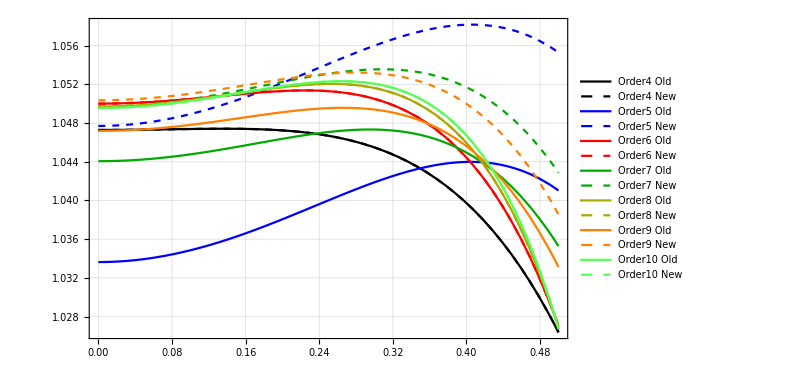

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,max}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[θ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]


Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

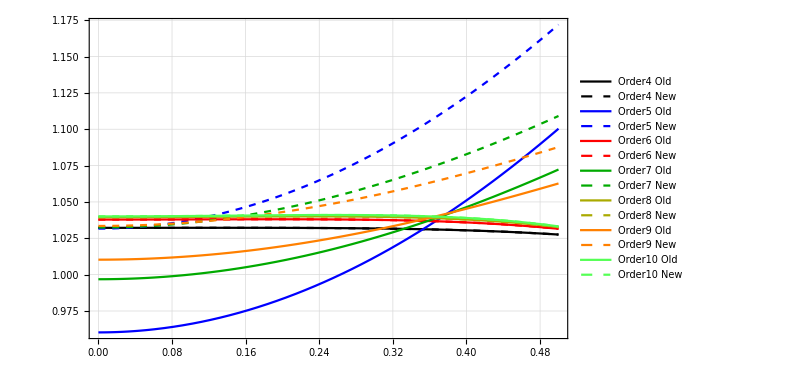

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,max}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[θ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

### Heat Conduction, Kn = 0.3, χ = 1.0

```mathematica
kn=0.3;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

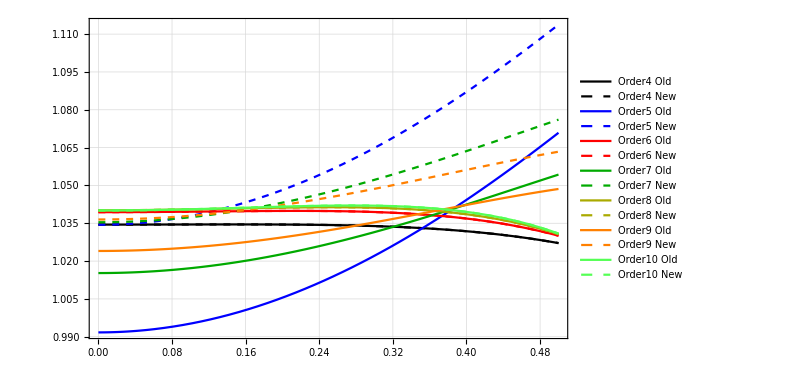

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,max}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[θ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

## Order Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

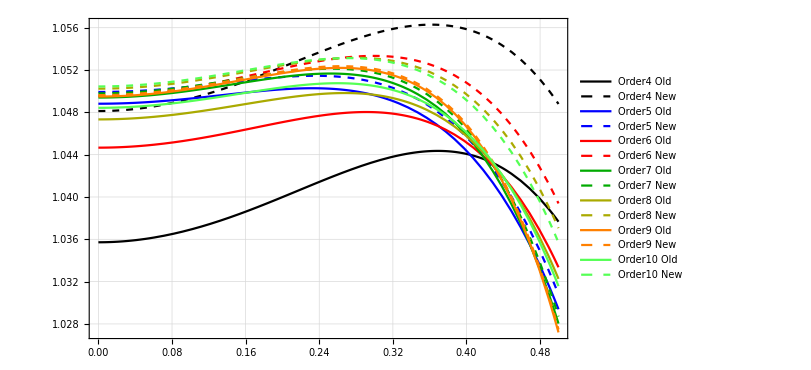

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,6}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[θ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]


Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

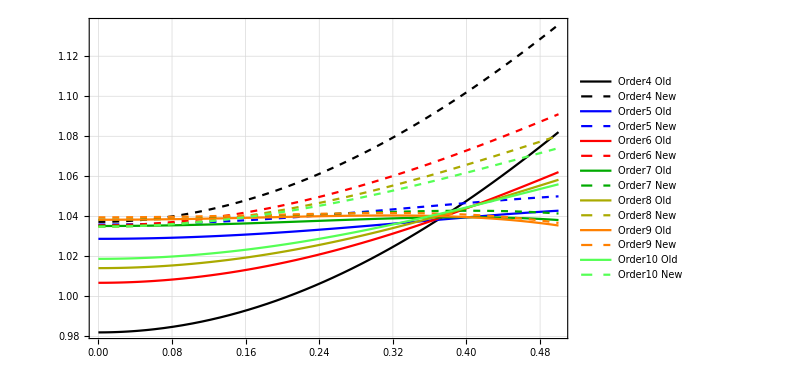

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,max}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[θ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

### Heat Conduction, Kn = 0.3, χ = 1.0

```mathematica
kn=0.3;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

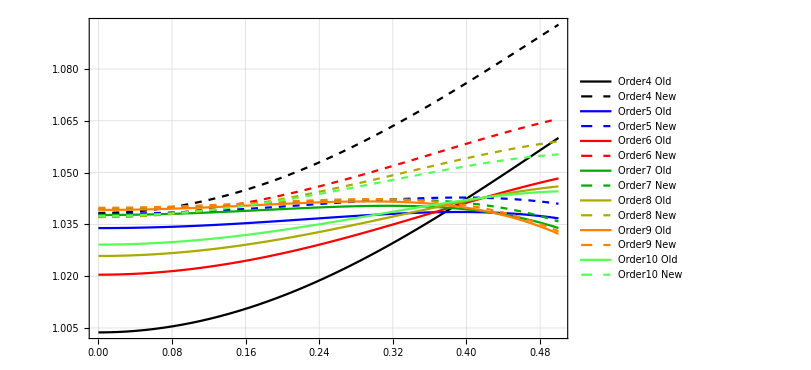

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,max}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[θ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

## Regularized Approximation(Order)

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,0];

,{order,min,max}]

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,1];

,{order,min,max}]
```

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

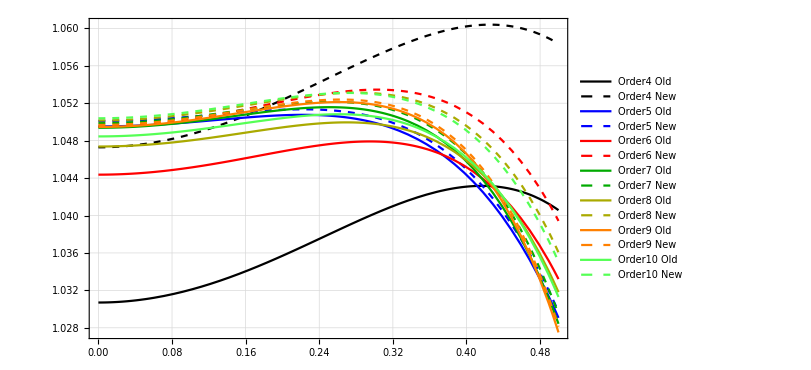

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,max}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[θ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,0];

,{order,min,max}]


Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,1];

,{order,min,max}]
```

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 6

Number of Equations: 9

Number of Equations: 13

Number of Equations: 17

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

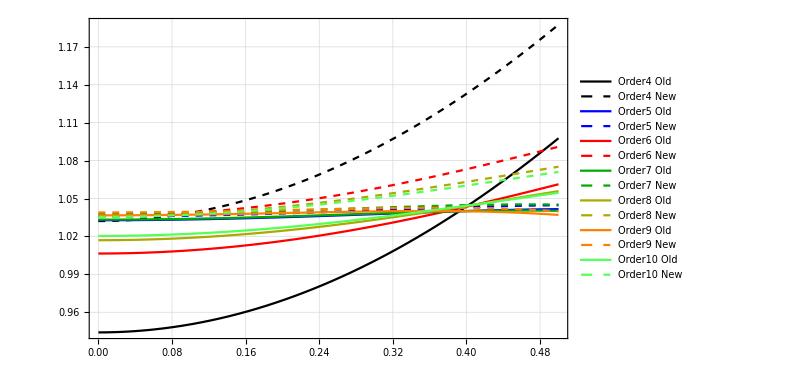

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,max}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[θ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

### Heat Conduction, Kn = 0.3, χ = 1.0

```mathematica
kn=0.3;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,0];

,{order,min,max}]

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,1];

,{order,min,max}]
```

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 4

Number of Equations: 7

Number of Equations: 10

Number of Equations: 14

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

```mathematica
θNSF[x_]=GetHeat[kn,thetaw,alpha,{2,2},0]⟦1⟧;
```

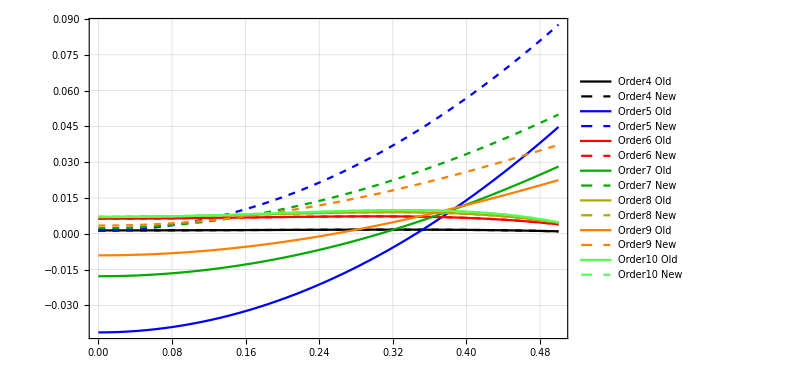

```mathematica
Δθ = Flatten[Table[{temperatureOld[kk][x]-θNSF[x],temperatureNew[kk][x]-θNSF[x]},{kk,min,max}]];

θ = Flatten[Table[{temperatureOld[kk][x],temperatureNew[kk][x]},{kk,min,max}]];

ptstyle = Flatten[Table[{{Thick,colorlist[[kk+1-min]]},{Dashed,colorlist[[kk+1-min]],Thick}},{kk,min,max}],1];

ptlegend=Flatten[Table[{StringJoin["Order",ToString[kk]," ","Old"],StringJoin["Order",ToString[kk]," ","New"]},{kk,min,max}],1];

Plot[Δθ,{x,0,0.5},PlotStyle->ptstyle,ImageSize->600,Frame->True,GridLines->Automatic,PlotLegends->ptlegend,PlotRange->Full]
```

# Accelerated series

## Basic routines

### Accelerate series expansion

```mathematica
(*gives the output of accelerated series*)
CreateAcc[list_]:=Module[{size,Sn,result},
size = Length[list];

(*binomial series corresponding to each term*)
Sn = ConstantArray[0,size];
Do[Sn⟦ii⟧=Sum[(-1)^(jj-1)Binomial[ii-1,jj-1]list⟦ii-jj+1⟧,{jj,1,ii}],{ii,1,size}];

result = Sum[(-1)^(ii-1)Sn⟦ii⟧/2^ii,{ii,1,size}]
]
```

#### coeffs of a_k

```mathematica
(*in the following routine we compute the coefficients of Subscript[a, k]
N = total terms-1, r = k*)
Coeffak[N_,r_]:=(-1)^r Sum[Binomial[N-j,N-r-j]/2^(N-j+1),{j,0,N-r}];
```

#### Averaging factor

```mathematica
(*the following is the factor which should be used while averagin the final result of the accelerated series*)
CoeffAvg[N_]:=Sum[Abs[Coeffak[N,r]],{r,0,N}];
```

### Accelerated solution

```mathematica
AccSolution[list_]:=Module[{ak,AccSol},
ak = Table[(-1)^(ii-1)list⟦ii⟧,{ii,1,Length[list]}];
AccSol = CreateAcc[ak]/CoeffAvg[Length[list]-1];
AccSol
]
```

## Approximation to Pi(test)

```mathematica
(*We accelerate the Leibniz series for the computation of Pi*)
ak[n_]:=1/(2n+1);
numterms = Range[1,30,1];
pi = Table[Sum[(-1)^n ak[n],{n,0,ii}],{ii,1,Length[numterms]}];
pi2=pi[[1;;-2]]+pi[[2;;-1]];
accPI = Table[CreateAcc[Table[ak[n],{n,0,ii}]],{ii,1,Length[numterms]}];
```

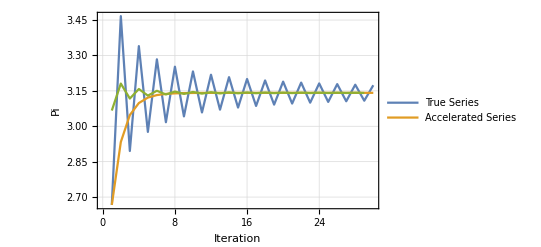

```mathematica
ListPlot[{4*pi,4*accPI,2 pi2},Joined->True,PlotLegends->{"True Series","Accelerated Series"},PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{{"Pi",None},{"Iteration",None}}]
```

## Complete Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

If[OddQ[min],
Print["Value of min should be even"];
Abort[];];

Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureCompleteOld[order][x_],heatfluxCompleteOld[order][x_],stressCompleteOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]

(*solution using stable boundary conditions*)

Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureCompleteNew[order][x_],heatfluxCompleteNew[order][x_],stressCompleteNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 14

Number of Equations: 23

Number of Equations: 34

Number of Equations: 47

Number of Equations: 62

Number of Equations: 79

Number of Equations: 98

Number of Equations: 14

Number of Equations: 23

Number of Equations: 34

Number of Equations: 47

Number of Equations: 62

Number of Equations: 79

Number of Equations: 98

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureCompleteOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureCompleteNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureCompleteOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureCompleteNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]


Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 14

Number of Equations: 23

Number of Equations: 34

Number of Equations: 47

Number of Equations: 62

Number of Equations: 79

Number of Equations: 98

Number of Equations: 14

Number of Equations: 23

Number of Equations: 34

Number of Equations: 47

Number of Equations: 62

Number of Equations: 79

Number of Equations: 98

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

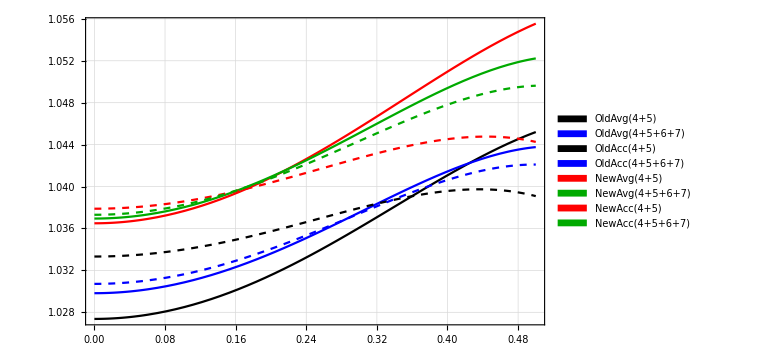

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

### Heat Conduction, Kn = 0.3, χ = 1.0

```mathematica
kn=0.3;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 4;
max = 10;

Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]


Do[
aIdx=MakeComplete[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 14

Number of Equations: 23

Number of Equations: 34

Number of Equations: 47

Number of Equations: 62

Number of Equations: 79

Number of Equations: 98

Number of Equations: 14

Number of Equations: 23

Number of Equations: 34

Number of Equations: 47

Number of Equations: 62

Number of Equations: 79

Number of Equations: 98

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

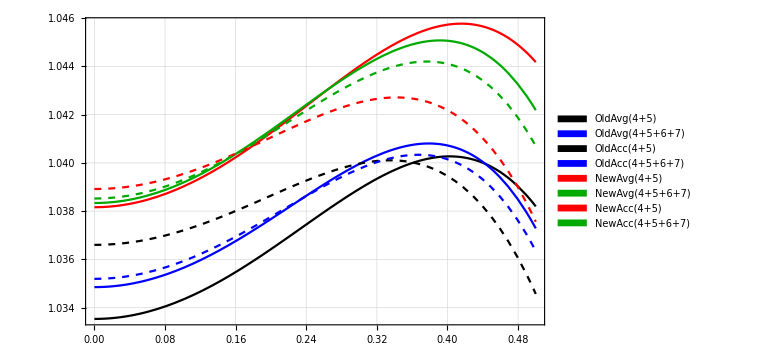

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

## Full Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

If[OddQ[min],
Print["Value of min should be even"];
Abort[];];

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]

(*solution using stable boundary conditions*)

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 34

Number of Equations: 40

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 34

Number of Equations: 40

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

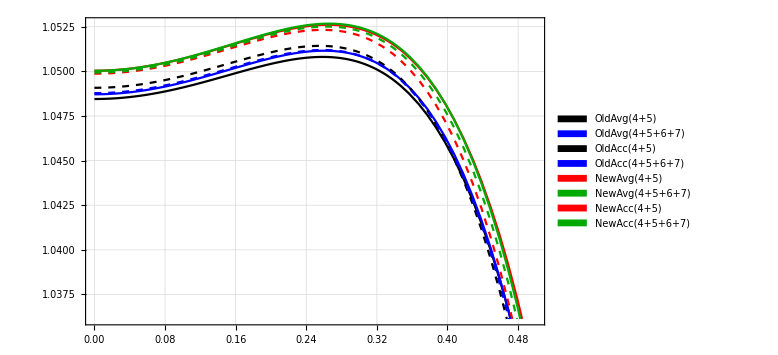

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]


Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 34

Number of Equations: 40

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 34

Number of Equations: 40

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

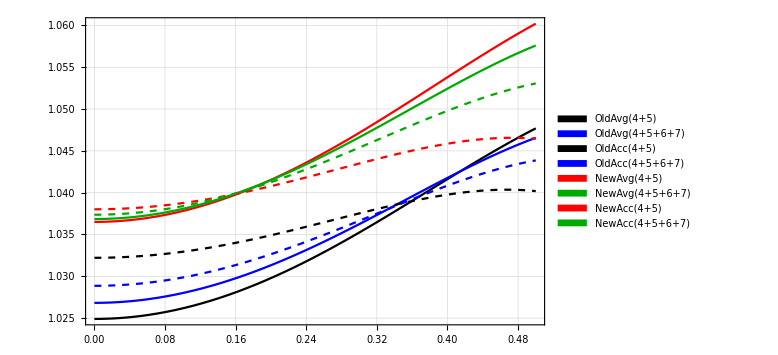

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

### Heat Conduction, Kn = 0.3, χ = 1.0

```mathematica
kn=0.3;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]


Do[
aIdx=MakeFull[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 34

Number of Equations: 40

Number of Equations: 18

Number of Equations: 23

Number of Equations: 28

Number of Equations: 34

Number of Equations: 40

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

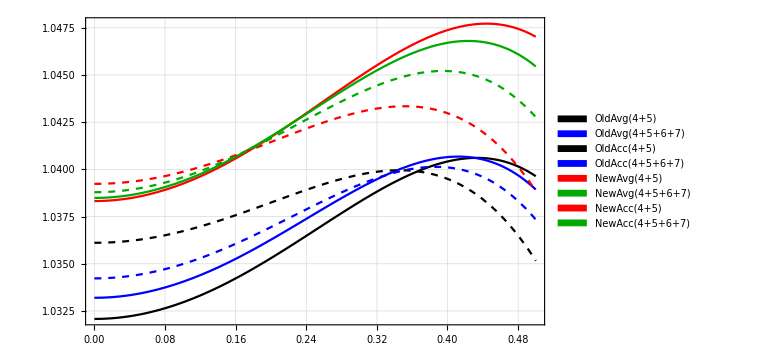

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

## Order Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

If[OddQ[min],
Print["Value of min should be even"];
Abort[];];

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]

(*solution using stable boundary conditions*)

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

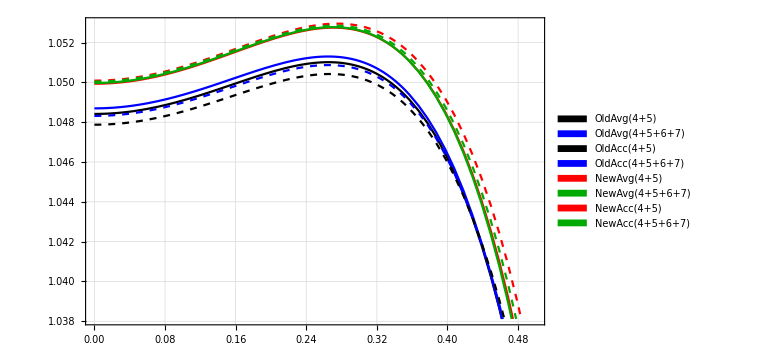

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]


Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

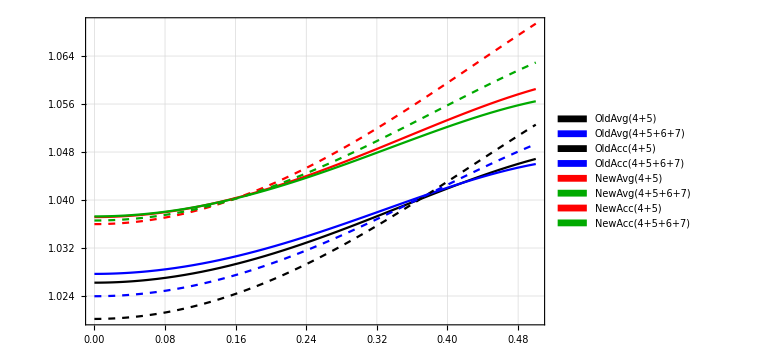

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

### Heat Conduction, Kn = 0.3, χ = 1.0

```mathematica
kn=0.3;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,0];

,{order,min,max}]


Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,0,1];

,{order,min,max}]
```

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

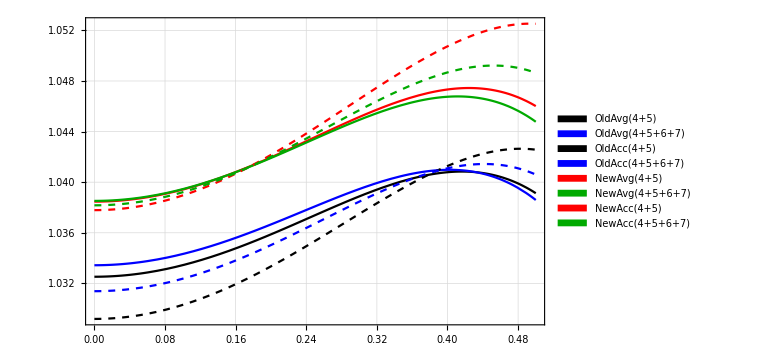

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

## Regularized(Order) Approximation

### Heat Conduction, Kn = 0.1, χ = 1.0

```mathematica
kn=0.1;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

If[OddQ[min],
Print["Value of min should be even"];
Abort[];];

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,0];

,{order,min,max}]

(*solution using stable boundary conditions*)

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,1];

,{order,min,max}]
```

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

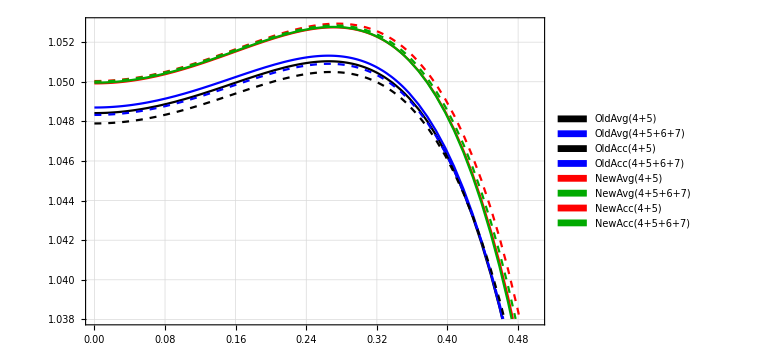

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

### Heat Conduction, Kn = 0.5, χ = 1.0

```mathematica
kn=0.5;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,0];

,{order,min,max}]


Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,1];

,{order,min,max}]
```

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

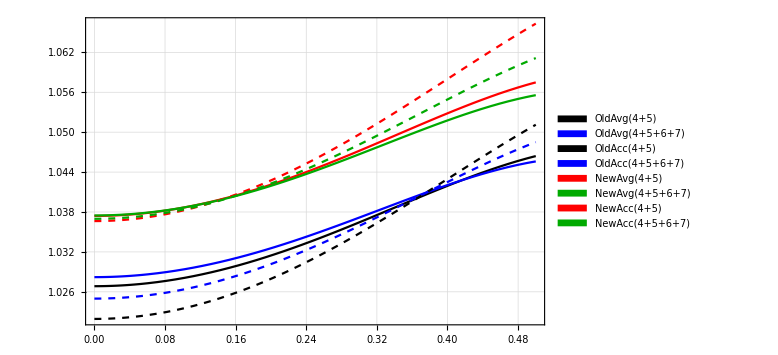

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

### Heat Conduction, Kn = 0.3, χ = 1.0

```mathematica
kn=0.3;
thetaw=-1.0;
alpha=√(2/3)1.0;

min = 8;
max = 12;

Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureOld[order][x_],heatfluxOld[order][x_],stressOld[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,0];

,{order,min,max}]


Do[
aIdx=MakeOrder[order];
nn=Length[aIdx];
Print["Number of Equations: ",Size[aIdx]];

{temperatureNew[order][x_],heatfluxNew[order][x_],stressNew[order][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx,1,1];

,{order,min,max}]
```

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

Number of Equations: 22

Number of Equations: 27

Number of Equations: 33

Number of Equations: 39

Number of Equations: 46

```mathematica
plotID = {2,4};

tempOldAvg = Table[Mean[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAvg = Table[Mean[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];

tempOldAcc = Table[AccSolution[Table[temperatureOld[ii][x],{ii,min,jj}]],{jj,min,max}];

tempNewAcc = Table[AccSolution[Table[temperatureNew[ii][x],{ii,min,jj}]],{jj,min,max}];


plots = Flatten[{tempOldAvg⟦plotID⟧,tempOldAcc⟦plotID⟧,tempNewAvg⟦plotID⟧,tempNewAcc⟦plotID⟧}];
```

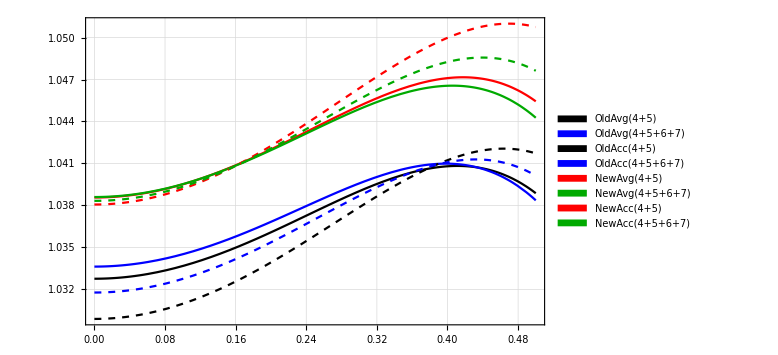

```mathematica
ptstyle = Flatten[{Table[{Thick,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Dashed,colorlist⟦ii⟧},{ii,1,Length[plotID]}],Table[{Thick,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}],
Table[{Dashed,colorlist⟦ii+Length[plotID]⟧},{ii,1,Length[plotID]}]},1];

plotLegends = {"OldAvg(4+5)","OldAvg(4+5+6+7)","OldAcc(4+5)","OldAcc(4+5+6+7)","NewAvg(4+5)","NewAvg(4+5+6+7)","NewAcc(4+5)","NewAcc(4+5+6+7)"};

Plot[plots,{x,0,0.5},PlotLegends->SwatchLegend[plotLegends],GridLines->Automatic,Frame->True,ImageSize->Large,PlotStyle->ptstyle]
```

# Specific theories

## G26

### Kn 0.1

```mathematica
aIdx26 = MakeOrder[4];
kn = 0.1;
alpha = √(2/3.0);
thetaw = -1.0;
{temperature26[4][x_],heatflux26[4][x_],stress26[4][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx26,0,1];

(*The original variables used in the equations*)
OrignalVar={-√(3/2)temperature26[4][x],1/(√2)stress26[4][x],-√(2/5)heatflux26[4][x]}
```

{-1.28525-0.182895 x^2+0.408248 x^4+0.00156433 Cosh[6.57342 x]-2.1684×10^-19 Sinh[6.57342 x],-0.00271529-0.0377124 x^2+0.00112896 Cosh[6.57342 x],-0.210819 x^3}

```mathematica
CForm[Expand[OrignalVar⟦1⟧]]
```

-1.2852476333586613 - 0.18289523412781067*Power(x,2) + 0.408248290463863*Power(x,4) + 
   0.0015643311536178803*Cosh(6.573421981221795*x) - 
   2.168404344971009e-19*Sinh(6.573421981221795*x)

```mathematica
CForm[Expand[OrignalVar⟦2⟧]]
```

-0.002715290039756343 - 0.03771236166328255*Power(x,2) + 
   0.0011289587658037511*Cosh(6.573421981221795*x)

```mathematica
CForm[Expand[OrignalVar⟦3⟧]]
```

-0.21081851067789195*Power(x,3)

```mathematica
CForm[OrignalVar/.{x->0.6}]
```

List(-1.2577845876828238,0.012861815290264145,-0.04553679830642466)

```mathematica
temperature26[4][x]/.x->0.5
```

1.04879

### Kn 0.3

```mathematica
aIdx26 = MakeOrder[4];
kn = 0.3;
alpha = √(2/3.0);
thetaw = -1.0;
{temperature26[4][x_],heatflux26[4][x_],stress26[4][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx26,0,1];

OrignalVar={-√(3/2)temperature26[4][x],1/(√2)stress26[4][x],-√(2/5)heatflux26[4][x]}
```

{-1.36506-0.548686 x^2+0.136083 x^4+0.093382 Cosh[2.19114 x],-0.0733128-0.113137 x^2+0.0673927 Cosh[2.19114 x],-0.210819 x^3}

```mathematica
CForm[Expand[-√(3/2)temperature26[4][x]]]
```

-1.3650564316627332 - 0.548685702383432*Power(x,2) + 0.13608276348795437*Power(x,4) + 
   0.09338201417693054*Cosh(2.191140660407265*x)

```mathematica
CForm[Expand[1/(√2)stress26[4][x]]]
```

-0.07331283107342124 - 0.1131370849898476*Power(x,2) + 
   0.06739266377815037*Cosh(2.191140660407265*x)

```mathematica
CForm[Expand[-√(2/5)heatflux26[4][x]]]
```

-0.21081851067789195*Power(x,3)

```mathematica
CForm[OrignalVar/.{x->0.6}]
```

List(-1.3585501691026851,0.020478113906661516,-0.04553679830642466)

### Kn 0.5

```mathematica
aIdx26 = MakeOrder[4];
kn = 0.5;
alpha = √(2/3.0);
thetaw = -1.0;
{temperature26[4][x_],heatflux26[4][x_],stress26[4][x_]}=GetHeatL2BC[kn,thetaw,alpha,aIdx26,0,1];


OrignalVar={-√(3/2)temperature26[4][x],1/(√2)stress26[4][x],-√(2/5)heatflux26[4][x]}
```

{-1.72982-0.914476 x^2+0.0816497 x^4+0.459428 Cosh[1.31468 x]-2.77556×10^-17 Sinh[1.31468 x],-0.339411-0.188562 x^2+0.331563 Cosh[1.31468 x],-0.210819 x^3}

```mathematica
CForm[Expand[-√(3/2)temperature26[4][x]]]
```

-1.7298151776227189 - 0.9144761706390533*Power(x,2) + 0.08164965809277261*Power(x,4) + 
   0.45942750968124524*Cosh(1.314684396244359*x) - 
   2.7755575615628914e-17*Sinh(1.314684396244359*x)

```mathematica
CForm[Expand[1/(√2)stress26[4][x]]]
```

-0.3394112549695428 - 0.1885618083164127*Power(x,2) + 
   0.33156324548448296*Cosh(1.314684396244359*x)

```mathematica
CForm[Expand[-√(2/5)heatflux26[4][x]]]
```

-0.21081851067789195*Power(x,3)

```mathematica
CForm[OrignalVar/.{x->0.6}]
```

List(-1.4385175132464387,0.03288360045585703,-0.04553679830642466)

```mathematica
CForm[N[√(2/3.0),15]]
```

0.816496580927726